```mathematica
Q={{0,0},{0,4 π/3},{0,-4 π/3}}
```

{{0,0},{0,(4 π)/3},{0,-(4 π)/3}}

```mathematica
a=0*{0,-1}+0*{(√3)/2,-1/2}
```

{0,0}

```mathematica
b=-1*{0,-1}+1*{(√3)/2,-1/2}
```

{(√3)/2,1/2}

```mathematica
c=-2*{0,-1}+2*{(√3)/2,-1/2}
```

{√3,1}

```mathematica
H00=1/3Table[3*U1*Exp[-I*(q1-q2).a]+(U0+3*U1)Exp[-I*(q1-q2).b]+6*U1*Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]
```

{{1/3 (U0+12 U1),1/3 (3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)),1/3 (3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1))},{1/3 (3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (U0+12 U1),1/3 (3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1))},{1/3 (3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)),1/3 (3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (U0+12 U1)}}

```mathematica
Eigenvalues[H00]//Simplify
```

{U0+3 U1,3 U1,6 U1}

```mathematica
Eigenvalues[H11]//Simplify
```

{U0+3 U1,3 U1,6 U1}

```mathematica
Collect[H00//Expand,{U0,U1}]//MatrixForm
```

(U0/3+4 U1 | 1/3 ⅇ^((2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | 1/3 ⅇ^(-(2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1
1/3 ⅇ^(-(2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | U0/3+4 U1 | 1/3 ⅇ^((2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1
1/3 ⅇ^((2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | 1/3 ⅇ^(-(2 ⅈ π)/3) U0+(2+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | U0/3+4 U1)

```mathematica
H11=1/3Table[3*U1*Exp[-I*(q1-q2).b]+(U0+3*U1)Exp[-I*(q1-q2).a]+6*U1*Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]
```

{{1/3 (U0+12 U1),1/3 (U0+3 U1+3 ⅇ^(-(2 ⅈ π)/3) U1+6 ⅇ^((2 ⅈ π)/3) U1),1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+3 ⅇ^((2 ⅈ π)/3) U1)},{1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+3 ⅇ^((2 ⅈ π)/3) U1),1/3 (U0+12 U1),1/3 (U0+3 U1+3 ⅇ^(-(2 ⅈ π)/3) U1+6 ⅇ^((2 ⅈ π)/3) U1)},{1/3 (U0+3 U1+3 ⅇ^(-(2 ⅈ π)/3) U1+6 ⅇ^((2 ⅈ π)/3) U1),1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+3 ⅇ^((2 ⅈ π)/3) U1),1/3 (U0+12 U1)}}

```mathematica
Collect[H11//Expand,{U0,U1}]//MatrixForm
```

(U0/3+4 U1 | U0/3+(1+ⅇ^(-(2 ⅈ π)/3)+2 ⅇ^((2 ⅈ π)/3)) U1 | U0/3+(1+2 ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1
U0/3+(1+2 ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | U0/3+4 U1 | U0/3+(1+ⅇ^(-(2 ⅈ π)/3)+2 ⅇ^((2 ⅈ π)/3)) U1
U0/3+(1+ⅇ^(-(2 ⅈ π)/3)+2 ⅇ^((2 ⅈ π)/3)) U1 | U0/3+(1+2 ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)) U1 | U0/3+4 U1)

```mathematica
Collect[H00//Expand,{U0,U1}]/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(0.796267 | -0.164283-0.0145204 ⅈ | -0.164283+0.0145204 ⅈ
-0.164283+0.0145204 ⅈ | 0.796267 | -0.164283-0.0145204 ⅈ
-0.164283-0.0145204 ⅈ | -0.164283+0.0145204 ⅈ | 0.796267)

```mathematica
Collect[H11//Expand,{U0,U1}]/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(0.796267 | 0.0947167+0.135013 ⅈ | 0.0947167-0.135013 ⅈ
0.0947167-0.135013 ⅈ | 0.796267 | 0.0947167+0.135013 ⅈ
0.0947167+0.135013 ⅈ | 0.0947167-0.135013 ⅈ | 0.796267)

```mathematica
Hfock00=1/3Table[(-U0)*Exp[-I*(q1-q2).a],{q1,Q},{q2,Q}]
```

{{-U0/3,-U0/3,-U0/3},{-U0/3,-U0/3,-U0/3},{-U0/3,-U0/3,-U0/3}}

```mathematica
Hfock11=1/3Table[(-U0)*Exp[-I*(q1-q2).b],{q1,Q},{q2,Q}]
```

{{-U0/3,-1/3 ⅇ^(-(2 ⅈ π)/3) U0,-1/3 ⅇ^((2 ⅈ π)/3) U0},{-1/3 ⅇ^((2 ⅈ π)/3) U0,-U0/3,-1/3 ⅇ^(-(2 ⅈ π)/3) U0},{-1/3 ⅇ^(-(2 ⅈ π)/3) U0,-1/3 ⅇ^((2 ⅈ π)/3) U0,-U0/3}}

```mathematica
Hfock00/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(-0.172667 | -0.172667 | -0.172667
-0.172667 | -0.172667 | -0.172667
-0.172667 | -0.172667 | -0.172667)

```mathematica
Hfock11/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(-0.172667 | 0.0863333+0.149534 ⅈ | 0.0863333-0.149534 ⅈ
0.0863333-0.149534 ⅈ | -0.172667 | 0.0863333+0.149534 ⅈ
0.0863333+0.149534 ⅈ | 0.0863333-0.149534 ⅈ | -0.172667)

```mathematica
Hhartree00=1/3Table[(3*U1+U0)*Exp[-I*(q1-q2).a]+(U0+3*U1)Exp[-I*(q1-q2).b]+6*U1*Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]
```

{{1/3 (2 U0+12 U1),1/3 (U0+3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)),1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1))},{1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (2 U0+12 U1),1/3 (U0+3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1))},{1/3 (U0+3 U1+6 ⅇ^((2 ⅈ π)/3) U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)),1/3 (U0+3 U1+6 ⅇ^(-(2 ⅈ π)/3) U1+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (2 U0+12 U1)}}

```mathematica
Hhartree11=1/3Table[(3*U1+U0)*Exp[-I*(q1-q2).b]+(U0+3*U1)Exp[-I*(q1-q2).a]+6*U1*Exp[-I*(q1-q2).c]{q1,Q},{q2,Q}]
```

{{1/3 (2 U0+12 U1),1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1))},{1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (2 U0+12 U1),1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1))},{1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (6 U1+ⅇ^(-(2 ⅈ π)/3) (U0+3 U1)+ⅇ^((2 ⅈ π)/3) (U0+3 U1)),1/3 (2 U0+12 U1)}}

```mathematica
Hhartree00/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(0.968933 | -0.0167667+0. ⅈ | -0.0167667+0. ⅈ
-0.0167667+0. ⅈ | 0.968933 | -0.0167667+0. ⅈ
-0.0167667+0. ⅈ | -0.0167667+0. ⅈ | 0.968933)

```mathematica
Hhartree11/.{U0->0.5180,U1->0.1559}//MatrixForm
```

(0.968933 | -0.0167667+0. ⅈ | -0.0167667+0. ⅈ
-0.0167667+0. ⅈ | 0.968933 | -0.0167667+0. ⅈ
-0.0167667+0. ⅈ | -0.0167667+0. ⅈ | 0.968933)

```mathematica
Eigenvalues[H00]/.{U0->0.5180,U1->0.1559}//Chop
```

{0.9857,0.4677,0.9354}

```mathematica
mA=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],{1,0,0}}])]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
mB=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],(*{0,0,1}*){Cos[2 π/3],Sin[2 π/3],0}}])]
```

{{1/2,1/2 (-1/2+(ⅈ √3)/2)},{1/2 (-1/2-(ⅈ √3)/2),1/2}}

```mathematica
mC=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],(*{0,0,1}*){Cos[4 π/3],Sin[4 π/3],0}}])]
```

{{1/2,1/2 (-1/2-(ⅈ √3)/2)},{1/2 (-1/2+(ⅈ √3)/2),1/2}}

```mathematica
Hartree00=1/3U0*Table[(mA[[1,1]]+mA[[2,2]])Exp[-I*(q1-q2).a]+(mB[[1,1]]+mB[[2,2]])Exp[-I*(q1-q2).b]+(mC[[1,1]]+mC[[2,2]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{U0,0,0},{0,U0,0},{0,0,U0}}

```mathematica
Hartree11=1/3U0*Table[(mA[[1,1]]+mA[[2,2]])Exp[-I*(q1-q2).a]+(mB[[1,1]]+mB[[2,2]])Exp[-I*(q1-q2).b]+(mC[[1,1]]+mC[[2,2]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify//Chop
```

{{U0,0,0},{0,U0,0},{0,0,U0}}

```mathematica
Fock00=1/3U0*Table[(mA[[1,1]])Exp[-I*(q1-q2).a]+(mB[[1,1]])Exp[-I*(q1-q2).b]+(mC[[1,1]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{U0/2,0,0},{0,U0/2,0},{0,0,U0/2}}

```mathematica
Fock01=1/3U0*Table[(mA[[2,1]])Exp[-I*(q1-q2).a]+(mB[[2,1]])Exp[-I*(q1-q2).b]+(mC[[2,1]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{0,U0/2,0},{0,0,U0/2},{U0/2,0,0}}

```mathematica
Fock11=1/3U0*Table[(mA[[2,2]])Exp[-I*(q1-q2).a]+(mB[[2,2]])Exp[-I*(q1-q2).b]+(mC[[2,2]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{U0/2,0,0},{0,U0/2,0},{0,0,U0/2}}

```mathematica
Fock10=1/3U0*Table[(mA[[1,2]])Exp[-I*(q1-q2).a]+(mB[[1,2]])Exp[-I*(q1-q2).b]+(mC[[1,2]])Exp[-I*(q1-q2).c],{q1,Q},{q2,Q}]//Simplify
```

{{0,0,U0/2},{U0/2,0,0},{0,U0/2,0}}

```mathematica
H=ArrayFlatten[{{Hartree00,0},{0,Hartree11}}]-ArrayFlatten[{{Fock00,Fock01},{Fock10,Fock11}}]//MatrixForm
```

(U0/2 | 0 | 0 | 0 | -U0/2 | 0
0 | U0/2 | 0 | 0 | 0 | -U0/2
0 | 0 | U0/2 | -U0/2 | 0 | 0
0 | 0 | -U0/2 | U0/2 | 0 | 0
-U0/2 | 0 | 0 | 0 | U0/2 | 0
0 | -U0/2 | 0 | 0 | 0 | U0/2)

```mathematica
ArrayFlatten[{{Hartree00,0},{0,Hartree11}}]//MatrixForm
```

(U0 | 0 | 0 | 0 | 0 | 0
0 | U0 | 0 | 0 | 0 | 0
0 | 0 | U0 | 0 | 0 | 0
0 | 0 | 0 | U0 | 0 | 0
0 | 0 | 0 | 0 | U0 | 0
0 | 0 | 0 | 0 | 0 | U0)

```mathematica
ArrayFlatten[{{Fock00,Fock01},{Fock10,Fock11}}]//MatrixForm
```

(U0/2 | 0 | 0 | 0 | U0/2 | 0
0 | U0/2 | 0 | 0 | 0 | U0/2
0 | 0 | U0/2 | U0/2 | 0 | 0
0 | 0 | U0/2 | U0/2 | 0 | 0
U0/2 | 0 | 0 | 0 | U0/2 | 0
0 | U0/2 | 0 | 0 | 0 | U0/2)

```mathematica
ave=Table[(mA)Exp[I*(q1-q2).a]+(mB)Exp[I*(q1-q2).b]+(mC)Exp[I*(q1-q2).c],{q1,Q},{q2,Q}]/3//Simplify
```

{{{{1/2,0},{0,1/2}},{{0,1/2},{0,0}},{{0,0},{1/2,0}}},{{{0,0},{1/2,0}},{{1/2,0},{0,1/2}},{{0,1/2},{0,0}}},{{{0,1/2},{0,0}},{{0,0},{1/2,0}},{{1/2,0},{0,1/2}}}}

```mathematica
ave//MatrixForm
```

((1/2 | 0
0 | 1/2) | (0 | 1/2
0 | 0) | (0 | 0
1/2 | 0)
(0 | 0
1/2 | 0) | (1/2 | 0
0 | 1/2) | (0 | 1/2
0 | 0)
(0 | 1/2
0 | 0) | (0 | 0
1/2 | 0) | (1/2 | 0
0 | 1/2))

```mathematica
ave//MatrixForm
```

((1/2 | ⅈ/(2 √3)
-ⅈ/(2 √3) | 1/2) | (0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0) | (0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0)
(0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0) | (1/2 | ⅈ/(2 √3)
-ⅈ/(2 √3) | 1/2) | (0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0)
(0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0) | (0 | 1/12 (3-ⅈ √3)
1/12 (3+ⅈ √3) | 0) | (1/2 | ⅈ/(2 √3)
-ⅈ/(2 √3) | 1/2))

```mathematica
ArrayFlatten[{{Fock00,Fock01},{Fock10,Fock11}}]/.U0-> 0.4995//MatrixForm
```

(0.24975 | 0 | 0 | 0.-0.144193 ⅈ | 0.124875+0.0720966 ⅈ | 0.124875+0.0720966 ⅈ
0 | 0.24975 | 0 | 0.124875+0.0720966 ⅈ | 0.-0.144193 ⅈ | 0.124875+0.0720966 ⅈ
0 | 0 | 0.24975 | 0.124875+0.0720966 ⅈ | 0.124875+0.0720966 ⅈ | 0.-0.144193 ⅈ
0.+0.144193 ⅈ | 0.124875-0.0720966 ⅈ | 0.124875-0.0720966 ⅈ | 0.24975 | 0 | 0
0.124875-0.0720966 ⅈ | 0.+0.144193 ⅈ | 0.124875-0.0720966 ⅈ | 0 | 0.24975 | 0
0.124875-0.0720966 ⅈ | 0.124875-0.0720966 ⅈ | 0.+0.144193 ⅈ | 0 | 0 | 0.24975)

```mathematica
{mA,mB,mC}
```

{{{0.5,0.5},{0.5,0.5}},{{0.5,-0.25+0.433013 ⅈ},{-0.25-0.433013 ⅈ,0.5}},{{0.5,-0.25+0.433013 ⅈ},{-0.25-0.433013 ⅈ,0.5}}}

```mathematica
expqq=Table[Exp[I*(q1-q2).i],{i,{a,b,c}},{q1,Q},{q2,Q}]
```

{{{1,1,1},{1,1,1},{1,1,1}},{{1,ⅇ^((2 ⅈ π)/3),ⅇ^(-(2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),1,ⅇ^((2 ⅈ π)/3)},{ⅇ^((2 ⅈ π)/3),ⅇ^(-(2 ⅈ π)/3),1}},{{1,ⅇ^(-(2 ⅈ π)/3),ⅇ^((2 ⅈ π)/3)},{ⅇ^((2 ⅈ π)/3),1,ⅇ^(-(2 ⅈ π)/3)},{ⅇ^(-(2 ⅈ π)/3),ⅇ^((2 ⅈ π)/3),1}}}

```mathematica
expqq[[1]]
```

{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}}

```mathematica
expqq[[2]]//MatrixForm
```

(1 | ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | 1 | ⅇ^((2 ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3) | 1)

```mathematica
expqq[[3]]//MatrixForm
```

(1 | ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | 1 | ⅇ^(-(2 ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3) | 1)

```mathematica
Q
```

{{0,0},{0,(4 π)/3},{0,-(4 π)/3}}

```mathematica
Exp[I*(4 π)/3]
```

ⅇ^(-(2 ⅈ π)/3)

```mathematica
0-4 π/3
```

-(4 π)/3

```mathematica
qq=Table[(q1-q2).i,{i,{a,b,c}},{q1,Q},{q2,Q}]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,-(4 π)/3,(4 π)/3},{(4 π)/3,0,(8 π)/3},{-(4 π)/3,-(8 π)/3,0}},{{0,-(2 π)/3,(2 π)/3},{(2 π)/3,0,(4 π)/3},{-(2 π)/3,-(4 π)/3,0}}}

```mathematica
qq[[2]]//N//MatrixForm
```

(0. | -4.18879 | 4.18879
4.18879 | 0. | 8.37758
-4.18879 | -8.37758 | 0.)

```mathematica
qq[[3]]//N//MatrixForm
```

(0. | -2.0944 | 2.0944
2.0944 | 0. | 4.18879
-2.0944 | -4.18879 | 0.)

```mathematica
c
```

{(√3)/2,1/2}

```mathematica
expqq[[3]]//N
```

{{1.,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ},{-0.5+0.866025 ⅈ,1.,-0.5-0.866025 ⅈ},{-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,1.}}

```mathematica
Q=Flatten[Table[i*2π{-1/√(3),-1}+j*2π{2/√3,0},{i,{0,1/3,2/3}},{j,{0,1/3,2/3}}],1]
```

{{0,0},{(4 π)/(3 √3),0},{(8 π)/(3 √3),0},{-(2 π)/(3 √3),-(2 π)/3},{(2 π)/(3 √3),-(2 π)/3},{(2 π)/(√3),-(2 π)/3},{-(4 π)/(3 √3),-(4 π)/3},{0,-(4 π)/3},{(4 π)/(3 √3),-(4 π)/3}}

```mathematica
r=Table[i[[1]]*{0,-1}+i[[2]]*{(√3)/2,-1/2},{i,{{0,0},{-2,1},{-4,2}}}]
```

{{0,0},{(√3)/2,3/2},{√3,3}}

```mathematica
mA=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],{1,0,0}}])]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
mB=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],(*{0,0,1}*){Cos[2 π/3],Sin[2 π/3],0}}])]
```

{{1/2,1/2 (-1/2+(ⅈ √3)/2)},{1/2 (-1/2-(ⅈ √3)/2),1/2}}

```mathematica
mC=1/2*Conjugate[(IdentityMatrix[2]+Total@MapThread[Times,{PauliMatrix/@Range[3],(*{0,0,1}*){Cos[4 π/3],Sin[4 π/3],0}}])]
```

{{1/2,1/2 (-1/2-(ⅈ √3)/2)},{1/2 (-1/2+(ⅈ √3)/2),1/2}}

```mathematica
r[[1]]
```

{0,0}

```mathematica
Q
```

{{{0,0},{2/(3 √3),0},{4/(3 √3),0}},{{-1/(3 √3),-1/3},{1/(3 √3),-1/3},{1/(√3),-1/3}},{{-2/(3 √3),-2/3},{0,-2/3},{2/(3 √3),-2/3}}}

```mathematica
Hartree00=1/3Table[(U0(mA[[1,1]]+mA[[2,2]])+3U2(mB[[1,1]]+mB[[2,2]])+3U2(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[1]]]+(3U2(mA[[1,1]]+mA[[2,2]])+U0(mB[[1,1]]+mB[[2,2]])+3U2(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[2]]]+(3U2(mA[[1,1]]+mA[[2,2]])+3U2(mB[[1,1]]+mB[[2,2]])+U0(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]//Simplify
```

{{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2}}

```mathematica
Collect[Hartree00//Expand,{U0,U2}]//MatrixForm
```

(U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2)

```mathematica
Hartree11=1/3Table[(U0(mA[[1,1]]+mA[[2,2]])+3U2(mB[[1,1]]+mB[[2,2]])+3U2(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[1]]]+(3U2(mA[[1,1]]+mA[[2,2]])+U0(mB[[1,1]]+mB[[2,2]])+3U2(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[2]]]+(3U2(mA[[1,1]]+mA[[2,2]])+3U2(mB[[1,1]]+mB[[2,2]])+U0(mC[[1,1]]+mC[[2,2]]))Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]//Simplify
```

{{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,0,U0+6 U2,0,U0+6 U2,0,U0+6 U2,0,0},{U0+6 U2,0,0,0,0,U0+6 U2,0,U0+6 U2,0},{0,U0+6 U2,0,U0+6 U2,0,0,0,0,U0+6 U2}}

```mathematica
Collect[Hartree11//Expand,{U0,U2}]//MatrixForm
```

(U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0
U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2 | 0 | U0+6 U2 | 0
0 | U0+6 U2 | 0 | U0+6 U2 | 0 | 0 | 0 | 0 | U0+6 U2)

```mathematica
Fock01=1/3Table[(U0*mA[[2,1]]+3U2*mB[[2,1]]+3U2*mC[[2,1]])Exp[-I*(q1-q2).r[[1]]]+(3U2*mA[[2,1]]+U0*mB[[2,1]]+3U2*mC[[2,1]])Exp[-I*(q1-q2).r[[2]]]+(3U2*mA[[2,1]]+3U2*mB[[2,1]]+U0*mC[[2,1]])Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]
```

{{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)}}

```mathematica
Fock10=1/3Table[(U0*mA[[1,2]]+3U2*mB[[1,2]]+3U2*mC[[1,2]])Exp[-I*(q1-q2).r[[1]]]+(3U2*mA[[1,2]]+U0*mB[[1,2]]+3U2*mC[[1,2]])Exp[-I*(q1-q2).r[[2]]]+(3U2*mA[[1,2]]+3U2*mB[[1,2]]+U0*mC[[1,2]])Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]
```

{{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2))},{1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+3/2 (-1/2-(ⅈ √3)/2) U2+3/2 (-1/2+(ⅈ √3)/2) U2+ⅇ^(-(2 ⅈ π)/3) (1/2 (-1/2+(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2-(ⅈ √3)/2) U2)+ⅇ^((2 ⅈ π)/3) (1/2 (-1/2-(ⅈ √3)/2) U0+(3 U2)/2+3/2 (-1/2+(ⅈ √3)/2) U2)),1/3 (U0/2+1/2 (-1/2-(ⅈ √3)/2) U0+1/2 (-1/2+(ⅈ √3)/2) U0+3 U2+3 (-1/2-(ⅈ √3)/2) U2+3 (-1/2+(ⅈ √3)/2) U2)}}

```mathematica
Fock00=1/3Table[(U0*mA[[1,1]]+3U2*mB[[1,1]]+3U2*mC[[1,1]])Exp[-I*(q1-q2).r[[1]]]+(3U2*mA[[1,1]]+U0*mB[[1,1]]+3U2*mC[[1,1]])Exp[-I*(q1-q2).r[[2]]]+(3U2*mA[[1,1]]+3U2*mB[[1,1]]+U0*mC[[1,1]])Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]
```

{{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)}}

```mathematica
Fock11=1/3Table[(U0*mA[[2,2]]+3U2*mB[[2,2]]+3U2*mC[[2,2]])Exp[-I*(q1-q2).r[[1]]]+(3U2*mA[[2,2]]+U0*mB[[2,2]]+3U2*mC[[2,2]])Exp[-I*(q1-q2).r[[2]]]+(3U2*mA[[2,2]]+3U2*mB[[2,2]]+U0*mC[[2,2]])Exp[-I*(q1-q2).r[[3]]],{q1,Q},{q2,Q}]
```

{{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2))},{1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 (U0/2+3 U2+ⅇ^(-(2 ⅈ π)/3) (U0/2+3 U2)+ⅇ^((2 ⅈ π)/3) (U0/2+3 U2)),1/3 ((3 U0)/2+9 U2)}}

```mathematica
H=ArrayFlatten[{{Hartree00,0},{0,Hartree11}}]-ArrayFlatten[{{Fock00,Fock01},{Fock10,Fock11}}];
```

```mathematica
Eigenvalues[H]
```

{0,0,0,0,0,0,0,0,0,0,0,0,-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,1],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,2],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,3],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,4],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,5],-1/12 (-1)^(1/3) Root[22674816 U0^6-5668704 (-1)^(1/3) U0^6+5668704 (-1)^(2/3) U0^6-5668704 (-1)^(1/6) √3 U0^6+5668704 (-1)^(5/6) √3 U0^6+816293376 U0^5 U2-204073344 (-1)^(1/3) U0^5 U2+204073344 (-1)^(2/3) U0^5 U2-204073344 (-1)^(1/6) √3 U0^5 U2+204073344 (-1)^(5/6) √3 U0^5 U2+12244400640 U0^4 U2^2-3061100160 (-1)^(1/3) U0^4 U2^2+3061100160 (-1)^(2/3) U0^4 U2^2-3061100160 (-1)^(1/6) √3 U0^4 U2^2+3061100160 (-1)^(5/6) √3 U0^4 U2^2+164074968576 U0^3 U2^3+8571080448 (-1)^(1/3) U0^3 U2^3-8571080448 (-1)^(2/3) U0^3 U2^3+8571080448 (-1)^(1/6) √3 U0^3 U2^3-8571080448 (-1)^(5/6) √3 U0^3 U2^3+738337358592 U0^2 U2^4+38569862016 (-1)^(1/3) U0^2 U2^4-38569862016 (-1)^(2/3) U0^2 U2^4+38569862016 (-1)^(1/6) √3 U0^2 U2^4-38569862016 (-1)^(5/6) √3 U0^2 U2^4+1504224618624 U0 U2^5-41324852160 (-1)^(1/3) U0 U2^5+41324852160 (-1)^(2/3) U0 U2^5-41324852160 (-1)^(1/6) √3 U0 U2^5+41324852160 (-1)^(5/6) √3 U0 U2^5+1281070416960 U2^6-152901952992 (-1)^(1/3) U2^6+152901952992 (-1)^(2/3) U2^6-152901952992 (-1)^(1/6) √3 U2^6+152901952992 (-1)^(5/6) √3 U2^6+(-1889568 U0^5+7558272 (-1)^(1/3) U0^5-1889568 (-1)^(2/3) U0^5-1889568 ⅈ √3 U0^5-1889568 (-1)^(1/6) √3 U0^5-56687040 U0^4 U2+226748160 (-1)^(1/3) U0^4 U2-56687040 (-1)^(2/3) U0^4 U2-56687040 ⅈ √3 U0^4 U2-56687040 (-1)^(1/6) √3 U0^4 U2-68024448 U0^3 U2^2+3945417984 (-1)^(1/3) U0^3 U2^2-68024448 (-1)^(2/3) U0^3 U2^2-68024448 ⅈ √3 U0^3 U2^2-68024448 (-1)^(1/6) √3 U0^3 U2^2+1428513408 U0^2 U2^3+27345828096 (-1)^(1/3) U0^2 U2^3+1428513408 (-1)^(2/3) U0^2 U2^3+1428513408 ⅈ √3 U0^2 U2^3+1428513408 (-1)^(1/6) √3 U0^2 U2^3+153055008 U0 U2^4+73772513856 (-1)^(1/3) U0 U2^4+153055008 (-1)^(2/3) U0 U2^4+153055008 ⅈ √3 U0 U2^4+153055008 (-1)^(1/6) √3 U0 U2^4-6428310336 U2^5+75303063936 (-1)^(1/3) U2^5-6428310336 (-1)^(2/3) U2^5-6428310336 ⅈ √3 U2^5-6428310336 (-1)^(1/6) √3 U2^5) #1+(262440 U0^4-262440 (-1)^(1/3) U0^4+1049760 (-1)^(2/3) U0^4-262440 ⅈ √3 U0^4-262440 (-1)^(5/6) √3 U0^4+2519424 U0^3 U2-2519424 (-1)^(1/3) U0^3 U2+32752512 (-1)^(2/3) U0^3 U2-2519424 ⅈ √3 U0^3 U2-2519424 (-1)^(5/6) √3 U0^3 U2-11337408 U0^2 U2^2+11337408 (-1)^(1/3) U0^2 U2^2+362797056 (-1)^(2/3) U0^2 U2^2+11337408 ⅈ √3 U0^2 U2^2+11337408 (-1)^(5/6) √3 U0^2 U2^2-28343520 U0 U2^3+28343520 (-1)^(1/3) U0 U2^3+1417176000 (-1)^(2/3) U0 U2^3+28343520 ⅈ √3 U0 U2^3+28343520 (-1)^(5/6) √3 U0 U2^3+97785144 U2^4-97785144 (-1)^(1/3) U2^4+1845163152 (-1)^(2/3) U2^4-97785144 ⅈ √3 U2^4-97785144 (-1)^(5/6) √3 U2^4) #1^2+(-93312 U0^3+11664 (-1)^(1/3) U0^3-11664 (-1)^(2/3) U0^3+11664 (-1)^(1/6) √3 U0^3-11664 (-1)^(5/6) √3 U0^3-2099520 U0^2 U2-13226976 U0 U2^2-314928 (-1)^(1/3) U0 U2^2+314928 (-1)^(2/3) U0 U2^2-314928 (-1)^(1/6) √3 U0 U2^2+314928 (-1)^(5/6) √3 U0 U2^2-23934528 U2^3+629856 (-1)^(1/3) U2^3-629856 (-1)^(2/3) U2^3+629856 (-1)^(1/6) √3 U2^3-629856 (-1)^(5/6) √3 U2^3) #1^3+(162 U0^2-4536 (-1)^(1/3) U0^2+162 (-1)^(2/3) U0^2+162 ⅈ √3 U0^2+162 (-1)^(1/6) √3 U0^2-972 U0 U2-60264 (-1)^(1/3) U0 U2-972 (-1)^(2/3) U0 U2-972 ⅈ √3 U0 U2-972 (-1)^(1/6) √3 U0 U2+1458 U2^2-172044 (-1)^(1/3) U2^2+1458 (-1)^(2/3) U2^2+1458 ⅈ √3 U2^2+1458 (-1)^(1/6) √3 U2^2) #1^4+(-108 (-1)^(2/3) U0-648 (-1)^(2/3) U2) #1^5+#1^6&,6]}

```mathematica
Eigenvalues[H/.{U0->0.5230,U2->0}]//Chop//Sort
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.569,1.569,1.569}

```mathematica
Hartree00/.{U0->0.5230,U2->0.0833}//MatrixForm
```

(1.0228 | 0 | 0 | 0 | 0 | 1.0228 | 0 | 1.0228 | 0
0 | 1.0228 | 0 | 1.0228 | 0 | 0 | 0 | 0 | 1.0228
0 | 0 | 1.0228 | 0 | 1.0228 | 0 | 1.0228 | 0 | 0
0 | 1.0228 | 0 | 1.0228 | 0 | 0 | 0 | 0 | 1.0228
0 | 0 | 1.0228 | 0 | 1.0228 | 0 | 1.0228 | 0 | 0
1.0228 | 0 | 0 | 0 | 0 | 1.0228 | 0 | 1.0228 | 0
0 | 0 | 1.0228 | 0 | 1.0228 | 0 | 1.0228 | 0 | 0
1.0228 | 0 | 0 | 0 | 0 | 1.0228 | 0 | 1.0228 | 0
0 | 1.0228 | 0 | 1.0228 | 0 | 0 | 0 | 0 | 1.0228)

```mathematica
Eigenvalues[H]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,1/12 ⅇ^(-4 ⅈ) Root[2016 ⅇ^(8 ⅈ) U0^2 U2-1152 ⅇ^((25 ⅈ)/3) U0^2 U2+1728 ⅇ^((26 ⅈ)/3) U0^2 U2-4608 ⅇ^(9 ⅈ) U0^2 U2+3168 ⅇ^((28 ⅈ)/3) U0^2 U2-11520 ⅇ^((29 ⅈ)/3) U0^2 U2+1152 ⅇ^(10 ⅈ) U0^2 U2-9216 ⅇ^((31 ⅈ)/3) U0^2 U2+23040 ⅇ^((32 ⅈ)/3) U0^2 U2+4608 ⅇ^(11 ⅈ) U0^2 U2+42048 ⅇ^((34 ⅈ)/3) U0^2 U2+21888 ⅇ^((35 ⅈ)/3) U0^2 U2-146304 ⅇ^(12 ⅈ) U0^2 U2+21888 ⅇ^((37 ⅈ)/3) U0^2 U2+42048 ⅇ^((38 ⅈ)/3) U0^2 U2+4608 ⅇ^(13 ⅈ) U0^2 U2+23040 ⅇ^((40 ⅈ)/3) U0^2 U2-9216 ⅇ^((41 ⅈ)/3) U0^2 U2+1152 ⅇ^(14 ⅈ) U0^2 U2-11520 ⅇ^((43 ⅈ)/3) U0^2 U2+3168 ⅇ^((44 ⅈ)/3) U0^2 U2-4608 ⅇ^(15 ⅈ) U0^2 U2+1728 ⅇ^((46 ⅈ)/3) U0^2 U2-1152 ⅇ^((47 ⅈ)/3) U0^2 U2+2016 ⅇ^(16 ⅈ) U0^2 U2+6048 ⅇ^(8 ⅈ) U0 U2^2-3456 ⅇ^((25 ⅈ)/3) U0 U2^2+5184 ⅇ^((26 ⅈ)/3) U0 U2^2-13824 ⅇ^(9 ⅈ) U0 U2^2+9504 ⅇ^((28 ⅈ)/3) U0 U2^2-34560 ⅇ^((29 ⅈ)/3) U0 U2^2+3456 ⅇ^(10 ⅈ) U0 U2^2-27648 ⅇ^((31 ⅈ)/3) U0 U2^2+69120 ⅇ^((32 ⅈ)/3) U0 U2^2+13824 ⅇ^(11 ⅈ) U0 U2^2+126144 ⅇ^((34 ⅈ)/3) U0 U2^2+65664 ⅇ^((35 ⅈ)/3) U0 U2^2-438912 ⅇ^(12 ⅈ) U0 U2^2+65664 ⅇ^((37 ⅈ)/3) U0 U2^2+126144 ⅇ^((38 ⅈ)/3) U0 U2^2+13824 ⅇ^(13 ⅈ) U0 U2^2+69120 ⅇ^((40 ⅈ)/3) U0 U2^2-27648 ⅇ^((41 ⅈ)/3) U0 U2^2+3456 ⅇ^(14 ⅈ) U0 U2^2-34560 ⅇ^((43 ⅈ)/3) U0 U2^2+9504 ⅇ^((44 ⅈ)/3) U0 U2^2-13824 ⅇ^(15 ⅈ) U0 U2^2+5184 ⅇ^((46 ⅈ)/3) U0 U2^2-3456 ⅇ^((47 ⅈ)/3) U0 U2^2+6048 ⅇ^(16 ⅈ) U0 U2^2+4536 ⅇ^(8 ⅈ) U2^3-2592 ⅇ^((25 ⅈ)/3) U2^3+3888 ⅇ^((26 ⅈ)/3) U2^3-10368 ⅇ^(9 ⅈ) U2^3+7128 ⅇ^((28 ⅈ)/3) U2^3-25920 ⅇ^((29 ⅈ)/3) U2^3+2592 ⅇ^(10 ⅈ) U2^3-20736 ⅇ^((31 ⅈ)/3) U2^3+51840 ⅇ^((32 ⅈ)/3) U2^3+10368 ⅇ^(11 ⅈ) U2^3+94608 ⅇ^((34 ⅈ)/3) U2^3+49248 ⅇ^((35 ⅈ)/3) U2^3-329184 ⅇ^(12 ⅈ) U2^3+49248 ⅇ^((37 ⅈ)/3) U2^3+94608 ⅇ^((38 ⅈ)/3) U2^3+10368 ⅇ^(13 ⅈ) U2^3+51840 ⅇ^((40 ⅈ)/3) U2^3-20736 ⅇ^((41 ⅈ)/3) U2^3+2592 ⅇ^(14 ⅈ) U2^3-25920 ⅇ^((43 ⅈ)/3) U2^3+7128 ⅇ^((44 ⅈ)/3) U2^3-10368 ⅇ^(15 ⅈ) U2^3+3888 ⅇ^((46 ⅈ)/3) U2^3-2592 ⅇ^((47 ⅈ)/3) U2^3+4536 ⅇ^(16 ⅈ) U2^3+(-80 ⅇ^(6 ⅈ) U0^2-16 ⅇ^((19 ⅈ)/3) U0^2-112 ⅇ^((20 ⅈ)/3) U0^2-48 ⅇ^(7 ⅈ) U0^2-224 ⅇ^((22 ⅈ)/3) U0^2-80 ⅇ^((23 ⅈ)/3) U0^2+1120 ⅇ^(8 ⅈ) U0^2-80 ⅇ^((25 ⅈ)/3) U0^2-224 ⅇ^((26 ⅈ)/3) U0^2-48 ⅇ^(9 ⅈ) U0^2-112 ⅇ^((28 ⅈ)/3) U0^2-16 ⅇ^((29 ⅈ)/3) U0^2-80 ⅇ^(10 ⅈ) U0^2-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-456 ⅇ^(6 ⅈ) U0 U2-264 ⅇ^((19 ⅈ)/3) U0 U2-1272 ⅇ^((20 ⅈ)/3) U0 U2-792 ⅇ^(7 ⅈ) U0 U2-1824 ⅇ^((22 ⅈ)/3) U0 U2-1320 ⅇ^((23 ⅈ)/3) U0 U2+13008 ⅇ^(8 ⅈ) U0 U2-1320 ⅇ^((25 ⅈ)/3) U0 U2-1824 ⅇ^((26 ⅈ)/3) U0 U2-792 ⅇ^(9 ⅈ) U0 U2-1272 ⅇ^((28 ⅈ)/3) U0 U2-264 ⅇ^((29 ⅈ)/3) U0 U2-456 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-504 ⅇ^(6 ⅈ) U2^2-360 ⅇ^((19 ⅈ)/3) U2^2-1656 ⅇ^((20 ⅈ)/3) U2^2-1080 ⅇ^(7 ⅈ) U2^2-2232 ⅇ^((22 ⅈ)/3) U2^2-1800 ⅇ^((23 ⅈ)/3) U2^2+16992 ⅇ^(8 ⅈ) U2^2-1800 ⅇ^((25 ⅈ)/3) U2^2-2232 ⅇ^((26 ⅈ)/3) U2^2-1080 ⅇ^(9 ⅈ) U2^2-1656 ⅇ^((28 ⅈ)/3) U2^2-360 ⅇ^((29 ⅈ)/3) U2^2-504 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(2 ⅇ^(2 ⅈ) U0+2 ⅇ^((8 ⅈ)/3) U0+4 ⅇ^((10 ⅈ)/3) U0-70 ⅇ^(4 ⅈ) U0+4 ⅇ^((14 ⅈ)/3) U0+2 ⅇ^((16 ⅈ)/3) U0+2 ⅇ^(6 ⅈ) U0-6 ⅇ^(2 ⅈ) U2-6 ⅇ^((8 ⅈ)/3) U2-12 ⅇ^((10 ⅈ)/3) U2-276 ⅇ^(4 ⅈ) U2-12 ⅇ^((14 ⅈ)/3) U2-6 ⅇ^((16 ⅈ)/3) U2-6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,1],1/12 ⅇ^(-4 ⅈ) Root[2016 ⅇ^(8 ⅈ) U0^2 U2-1152 ⅇ^((25 ⅈ)/3) U0^2 U2+1728 ⅇ^((26 ⅈ)/3) U0^2 U2-4608 ⅇ^(9 ⅈ) U0^2 U2+3168 ⅇ^((28 ⅈ)/3) U0^2 U2-11520 ⅇ^((29 ⅈ)/3) U0^2 U2+1152 ⅇ^(10 ⅈ) U0^2 U2-9216 ⅇ^((31 ⅈ)/3) U0^2 U2+23040 ⅇ^((32 ⅈ)/3) U0^2 U2+4608 ⅇ^(11 ⅈ) U0^2 U2+42048 ⅇ^((34 ⅈ)/3) U0^2 U2+21888 ⅇ^((35 ⅈ)/3) U0^2 U2-146304 ⅇ^(12 ⅈ) U0^2 U2+21888 ⅇ^((37 ⅈ)/3) U0^2 U2+42048 ⅇ^((38 ⅈ)/3) U0^2 U2+4608 ⅇ^(13 ⅈ) U0^2 U2+23040 ⅇ^((40 ⅈ)/3) U0^2 U2-9216 ⅇ^((41 ⅈ)/3) U0^2 U2+1152 ⅇ^(14 ⅈ) U0^2 U2-11520 ⅇ^((43 ⅈ)/3) U0^2 U2+3168 ⅇ^((44 ⅈ)/3) U0^2 U2-4608 ⅇ^(15 ⅈ) U0^2 U2+1728 ⅇ^((46 ⅈ)/3) U0^2 U2-1152 ⅇ^((47 ⅈ)/3) U0^2 U2+2016 ⅇ^(16 ⅈ) U0^2 U2+6048 ⅇ^(8 ⅈ) U0 U2^2-3456 ⅇ^((25 ⅈ)/3) U0 U2^2+5184 ⅇ^((26 ⅈ)/3) U0 U2^2-13824 ⅇ^(9 ⅈ) U0 U2^2+9504 ⅇ^((28 ⅈ)/3) U0 U2^2-34560 ⅇ^((29 ⅈ)/3) U0 U2^2+3456 ⅇ^(10 ⅈ) U0 U2^2-27648 ⅇ^((31 ⅈ)/3) U0 U2^2+69120 ⅇ^((32 ⅈ)/3) U0 U2^2+13824 ⅇ^(11 ⅈ) U0 U2^2+126144 ⅇ^((34 ⅈ)/3) U0 U2^2+65664 ⅇ^((35 ⅈ)/3) U0 U2^2-438912 ⅇ^(12 ⅈ) U0 U2^2+65664 ⅇ^((37 ⅈ)/3) U0 U2^2+126144 ⅇ^((38 ⅈ)/3) U0 U2^2+13824 ⅇ^(13 ⅈ) U0 U2^2+69120 ⅇ^((40 ⅈ)/3) U0 U2^2-27648 ⅇ^((41 ⅈ)/3) U0 U2^2+3456 ⅇ^(14 ⅈ) U0 U2^2-34560 ⅇ^((43 ⅈ)/3) U0 U2^2+9504 ⅇ^((44 ⅈ)/3) U0 U2^2-13824 ⅇ^(15 ⅈ) U0 U2^2+5184 ⅇ^((46 ⅈ)/3) U0 U2^2-3456 ⅇ^((47 ⅈ)/3) U0 U2^2+6048 ⅇ^(16 ⅈ) U0 U2^2+4536 ⅇ^(8 ⅈ) U2^3-2592 ⅇ^((25 ⅈ)/3) U2^3+3888 ⅇ^((26 ⅈ)/3) U2^3-10368 ⅇ^(9 ⅈ) U2^3+7128 ⅇ^((28 ⅈ)/3) U2^3-25920 ⅇ^((29 ⅈ)/3) U2^3+2592 ⅇ^(10 ⅈ) U2^3-20736 ⅇ^((31 ⅈ)/3) U2^3+51840 ⅇ^((32 ⅈ)/3) U2^3+10368 ⅇ^(11 ⅈ) U2^3+94608 ⅇ^((34 ⅈ)/3) U2^3+49248 ⅇ^((35 ⅈ)/3) U2^3-329184 ⅇ^(12 ⅈ) U2^3+49248 ⅇ^((37 ⅈ)/3) U2^3+94608 ⅇ^((38 ⅈ)/3) U2^3+10368 ⅇ^(13 ⅈ) U2^3+51840 ⅇ^((40 ⅈ)/3) U2^3-20736 ⅇ^((41 ⅈ)/3) U2^3+2592 ⅇ^(14 ⅈ) U2^3-25920 ⅇ^((43 ⅈ)/3) U2^3+7128 ⅇ^((44 ⅈ)/3) U2^3-10368 ⅇ^(15 ⅈ) U2^3+3888 ⅇ^((46 ⅈ)/3) U2^3-2592 ⅇ^((47 ⅈ)/3) U2^3+4536 ⅇ^(16 ⅈ) U2^3+(-80 ⅇ^(6 ⅈ) U0^2-16 ⅇ^((19 ⅈ)/3) U0^2-112 ⅇ^((20 ⅈ)/3) U0^2-48 ⅇ^(7 ⅈ) U0^2-224 ⅇ^((22 ⅈ)/3) U0^2-80 ⅇ^((23 ⅈ)/3) U0^2+1120 ⅇ^(8 ⅈ) U0^2-80 ⅇ^((25 ⅈ)/3) U0^2-224 ⅇ^((26 ⅈ)/3) U0^2-48 ⅇ^(9 ⅈ) U0^2-112 ⅇ^((28 ⅈ)/3) U0^2-16 ⅇ^((29 ⅈ)/3) U0^2-80 ⅇ^(10 ⅈ) U0^2-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-456 ⅇ^(6 ⅈ) U0 U2-264 ⅇ^((19 ⅈ)/3) U0 U2-1272 ⅇ^((20 ⅈ)/3) U0 U2-792 ⅇ^(7 ⅈ) U0 U2-1824 ⅇ^((22 ⅈ)/3) U0 U2-1320 ⅇ^((23 ⅈ)/3) U0 U2+13008 ⅇ^(8 ⅈ) U0 U2-1320 ⅇ^((25 ⅈ)/3) U0 U2-1824 ⅇ^((26 ⅈ)/3) U0 U2-792 ⅇ^(9 ⅈ) U0 U2-1272 ⅇ^((28 ⅈ)/3) U0 U2-264 ⅇ^((29 ⅈ)/3) U0 U2-456 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-504 ⅇ^(6 ⅈ) U2^2-360 ⅇ^((19 ⅈ)/3) U2^2-1656 ⅇ^((20 ⅈ)/3) U2^2-1080 ⅇ^(7 ⅈ) U2^2-2232 ⅇ^((22 ⅈ)/3) U2^2-1800 ⅇ^((23 ⅈ)/3) U2^2+16992 ⅇ^(8 ⅈ) U2^2-1800 ⅇ^((25 ⅈ)/3) U2^2-2232 ⅇ^((26 ⅈ)/3) U2^2-1080 ⅇ^(9 ⅈ) U2^2-1656 ⅇ^((28 ⅈ)/3) U2^2-360 ⅇ^((29 ⅈ)/3) U2^2-504 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(2 ⅇ^(2 ⅈ) U0+2 ⅇ^((8 ⅈ)/3) U0+4 ⅇ^((10 ⅈ)/3) U0-70 ⅇ^(4 ⅈ) U0+4 ⅇ^((14 ⅈ)/3) U0+2 ⅇ^((16 ⅈ)/3) U0+2 ⅇ^(6 ⅈ) U0-6 ⅇ^(2 ⅈ) U2-6 ⅇ^((8 ⅈ)/3) U2-12 ⅇ^((10 ⅈ)/3) U2-276 ⅇ^(4 ⅈ) U2-12 ⅇ^((14 ⅈ)/3) U2-6 ⅇ^((16 ⅈ)/3) U2-6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,2],1/12 ⅇ^(-4 ⅈ) Root[2016 ⅇ^(8 ⅈ) U0^2 U2-1152 ⅇ^((25 ⅈ)/3) U0^2 U2+1728 ⅇ^((26 ⅈ)/3) U0^2 U2-4608 ⅇ^(9 ⅈ) U0^2 U2+3168 ⅇ^((28 ⅈ)/3) U0^2 U2-11520 ⅇ^((29 ⅈ)/3) U0^2 U2+1152 ⅇ^(10 ⅈ) U0^2 U2-9216 ⅇ^((31 ⅈ)/3) U0^2 U2+23040 ⅇ^((32 ⅈ)/3) U0^2 U2+4608 ⅇ^(11 ⅈ) U0^2 U2+42048 ⅇ^((34 ⅈ)/3) U0^2 U2+21888 ⅇ^((35 ⅈ)/3) U0^2 U2-146304 ⅇ^(12 ⅈ) U0^2 U2+21888 ⅇ^((37 ⅈ)/3) U0^2 U2+42048 ⅇ^((38 ⅈ)/3) U0^2 U2+4608 ⅇ^(13 ⅈ) U0^2 U2+23040 ⅇ^((40 ⅈ)/3) U0^2 U2-9216 ⅇ^((41 ⅈ)/3) U0^2 U2+1152 ⅇ^(14 ⅈ) U0^2 U2-11520 ⅇ^((43 ⅈ)/3) U0^2 U2+3168 ⅇ^((44 ⅈ)/3) U0^2 U2-4608 ⅇ^(15 ⅈ) U0^2 U2+1728 ⅇ^((46 ⅈ)/3) U0^2 U2-1152 ⅇ^((47 ⅈ)/3) U0^2 U2+2016 ⅇ^(16 ⅈ) U0^2 U2+6048 ⅇ^(8 ⅈ) U0 U2^2-3456 ⅇ^((25 ⅈ)/3) U0 U2^2+5184 ⅇ^((26 ⅈ)/3) U0 U2^2-13824 ⅇ^(9 ⅈ) U0 U2^2+9504 ⅇ^((28 ⅈ)/3) U0 U2^2-34560 ⅇ^((29 ⅈ)/3) U0 U2^2+3456 ⅇ^(10 ⅈ) U0 U2^2-27648 ⅇ^((31 ⅈ)/3) U0 U2^2+69120 ⅇ^((32 ⅈ)/3) U0 U2^2+13824 ⅇ^(11 ⅈ) U0 U2^2+126144 ⅇ^((34 ⅈ)/3) U0 U2^2+65664 ⅇ^((35 ⅈ)/3) U0 U2^2-438912 ⅇ^(12 ⅈ) U0 U2^2+65664 ⅇ^((37 ⅈ)/3) U0 U2^2+126144 ⅇ^((38 ⅈ)/3) U0 U2^2+13824 ⅇ^(13 ⅈ) U0 U2^2+69120 ⅇ^((40 ⅈ)/3) U0 U2^2-27648 ⅇ^((41 ⅈ)/3) U0 U2^2+3456 ⅇ^(14 ⅈ) U0 U2^2-34560 ⅇ^((43 ⅈ)/3) U0 U2^2+9504 ⅇ^((44 ⅈ)/3) U0 U2^2-13824 ⅇ^(15 ⅈ) U0 U2^2+5184 ⅇ^((46 ⅈ)/3) U0 U2^2-3456 ⅇ^((47 ⅈ)/3) U0 U2^2+6048 ⅇ^(16 ⅈ) U0 U2^2+4536 ⅇ^(8 ⅈ) U2^3-2592 ⅇ^((25 ⅈ)/3) U2^3+3888 ⅇ^((26 ⅈ)/3) U2^3-10368 ⅇ^(9 ⅈ) U2^3+7128 ⅇ^((28 ⅈ)/3) U2^3-25920 ⅇ^((29 ⅈ)/3) U2^3+2592 ⅇ^(10 ⅈ) U2^3-20736 ⅇ^((31 ⅈ)/3) U2^3+51840 ⅇ^((32 ⅈ)/3) U2^3+10368 ⅇ^(11 ⅈ) U2^3+94608 ⅇ^((34 ⅈ)/3) U2^3+49248 ⅇ^((35 ⅈ)/3) U2^3-329184 ⅇ^(12 ⅈ) U2^3+49248 ⅇ^((37 ⅈ)/3) U2^3+94608 ⅇ^((38 ⅈ)/3) U2^3+10368 ⅇ^(13 ⅈ) U2^3+51840 ⅇ^((40 ⅈ)/3) U2^3-20736 ⅇ^((41 ⅈ)/3) U2^3+2592 ⅇ^(14 ⅈ) U2^3-25920 ⅇ^((43 ⅈ)/3) U2^3+7128 ⅇ^((44 ⅈ)/3) U2^3-10368 ⅇ^(15 ⅈ) U2^3+3888 ⅇ^((46 ⅈ)/3) U2^3-2592 ⅇ^((47 ⅈ)/3) U2^3+4536 ⅇ^(16 ⅈ) U2^3+(-80 ⅇ^(6 ⅈ) U0^2-16 ⅇ^((19 ⅈ)/3) U0^2-112 ⅇ^((20 ⅈ)/3) U0^2-48 ⅇ^(7 ⅈ) U0^2-224 ⅇ^((22 ⅈ)/3) U0^2-80 ⅇ^((23 ⅈ)/3) U0^2+1120 ⅇ^(8 ⅈ) U0^2-80 ⅇ^((25 ⅈ)/3) U0^2-224 ⅇ^((26 ⅈ)/3) U0^2-48 ⅇ^(9 ⅈ) U0^2-112 ⅇ^((28 ⅈ)/3) U0^2-16 ⅇ^((29 ⅈ)/3) U0^2-80 ⅇ^(10 ⅈ) U0^2-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-456 ⅇ^(6 ⅈ) U0 U2-264 ⅇ^((19 ⅈ)/3) U0 U2-1272 ⅇ^((20 ⅈ)/3) U0 U2-792 ⅇ^(7 ⅈ) U0 U2-1824 ⅇ^((22 ⅈ)/3) U0 U2-1320 ⅇ^((23 ⅈ)/3) U0 U2+13008 ⅇ^(8 ⅈ) U0 U2-1320 ⅇ^((25 ⅈ)/3) U0 U2-1824 ⅇ^((26 ⅈ)/3) U0 U2-792 ⅇ^(9 ⅈ) U0 U2-1272 ⅇ^((28 ⅈ)/3) U0 U2-264 ⅇ^((29 ⅈ)/3) U0 U2-456 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-504 ⅇ^(6 ⅈ) U2^2-360 ⅇ^((19 ⅈ)/3) U2^2-1656 ⅇ^((20 ⅈ)/3) U2^2-1080 ⅇ^(7 ⅈ) U2^2-2232 ⅇ^((22 ⅈ)/3) U2^2-1800 ⅇ^((23 ⅈ)/3) U2^2+16992 ⅇ^(8 ⅈ) U2^2-1800 ⅇ^((25 ⅈ)/3) U2^2-2232 ⅇ^((26 ⅈ)/3) U2^2-1080 ⅇ^(9 ⅈ) U2^2-1656 ⅇ^((28 ⅈ)/3) U2^2-360 ⅇ^((29 ⅈ)/3) U2^2-504 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(2 ⅇ^(2 ⅈ) U0+2 ⅇ^((8 ⅈ)/3) U0+4 ⅇ^((10 ⅈ)/3) U0-70 ⅇ^(4 ⅈ) U0+4 ⅇ^((14 ⅈ)/3) U0+2 ⅇ^((16 ⅈ)/3) U0+2 ⅇ^(6 ⅈ) U0-6 ⅇ^(2 ⅈ) U2-6 ⅇ^((8 ⅈ)/3) U2-12 ⅇ^((10 ⅈ)/3) U2-276 ⅇ^(4 ⅈ) U2-12 ⅇ^((14 ⅈ)/3) U2-6 ⅇ^((16 ⅈ)/3) U2-6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,3],1/12 ⅇ^(-4 ⅈ) Root[9072 ⅇ^(8 ⅈ) U0 U2^2-5184 ⅇ^((25 ⅈ)/3) U0 U2^2+7776 ⅇ^((26 ⅈ)/3) U0 U2^2-20736 ⅇ^(9 ⅈ) U0 U2^2+14256 ⅇ^((28 ⅈ)/3) U0 U2^2-51840 ⅇ^((29 ⅈ)/3) U0 U2^2+5184 ⅇ^(10 ⅈ) U0 U2^2-41472 ⅇ^((31 ⅈ)/3) U0 U2^2+103680 ⅇ^((32 ⅈ)/3) U0 U2^2+20736 ⅇ^(11 ⅈ) U0 U2^2+189216 ⅇ^((34 ⅈ)/3) U0 U2^2+98496 ⅇ^((35 ⅈ)/3) U0 U2^2-658368 ⅇ^(12 ⅈ) U0 U2^2+98496 ⅇ^((37 ⅈ)/3) U0 U2^2+189216 ⅇ^((38 ⅈ)/3) U0 U2^2+20736 ⅇ^(13 ⅈ) U0 U2^2+103680 ⅇ^((40 ⅈ)/3) U0 U2^2-41472 ⅇ^((41 ⅈ)/3) U0 U2^2+5184 ⅇ^(14 ⅈ) U0 U2^2-51840 ⅇ^((43 ⅈ)/3) U0 U2^2+14256 ⅇ^((44 ⅈ)/3) U0 U2^2-20736 ⅇ^(15 ⅈ) U0 U2^2+7776 ⅇ^((46 ⅈ)/3) U0 U2^2-5184 ⅇ^((47 ⅈ)/3) U0 U2^2+9072 ⅇ^(16 ⅈ) U0 U2^2+13608 ⅇ^(8 ⅈ) U2^3-7776 ⅇ^((25 ⅈ)/3) U2^3+11664 ⅇ^((26 ⅈ)/3) U2^3-31104 ⅇ^(9 ⅈ) U2^3+21384 ⅇ^((28 ⅈ)/3) U2^3-77760 ⅇ^((29 ⅈ)/3) U2^3+7776 ⅇ^(10 ⅈ) U2^3-62208 ⅇ^((31 ⅈ)/3) U2^3+155520 ⅇ^((32 ⅈ)/3) U2^3+31104 ⅇ^(11 ⅈ) U2^3+283824 ⅇ^((34 ⅈ)/3) U2^3+147744 ⅇ^((35 ⅈ)/3) U2^3-987552 ⅇ^(12 ⅈ) U2^3+147744 ⅇ^((37 ⅈ)/3) U2^3+283824 ⅇ^((38 ⅈ)/3) U2^3+31104 ⅇ^(13 ⅈ) U2^3+155520 ⅇ^((40 ⅈ)/3) U2^3-62208 ⅇ^((41 ⅈ)/3) U2^3+7776 ⅇ^(14 ⅈ) U2^3-77760 ⅇ^((43 ⅈ)/3) U2^3+21384 ⅇ^((44 ⅈ)/3) U2^3-31104 ⅇ^(15 ⅈ) U2^3+11664 ⅇ^((46 ⅈ)/3) U2^3-7776 ⅇ^((47 ⅈ)/3) U2^3+13608 ⅇ^(16 ⅈ) U2^3+(-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-216 ⅇ^(6 ⅈ) U0 U2-216 ⅇ^((19 ⅈ)/3) U0 U2-936 ⅇ^((20 ⅈ)/3) U0 U2-648 ⅇ^(7 ⅈ) U0 U2-1152 ⅇ^((22 ⅈ)/3) U0 U2-1080 ⅇ^((23 ⅈ)/3) U0 U2+9648 ⅇ^(8 ⅈ) U0 U2-1080 ⅇ^((25 ⅈ)/3) U0 U2-1152 ⅇ^((26 ⅈ)/3) U0 U2-648 ⅇ^(9 ⅈ) U0 U2-936 ⅇ^((28 ⅈ)/3) U0 U2-216 ⅇ^((29 ⅈ)/3) U0 U2-216 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-1944 ⅇ^(6 ⅈ) U2^2-648 ⅇ^((19 ⅈ)/3) U2^2-3672 ⅇ^((20 ⅈ)/3) U2^2-1944 ⅇ^(7 ⅈ) U2^2-6264 ⅇ^((22 ⅈ)/3) U2^2-3240 ⅇ^((23 ⅈ)/3) U2^2+37152 ⅇ^(8 ⅈ) U2^2-3240 ⅇ^((25 ⅈ)/3) U2^2-6264 ⅇ^((26 ⅈ)/3) U2^2-1944 ⅇ^(9 ⅈ) U2^2-3672 ⅇ^((28 ⅈ)/3) U2^2-648 ⅇ^((29 ⅈ)/3) U2^2-1944 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(-2 ⅇ^(2 ⅈ) U0-2 ⅇ^((8 ⅈ)/3) U0-4 ⅇ^((10 ⅈ)/3) U0-38 ⅇ^(4 ⅈ) U0-4 ⅇ^((14 ⅈ)/3) U0-2 ⅇ^((16 ⅈ)/3) U0-2 ⅇ^(6 ⅈ) U0+6 ⅇ^(2 ⅈ) U2+6 ⅇ^((8 ⅈ)/3) U2+12 ⅇ^((10 ⅈ)/3) U2-372 ⅇ^(4 ⅈ) U2+12 ⅇ^((14 ⅈ)/3) U2+6 ⅇ^((16 ⅈ)/3) U2+6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,1],1/12 ⅇ^(-4 ⅈ) Root[9072 ⅇ^(8 ⅈ) U0 U2^2-5184 ⅇ^((25 ⅈ)/3) U0 U2^2+7776 ⅇ^((26 ⅈ)/3) U0 U2^2-20736 ⅇ^(9 ⅈ) U0 U2^2+14256 ⅇ^((28 ⅈ)/3) U0 U2^2-51840 ⅇ^((29 ⅈ)/3) U0 U2^2+5184 ⅇ^(10 ⅈ) U0 U2^2-41472 ⅇ^((31 ⅈ)/3) U0 U2^2+103680 ⅇ^((32 ⅈ)/3) U0 U2^2+20736 ⅇ^(11 ⅈ) U0 U2^2+189216 ⅇ^((34 ⅈ)/3) U0 U2^2+98496 ⅇ^((35 ⅈ)/3) U0 U2^2-658368 ⅇ^(12 ⅈ) U0 U2^2+98496 ⅇ^((37 ⅈ)/3) U0 U2^2+189216 ⅇ^((38 ⅈ)/3) U0 U2^2+20736 ⅇ^(13 ⅈ) U0 U2^2+103680 ⅇ^((40 ⅈ)/3) U0 U2^2-41472 ⅇ^((41 ⅈ)/3) U0 U2^2+5184 ⅇ^(14 ⅈ) U0 U2^2-51840 ⅇ^((43 ⅈ)/3) U0 U2^2+14256 ⅇ^((44 ⅈ)/3) U0 U2^2-20736 ⅇ^(15 ⅈ) U0 U2^2+7776 ⅇ^((46 ⅈ)/3) U0 U2^2-5184 ⅇ^((47 ⅈ)/3) U0 U2^2+9072 ⅇ^(16 ⅈ) U0 U2^2+13608 ⅇ^(8 ⅈ) U2^3-7776 ⅇ^((25 ⅈ)/3) U2^3+11664 ⅇ^((26 ⅈ)/3) U2^3-31104 ⅇ^(9 ⅈ) U2^3+21384 ⅇ^((28 ⅈ)/3) U2^3-77760 ⅇ^((29 ⅈ)/3) U2^3+7776 ⅇ^(10 ⅈ) U2^3-62208 ⅇ^((31 ⅈ)/3) U2^3+155520 ⅇ^((32 ⅈ)/3) U2^3+31104 ⅇ^(11 ⅈ) U2^3+283824 ⅇ^((34 ⅈ)/3) U2^3+147744 ⅇ^((35 ⅈ)/3) U2^3-987552 ⅇ^(12 ⅈ) U2^3+147744 ⅇ^((37 ⅈ)/3) U2^3+283824 ⅇ^((38 ⅈ)/3) U2^3+31104 ⅇ^(13 ⅈ) U2^3+155520 ⅇ^((40 ⅈ)/3) U2^3-62208 ⅇ^((41 ⅈ)/3) U2^3+7776 ⅇ^(14 ⅈ) U2^3-77760 ⅇ^((43 ⅈ)/3) U2^3+21384 ⅇ^((44 ⅈ)/3) U2^3-31104 ⅇ^(15 ⅈ) U2^3+11664 ⅇ^((46 ⅈ)/3) U2^3-7776 ⅇ^((47 ⅈ)/3) U2^3+13608 ⅇ^(16 ⅈ) U2^3+(-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-216 ⅇ^(6 ⅈ) U0 U2-216 ⅇ^((19 ⅈ)/3) U0 U2-936 ⅇ^((20 ⅈ)/3) U0 U2-648 ⅇ^(7 ⅈ) U0 U2-1152 ⅇ^((22 ⅈ)/3) U0 U2-1080 ⅇ^((23 ⅈ)/3) U0 U2+9648 ⅇ^(8 ⅈ) U0 U2-1080 ⅇ^((25 ⅈ)/3) U0 U2-1152 ⅇ^((26 ⅈ)/3) U0 U2-648 ⅇ^(9 ⅈ) U0 U2-936 ⅇ^((28 ⅈ)/3) U0 U2-216 ⅇ^((29 ⅈ)/3) U0 U2-216 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-1944 ⅇ^(6 ⅈ) U2^2-648 ⅇ^((19 ⅈ)/3) U2^2-3672 ⅇ^((20 ⅈ)/3) U2^2-1944 ⅇ^(7 ⅈ) U2^2-6264 ⅇ^((22 ⅈ)/3) U2^2-3240 ⅇ^((23 ⅈ)/3) U2^2+37152 ⅇ^(8 ⅈ) U2^2-3240 ⅇ^((25 ⅈ)/3) U2^2-6264 ⅇ^((26 ⅈ)/3) U2^2-1944 ⅇ^(9 ⅈ) U2^2-3672 ⅇ^((28 ⅈ)/3) U2^2-648 ⅇ^((29 ⅈ)/3) U2^2-1944 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(-2 ⅇ^(2 ⅈ) U0-2 ⅇ^((8 ⅈ)/3) U0-4 ⅇ^((10 ⅈ)/3) U0-38 ⅇ^(4 ⅈ) U0-4 ⅇ^((14 ⅈ)/3) U0-2 ⅇ^((16 ⅈ)/3) U0-2 ⅇ^(6 ⅈ) U0+6 ⅇ^(2 ⅈ) U2+6 ⅇ^((8 ⅈ)/3) U2+12 ⅇ^((10 ⅈ)/3) U2-372 ⅇ^(4 ⅈ) U2+12 ⅇ^((14 ⅈ)/3) U2+6 ⅇ^((16 ⅈ)/3) U2+6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,2],1/12 ⅇ^(-4 ⅈ) Root[9072 ⅇ^(8 ⅈ) U0 U2^2-5184 ⅇ^((25 ⅈ)/3) U0 U2^2+7776 ⅇ^((26 ⅈ)/3) U0 U2^2-20736 ⅇ^(9 ⅈ) U0 U2^2+14256 ⅇ^((28 ⅈ)/3) U0 U2^2-51840 ⅇ^((29 ⅈ)/3) U0 U2^2+5184 ⅇ^(10 ⅈ) U0 U2^2-41472 ⅇ^((31 ⅈ)/3) U0 U2^2+103680 ⅇ^((32 ⅈ)/3) U0 U2^2+20736 ⅇ^(11 ⅈ) U0 U2^2+189216 ⅇ^((34 ⅈ)/3) U0 U2^2+98496 ⅇ^((35 ⅈ)/3) U0 U2^2-658368 ⅇ^(12 ⅈ) U0 U2^2+98496 ⅇ^((37 ⅈ)/3) U0 U2^2+189216 ⅇ^((38 ⅈ)/3) U0 U2^2+20736 ⅇ^(13 ⅈ) U0 U2^2+103680 ⅇ^((40 ⅈ)/3) U0 U2^2-41472 ⅇ^((41 ⅈ)/3) U0 U2^2+5184 ⅇ^(14 ⅈ) U0 U2^2-51840 ⅇ^((43 ⅈ)/3) U0 U2^2+14256 ⅇ^((44 ⅈ)/3) U0 U2^2-20736 ⅇ^(15 ⅈ) U0 U2^2+7776 ⅇ^((46 ⅈ)/3) U0 U2^2-5184 ⅇ^((47 ⅈ)/3) U0 U2^2+9072 ⅇ^(16 ⅈ) U0 U2^2+13608 ⅇ^(8 ⅈ) U2^3-7776 ⅇ^((25 ⅈ)/3) U2^3+11664 ⅇ^((26 ⅈ)/3) U2^3-31104 ⅇ^(9 ⅈ) U2^3+21384 ⅇ^((28 ⅈ)/3) U2^3-77760 ⅇ^((29 ⅈ)/3) U2^3+7776 ⅇ^(10 ⅈ) U2^3-62208 ⅇ^((31 ⅈ)/3) U2^3+155520 ⅇ^((32 ⅈ)/3) U2^3+31104 ⅇ^(11 ⅈ) U2^3+283824 ⅇ^((34 ⅈ)/3) U2^3+147744 ⅇ^((35 ⅈ)/3) U2^3-987552 ⅇ^(12 ⅈ) U2^3+147744 ⅇ^((37 ⅈ)/3) U2^3+283824 ⅇ^((38 ⅈ)/3) U2^3+31104 ⅇ^(13 ⅈ) U2^3+155520 ⅇ^((40 ⅈ)/3) U2^3-62208 ⅇ^((41 ⅈ)/3) U2^3+7776 ⅇ^(14 ⅈ) U2^3-77760 ⅇ^((43 ⅈ)/3) U2^3+21384 ⅇ^((44 ⅈ)/3) U2^3-31104 ⅇ^(15 ⅈ) U2^3+11664 ⅇ^((46 ⅈ)/3) U2^3-7776 ⅇ^((47 ⅈ)/3) U2^3+13608 ⅇ^(16 ⅈ) U2^3+(-72 ⅇ^(4 ⅈ) U0 U2-144 ⅇ^((14 ⅈ)/3) U0 U2-360 ⅇ^((16 ⅈ)/3) U0 U2-216 ⅇ^(6 ⅈ) U0 U2-216 ⅇ^((19 ⅈ)/3) U0 U2-936 ⅇ^((20 ⅈ)/3) U0 U2-648 ⅇ^(7 ⅈ) U0 U2-1152 ⅇ^((22 ⅈ)/3) U0 U2-1080 ⅇ^((23 ⅈ)/3) U0 U2+9648 ⅇ^(8 ⅈ) U0 U2-1080 ⅇ^((25 ⅈ)/3) U0 U2-1152 ⅇ^((26 ⅈ)/3) U0 U2-648 ⅇ^(9 ⅈ) U0 U2-936 ⅇ^((28 ⅈ)/3) U0 U2-216 ⅇ^((29 ⅈ)/3) U0 U2-216 ⅇ^(10 ⅈ) U0 U2-360 ⅇ^((32 ⅈ)/3) U0 U2-144 ⅇ^((34 ⅈ)/3) U0 U2-72 ⅇ^(12 ⅈ) U0 U2-108 ⅇ^(4 ⅈ) U2^2-216 ⅇ^((14 ⅈ)/3) U2^2-540 ⅇ^((16 ⅈ)/3) U2^2-1944 ⅇ^(6 ⅈ) U2^2-648 ⅇ^((19 ⅈ)/3) U2^2-3672 ⅇ^((20 ⅈ)/3) U2^2-1944 ⅇ^(7 ⅈ) U2^2-6264 ⅇ^((22 ⅈ)/3) U2^2-3240 ⅇ^((23 ⅈ)/3) U2^2+37152 ⅇ^(8 ⅈ) U2^2-3240 ⅇ^((25 ⅈ)/3) U2^2-6264 ⅇ^((26 ⅈ)/3) U2^2-1944 ⅇ^(9 ⅈ) U2^2-3672 ⅇ^((28 ⅈ)/3) U2^2-648 ⅇ^((29 ⅈ)/3) U2^2-1944 ⅇ^(10 ⅈ) U2^2-540 ⅇ^((32 ⅈ)/3) U2^2-216 ⅇ^((34 ⅈ)/3) U2^2-108 ⅇ^(12 ⅈ) U2^2) #1+(-2 ⅇ^(2 ⅈ) U0-2 ⅇ^((8 ⅈ)/3) U0-4 ⅇ^((10 ⅈ)/3) U0-38 ⅇ^(4 ⅈ) U0-4 ⅇ^((14 ⅈ)/3) U0-2 ⅇ^((16 ⅈ)/3) U0-2 ⅇ^(6 ⅈ) U0+6 ⅇ^(2 ⅈ) U2+6 ⅇ^((8 ⅈ)/3) U2+12 ⅇ^((10 ⅈ)/3) U2-372 ⅇ^(4 ⅈ) U2+12 ⅇ^((14 ⅈ)/3) U2+6 ⅇ^((16 ⅈ)/3) U2+6 ⅇ^(6 ⅈ) U2) #1^2+#1^3&,3]}

## Spin texture evolution

### 1/2

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
importmat[str_]:=Block[{data},data=Import[str,"LabeledData"];ToAssociations@data]
```

```mathematica
half=importmat[NotebookDirectory[]<>"nu1,2_t3_U1_hp1_ep10.mat"];
```

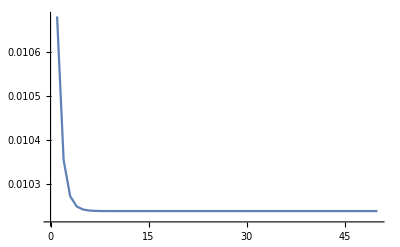

```mathematica
ListLinePlot[half["en"],PlotRange->Full]
```

```mathematica
ailist={{0,0},{-1,2},{-1,1},{-2,3}};
```

```mathematica
aM1={0,-1};
aM2={(√3)/2,-1/2};
```

```mathematica
aM={aM1,aM2}
```

{{0,-1},{(√3)/2,-1/2}}

```mathematica
inner=ailist.aM
```

{{0,0},{√3,0},{(√3)/2,1/2},{(3 √3)/2,1/2}}

```mathematica
halffig=Table[Graphics[{MapThread[{PointSize[#2/10],Point[#1]}&,{inner,half["spinsav"][[i,All,1]]}],MapThread[{Arrowheads[Norm[#2]/10],Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,half["spinsav"][[i,All,3;;4]]}]},AspectRatio->Automatic,Axes->True],{i,50}];
```

```mathematica
ListAnimate[halffig]
```

```mathematica
a1={-2,4}.aM;
```

```mathematica
a2={-2,2}.aM;
```

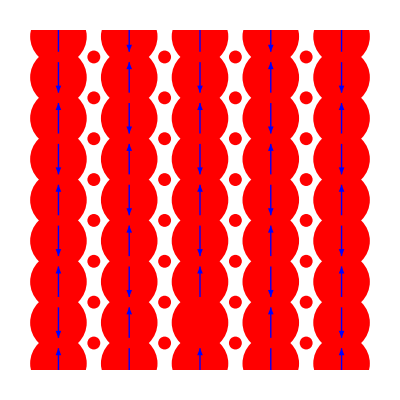

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,half["spinsav"][[-1,All,1]]}],Blue,MapThread[{(*Arrowheads[Norm[#2]/20],*)Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,half["spinsav"][[-1,All,3;;4]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,half["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,half["spinsav"][[-1,All,3;;4]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

-Graphics-

#### 1/3

```mathematica
third=importmat[NotebookDirectory[]<>"nu1,3_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{-2,1},{-4,2},{-1,1},{-2,2},{-3,2},{-3,1},{-2,0},{-1,0}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
third["spinsav"][[50]]
```

{{0.876143,0.866698,-0.00039516,0.0000545843},{0.876118,-0.43334,0.750556,0.0000598242},{0.876144,-0.433011,-0.750778,0.0000545229},{0.0619311,-0.00216562,-0.00376404,1.92421×10^-6},{0.0619352,-0.00216701,0.00375056,1.95068×10^-6},{0.0619312,0.00434239,-9.22846×10^-6,1.92451×10^-6},{0.0619312,0.00434239,-6.65448×10^-6,1.92452×10^-6},{0.0619353,-0.00216478,0.00375185,1.95068×10^-6},{0.0619311,-0.00216339,-0.00376532,1.9242×10^-6}}

```mathematica
thirdfig=Table[Graphics[{MapThread[{PointSize[#2/10],Point[#1]}&,{inner,third["spinsav"][[i,All,1]]}],MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,third["spinsav"][[i,All,2;;3]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-.5,2},{-.5,3.5}}],{i,50}];
```

```mathematica
ListAnimate[thirdfig]
```

```mathematica
a1={-3,0}.aM;
```

```mathematica
a2={-3,3}.aM;
```

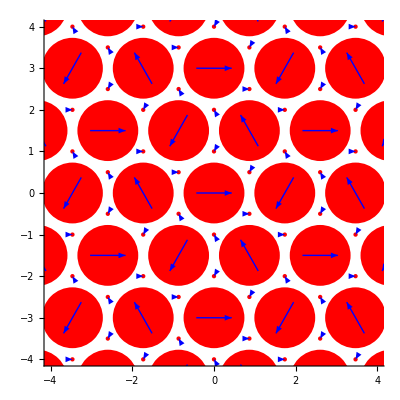

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,third["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,third["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

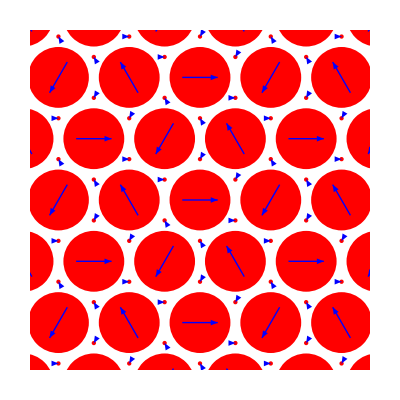

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,third["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,third["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

#### 2/3

```mathematica
twothird=importmat[NotebookDirectory[]<>"nu2,3_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{-2,2},{-1,1}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
twothird["spinsav"][[50]]
```

{{0.961737,0.,0.,0.900508},{0.961737,0.,0.,-0.900508},{0.0765263,0.,0.,1.75443×10^-16}}

```mathematica
twothirdfig=Table[Graphics[{MapThread[{PointSize[#2/10],Point[#1]}&,{inner,twothird["spinsav"][[i,All,1]]}],MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,twothird["spinsav"][[i,All,3;;4]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-.5,2},{-.5,2}}],{i,50}];
```

```mathematica
ListAnimate[twothirdfig]
```

```mathematica
a1={-1,2}.aM;
```

```mathematica
a2={-2,1}.aM;
```

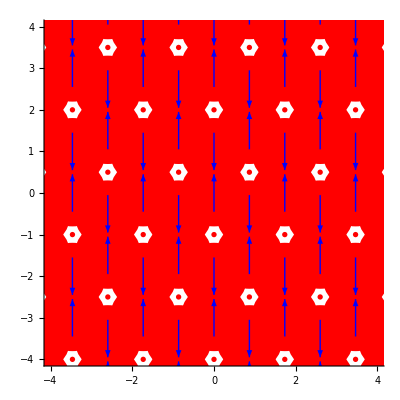

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,twothird["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,twothird["spinsav"][[-1,All,3;;4]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

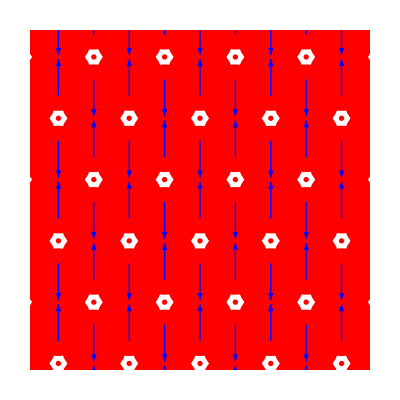

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,twothird["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,twothird["spinsav"][[-1,All,3;;4]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

#### 1/4

```mathematica
fourth=importmat[NotebookDirectory[]<>"nu1,4_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{-2,2},{-4,4},{-1,2},{-2,3},{-3,4},{-1,1},{-3,3},{-5,5},{-2,1},{-3,2},{-4,3}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
fourth["spinsav"][[50]]
```

{{0.595034,0.582628,9.09479×10^-6,-1.30387×10^-6},{0.595033,-0.291325,0.504562,-1.30371×10^-6},{0.595034,-0.291333,-0.504558,-1.40129×10^-6},{0.134983,-0.0545573,2.14727×10^-6,-1.70213×10^-7},{0.134992,0.0272799,0.0472493,-1.79461×10^-7},{0.134982,0.0272776,-0.0472414,-1.67593×10^-7},{0.134991,0.0272794,0.0472498,-1.54406×10^-7},{0.134992,-0.0545618,1.29712×10^-6,-2.65278×10^-7},{0.134994,0.02728,-0.0472483,-2.23887×10^-7},{0.134994,-0.0545632,8.35343×10^-7,-2.10025×10^-7},{0.13498,0.0272749,0.047241,-2.84272×10^-7},{0.134992,0.0272794,-0.0472469,-2.54083×10^-7}}

```mathematica
fourthfig=Table[Graphics[{Red,MapThread[{PointSize[#2/10],Point[#1]}&,{inner,fourth["spinsav"][[i,All,1]]}],Blue,MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,fourth["spinsav"][[i,All,2;;3]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-.5,5},{-.5,3.5}}],{i,50}];
```

```mathematica
ListAnimate[fourthfig]
```

```mathematica
a1={-2,4}.aM;
```

```mathematica
a2={-4,2}.aM;
```

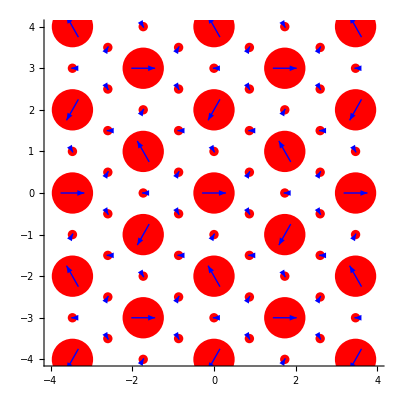

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,fourth["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,fourth["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

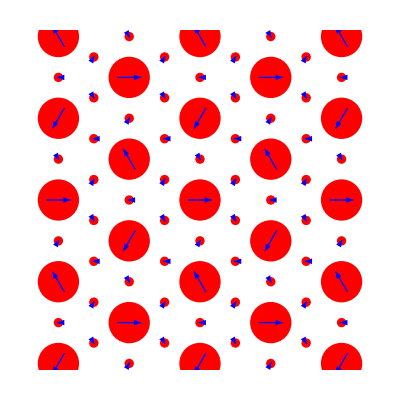

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,fourth["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,fourth["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

#### 3/4

```mathematica
threefourth=importmat[NotebookDirectory[]<>"nu3,4_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{0,1},{-1,1},{-1,2}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
threefourth["spinsav"][[50]]
```

{{0.943837,-0.886259,-4.63333×10^-14,-2.47237×10^-14},{0.943801,0.443045,-0.767541,-2.54168×10^-14},{0.943801,0.443045,0.767541,-2.58508×10^-14},{0.168562,9.04061×10^-6,-4.13935×10^-15,1.99813×10^-14}}

```mathematica
threefourthfig=Table[Graphics[{Red,MapThread[{PointSize[#2/10],Point[#1]}&,{inner,threefourth["spinsav"][[i,All,1]]}],Blue,MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,threefourth["spinsav"][[i,All,2;;3]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-1,2},{-1.5,1.5}}],{i,50}];
```

```mathematica
ListAnimate[threefourthfig]
```

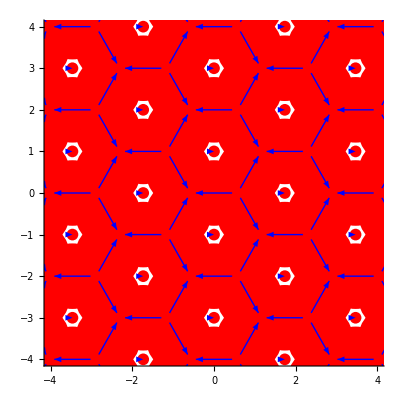

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*2*aM1+j*2*aM2]}&,{inner,threefourth["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*2aM1+j*2aM2,#1+#2/2+i*2*aM1+j*2*aM2}]}&,{inner,threefourth["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

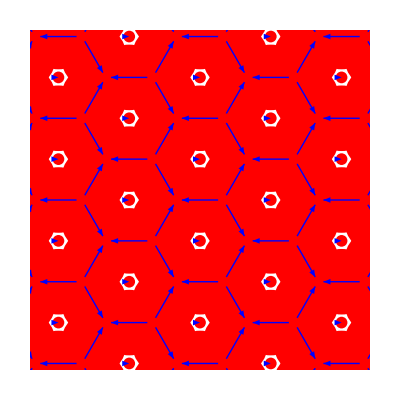

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*2*aM1+j*2*aM2]}&,{inner,threefourth["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*2aM1+j*2aM2,#1+#2/2+i*2*aM1+j*2*aM2}]}&,{inner,threefourth["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

#### 1/1

```mathematica
one=importmat[NotebookDirectory[]<>"nu1,1_t3_U1_hp1_ep10.mat"];
```

```mathematica
ailist={{0,0},{-1,1},{-2,2}};
```

```mathematica
inner=ailist.aM;
```

```mathematica
one["spinsav"][[50]]
```

{{1.,0.939912,8.92602×10^-6,1.43109×10^-7},{0.999998,-0.469964,0.81398,1.34756×10^-7},{1.,-0.469973,-0.813978,1.41786×10^-7}}

```mathematica
onefig=Table[Graphics[{Red,MapThread[{PointSize[#2/10],Point[#1]}&,{inner,one["spinsav"][[i,All,1]]}],Blue,MapThread[{(*Arrowheads[Norm[#2]/10],*)Arrow[{#1-#2/2,#1+#2/2}]}&,{inner,one["spinsav"][[i,All,2;;3]]}]},AspectRatio->Automatic,Axes->True,PlotRange->{{-1,2},{-1.5,1.5}}],{i,50}];
```

```mathematica
ListAnimate[onefig]
```

```mathematica
a1={-1,2}.aM;
```

```mathematica
a2={-2,1}.aM;
```

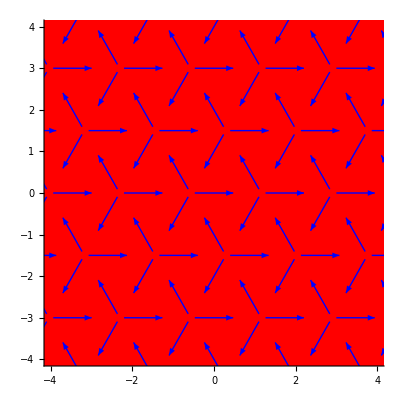

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,one["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,one["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,Axes->True,PlotRange->{{-4,4},{-4,4}}]
```

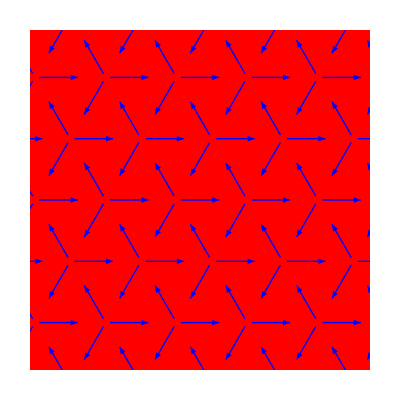

```mathematica
Graphics[Table[{Red,MapThread[{PointSize[#2/8],Point[#1+i*a1+j*a2]}&,{inner,one["spinsav"][[-1,All,1]]}],Blue,MapThread[{Arrowheads[Norm[#2]/20],Arrow[{#1-#2/2+i*a1+j*a2,#1+#2/2+i*a1+j*a2}]}&,{inner,one["spinsav"][[-1,All,2;;3]]}]},{i,-5,5},{j,-5,5}],AspectRatio->Automatic,PlotRange->{{-4,4},{-4,4}}]
```

## Classical energy

```mathematica
shell[n_]:=Block[{a1={0,-1},a2={(√3)/2,-1/2},nshell=n,distsquare,order,shellsorted,break,start,end,shelllist},shelllist=Flatten[Table[{{xindex,yindex},xindex*a1+yindex*a2},{xindex,-nshell,nshell},{yindex,Max[-nshell,-nshell-xindex],Min[nshell-xindex,nshell]}],1];distsquare=Dot[#,#]&/@shelllist[[All,2]];order=Ordering[distsquare];shellsorted=shelllist[[order,2]];break=Flatten[Position[Differences[distsquare[[order]]],_?(#≠0&)]];start=Prepend[break+1,1];end=Append[break,-1];MapThread[shellsorted[[#1;;#2]]&,{start,end}]]
```

```mathematica
nsquare[q_,Ri_,ni_]:=Block[{ν=1/Length[ni]},Abs[Total@MapThread[Exp[-I*q.#1]*#2&,{Ri,ni}]*ν]^2]
```

```mathematica
V[q_,nlist_,Ri_,ni_]:=Block[{n=Length[nlist],U},nsquare[q,Ri,ni]*Sum[Subscript[U,i]*Sum[Exp[I*q.n],{n,nlist[[i]]}],{i,n}]]
```

```mathematica
tot[q_,nlist_,Ri_,ni_]:=Simplify/@Collect[Total@V[q,Rest@nlist,Ri,ni]/2,Subscript[U,_]]
```

```mathematica
V2[q_,nlist_,Ri_,ni_,u_]:=Block[{n=Length[nlist],U},nsquare[q,Ri,ni]*Sum[u[[i]]*Sum[Exp[I*q.n],{n,nlist[[i]]}],{i,n}]]
```

```mathematica
tot2[q_,nlist_,Ri_,ni_,u_]:=Total@V2[q,Rest@nlist,Ri,ni,u]/2
```

```mathematica
neighborlist=shell[8];
```

### U

```mathematica
u=MapThread[#1->#2&,{(Subscript[U,#]&/@Range[22]),{0.1427,0.0719,0.0596,0.0414,0.0349,0.0285,0.0270,0.0233,0.0203,0.0190,0.0171,0.0153,.0149,.0140,.0127,.0117,.0113,.0106,.0092,.0091,.0086,.0078}}]
```

{U_1→0.1427,U_2→0.0719,U_3→0.0596,U_4→0.0414,U_5→0.0349,U_6→0.0285,U_7→0.027,U_8→0.0233,U_9→0.0203,U_10→0.019,U_11→0.0171,U_12→0.0153,U_13→0.0149,U_14→0.014,U_15→0.0127,U_16→0.0117,U_17→0.0113,U_18→0.0106,U_19→0.0092,U_20→0.0091,U_21→0.0086,U_22→0.0078}

```mathematica
u=MapThread[#1->#2&,{(Subscript[U,#]&/@Range[5]),{0.2199,0.0826,0.1238,0.0651,0.0825}}]
```

{U_1→0.2199,U_2→0.0826,U_3→0.1238,U_4→0.0651,U_5→0.0825}

```mathematica
pot[r_,d_]:=1/r-1/(√(r^2+d^2));
```

```mathematica
shell[3]//Column
```

{{0,0}}
{{0,1},{(√3)/2,1/2},{-(√3)/2,1/2},{(√3)/2,-1/2},{-(√3)/2,-1/2},{0,-1}}
{{(√3)/2,3/2},{-(√3)/2,3/2},{√3,0},{-√3,0},{(√3)/2,-3/2},{-(√3)/2,-3/2}}
{{0,2},{√3,1},{-√3,1},{√3,-1},{-√3,-1},{0,-2}}
{{(√3)/2,5/2},{√3,2},{-(√3)/2,5/2},{(3 √3)/2,1/2},{-√3,2},{(3 √3)/2,-1/2},{-(3 √3)/2,1/2},{√3,-2},{-(3 √3)/2,-1/2},{(√3)/2,-5/2},{-√3,-2},{-(√3)/2,-5/2}}
{{0,3},{(3 √3)/2,3/2},{-(3 √3)/2,3/2},{(3 √3)/2,-3/2},{-(3 √3)/2,-3/2},{0,-3}}

```mathematica
Table[pot@Norm[#]&/@r,{r,N[Rest@shell[2]]}]
```

{{0.900496,0.900496,0.900496,0.900496,0.900496,0.900496},{0.478817,0.478817,0.478817,0.478817,0.478817,0.478817},{0.401942,0.401942,0.401942,0.401942,0.401942,0.401942}}

```mathematica
neighbor=shell[100][[2;;-1,1]];
```

```mathematica
int=pot[Norm[N[#]],∞]&/@neighbor;
```

```mathematica
int[[-1]]
```

0.01

```mathematica
int=pot[Norm[N[#]],1000]&/@neighbor;
```

```mathematica
int[[-1]]
```

0.00900496

```mathematica
neighbor
```

{{0,1},{(√3)/2,3/2},{0,2},{(√3)/2,5/2},{0,3},{√3,3},{(√3)/2,7/2},{0,4},{√3,4},{(√3)/2,9/2},{0,5},{(3 √3)/2,9/2},{√3,5},{(√3)/2,11/2},{0,6},{(3 √3)/2,11/2},{√3,6},{(√3)/2,13/2},{2 √3,6},{(3 √3)/2,13/2},{√3,7},{(√3)/2,15/2},{2 √3,7},{(3 √3)/2,15/2},{0,8},{√3,8},{(√3)/2,17/2},{(5 √3)/2,15/2},{2 √3,8},{(3 √3)/2,17/2},{0,9},{√3,9},{(5 √3)/2,17/2},{2 √3,9},{(3 √3)/2,19/2},{0,10},{√3,10},{3 √3,9},{(5 √3)/2,19/2},{(√3)/2,21/2},1912,{(5 √3)/2,189/2},{(7 √3)/2,189/2},{(9 √3)/2,189/2},{(11 √3)/2,189/2},{0,95},{√3,95},{2 √3,95},{3 √3,95},{4 √3,95},{5 √3,95},{(√3)/2,191/2},{(3 √3)/2,191/2},{(5 √3)/2,191/2},{(7 √3)/2,191/2},{(9 √3)/2,191/2},{0,96},{√3,96},{2 √3,96},{3 √3,96},{4 √3,96},{(√3)/2,193/2},{(3 √3)/2,193/2},{(5 √3)/2,193/2},{(7 √3)/2,193/2},{0,97},{√3,97},{2 √3,97},{3 √3,97},{(√3)/2,195/2},{(3 √3)/2,195/2},{(5 √3)/2,195/2},{0,98},{√3,98},{2 √3,98},{(√3)/2,197/2},{(3 √3)/2,197/2},{0,99},{√3,99},{(√3)/2,199/2},{0,100}}
 |  |  |  |

```mathematica
u=MapThread[#1->#2&,{(Subscript[U,#]&/@Range[Length[int]]),int}]
```

{U_1→0.900496,U_2→0.478817,U_3→0.401942,U_4→0.281291,U_5→0.237551,U_6→0.194184,U_7→0.183278,U_8→0.157152,U_9→0.137746,U_10→0.127309,U_11→0.110557,U_12→0.103714,U_13→0.100594,U_14→0.0922349,U_15→0.0809174,U_16→0.0789632,U_17→0.0753093,U_18→0.0688744,U_19→0.0621381,U_20→0.060934,U_21→0.0575643,U_22→0.0526445,U_23→0.0492258,U_24→0.0476621,U_25→0.0469131,U_26→0.0447871,U_27→0.0410126,U_28→0.0398772,U_29→0.03933,U_30→0.0377653,U_31→0.0367817,U_32→0.035388,U_33→0.032471,U_34→0.0317136,U_35→0.0302876,U_36→0.0292893,U_37→0.0283467,U_38→0.0268875,U_39→0.0266112,U_40→0.026073,U_41→0.0258108,U_42→0.0245656,U_43→0.0236418,U_44→0.0229873,U_45→0.0223633,U_46→0.0219632,U_47→0.0211988,U_48→0.0201343,U_49→0.0193149,U_50→0.0188501,U_51→0.0186994,U_52→0.0182594,U_53→0.0175641,U_54→0.0174304,U_55→0.0166634,U_56→0.015952,U_57→0.0157262,U_58→0.0156154,U_59→0.0152906,U_60→0.0146744,U_61→0.0144783,U_62→0.0139158,U_63→0.0136482,U_64→0.013561,U_65→0.0133048,U_66→0.0130566,U_67→0.0128955,U_68→0.0123572,U_69→0.012138,U_70→0.0117188,U_71→0.0115845,U_72→0.0113235,U_73→0.0111966,U_74→0.0110109,U_75→0.0109501,U_76→0.0104835,U_77→0.0102626,U_78→0.0101551,U_79→0.0101021,U_80→0.00994566,U_81→0.0096939,U_82→0.00950011,U_83→0.009359,U_84→0.00895612,U_85→0.00882826,U_86→0.00874472,U_87→0.00858156,U_88→0.00850188,U_89→0.00834622,U_90→0.00812152,U_91→0.00804886,U_92→0.00801295,U_93→0.00773503,U_94→0.00770142,U_95→0.00760207,U_96→0.00750485,U_97→0.00744119,U_98→0.00731656,U_99→0.00722536,U_100→0.00699126,U_101→0.00696289,U_102→0.00690673,U_103→0.00679667,U_104→0.00674273,U_105→0.00666316,U_106→0.00663698,U_107→0.00648349,U_108→0.00633585,U_109→0.00628789,U_110→0.00605694,U_111→0.00601245,U_112→0.00599041,U_113→0.00592509,U_114→0.00581885,U_115→0.00579799,U_116→0.00567538,U_117→0.00563548,U_118→0.00551853,U_119→0.00549944,U_120→0.00533243,U_121→0.00529647,U_122→0.00527864,U_123→0.00522575,U_124→0.0051226,U_125→0.00507229,U_126→0.00499026,U_127→0.00492622,U_128→0.00483271,U_129→0.00475702,U_130→0.00474212,U_131→0.00469789,U_132→0.00465435,U_133→0.00462569,U_134→0.00458325,U_135→0.00452768,U_136→0.00445977,U_137→0.00440667,U_138→0.00432897,U_139→0.00426595,U_140→0.00425353,U_141→0.00422887,U_142→0.00418026,U_143→0.00410908,U_144→0.00407425,U_145→0.00403991,U_146→0.00401728,U_147→0.00393973,U_148→0.00390726,U_149→0.00382281,U_150→0.00381247,U_151→0.00378173,U_152→0.00376146,U_153→0.0037314,U_154→0.00366279,U_155→0.00364358,U_156→0.00360565,U_157→0.00357763,U_158→0.00349573,U_159→0.00347796,U_160→0.00344286,U_161→0.00342553,U_162→0.0033913,U_163→0.00336601,U_164→0.00334102,U_165→0.0032759,U_166→0.00324413,U_167→0.00320513,U_168→0.00319742,U_169→0.0031821,U_170→0.00311466,U_171→0.00310732,U_172→0.00308545,U_173→0.00304957,U_174→0.00302137,U_175→0.00300743,U_176→0.0030005,U_177→0.00297988,U_178→0.00293933,U_179→0.00289969,U_180→0.00286733,U_181→0.00286093,U_182→0.00284188,U_183→0.00282304,U_184→0.00281059,U_185→0.00278597,U_186→0.00274971,U_187→0.00270257,U_188→0.00269677,U_189→0.0026681,U_190→0.00264552,U_191→0.00260131,U_192→0.00257967,U_193→0.00256896,U_194→0.00256363,U_195→0.00254776,U_196→0.00252167,U_197→0.00250623,U_198→0.00250112,U_199→0.00248589,U_200→0.00244111,U_201→0.00242648,U_202→0.00239766,U_203→0.00238818,U_204→0.00234171,U_205→0.00233259,U_206→0.00232806,U_207→0.00231454,U_208→0.0023056,U_209→0.0022923,U_210→0.0022879,U_211→0.00226176,U_212→0.00225316,U_213→0.00221096,U_214→0.00219035,U_215→0.00218627,U_216→0.00216203,U_217→0.00214218,U_218→0.00213825,U_219→0.00212651,U_220→0.00211489,U_221→0.0021072,U_222→0.00208065,U_223→0.00206944,U_224→0.00204732,U_225→0.00203641,U_226→0.00200778,U_227→0.00198327,U_228→0.00197636,U_229→0.00196266,U_230→0.00195587,U_231→0.00194241,U_232→0.0019225,U_233→0.00191594,U_234→0.00191267,U_235→0.00189648,U_236→0.00188369,U_237→0.00187419,U_238→0.00186477,U_239→0.00185854,U_240→0.00184617,U_241→0.00182788,U_242→0.00180395,U_243→0.00180099,U_244→0.00179218,U_245→0.00178634,U_246→0.00177765,U_247→0.00177477,U_248→0.00175763,U_249→0.00174077,U_250→0.00173244,U_251→0.00171056,U_252→0.00170247,U_253→0.00169178,U_254→0.00167858,U_255→0.00166814,U_256→0.00166038,U_257→0.00165524,U_258→0.00164505,U_259→0.00163999,U_260→0.00162994,U_261→0.00161507,U_262→0.00161016,U_263→0.00158839,U_264→0.001586,U_265→0.00155779,U_266→0.00155086,U_267→0.00154399,U_268→0.00153265,U_269→0.0015304,U_270→0.00152592,U_271→0.00152368,U_272→0.00151259,U_273→0.00149729,U_274→0.0014908,U_275→0.00148651,U_276→0.00147798,U_277→0.00147375,U_278→0.00145495,U_279→0.00145289,U_280→0.00144877,U_281→0.00142849,U_282→0.0014225,U_283→0.00141655,U_284→0.00141261,U_285→0.00140477,U_286→0.00139895,U_287→0.00139316,U_288→0.00137792,U_289→0.00137041,U_290→0.00136667,U_291→0.00135926,U_292→0.00134827,U_293→0.00133742,U_294→0.00133205,U_295→0.00132672,U_296→0.00131267,U_297→0.00131093,U_298→0.00130573,U_299→0.00130229,U_300→0.00129715,U_301→0.00129545,U_302→0.0012853,U_303→0.00128195,U_304→0.00127032,U_305→0.00125725,U_306→0.00125563,U_307→0.00125241,U_308→0.001246,U_309→0.00123648,U_310→0.00123177,U_311→0.00122398,U_312→0.00121781,U_313→0.00121475,U_314→0.00120866,U_315→0.00119961,U_316→0.00119513,U_317→0.00119068,U_318→0.00118773,U_319→0.00118332,U_320→0.00117749,U_321→0.00117315,U_322→0.00115604,U_323→0.00114486,U_324→0.0011366,U_325→0.0011325,U_326→0.00113114,U_327→0.00112708,U_328→0.00112037,U_329→0.00111504,U_330→0.00111107,U_331→0.00109932,U_332→0.00109673,U_333→0.00109544,U_334→0.00109159,U_335→0.00108522,U_336→0.00108396,U_337→0.00106895,U_338→0.00106649,U_339→0.00106526,U_340→0.00105429,U_341→0.00105188,U_342→0.00105068,U_343→0.00104709,U_344→0.00103996,U_345→0.00103292,U_346→0.00103059,U_347→0.00101907,U_348→0.00101339,U_349→0.00101226,U_350→0.00101001,U_351→0.00100889,U_352→0.00100553,U_353→0.000999974,U_354→0.000990104,U_355→0.000985769,U_356→0.000983613,U_357→0.000982538,U_358→0.000979326,U_359→0.00097401,U_360→0.000972953,U_361→0.000966648,U_362→0.000961447,U_363→0.000957319,U_364→0.000954242,U_365→0.000946118,U_366→0.000936125,U_367→0.000934147,U_368→0.000933161,U_369→0.000924362,U_370→0.000918573,U_371→0.000916657,U_372→0.000912844,U_373→0.000910002,U_374→0.000907174,U_375→0.000902494,U_376→0.000899706,U_377→0.000894171,U_378→0.000890513,U_379→0.000885072,U_380→0.000883271,U_381→0.000879687,U_382→0.000867331,U_383→0.00086646,U_384→0.000863854,U_385→0.00085954,U_386→0.000858681,U_387→0.000856115,U_388→0.00085356,U_389→0.000851865,U_390→0.000846811,U_391→0.000845974,U_392→0.00084347,U_393→0.000838499,U_394→0.000833577,U_395→0.000829512,U_396→0.000828703,U_397→0.000826283,U_398→0.000822277,U_399→0.000819095,U_400→0.000807345,U_401→0.000805029,U_402→0.000803491,U_403→0.000801193,U_404→0.000800429,U_405→0.000795873,U_406→0.000794364,U_407→0.000789865,U_408→0.00078689,U_409→0.000783196,U_410→0.000782461,U_411→0.000780263,U_412→0.000773728,U_413→0.000769422,U_414→0.000767996,U_415→0.000765156,U_416→0.000763743,U_417→0.000760929,U_418→0.000755354,U_419→0.000754661,U_420→0.000752591,U_421→0.000749162,U_422→0.000748479,U_423→0.000746437,U_424→0.000744405,U_425→0.000740367,U_426→0.000738362,U_427→0.0007324,U_428→0.000731086,U_429→0.00072847,U_430→0.000727168,U_431→0.000722641,U_432→0.000719436,U_433→0.000715621,U_434→0.000714988,U_435→0.000713096,U_436→0.000709337,U_437→0.000708091,U_438→0.000705611,U_439→0.000702531,U_440→0.000701917,U_441→0.000698256,U_442→0.000697042,U_443→0.000694626,U_444→0.000692823,U_445→0.000691027,U_446→0.00068746,U_447→0.000683923,U_448→0.000682751,U_449→0.000678674,U_450→0.000675787,U_451→0.000670074,U_452→0.000667248,U_453→0.000666685,U_454→0.000665561,U_455→0.000665001,U_456→0.00066221,U_457→0.000659991,U_458→0.000658335,U_459→0.000656687,U_460→0.000653409,U_461→0.000651781,U_462→0.000650159,U_463→0.000647471,U_464→0.000645867,U_465→0.000641095,U_466→0.000640568,U_467→0.000637424,U_468→0.000634305,U_469→0.000633271,U_470→0.000632755,U_471→0.000628143,U_472→0.000627126,U_473→0.000625099,U_474→0.00062409,U_475→0.000622582,U_476→0.00062208,U_477→0.000618092,U_478→0.000616114,U_479→0.000614638,U_480→0.000613167,U_481→0.000609274,U_482→0.000607342,U_483→0.000604464,U_484→0.000603034,U_485→0.000600663,U_486→0.000598777,U_487→0.000595966,U_488→0.000593641,U_489→0.000593177,U_490→0.000592253,U_491→0.000591791,U_492→0.000590411,U_493→0.000588121,U_494→0.000584941,U_495→0.000584037,U_496→0.000582237,U_497→0.000581341,U_498→0.000580894,U_499→0.00057601,U_500→0.000570326,U_501→0.000568165,U_502→0.000566446,U_503→0.000565162,U_504→0.000563884,U_505→0.000560076,U_506→0.000558816,U_507→0.000557979,U_508→0.000556727,U_509→0.000556311,U_510→0.000553824,U_511→0.000550537,U_512→0.000548906,U_513→0.000546474,U_514→0.000545668,U_515→0.000545265,U_516→0.00054406,U_517→0.000541664,U_518→0.000540473,U_519→0.000539285,U_520→0.000536141,U_521→0.00053458,U_522→0.000532253,U_523→0.000531481,U_524→0.000529943,U_525→0.000529176,U_526→0.00052803,U_527→0.000527649,U_528→0.000526509,U_529→0.000524617,U_530→0.000523111,U_531→0.000521987,U_532→0.000519009,U_533→0.000518638,U_534→0.000515691,U_535→0.000514594,U_536→0.000512047,U_537→0.000511323,U_538→0.000509881,U_539→0.00050773,U_540→0.000505594,U_541→0.000504532,U_542→0.000501717,U_543→0.000499276,U_544→0.000498582,U_545→0.000497199,U_546→0.000496166,U_547→0.000495137,U_548→0.000492409,U_549→0.000492069,U_550→0.000491054,U_551→0.000490379,U_552→0.000489034,U_553→0.000487027,U_554→0.000485034,U_555→0.000481089,U_556→0.000480437,U_557→0.000480111,U_558→0.000478489,U_559→0.00047752,U_560→0.000475271,U_561→0.000474632,U_562→0.000472723,U_563→0.000472406,U_564→0.000471457,U_565→0.000469883,U_566→0.000469569,U_567→0.000468943,U_568→0.000467694,U_569→0.000465831,U_570→0.000464905,U_571→0.000463367,U_572→0.000462142,U_573→0.000461532,U_574→0.000461228,U_575→0.0004576,U_576→0.0004567,U_577→0.00045313,U_578→0.00045254,U_579→0.000451363,U_580→0.000449607,U_581→0.000448153,U_582→0.000447863,U_583→0.000447284,U_584→0.00044613,U_585→0.000444408,U_586→0.000443551,U_587→0.000442697,U_588→0.000442129,U_589→0.000440997,U_590→0.000439307,U_591→0.000437908,U_592→0.000437072,U_593→0.000436794,U_594→0.000435961,U_595→0.000434579,U_596→0.000434304,U_597→0.000432111,U_598→0.000430478,U_599→0.000427779,U_600→0.000426173,U_601→0.000424843,U_602→0.000424577,U_603→0.000423783,U_604→0.000422992,U_605→0.000422465,U_606→0.000420631,U_607→0.000419849,U_608→0.000418293,U_609→0.000417776,U_610→0.000416746,U_611→0.000415464,U_612→0.000415209,U_613→0.000412162,U_614→0.000411406,U_615→0.000409402,U_616→0.000409153,U_617→0.000408406,U_618→0.000406179,U_619→0.000405442,U_620→0.000404217,U_621→0.000403242,U_622→0.000402756,U_623→0.000401787,U_624→0.00040034,U_625→0.00039986,U_626→0.00039962,U_627→0.000398425,U_628→0.000396052,U_629→0.00039558,U_630→0.00039464,U_631→0.000393937,U_632→0.000393236,U_633→0.000391377,U_634→0.000389992,U_635→0.000389302,U_636→0.000388386,U_637→0.000387702,U_638→0.000386339,U_639→0.000385886,U_640→0.00038566,U_641→0.000383636,U_642→0.000383189,U_643→0.000382965,U_644→0.000382297,U_645→0.000381186,U_646→0.000379641,U_647→0.000379201,U_648→0.000377888,U_649→0.000377669,U_650→0.000377016,U_651→0.000375715,U_652→0.000375283,U_653→0.000373135,U_654→0.000372494,U_655→0.000371856,U_656→0.000371431,U_657→0.00036932,U_658→0.000368062,U_659→0.000366397,U_660→0.000365776,U_661→0.00036495,U_662→0.000364333,U_663→0.000363923,U_664→0.000363104,U_665→0.000362696,U_666→0.000361882,U_667→0.000360868,U_668→0.000360263,U_669→0.000358256,U_670→0.000357657,U_671→0.000357061,U_672→0.000356664,U_673→0.000355872,U_674→0.00035469,U_675→0.000353124,U_676→0.000352346,U_677→0.000351376,U_678→0.000351183,U_679→0.000350027,U_680→0.000348877,U_681→0.000348305,U_682→0.000346785,U_683→0.000346596,U_684→0.00034603,U_685→0.000345465,U_686→0.000345089,U_687→0.00034434,U_688→0.00034378,U_689→0.000343221,U_690→0.00034285,U_691→0.000342108,U_692→0.000341001,U_693→0.000340084,U_694→0.000338806,U_695→0.000337898,U_696→0.000337717,U_697→0.000337174,U_698→0.000336273,U_699→0.000335198,U_700→0.000335019,U_701→0.000334484,U_702→0.000333064,U_703→0.000332357,U_704→0.000332005,U_705→0.000330253,U_706→0.000329905,U_707→0.00032921,U_708→0.00032869,U_709→0.000328171,U_710→0.000327139,U_711→0.000326796,U_712→0.000326624,U_713→0.00032577,U_714→0.000325089,U_715→0.000323061,U_716→0.000322557,U_717→0.00032122,U_718→0.000320722,U_719→0.000320058,U_720→0.000319068,U_721→0.000318082,U_722→0.000317102,U_723→0.000315156,U_724→0.000314833,U_725→0.000314672,U_726→0.00031419,U_727→0.000313389,U_728→0.000312751,U_729→0.000312274,U_730→0.000311957,U_731→0.00031085,U_732→0.000309593,U_733→0.000309436,U_734→0.000309123,U_735→0.000308499,U_736→0.000308188,U_737→0.000307723,U_738→0.000307104,U_739→0.000305412,U_740→0.0003048,U_741→0.000303887,U_742→0.000303432,U_743→0.000302225,U_744→0.000301175,U_745→0.000300876,U_746→0.000300279,U_747→0.000299982,U_748→0.000299389,U_749→0.000298502,U_750→0.000298208,U_751→0.000297327,U_752→0.000296742,U_753→0.000296305,U_754→0.000295869,U_755→0.000294135,U_756→0.000293418,U_757→0.000293274,U_758→0.000292988,U_759→0.000292846,U_760→0.000292418,U_761→0.000292133,U_762→0.000291566,U_763→0.000289873,U_764→0.000289453,U_765→0.000288197,U_766→0.00028792,U_767→0.000287366,U_768→0.000286675,U_769→0.000286538,U_770→0.000286125,U_771→0.000285714,U_772→0.00028544,U_773→0.000284621,U_774→0.000284485,U_775→0.000283265,U_776→0.000282995,U_777→0.000282861,U_778→0.000281786,U_779→0.000281652,U_780→0.000280586,U_781→0.000280055,U_782→0.000278472,U_783→0.000278079,U_784→0.000277687,U_785→0.000277426,U_786→0.000276515,U_787→0.000275868,U_788→0.000275094,U_789→0.00027458,U_790→0.000273813,U_791→0.000273558,U_792→0.000273431,U_793→0.000273049,U_794→0.000272289,U_795→0.00027191,U_796→0.000271532,U_797→0.00027128,U_798→0.000270778,U_799→0.000270029,U_800→0.000269034,U_801→0.000268539,U_802→0.000267923,U_803→0.0002678,U_804→0.000266819,U_805→0.000266331,U_806→0.000264875,U_807→0.000264513,U_808→0.000263912,U_809→0.000263552,U_810→0.000263432,U_811→0.000262716,U_812→0.000262478,U_813→0.000261766,U_814→0.000261648,U_815→0.000261293,U_816→0.000260704,U_817→0.000260352,U_818→0.000259883,U_819→0.000258834,U_820→0.000258254,U_821→0.000257792,U_822→0.000257561,U_823→0.000257101,U_824→0.000256413,U_825→0.00025607,U_826→0.000255728,U_827→0.00025516,U_828→0.000255046,U_829→0.000254706,U_830→0.000254367,U_831→0.000253019,U_832→0.000252461,U_833→0.000252127,U_834→0.000251461,U_835→0.000251019,U_836→0.000250688,U_837→0.000250358,U_838→0.000250138,U_839→0.000249699,U_840→0.000249371,U_841→0.000249044,U_842→0.000248175,U_843→0.000248067,U_844→0.000247742,U_845→0.000247203,U_846→0.000247096,U_847→0.000245811,U_848→0.000245598,U_849→0.000245491,U_850→0.000244326,U_851→0.000243694,U_852→0.000243274,U_853→0.00024296,U_854→0.000242647,U_855→0.000242438,U_856→0.000240781,U_857→0.000240575,U_858→0.000240164,U_859→0.000239652,U_860→0.00023955,U_861→0.000239244,U_862→0.000238938,U_863→0.000238735,U_864→0.00023833,U_865→0.000238127,U_866→0.000238026,U_867→0.00023722,U_868→0.00023712,U_869→0.000236518,U_870→0.000236019,U_871→0.000235621,U_872→0.000235324,U_873→0.000235125,U_874→0.00023473,U_875→0.000234139,U_876→0.00023355,U_877→0.000233257,U_878→0.00023238,U_879→0.000231799,U_880→0.000231606,U_881→0.000230932,U_882→0.000230644,U_883→0.000229784,U_884→0.000229498,U_885→0.000229308,U_886→0.000228929,U_887→0.000228362,U_888→0.000227797,U_889→0.000227609,U_890→0.000226768,U_891→0.000226675,U_892→0.000226489,U_893→0.000226117,U_894→0.000225654,U_895→0.000225562,U_896→0.000224274,U_897→0.000224183,U_898→0.000223909,U_899→0.000223362,U_900→0.000223181,U_901→0.000222818,U_902→0.000222366,U_903→0.000221199,U_904→0.000220931,U_905→0.000220663,U_906→0.00022013,U_907→0.000219953,U_908→0.000219864,U_909→0.000219599,U_910→0.000219422,U_911→0.000219158,U_912→0.000218543,U_913→0.000218368,U_914→0.000218018,U_915→0.000217757,U_916→0.000217496,U_917→0.000217062,U_918→0.000216975,U_919→0.000216802,U_920→0.00021594,U_921→0.000215682,U_922→0.000215425,U_923→0.000214913,U_924→0.000214403,U_925→0.000213725,U_926→0.000213641,U_927→0.000213388,U_928→0.00021322,U_929→0.000212968,U_930→0.000212884,U_931→0.000211881,U_932→0.000211383,U_933→0.000210886,U_934→0.000210721,U_935→0.000210392,U_936→0.000210227,U_937→0.000209981,U_938→0.000209899,U_939→0.000209653,U_940→0.000209245,U_941→0.000208433,U_942→0.000207786,U_943→0.000207465,U_944→0.000206983,U_945→0.000206345,U_946→0.000205868,U_947→0.000205788,U_948→0.000205551,U_949→0.000205077,U_950→0.000204841,U_951→0.0002039,U_952→0.000203666,U_953→0.00020351,U_954→0.0002032,U_955→0.000202349,U_956→0.000202272,U_957→0.000202118,U_958→0.000202041,U_959→0.000201657,U_960→0.000201427,U_961→0.000201121,U_962→0.000200893,U_963→0.000200741,U_964→0.000200437,U_965→0.000199982,U_966→0.000199605,U_967→0.00019953,U_968→0.000199079,U_969→0.000198629,U_970→0.000198182,U_971→0.000197588,U_972→0.000197513,U_973→0.000196702,U_974→0.000196628,U_975→0.000196408,U_976→0.000196261,U_977→0.000196042,U_978→0.000195386,U_979→0.000194878,U_980→0.000194661,U_981→0.0001943,U_982→0.000194228,U_983→0.000194084,U_984→0.000193797,U_985→0.000193367,U_986→0.000192797,U_987→0.000192513,U_988→0.000192088,U_989→0.000191735,U_990→0.000191664,U_991→0.000191453,U_992→0.000191243,U_993→0.000190892,U_994→0.000190404,U_995→0.000190265,U_996→0.000189987,U_997→0.000189157,U_998→0.000188744,U_999→0.000188607,U_1000→0.000188128,U_1001→0.000187924,U_1002→0.000187515,U_1003→0.000187312,U_1004→0.000187109,U_1005→0.000186569,U_1006→0.000186502,U_1007→0.0001863,U_1008→0.000186166,U_1009→0.000185965,U_1010→0.000185497,U_1011→0.000185097,U_1012→0.000184898,U_1013→0.000184171,U_1014→0.000184105,U_1015→0.000183514,U_1016→0.000183318,U_1017→0.000183122,U_1018→0.000182991,U_1019→0.000182601,U_1020→0.000182341,U_1021→0.000181953,U_1022→0.000181824,U_1023→0.000181245,U_1024→0.000180669,U_1025→0.000180414,U_1026→0.000180223,U_1027→0.000180033,U_1028→0.000179716,U_1029→0.000179274,U_1030→0.000179148,U_1031→0.000178897,U_1032→0.000178709,U_1033→0.000178521,U_1034→0.000178146,U_1035→0.000178022,U_1036→0.000177773,U_1037→0.000177401,U_1038→0.000177277,U_1039→0.000177215,U_1040→0.000176661,U_1041→0.00017617,U_1042→0.000175925,U_1043→0.000175803,U_1044→0.000175742,U_1045→0.000175074,U_1046→0.000175014,U_1047→0.000174832,U_1048→0.00017447,U_1049→0.00017429,U_1050→0.00017411,U_1051→0.00017375,U_1052→0.000172679,U_1053→0.000172561,U_1054→0.000172384,U_1055→0.000172325,U_1056→0.000172148,U_1057→0.000171972,U_1058→0.000171854,U_1059→0.000171444,U_1060→0.000171269,U_1061→0.000170977,U_1062→0.000170919,U_1063→0.000170803,U_1064→0.000170571,U_1065→0.000170281,U_1066→0.00017005,U_1067→0.000169877,U_1068→0.000169762,U_1069→0.000169532,U_1070→0.000169417,U_1071→0.000168675,U_1072→0.000168391,U_1073→0.00016822,U_1074→0.000167712,U_1075→0.000167487,U_1076→0.00016715,U_1077→0.000166814,U_1078→0.000166702,U_1079→0.000166646,U_1080→0.000166146,U_1081→0.000165813,U_1082→0.000165703,U_1083→0.000165482,U_1084→0.000165152,U_1085→0.000164877,U_1086→0.000164713,U_1087→0.000164658,U_1088→0.000164222,U_1089→0.000164168,U_1090→0.000163842,U_1091→0.000163517,U_1092→0.000163409,U_1093→0.000163355,U_1094→0.000162871,U_1095→0.000162763,U_1096→0.000162549,U_1097→0.000162228,U_1098→0.000162069,U_1099→0.000161909,U_1100→0.00016159,U_1101→0.000161432,U_1102→0.000160957,U_1103→0.000160379,U_1104→0.000160327,U_1105→0.00015991,U_1106→0.000159702,U_1107→0.000159598,U_1108→0.000159546,U_1109→0.00015939,U_1110→0.000159132,U_1111→0.000158977,U_1112→0.000158771,U_1113→0.000158309,U_1114→0.000158155,U_1115→0.000158053,U_1116→0.000157849,U_1117→0.000157747,U_1118→0.000157544,U_1119→0.000157088,U_1120→0.000156836,U_1121→0.000156634,U_1122→0.000156483,U_1123→0.000156333,U_1124→0.000156233,U_1125→0.000155883,U_1126→0.000155733,U_1127→0.000155484,U_1128→0.000155335,U_1129→0.000155137,U_1130→0.00015489,U_1131→0.00015484,U_1132→0.000154545,U_1133→0.000154103,U_1134→0.000153664,U_1135→0.000153566,U_1136→0.000153518,U_1137→0.000153372,U_1138→0.000153081,U_1139→0.000152791,U_1140→0.000152694,U_1141→0.000152405,U_1142→0.000152213,U_1143→0.00015183,U_1144→0.00015164,U_1145→0.000151544,U_1146→0.000151354,U_1147→0.000151212,U_1148→0.000150975,U_1149→0.000150221,U_1150→0.00014994,U_1151→0.000149846,U_1152→0.000149706,U_1153→0.00014938,U_1154→0.000149287,U_1155→0.000148824,U_1156→0.000148594,U_1157→0.000148548,U_1158→0.000148456,U_1159→0.000148042,U_1160→0.000147997,U_1161→0.000147859,U_1162→0.000147631,U_1163→0.000147449,U_1164→0.000147313,U_1165→0.000147177,U_1166→0.000146905,U_1167→0.000146815,U_1168→0.000146634,U_1169→0.000146409,U_1170→0.000146364,U_1171→0.000145827,U_1172→0.000145693,U_1173→0.000145293,U_1174→0.000145204,U_1175→0.000145159,U_1176→0.000145027,U_1177→0.000144938,U_1178→0.000144409,U_1179→0.000144146,U_1180→0.000143971,U_1181→0.000143579,U_1182→0.000143448,U_1183→0.000143231,U_1184→0.000143188,U_1185→0.000143058,U_1186→0.00014267,U_1187→0.000142584,U_1188→0.000142541,U_1189→0.000142412,U_1190→0.000142155,U_1191→0.000141813,U_1192→0.000141685,U_1193→0.000141515,U_1194→0.000141388,U_1195→0.000141303,U_1196→0.000141134,U_1197→0.00014088,U_1198→0.000140628,U_1199→0.000140544,U_1200→0.000140376,U_1201→0.000140292,U_1202→0.000139875,U_1203→0.000139791,U_1204→0.000139625,U_1205→0.000139501,U_1206→0.000139376,U_1207→0.000139169,U_1208→0.000139046,U_1209→0.000139004,U_1210→0.000138881,U_1211→0.000138388,U_1212→0.000138306,U_1213→0.000138061,U_1214→0.000137655,U_1215→0.000137574,U_1216→0.000137533,U_1217→0.000137412,U_1218→0.00013721,U_1219→0.00013717,U_1220→0.000137049,U_1221→0.000136928,U_1222→0.000136848,U_1223→0.000136567,U_1224→0.000136207,U_1225→0.000136128,U_1226→0.000135731,U_1227→0.000135612,U_1228→0.000135414,U_1229→0.000135257,U_1230→0.000135178,U_1231→0.000135021,U_1232→0.000134785,U_1233→0.000134668,U_1234→0.000134551,U_1235→0.000134356,U_1236→0.000134083,U_1237→0.000133773,U_1238→0.000133619,U_1239→0.000133388,U_1240→0.000132927,U_1241→0.000132812,U_1242→0.000132698,U_1243→0.000132622,U_1244→0.000132469,U_1245→0.000132241,U_1246→0.000132052,U_1247→0.000131938,U_1248→0.000131901,U_1249→0.000131712,U_1250→0.000131599,U_1251→0.000131561,U_1252→0.000131449,U_1253→0.000131336,U_1254→0.000131111,U_1255→0.000131036,U_1256→0.000130999,U_1257→0.000130589,U_1258→0.000130441,U_1259→0.000130256,U_1260→0.000130219,U_1261→0.000129997,U_1262→0.000129923,U_1263→0.000129336,U_1264→0.000129263,U_1265→0.000129117,U_1266→0.000128935,U_1267→0.000128681,U_1268→0.000128609,U_1269→0.000128464,U_1270→0.000128355,U_1271→0.000128067,U_1272→0.000128031,U_1273→0.000127923,U_1274→0.000127816,U_1275→0.000127744,U_1276→0.000127494,U_1277→0.000127173,U_1278→0.00012696,U_1279→0.000126783,U_1280→0.000126748,U_1281→0.000126677,U_1282→0.000126642,U_1283→0.000126325,U_1284→0.000126114,U_1285→0.000126044,U_1286→0.0001258,U_1287→0.000125417,U_1288→0.000125208,U_1289→0.000125105,U_1290→0.00012507,U_1291→0.000124863,U_1292→0.000124553,U_1293→0.000124177,U_1294→0.000124142,U_1295→0.00012404,U_1296→0.000123972,U_1297→0.000123836,U_1298→0.000123632,U_1299→0.000123564,U_1300→0.000123429,U_1301→0.000123361,U_1302→0.000123226,U_1303→0.000123058,U_1304→0.000123024,U_1305→0.000122957,U_1306→0.000122823,U_1307→0.000122622,U_1308→0.000122221,U_1309→0.000122155,U_1310→0.000121823,U_1311→0.000121757,U_1312→0.000121724,U_1313→0.000121625,U_1314→0.00012146,U_1315→0.000121328,U_1316→0.00012123,U_1317→0.000121164,U_1318→0.000120837,U_1319→0.000120642,U_1320→0.000120382,U_1321→0.000120252,U_1322→0.000120155,U_1323→0.000120058,U_1324→0.000119993,U_1325→0.000119415,U_1326→0.000119383,U_1327→0.000119287,U_1328→0.000119127,U_1329→0.000119096,U_1330→0.000118905,U_1331→0.000118714,U_1332→0.000118651,U_1333→0.000118619,U_1334→0.000118524,U_1335→0.000118335,U_1336→0.000118272,U_1337→0.00011824,U_1338→0.000118146,U_1339→0.000117864,U_1340→0.000117707,U_1341→0.000117395,U_1342→0.00011724,U_1343→0.000117147,U_1344→0.000117023,U_1345→0.000116961,U_1346→0.000116869,U_1347→0.000116838,U_1348→0.000116591,U_1349→0.000116468,U_1350→0.000116284,U_1351→0.000116132,U_1352→0.000116101,U_1353→0.000115918,U_1354→0.000115644,U_1355→0.000115493,U_1356→0.000115372,U_1357→0.000115311,U_1358→0.000115191,U_1359→0.00011501,U_1360→0.00011495,U_1361→0.00011492,U_1362→0.00011477,U_1363→0.00011468,U_1364→0.00011465,U_1365→0.000114471,U_1366→0.000114203,U_1367→0.000114114,U_1368→0.000113936,U_1369→0.0001137,U_1370→0.000113582,U_1371→0.000113406,U_1372→0.00011323,U_1373→0.000112879,U_1374→0.000112705,U_1375→0.000112559,U_1376→0.000112443,U_1377→0.000112357,U_1378→0.000112126,U_1379→0.000112097,U_1380→0.000112011,U_1381→0.000111781,U_1382→0.000111666,U_1383→0.000111523,U_1384→0.000111495,U_1385→0.000111409,U_1386→0.000111267,U_1387→0.000111153,U_1388→0.000111068,U_1389→0.000110983,U_1390→0.000110813,U_1391→0.000110728,U_1392→0.000110644,U_1393→0.000110503,U_1394→0.000110306,U_1395→0.00011025,U_1396→0.000110138,U_1397→0.000110083,U_1398→0.000109832,U_1399→0.000109804,U_1400→0.000109748,U_1401→0.00010972,U_1402→0.000109471,U_1403→0.000109388,U_1404→0.000109305,U_1405→0.000109249,U_1406→0.000108727,U_1407→0.000108591,U_1408→0.000108481,U_1409→0.000108318,U_1410→0.000108264,U_1411→0.000108155,U_1412→0.000108074,U_1413→0.00010783,U_1414→0.000107776,U_1415→0.000107668,U_1416→0.000107614,U_1417→0.000107534,U_1418→0.000107507,U_1419→0.000107426,U_1420→0.000107292,U_1421→0.000107105,U_1422→0.000107025,U_1423→0.000106865,U_1424→0.000106812,U_1425→0.000106706,U_1426→0.000106573,U_1427→0.000106336,U_1428→0.000106151,U_1429→0.000106072,U_1430→0.000105915,U_1431→0.000105758,U_1432→0.000105706,U_1433→0.000105601,U_1434→0.000105445,U_1435→0.000105393,U_1436→0.000105289,U_1437→0.000105134,U_1438→0.000104927,U_1439→0.000104772,U_1440→0.000104592,U_1441→0.000104515,U_1442→0.000104464,U_1443→0.000104362,U_1444→0.000104311,U_1445→0.000104285,U_1446→0.000104209,U_1447→0.000104081,U_1448→0.000104005,U_1449→0.000103903,U_1450→0.000103777,U_1451→0.000103751,U_1452→0.000103675,U_1453→0.000103398,U_1454→0.000103147,U_1455→0.000103096,U_1456→0.000103071,U_1457→0.000102871,U_1458→0.000102846,U_1459→0.000102697,U_1460→0.000102399,U_1461→0.000102275,U_1462→0.000102201,U_1463→0.000102102,U_1464→0.000101955,U_1465→0.000101881,U_1466→0.000101807,U_1467→0.00010166,U_1468→0.000101611,U_1469→0.000101392,U_1470→0.000101294,U_1471→0.000101221,U_1472→0.000101003,U_1473→0.00010093,U_1474→0.000100882,U_1475→0.000100785,U_1476→0.000100737,U_1477→0.000100641,U_1478→0.000100497,U_1479→0.000100449,U_1480→0.000100209,U_1481→0.000100138,U_1482→0.000100066,U_1483→0.000100018,U_1484→0.0000999232,U_1485→0.0000995911,U_1486→0.0000995675,U_1487→0.0000994966,U_1488→0.0000993787,U_1489→0.0000993551,U_1490→0.0000992139,U_1491→0.0000990731,U_1492→0.0000990028,U_1493→0.0000988158,U_1494→0.0000987924,U_1495→0.0000984434,U_1496→0.0000983276,U_1497→0.0000981888,U_1498→0.0000980965,U_1499→0.0000979583,U_1500→0.0000979123,U_1501→0.0000978204,U_1502→0.0000977058,U_1503→0.0000976829,U_1504→0.0000976142,U_1505→0.0000975,U_1506→0.0000974087,U_1507→0.0000973404,U_1508→0.0000972721,U_1509→0.0000971359,U_1510→0.0000969999,U_1511→0.0000969547,U_1512→0.0000968868,U_1513→0.0000967966,U_1514→0.0000966839,U_1515→0.0000965939,U_1516→0.000096549,U_1517→0.0000965265,U_1518→0.0000964592,U_1519→0.0000962801,U_1520→0.0000962578,U_1521→0.000096057,U_1522→0.0000959236,U_1523→0.0000958792,U_1524→0.0000957904,U_1525→0.000095724,U_1526→0.000095481,U_1527→0.0000954589,U_1528→0.0000953928,U_1529→0.000094998,U_1530→0.000094867,U_1531→0.0000947363,U_1532→0.0000946928,U_1533→0.0000946711,U_1534→0.0000946059,U_1535→0.0000945625,U_1536→0.0000944974,U_1537→0.0000944758,U_1538→0.000094346,U_1539→0.0000941733,U_1540→0.0000941518,U_1541→0.0000939798,U_1542→0.0000939583,U_1543→0.0000937014,U_1544→0.0000935307,U_1545→0.0000934456,U_1546→0.000093403,U_1547→0.0000933818,U_1548→0.0000933181,U_1549→0.0000931909,U_1550→0.000093064,U_1551→0.0000930218,U_1552→0.0000929585,U_1553→0.0000928111,U_1554→0.0000927691,U_1555→0.0000926851,U_1556→0.0000924548,U_1557→0.0000923922,U_1558→0.0000923713,U_1559→0.0000922671,U_1560→0.0000921215,U_1561→0.0000920593,U_1562→0.0000920178,U_1563→0.0000918109,U_1564→0.0000916459,U_1565→0.0000916253,U_1566→0.0000915636,U_1567→0.0000914609,U_1568→0.0000914404,U_1569→0.0000913175,U_1570→0.0000911948,U_1571→0.000091154,U_1572→0.0000911336,U_1573→0.0000909503,U_1574→0.0000909097,U_1575→0.0000907879,U_1576→0.0000907271,U_1577→0.0000907069,U_1578→0.0000906462,U_1579→0.0000905856,U_1580→0.0000903438,U_1581→0.0000902233,U_1582→0.0000901632,U_1583→0.0000901031,U_1584→0.0000900031,U_1585→0.0000899831,U_1586→0.0000898236,U_1587→0.0000896844,U_1588→0.0000896249,U_1589→0.000089506,U_1590→0.0000894466,U_1591→0.0000892099,U_1592→0.0000891509,U_1593→0.0000891115,U_1594→0.0000889938,U_1595→0.0000889154,U_1596→0.0000887981,U_1597→0.000088759,U_1598→0.0000887395,U_1599→0.000088681,U_1600→0.0000885642,U_1601→0.0000884088,U_1602→0.0000883313,U_1603→0.0000882733,U_1604→0.0000882153,U_1605→0.0000881187,U_1606→0.0000880609,U_1607→0.0000879839,U_1608→0.0000879455,U_1609→0.0000877536,U_1610→0.0000877153,U_1611→0.0000876388,U_1612→0.0000875815,U_1613→0.00008741,U_1614→0.0000873719,U_1615→0.0000872011,U_1616→0.0000870686,U_1617→0.0000870308,U_1618→0.0000869176,U_1619→0.0000868422,U_1620→0.0000867294,U_1621→0.0000866919,U_1622→0.0000866168,U_1623→0.0000865045,U_1624→0.0000864484,U_1625→0.0000863551,U_1626→0.0000862806,U_1627→0.000086169,U_1628→0.0000860762,U_1629→0.0000860576,U_1630→0.000086002,U_1631→0.0000859095,U_1632→0.0000858541,U_1633→0.0000858356,U_1634→0.0000857803,U_1635→0.0000856882,U_1636→0.0000856146,U_1637→0.0000854128,U_1638→0.0000853945,U_1639→0.0000853579,U_1640→0.0000851753,U_1641→0.0000851207,U_1642→0.0000850661,U_1643→0.0000849571,U_1644→0.0000849208,U_1645→0.0000849027,U_1646→0.0000848484,U_1647→0.0000846856,U_1648→0.0000846315,U_1649→0.0000845955,U_1650→0.0000845235,U_1651→0.000084308,U_1652→0.0000842543,U_1653→0.0000840578,U_1654→0.00008404,U_1655→0.0000839866,U_1656→0.0000838799,U_1657→0.0000838266,U_1658→0.0000837734,U_1659→0.0000837379,U_1660→0.0000834729,U_1661→0.0000834553,U_1662→0.0000834201,U_1663→0.0000833497,U_1664→0.0000832619,U_1665→0.0000832444,U_1666→0.0000831392,U_1667→0.0000831042,U_1668→0.0000830343,U_1669→0.0000829994,U_1670→0.0000829296,U_1671→0.0000827209,U_1672→0.0000826342,U_1673→0.0000825649,U_1674→0.0000825131,U_1675→0.0000824785,U_1676→0.0000822029,U_1677→0.0000821686,U_1678→0.0000821514,U_1679→0.0000820657,U_1680→0.0000819972,U_1681→0.0000818947,U_1682→0.0000818606,U_1683→0.0000817413,U_1684→0.0000816903,U_1685→0.0000816054,U_1686→0.0000815545,U_1687→0.0000815376,U_1688→0.0000813853,U_1689→0.000081183,U_1690→0.0000809815,U_1691→0.000080948,U_1692→0.0000809313,U_1693→0.0000808811,U_1694→0.0000807976,U_1695→0.0000807809,U_1696→0.0000806809,U_1697→0.0000805811,U_1698→0.0000805313,U_1699→0.0000804815,U_1700→0.0000803987,U_1701→0.0000803822,U_1702→0.0000803491,U_1703→0.000080283,U_1704→0.0000802005,U_1705→0.0000801346,U_1706→0.0000798883,U_1707→0.0000797901,U_1708→0.0000797574,U_1709→0.0000796107,U_1710→0.0000793995,U_1711→0.000079367,U_1712→0.0000793508,U_1713→0.0000793023,U_1714→0.0000792053,U_1715→0.000079173,U_1716→0.0000791569,U_1717→0.0000790763,U_1718→0.000079012,U_1719→0.0000789638,U_1720→0.0000788835,U_1721→0.0000788194,U_1722→0.0000785957,U_1723→0.000078532,U_1724→0.0000785002,U_1725→0.0000784525,U_1726→0.0000784366,U_1727→0.0000783414,U_1728→0.0000782464,U_1729→0.0000782148,U_1730→0.0000781989,U_1731→0.0000780569,U_1732→0.0000778682,U_1733→0.0000778212,U_1734→0.0000777741,U_1735→0.0000777428,U_1736→0.000077649,U_1737→0.0000776334,U_1738→0.0000775866,U_1739→0.0000774931,U_1740→0.000077462,U_1741→0.0000773998,U_1742→0.0000773222,U_1743→0.0000771828,U_1744→0.000077121,U_1745→0.0000770746,U_1746→0.0000768438,U_1747→0.0000768131,U_1748→0.0000767059,U_1749→0.00007666,U_1750→0.0000765683,U_1751→0.0000765378,U_1752→0.0000764769,U_1753→0.0000764008,U_1754→0.0000763856,U_1755→0.00007634,U_1756→0.0000762187,U_1757→0.0000762035,U_1758→0.0000761582,U_1759→0.0000761128,U_1760→0.0000760826,U_1761→0.000075977,U_1762→0.0000759319,U_1763→0.0000758417,U_1764→0.0000758116,U_1765→0.0000757217,U_1766→0.0000756768,U_1767→0.0000756618,U_1768→0.0000755721,U_1769→0.0000754826,U_1770→0.0000753042,U_1771→0.0000752745,U_1772→0.0000752597,U_1773→0.0000751856,U_1774→0.0000751412,U_1775→0.0000751264,U_1776→0.0000750083,U_1777→0.0000749052,U_1778→0.0000748611,U_1779→0.0000747877,U_1780→0.000074729,U_1781→0.0000746851,U_1782→0.0000745974,U_1783→0.0000744806,U_1784→0.0000744224,U_1785→0.0000743933,U_1786→0.0000741612,U_1787→0.0000741323,U_1788→0.0000740889,U_1789→0.0000739879,U_1790→0.0000739015,U_1791→0.0000738153,U_1792→0.0000737293,U_1793→0.0000736434,U_1794→0.0000736148,U_1795→0.0000734721,U_1796→0.0000733867,U_1797→0.0000733441,U_1798→0.0000733015,U_1799→0.0000731881,U_1800→0.0000730609,U_1801→0.0000730468,U_1802→0.0000729341,U_1803→0.0000728498,U_1804→0.0000728357,U_1805→0.0000726676,U_1806→0.0000726256,U_1807→0.0000725419,U_1808→0.0000725001,U_1809→0.0000724583,U_1810→0.0000724304,U_1811→0.0000722916,U_1812→0.0000721808,U_1813→0.0000721255,U_1814→0.0000720427,U_1815→0.0000720014,U_1816→0.0000717268,U_1817→0.0000717131,U_1818→0.0000716311,U_1819→0.0000715629,U_1820→0.0000715493,U_1821→0.0000715084,U_1822→0.0000714404,U_1823→0.0000713589,U_1824→0.0000711964,U_1825→0.0000711828,U_1826→0.0000711153,U_1827→0.0000710614,U_1828→0.0000709537,U_1829→0.0000709,U_1830→0.0000708196,U_1831→0.0000706591,U_1832→0.0000706324,U_1833→0.0000705391,U_1834→0.0000704992,U_1835→0.0000702605,U_1836→0.0000702341,U_1837→0.0000702209,U_1838→0.0000701813,U_1839→0.0000701153,U_1840→0.0000701022,U_1841→0.0000700627,U_1842→0.0000699969,U_1843→0.000069905,U_1844→0.0000698657,U_1845→0.0000697611,U_1846→0.0000696306,U_1847→0.0000694357,U_1848→0.0000693968,U_1849→0.0000692804,U_1850→0.0000692159,U_1851→0.0000690871,U_1852→0.0000690101,U_1853→0.0000688563,U_1854→0.000068665,U_1855→0.0000686269,U_1856→0.0000686014,U_1857→0.0000685507,U_1858→0.0000683607,U_1859→0.0000683229,U_1860→0.0000682598,U_1861→0.0000679585,U_1862→0.000067946,U_1863→0.000067921,U_1864→0.000067871,U_1865→0.0000678087,U_1866→0.0000677962,U_1867→0.000067647,U_1868→0.0000676222,U_1869→0.0000674983,U_1870→0.0000673625,U_1871→0.000067178,U_1872→0.0000671658,U_1873→0.0000670311,U_1874→0.0000670189,U_1875→0.0000669822,U_1876→0.0000668359,U_1877→0.000066763,U_1878→0.0000666297,U_1879→0.0000666176,U_1880→0.0000664726,U_1881→0.0000664004,U_1882→0.0000663763,U_1883→0.0000661604,U_1884→0.0000661126,U_1885→0.0000657558,U_1886→0.0000657203,U_1887→0.0000656258,U_1888→0.000065614,U_1889→0.0000654374,U_1890→0.0000653319,U_1891→0.0000651916,U_1892→0.0000650518,U_1893→0.0000650285,U_1894→0.0000648777,U_1895→0.000064843,U_1896→0.0000646814,U_1897→0.0000646123,U_1898→0.0000644975,U_1899→0.0000644746,U_1900→0.0000643716,U_1901→0.0000642917,U_1902→0.0000642689,U_1903→0.000064053,U_1904→0.0000639964,U_1905→0.0000636808,U_1906→0.0000636584,U_1907→0.0000636471,U_1908→0.0000636135,U_1909→0.0000635464,U_1910→0.0000635128,U_1911→0.0000633456,U_1912→0.0000632567,U_1913→0.0000631127,U_1914→0.0000629802,U_1915→0.0000628153,U_1916→0.0000627933,U_1917→0.0000626183,U_1918→0.0000625529,U_1919→0.000062455,U_1920→0.0000624224,U_1921→0.0000622707,U_1922→0.0000622275,U_1923→0.0000620336,U_1924→0.0000619692,U_1925→0.0000616488,U_1926→0.0000616276,U_1927→0.0000615957,U_1928→0.0000615532,U_1929→0.0000615003,U_1930→0.0000613417,U_1931→0.000061268,U_1932→0.000061121,U_1933→0.000060839,U_1934→0.0000608286,U_1935→0.000060642,U_1936→0.0000605799,U_1937→0.0000604974,U_1938→0.0000604562,U_1939→0.0000602714,U_1940→0.0000600978,U_1941→0.0000600265,U_1942→0.0000597227,U_1943→0.0000596924,U_1944→0.0000596622,U_1945→0.0000595717,U_1946→0.0000594214,U_1947→0.0000593614,U_1948→0.000059212,U_1949→0.0000589446,U_1950→0.0000587478,U_1951→0.0000586889,U_1952→0.0000586204,U_1953→0.0000585716,U_1954→0.0000583963,U_1955→0.0000581639,U_1956→0.0000578756,U_1957→0.0000578373,U_1958→0.0000578087,U_1959→0.0000577228,U_1960→0.0000575802,U_1961→0.0000573815,U_1962→0.0000571277,U_1963→0.0000569316,U_1964→0.0000568757,U_1965→0.0000567643,U_1966→0.000056598,U_1967→0.0000563774,U_1968→0.0000560582,U_1969→0.000056031,U_1970→0.0000559495,U_1971→0.0000558141,U_1972→0.0000556254,U_1973→0.0000551893,U_1974→0.0000551363,U_1975→0.0000550306,U_1976→0.0000548726,U_1977→0.0000543513,U_1978→0.0000543254,U_1979→0.000054248,U_1980→0.0000541194,U_1981→0.0000535174,U_1982→0.000053467,U_1983→0.0000533666,U_1984→0.0000527128,U_1985→0.0000526883,U_1986→0.0000526147,U_1987→0.0000519122,U_1988→0.0000518644,U_1989→0.0000511395,U_1990→0.0000511162,U_1991→0.0000503706,U_1992→0.0000496281}

```mathematica
int//Length
```

1992

```mathematica
energy[d_,numshell_]:=Block[{hexen,recten,neighborlist=shell[numshell],neighbor,int,pot},pot[r_]=1/r-1/(√(r^2+d^2))(*Exp[-r/d]/r*);neighbor=neighborlist[[2;;-1,1]];int=pot@Norm[N[#]]&/@neighbor;(tot2[Qhex,neighborlist,Rlisthex,occupiedlisthex,int]-tot2[Qrect,neighborlist,Rlistrect,occupiedlistrect,int])]
```

```mathematica
findshell[d_]:=Block[{init=energy[d,2*d],first,last,middle,middleenergy,other,otherenergy},If[init<0,first=2*d;last=2*first;While[energy[d,last]<0,first=last;last=2*last],last=d;first=IntegerPart[d/2];While[energy[d,first]>0,last=first;first=IntegerPart[first/2]]];While[first<last-1,middle=Ceiling[(first+last)/2];middleenergy=energy[d,middle];If[middleenergy>0,last=middle,first=middle]];If[first==middle,other=last,other=first];otherenergy=energy[d,other];If[Abs[middleenergy]>Abs[otherenergy],other,middle]]
```

```mathematica
findshell[10]
```

20

```mathematica
findshell[40]
```

82

```mathematica
intercept=findshell/@{5,10,20,30,40,50,60,70,80,90,100,150,200};
```

```mathematica
intercept2=findshell/@{};
```

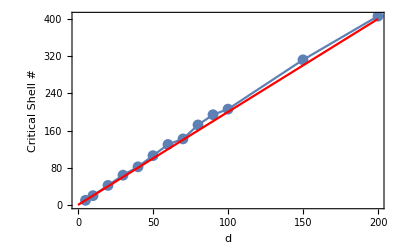

```mathematica
ListLinePlot[Transpose@{{5,10,20,30,40,50,60,70,80,90,100,150,200},intercept},Mesh->All,Epilog->{ First@Plot[2*x,{x,0,200},PlotStyle->Red]},FrameLabel->{"d","Critical Shell #"},Frame->True]
```

```mathematica
energy[5,3]
```

0.0393729+0. ⅈ

```mathematica
Re[energy[∞,100]]
```

-0.0828498

```mathematica
Dynamic[ii]
```

```mathematica
Clear[envsnumshell]
```

```mathematica
envsnumshell=ParallelTable[Re[energy[d,ii]],{d,{1,2,3,4,5,10}},{ii,10,100,10}];
```

```mathematica
envsnumshell//Dimensions
```

{6,10}

```mathematica
envsnumshell2=ParallelTable[Re[energy[∞,ii]],{ii,1000,1100,10}];
```

```mathematica
envsnumshell3=ParallelTable[Re[energy[∞,ii]],{ii,1,10}];
```

```mathematica
envsnumshell=ParallelTable[Re[energy[d,ii]],{d,{40,50,60,70,80,90,100}},{ii,10,200,10}];
```

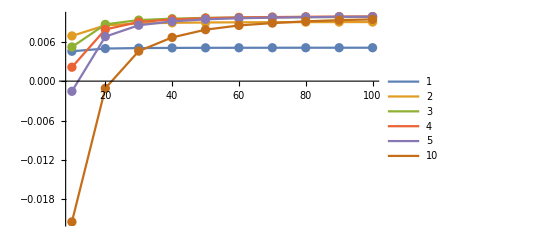

```mathematica
ListLinePlot[envsnumshell,DataRange->{10,100},Mesh->All,PlotLegends->{1,2,3,4,5,10},PlotRange->Full]
```

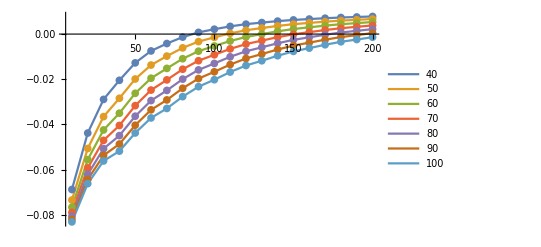

```mathematica
ListLinePlot[envsnumshell,DataRange->{10,200},Mesh->All,PlotLegends->{40,50,60,70,80,90,100},PlotRange->Full]
```

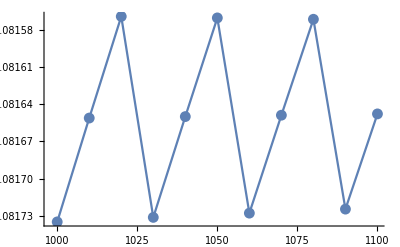

```mathematica
ListLinePlot[envsnumshell2,DataRange->{1000,1100}(*,PlotRange->{-0.09,0}*),Mesh->All]
```

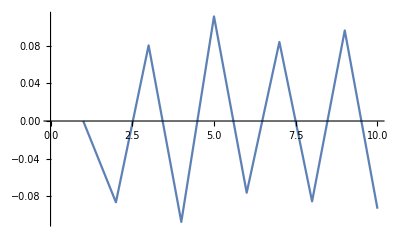

```mathematica
ListLinePlot[envsnumshell3,DataRange->{1,10}(*,PlotRange->{-0.09,0}*)]
```

```mathematica
envsnumshell3=ParallelTable[Re[energy[d,ii]],{d,{1000,1100}},{ii,1000,2000,200}];
```

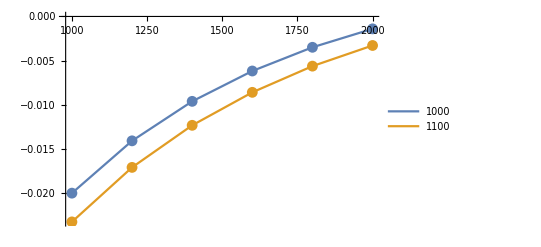

```mathematica
ListLinePlot[envsnumshell3,DataRange->{1000,2000},Mesh->All,PlotLegends->{1000,1100},PlotRange->Full]
```

### 1/2-rectangular

```mathematica
Qrect={{0,0},{0,2π}};
```

```mathematica
Rlistrect={{0,0},{(√3)/2,-1/2}};
```

```mathematica
occupiedlistrect={1,0};
```

```mathematica
neighborlist=shell[5];
```

```mathematica
nsquare[Qrect,Rlistrect,occupiedlistrect]
```

{1/4,1/4}

```mathematica
qnormrect=DeleteCases[Norm/@Qrect,0]
```

{2 π}

```mathematica
nrect=Delete[nsquare[Qrect,Rlistrect,occupiedlistrect],1]
```

{1/4}

```mathematica
rect=tot[Qrect,neighborlist,Rlistrect,occupiedlistrect]
```

U_1/2+U_2/2+(3 U_3)/2+U_4+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2

```mathematica
recten=(rect/.u[[1;;#]]&)/@Range[5]
```

{0.10995+U_2/2+(3 U_3)/2+U_4+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2,0.15125+(3 U_3)/2+U_4+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2,0.33695+U_4+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2,0.40205+U_5/2+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2,0.4433+(3 U_6)/2+U_7+(3 U_8)/2+U_9+U_10+U_11/2}

### 1/2-hexagonal

```mathematica
Rlisthex={{0,0},{-1,0},{0,-1},{1,-1},{1,0},{0,1},{-1,1},{1,1},{0,2},{-1,2},{-2,2},{-2,1}}.{{0,-1},{(√3)/2,-1/2}};
```

```mathematica
Qhex={{-2/3,-1/3},{-1/3,-1/6},{0,0},{1/3,1/6},{2/3,1/3},{1,1/2},{-1/2,0},{-1/6,1/6},{1/6,1/3},{1/2,1/2},{5/6,2/3},{7/6,5/6}}.{{-1/(√3),-1},{2/(√3),0}}*2π;
```

```mathematica
occupiedlisthex={0,1,1,1,1,1,1,0,0,0,0,0};
```

```mathematica
neighborlist=shell[5];
```

```mathematica
nsquare[Qhex,Rlisthex,occupiedlisthex]
```

{1/16,1/144,1/4,1/144,1/16,1/36,1/36,1/144,1/144,1/36,1/144,1/144}

```mathematica
nhex=Delete[nsquare[Qhex,Rlisthex,occupiedlisthex],3]
```

{1/16,1/144,1/144,1/16,1/36,1/36,1/144,1/144,1/36,1/144,1/144}

```mathematica
qnormhex=DeleteCases[Norm/@Qhex,0]
```

{(4 π)/3,(2 π)/3,(2 π)/3,(4 π)/3,2 π,(2 π)/(√3),(2 π)/3,(2 π)/3,(2 π)/(√3),(2 √7 π)/3,(2 √13 π)/3}

```mathematica
hex=tot[Qhex,neighborlist,Rlisthex,occupiedlisthex]
```

U_1/2+U_2+(3 U_3)/4+U_4+U_5+(3 U_6)/2+U_7+(3 U_8)/4+U_9+2 U_10+U_11/2

```mathematica
hexen=(hex/.u[[1;;#]]&)/@Range[11]
```

Part::take: Cannot take positions 1 through 1 in u.

ReplaceAll::reps: {u⟦1;;1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 1 through 2 in u.

ReplaceAll::reps: {u⟦1;;2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 1 through 3 in u.

General::stop: Further output of Part::take will be suppressed during this calculation.

ReplaceAll::reps: {u⟦1;;3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{U_1/2+U_2+(3 U_3)/4+U_4+U_5+(3 U_6)/2+U_7+(3 U_8)/4+U_9+2 U_10+U_11/2+U_12+(3 U_13)/2+U_14+(3 U_15)/2+U_16+2 U_17+U_18+(3 U_19)/2+(3 U_20)/2+(3 U_21)/2+2 U_22+U_23+2 U_24+(3 U_25)/4+U_26+U_27+U_28+(3 U_29)/2+U_30+U_31+3 U_32+2 U_33+2 U_34+U_35+(3 U_36)/4+U_37+(3 U_38)/2+U_39+2 U_40+(3 U_41)/2+2 U_42+U_43/2+(3 U_44)/2+U_45+2 U_46+2 U_47+U_48+(3 U_49)/2+3 U_50+(3 U_51)/2+U_52+3 U_53+U_54+U_55+1882+U_1938+U_1939+3 U_1940+U_1941+U_1942+(3 U_1943)/4+U_1944+(3 U_1945)/2+U_1946+U_1947+(3 U_1948)/2+U_1949+2 U_1950+2 U_1951+(3 U_1952)/2+2 U_1953+2 U_1954+2 U_1955+2 U_1956+U_1957/2+(3 U_1958)/2+U_1959+(3 U_1960)/2+U_1961+(3 U_1962)/2+U_1963+U_1964+U_1965+U_1966+U_1967+(3 U_1968)/2+2 U_1969+3 U_1970+2 U_1971+3 U_1972+U_1973+U_1974+U_1975+U_1976+U_1977/2+(3 U_1978)/2+U_1979+(3 U_1980)/2+2 U_1981+2 U_1982+2 U_1983+(3 U_1984)/4+U_1985+(3 U_1986)/2+U_1987+U_1988+U_1989+3 U_1990+U_1991+(3 U_1992)/4/.u⟦1;;1⟧,9,1}
 |  |  |  |

```mathematica
ListLinePlot[{#/.Subscript[U,_]->0&/@hexen,#/.Subscript[U,_]->0&/@recten},Frame->True,PlotLegends->{"Hexagon","Rectangle"}]
```

ReplaceAll::reps: {u⟦1;;1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {u⟦1;;2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {u⟦1;;3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
hex-rect/.u
```

ReplaceAll::reps: {u} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

U_2/2-(3 U_3)/4+U_5/2-(3 U_8)/4+U_10+U_12/2-(3 U_13)/2+U_17-(3 U_21)/2+U_22+U_24-(3 U_25)/4+U_28/2-(3 U_29)/2+U_31/2+U_34-(3 U_36)/4+U_40-(3 U_41)/2+U_42-(3 U_44)/2+U_46+(3 U_50)/2-(3 U_51)/2+U_57-(3 U_58)/2+U_61+U_62-(9 U_65)/4+U_67-(3 U_68)/2+U_71+U_73/2+U_76+U_78/2-(3 U_79)/2-(3 U_82)/4-(3 U_84)/2+2 U_86+U_88+U_91-(3 U_92)/2-(3 U_95)/2+U_97-(3 U_99)/2+U_102+U_104+U_109+U_111/2-3 U_112+U_117+U_118-(3 U_119)/2+2 U_121-(3 U_122)/4-(3 U_125)/2+U_126-(3 U_131)/2+(3 U_133)/2-(3 U_135)/2+U_136+U_141-(3 U_144)/4+U_146-(3 U_147)/2+(3 U_149)/2-(3 U_150)/2+U_152+U_155-3 U_157+U_159+U_161-(3 U_163)/2+U_165+U_169-(3 U_172)/2+U_173+U_175-(3 U_176)/2-(3 U_182)/2+U_184+2 U_187-(3 U_188)/2+U_189+U_191+U_193/2-(9 U_194)/4+U_197-(3 U_198)/2-(3 U_200)/2+U_203+U_205-(3 U_206)/2+U_208/2+2 U_212-(3 U_219)/2+2 U_221-(9 U_222)/4-(3 U_225)/2+U_228+2 U_230+U_233-(3 U_234)/2+U_235-(3 U_237)/2+U_239+U_242/2-3 U_243+U_245-(3 U_250)/2+2 U_252-(3 U_255)/2+U_257+U_259+U_262-(3 U_266)/2+U_270-(3 U_271)/2+U_272-3 U_273+U_275+U_277+U_280-(3 U_282)/4+2 U_284-3 U_286+U_288+U_290-(3 U_294)/2+(3 U_296)/2-(3 U_297)/2+U_299/2+U_303-(3 U_304)/2+U_307-(3 U_310)/2+U_311+U_313-(3 U_316)/4+U_318-(3 U_320)/2+U_323+2 U_324-3 U_327+2 U_328-(3 U_330)/2+U_332-(3 U_333)/2+U_338-(3 U_339)/2+U_341-(3 U_342)/2+2 U_346+U_350-(3 U_351)/2+U_354+(3 U_356)/2-(3 U_357)/2-(3 U_363)/2+U_365+U_367-3 U_368+U_371-(3 U_373)/2+2 U_376+U_377+U_380+2 U_382-(9 U_383)/4-3 U_387+U_389+U_390-(3 U_391)/2-(3 U_397)/2+U_398-(3 U_400)/2+(3 U_402)/2+2 U_406+U_407-(3 U_411)/2+U_414+U_416+U_418/2-(3 U_419)/2-(3 U_423)/4-3 U_426+U_428+U_430-(3 U_431)/2+U_432+U_433-(3 U_434)/2+2 U_437+2 U_442-(3 U_444)/2+U_448-3 U_449+U_450+U_454-(3 U_455)/2+U_456-(3 U_458)/2-(3 U_461)/2+2 U_464+U_469-(3 U_470)/2+U_472+U_474+U_477-(3 U_479)/2+U_481-(3 U_484)/2+U_485+U_490/2-3 U_491+U_495+U_497-(3 U_498)/2+3 U_499-3 U_500+U_501-(3 U_503)/4-(3 U_505)/2+2 U_507+U_511+U_514-(3 U_515)/2-(3 U_518)/2+U_520+U_523+U_525/2-(3 U_528)/2+2 U_529-3 U_531+U_534+U_537-(3 U_541)/2+2 U_544-(3 U_546)/4+U_548-3 U_549+U_551+2 U_556-(3 U_557)/2+U_558+U_561+U_562/2-(3 U_563)/2+U_567-3 U_570+U_571+2 U_573-(3 U_574)/2-3 U_575+U_578+U_583-(3 U_586)/2+2 U_588+U_592-(3 U_593)/2+U_597+2 U_598-3 U_603+U_605-(3 U_606)/2+2 U_609-(3 U_614)/2-(3 U_617)/2-(3 U_619)/2+U_620+U_622+2 U_625-(3 U_626)/2+2 U_627+U_629-(3 U_631)/2+U_633+U_634-(3 U_636)/4+U_639-(3 U_640)/2+U_642/2-(3 U_643)/2+U_647+U_648-(9 U_649)/2+U_652-(3 U_654)/2+U_656+U_659/2-(3 U_661)/2+2 U_663+U_665+U_668-(3 U_670)/2+U_672+2 U_675-(3 U_681)/2-(9 U_684)/4+2 U_686-3 U_688+U_690-(3 U_697)/2+U_698+U_699-(3 U_700)/2+U_702+U_704+3 U_706-(3 U_708)/2+U_711-3 U_712+U_713-(3 U_716)/2+2 U_718+(3 U_724)/2-3 U_725-(3 U_728)/2+U_730-(3 U_731)/2+2 U_734+U_736-(3 U_738)/2+U_739-(3 U_742)/2+U_745+U_747+U_750+U_751-(3 U_753)/2+U_758-(3 U_759)/2+U_761-3 U_764+U_766-(3 U_770)/2+2 U_772+2 U_773-(3 U_774)/2+U_776-(3 U_777)/2+U_780-(9 U_783)/4+U_785-(3 U_786)/2+U_787+U_788+2 U_791-3 U_792-(3 U_795)/2+U_797+U_800+U_804-(3 U_807)/2+(3 U_808)/2+U_812+U_813/2-3 U_814+U_817-(3 U_819)/2+2 U_820+U_822-(3 U_825)/2-(3 U_829)/2+U_833+U_834-(3 U_836)/4+U_838-(3 U_840)/2+U_842-(3 U_843)/2+U_848-(3 U_849)/2+2 U_850+U_851-(3 U_853)/2+2 U_855+U_857-3 U_861+2 U_863+U_865-3 U_866-(3 U_871)/2+U_873-(3 U_877)/2+3 U_880-3 U_881-(3 U_883)/2+U_885+2 U_889+U_892+2 U_896-(3 U_897)/2+U_900-(3 U_904)/2+(3 U_907)/2-(3 U_908)/2+U_910+U_913-(3 U_915)/2+U_919-(9 U_921)/2+U_925-(3 U_926)/2+U_928+2 U_934+U_936-3 U_939+2 U_940+2 U_942+U_945+2 U_946-(9 U_947)/4-(3 U_950)/2-(3 U_951)/2+U_953+U_957-3 U_958+U_959-(3 U_961)/2+U_963+U_971-3 U_972+U_973-(3 U_974)/2+(3 U_976)/2+U_978-(3 U_979)/2+2 U_983+2 U_986-(3 U_991)/2+2 U_995+U_999-(3 U_1000)/2-(3 U_1003)/4+(3 U_1005)/2-3 U_1006+U_1008-(3 U_1012)/2+U_1013-3 U_1014-(3 U_1016)/2+2 U_1018+U_1019+2 U_1022+U_1024-(3 U_1026)/2+2 U_1030-3 U_1032+U_1035+2 U_1038-(3 U_1039)/2+U_1041+U_1043-(3 U_1044)/2+U_1045-(3 U_1046)/2-(3 U_1049)/2+2 U_1053-(3 U_1056)/2+U_1058-(3 U_1059)/2+U_1063-(3 U_1066)/2+U_1068+U_1070-3 U_1071+U_1072+U_1074+2 U_1078-(3 U_1079)/2+U_1082+U_1086-(3 U_1087)/2+U_1092-(3 U_1093)/2+2 U_1095-(3 U_1098)/2-(3 U_1101)/2+3 U_1105+(3 U_1107)/2-3 U_1108+U_1111-3 U_1113+U_1115+2 U_1117-(3 U_1119)/2+U_1120-(3 U_1122)/4+U_1124-3 U_1125+U_1128-(3 U_1133)/2+2 U_1135-(3 U_1136)/2+U_1140+U_1141+U_1143+U_1145-(9 U_1147)/2+U_1148+U_1151/2+2 U_1154+U_1158-(3 U_1161)/2+2 U_1162-3 U_1164+U_1167-(3 U_1172)/2+U_1174-(3 U_1175)/2+U_1177+U_1178+U_1179-(9 U_1181)/4-(3 U_1185)/2+U_1187-(3 U_1188)/2+U_1191-(3 U_1193)/2+2 U_1195+U_1199+2 U_1201+U_1203-(3 U_1205)/2+U_1208-(3 U_1209)/2+U_1212+2 U_1213+U_1215/2-3 U_1216-(3 U_1220)/2+2 U_1222-3 U_1223+U_1225-3 U_1227+U_1228+U_1230-(3 U_1233)/2+U_1237-(3 U_1241)/2+U_1243+4 U_1247-(3 U_1248)/2+U_1249-(3 U_1252)/2+U_1255-(3 U_1256)/2+U_1257+U_1262+U_1264+U_1268-(3 U_1270)/2-(3 U_1273)/2+2 U_1275-(3 U_1276)/2+U_1281-3 U_1282+U_1285-3 U_1286+U_1287+U_1288-(3 U_1292)/2+U_1293-3 U_1294+U_1296+2 U_1299+U_1301+3 U_1305+U_1309+U_1311-(9 U_1312)/4-3 U_1315+U_1317+U_1320-(3 U_1322)/2+2 U_1324+(3 U_1325)/2-3 U_1326+U_1332-3 U_1333+U_1336-(3 U_1337)/2-(3 U_1339)/2+U_1340+U_1343+U_1345/2+U_1348-3 U_1354+2 U_1355+U_1357+2 U_1360-(3 U_1361)/2+U_1362-(3 U_1366)/2+3 U_1369-(9 U_1376)/4+U_1378-(3 U_1379)/2+U_1381-(3 U_1385)/2+2 U_1386-3 U_1388-(3 U_1391)/2+U_1395+2 U_1397+2 U_1400-(3 U_1401)/2-(3 U_1403)/2+2 U_1405-3 U_1406+U_1407+U_1410-(3 U_1412)/2+2 U_1414+U_1416-(3 U_1419)/2+U_1420-(3 U_1421)/2+U_1424+U_1427-3 U_1428+U_1432+U_1435+U_1438+U_1439-(3 U_1440)/2+U_1442+U_1444/2-(9 U_1445)/2+U_1448-(3 U_1452)/2+2 U_1453+2 U_1455-(3 U_1456)/2+U_1462-(3 U_1465)/2+U_1468-(3 U_1470)/2-(3 U_1472)/2+2 U_1474+U_1476+2 U_1479-3 U_1481+U_1483+U_1485-(3 U_1486)/2-(3 U_1492)/2-(3 U_1495)/2+3 U_1496+2 U_1497+U_1500-(3 U_1504)/2+2 U_1505-3 U_1507+U_1511-(3 U_1513)/2+U_1514+U_1516-(3 U_1517)/4+U_1519-3 U_1520+U_1523-(3 U_1525)/2+2 U_1526-3 U_1527+U_1532-(3 U_1533)/2+2 U_1535+U_1539-(3 U_1540)/2+U_1544+U_1546-(3 U_1547)/2+U_1551/2+2 U_1554+2 U_1557-(3 U_1558)/2+U_1559-3 U_1560+U_1562+U_1564/2-(3 U_1565)/2+U_1571-(3 U_1572)/2+U_1574+2 U_1575-(3 U_1578)/2-(3 U_1582)/2+U_1586-(3 U_1587)/4-(3 U_1590)/2-3 U_1591+U_1593+U_1594+2 U_1597-(3 U_1598)/2+2 U_1601-(3 U_1603)/2+U_1606+U_1608+2 U_1610-3 U_1612+U_1614+U_1617+2 U_1618+U_1621-(3 U_1624)/2+U_1625-6 U_1630+U_1631-(3 U_1634)/2+U_1635+2 U_1639-(3 U_1641)/2+U_1644-(3 U_1645)/2-(3 U_1647)/2+2 U_1649-(3 U_1652)/2+U_1653-(3 U_1654)/2-(3 U_1657)/2+U_1659+2 U_1662+2 U_1667+U_1669-(3 U_1673)/2+U_1675+U_1677-(3 U_1678)/2+2 U_1679+U_1682-(3 U_1683)/2+U_1686-(3 U_1687)/2+(5 U_1691)/2-(3 U_1692)/2-3 U_1698+2 U_1702-(9 U_1705)/2+U_1708+U_1711-(3 U_1712)/2+U_1715-(3 U_1716)/2+U_1717-(3 U_1719)/2+2 U_1720+2 U_1722+2 U_1724+2 U_1729-3 U_1730-(9 U_1733)/4+U_1735+U_1736-(3 U_1737)/2+U_1740+2 U_1743-(3 U_1745)/2+U_1747-(3 U_1748)/2+U_1751-(3 U_1755)/2-3 U_1758+U_1760-(3 U_1761)/2+2 U_1764+U_1765+U_1771-3 U_1772+U_1773/2+3 U_1776-3 U_1777-(3 U_1780)/2+U_1783+U_1785+U_1787+U_1794-3 U_1797+U_1799+U_1802+U_1803-(3 U_1804)/2-(3 U_1805)/4-3 U_1808+U_1810+U_1812-(3 U_1815)/2-(3 U_1821)/2+U_1822+U_1823+U_1824-(3 U_1825)/2+U_1826+2 U_1828+U_1832-(3 U_1833)/2+U_1836-(3 U_1837)/2-(3 U_1841)/2+U_1842-(3 U_1843)/2+U_1845-(3 U_1847)/2-(3 U_1849)/2+2 U_1850-(3 U_1854)/2+U_1856-(3 U_1858)/2+2 U_1863+U_1868+U_1871-(3 U_1872)/2+U_1873-(3 U_1874)/2+U_1882+U_1883-3 U_1886-(3 U_1889)/2+U_1893-(3 U_1894)/2+U_1896+U_1897+U_1899+U_1902-(3 U_1903)/2+U_1904+U_1906-(3 U_1907)/4-(3 U_1910)/2+U_1912-(3 U_1913)/2-(3 U_1914)/2+U_1916-(3 U_1919)/2+U_1921+U_1926/2-(3 U_1928)/2+U_1929+U_1932+U_1937-(3 U_1943)/4-(3 U_1945)/2-(3 U_1948)/2+U_1950+U_1951-(3 U_1952)/2+U_1953+U_1954+U_1955+U_1956-(3 U_1958)/2-(3 U_1960)/2-(3 U_1962)/2+U_1969+U_1971-(3 U_1978)/2-(3 U_1980)/2+U_1981+U_1982+U_1983-(3 U_1984)/4-(3 U_1986)/2+U_1989/2-(3 U_1992)/4/.u

```mathematica
ListLinePlot[{#/.Subscript[U,_]->0&/@hexen,#/.Subscript[U,_]->0&/@recten},Frame->True,PlotLegends->{"Hexagon","Rectangle"}]
```

ReplaceAll::reps: {u⟦1;;1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {u⟦1;;2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {u⟦1;;3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

### 2/3

```mathematica
Q={{0,0},{0,4 π/3},{0,-4 π/3}}
```

{{0,0},{0,(4 π)/3},{0,-(4 π)/3}}

```mathematica
Rlist={{0,0},{-1,1},{-2,2}}.{{0,-1},{(√3)/2,-1/2}};
```

```mathematica
occupiedlist={1,0,1};
```

```mathematica
neighborlist=shell[5];
```

```mathematica
nsquare[Q,Rlist,occupiedlist]^(1/2)//Total
```

4/3

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

U_1+2 U_2+U_3+2 U_4+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11

```mathematica
(en/.u[[1;;#]]&)/@Range[5]
```

{0.2199+2 U_2+U_3+2 U_4+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11,0.3851+U_3+2 U_4+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11,0.5089+2 U_4+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11,0.6391+2 U_5+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11,0.8041+2 U_6+2 U_7+U_8+2 U_9+4 U_10+U_11}

### 1/3

```mathematica
occupiedlist={1,0,0};
```

```mathematica
nsquare[Q,Rlist,occupiedlist]^(1/2)//Total
```

1

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

U_2+U_5+U_6+2 U_10+U_12+U_15+2 U_17+U_19+2 U_22

```mathematica
en/.u
```

0.2487

```mathematica
(en/.u[[1;;#]]&)/@Range[]
```

{U_2+U_5+U_6+2 U_10+U_12+U_15+2 U_17+U_19+2 U_22,0.0719+U_5+U_6+2 U_10+U_12+U_15+2 U_17+U_19+2 U_22,0.0719+U_5+U_6+2 U_10+U_12+U_15+2 U_17+U_19+2 U_22,0.0719+U_5+U_6+2 U_10+U_12+U_15+2 U_17+U_19+2 U_22,0.1068+U_6+2 U_10+U_12+U_15+2 U_17+U_19+2 U_22}

### 1/1

```mathematica
Q={{0,0}};
```

```mathematica
Rlist={{0,0}};
```

```mathematica
occupiedlist={1};
```

```mathematica
nsquare[Q,Rlist,occupiedlist]^(1/2)//Total
```

1

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

3 U_1+3 U_2+3 U_3+6 U_4+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11

```mathematica
(en/.u[[1;;#]]&)/@Range[5]
```

{0.6597+3 U_2+3 U_3+6 U_4+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11,0.9075+3 U_3+6 U_4+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11,1.2789+6 U_4+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11,1.6695+3 U_5+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11,1.917+3 U_6+6 U_7+3 U_8+6 U_9+6 U_10+3 U_11}

### 1/4

```mathematica
Q={{0,0},{1/2,0},{0,1/2},{1/2,1/2}}.{{-1/(√3),-1},{2/(√3),0}}*2π
```

{{0,0},{-π/(√3),-π},{(2 π)/(√3),0},{π/(√3),-π}}

```mathematica
Rlist={{0,0},{0,1},{-1,1},{-1,2}}.{{0,-1},{(√3)/2,-1/2}};
```

```mathematica
occupiedlist={1,0,0,0};
```

```mathematica
neighborlist=shell[6];
```

```mathematica
nsquare[Q,Rlist,occupiedlist]^(1/2)//Total
```

1

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

(3 U_3)/4+(3 U_6)/4+(3 U_8)/4+(3 U_13)/2+(3 U_15)/4

```mathematica
(en/.u[[1;;#]]&)/@Range[5]
```

{(3 U_3)/4+(3 U_6)/4+(3 U_8)/4+(3 U_13)/2+(3 U_15)/4,(3 U_3)/4+(3 U_6)/4+(3 U_8)/4+(3 U_13)/2+(3 U_15)/4,0.09285+(3 U_6)/4+(3 U_8)/4+(3 U_13)/2+(3 U_15)/4,0.09285+(3 U_6)/4+(3 U_8)/4+(3 U_13)/2+(3 U_15)/4,0.09285+(3 U_6)/4+(3 U_8)/4+(3 U_13)/2+(3 U_15)/4}

### 3/4

```mathematica
occupiedlist={1,1,1,0};
```

```mathematica
nsquare[Q,Rlist,occupiedlist]^(1/2)//Total
```

3/2

```mathematica
en=tot[Q,neighborlist,Rlist,occupiedlist]
```

(3 U_1)/2+(3 U_2)/2+(9 U_3)/4+3 U_4+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2+(3 U_12)/2+(9 U_13)/2+3 U_14+(9 U_15)/4

```mathematica
(en/.u[[1;;#]]&)/@Range[5]
```

{0.32985+(3 U_2)/2+(9 U_3)/4+3 U_4+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2+(3 U_12)/2+(9 U_13)/2+3 U_14+(9 U_15)/4,0.45375+(9 U_3)/4+3 U_4+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2+(3 U_12)/2+(9 U_13)/2+3 U_14+(9 U_15)/4,0.7323+3 U_4+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2+(3 U_12)/2+(9 U_13)/2+3 U_14+(9 U_15)/4,0.9276+(3 U_5)/2+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2+(3 U_12)/2+(9 U_13)/2+3 U_14+(9 U_15)/4,1.05135+(9 U_6)/4+3 U_7+(9 U_8)/4+3 U_9+3 U_10+(3 U_11)/2+(3 U_12)/2+(9 U_13)/2+3 U_14+(9 U_15)/4}

### Shell

```mathematica
shellindex[n_]:=Block[{a1={0,-1},a2={(√3)/2,-1/2},nshell=n,distsquare,order,shellsorted,break,start,end,shelllist},shelllist=Flatten[Table[{{xindex,yindex},xindex*a1+yindex*a2},{xindex,-nshell,nshell},{yindex,Max[-nshell,-nshell-xindex],Min[nshell-xindex,nshell]}],1];distsquare=Dot[#,#]&/@shelllist[[All,2]];order=Ordering[distsquare];shellsorted=shelllist[[order,1]];break=Flatten[Position[Differences[distsquare[[order]]],_?(#≠0&)]];start=Prepend[break+1,1];end=Append[break,-1];MapThread[shellsorted[[#1;;#2]]&,{start,end}]]
```

```mathematica
shellindex[5]//Column
```

{{0,0}}
{{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0}}
{{-2,1},{-1,-1},{-1,2},{1,-2},{1,1},{2,-1}}
{{-2,0},{-2,2},{0,-2},{0,2},{2,-2},{2,0}}
{{-3,1},{-3,2},{-2,-1},{-2,3},{-1,-2},{-1,3},{1,-3},{1,2},{2,-3},{2,1},{3,-2},{3,-1}}
{{-3,0},{-3,3},{0,-3},{0,3},{3,-3},{3,0}}
{{-4,2},{-2,-2},{-2,4},{2,-4},{2,2},{4,-2}}
{{-4,1},{-4,3},{-3,-1},{-3,4},{-1,-3},{-1,4},{1,-4},{1,3},{3,-4},{3,1},{4,-3},{4,-1}}
{{-4,0},{-4,4},{0,-4},{0,4},{4,-4},{4,0}}
{{-5,2},{-5,3},{-3,-2},{-3,5},{-2,-3},{-2,5},{2,-5},{2,3},{3,-5},{3,2},{5,-3},{5,-2}}
{{-5,1},{-5,4},{-4,-1},{-4,5},{-1,-4},{-1,5},{1,-5},{1,4},{4,-5},{4,1},{5,-4},{5,-1}}
{{-5,0},{-5,5},{0,-5},{0,5},{5,-5},{5,0}}

```mathematica
Transpose@{Range[Length@shellindex[9]],shellindex[9]}//Column
```

{1,{{0,0}}}
{2,{{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0}}}
{3,{{-2,1},{-1,-1},{-1,2},{1,-2},{1,1},{2,-1}}}
{4,{{-2,0},{-2,2},{0,-2},{0,2},{2,-2},{2,0}}}
{5,{{-3,1},{-3,2},{-2,-1},{-2,3},{-1,-2},{-1,3},{1,-3},{1,2},{2,-3},{2,1},{3,-2},{3,-1}}}
{6,{{-3,0},{-3,3},{0,-3},{0,3},{3,-3},{3,0}}}
{7,{{-4,2},{-2,-2},{-2,4},{2,-4},{2,2},{4,-2}}}
{8,{{-4,1},{-4,3},{-3,-1},{-3,4},{-1,-3},{-1,4},{1,-4},{1,3},{3,-4},{3,1},{4,-3},{4,-1}}}
{9,{{-4,0},{-4,4},{0,-4},{0,4},{4,-4},{4,0}}}
{10,{{-5,2},{-5,3},{-3,-2},{-3,5},{-2,-3},{-2,5},{2,-5},{2,3},{3,-5},{3,2},{5,-3},{5,-2}}}
{11,{{-5,1},{-5,4},{-4,-1},{-4,5},{-1,-4},{-1,5},{1,-5},{1,4},{4,-5},{4,1},{5,-4},{5,-1}}}
{12,{{-5,0},{-5,5},{0,-5},{0,5},{5,-5},{5,0}}}
{13,{{-6,3},{-3,-3},{-3,6},{3,-6},{3,3},{6,-3}}}
{14,{{-6,2},{-6,4},{-4,-2},{-4,6},{-2,-4},{-2,6},{2,-6},{2,4},{4,-6},{4,2},{6,-4},{6,-2}}}
{15,{{-6,1},{-6,5},{-5,-1},{-5,6},{-1,-5},{-1,6},{1,-6},{1,5},{5,-6},{5,1},{6,-5},{6,-1}}}
{16,{{-6,0},{-6,6},{0,-6},{0,6},{6,-6},{6,0}}}
{17,{{-7,3},{-7,4},{-4,-3},{-4,7},{-3,-4},{-3,7},{3,-7},{3,4},{4,-7},{4,3},{7,-4},{7,-3}}}
{18,{{-7,2},{-7,5},{-5,-2},{-5,7},{-2,-5},{-2,7},{2,-7},{2,5},{5,-7},{5,2},{7,-5},{7,-2}}}
{19,{{-7,1},{-7,6},{-6,-1},{-6,7},{-1,-6},{-1,7},{1,-7},{1,6},{6,-7},{6,1},{7,-6},{7,-1}}}
{20,{{-8,4},{-4,-4},{-4,8},{4,-8},{4,4},{8,-4}}}
{21,{{-8,3},{-8,5},{-7,0},{-7,7},{-5,-3},{-5,8},{-3,-5},{-3,8},{0,-7},{0,7},{3,-8},{3,5},{5,-8},{5,3},{7,-7},{7,0},{8,-5},{8,-3}}}
{22,{{-8,2},{-8,6},{-6,-2},{-6,8},{-2,-6},{-2,8},{2,-8},{2,6},{6,-8},{6,2},{8,-6},{8,-2}}}
{23,{{-8,1},{-8,7},{-7,-1},{-7,8},{-1,-7},{-1,8},{1,-8},{1,7},{7,-8},{7,1},{8,-7},{8,-1}}}
{24,{{-9,4},{-9,5},{-5,-4},{-5,9},{-4,-5},{-4,9},{4,-9},{4,5},{5,-9},{5,4},{9,-5},{9,-4}}}
{25,{{-9,3},{-9,6},{-6,-3},{-6,9},{-3,-6},{-3,9},{3,-9},{3,6},{6,-9},{6,3},{9,-6},{9,-3}}}
{26,{{-8,0},{-8,8},{0,-8},{0,8},{8,-8},{8,0}}}
{27,{{-9,2},{-9,7},{-7,-2},{-7,9},{-2,-7},{-2,9},{2,-9},{2,7},{7,-9},{7,2},{9,-7},{9,-2}}}
{28,{{-9,1},{-9,8},{-8,-1},{-8,9},{-1,-8},{-1,9},{1,-9},{1,8},{8,-9},{8,1},{9,-8},{9,-1}}}
{29,{{-9,0},{-9,9},{0,-9},{0,9},{9,-9},{9,0}}}

```mathematica
MapThread[Text[ToString@#1,#2]&,{Range[6],shell[4][[1]]}]
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Text[ToString[#1],#2]&,{{1,2,3,4,5,6},{{0,0}}}]; dimensions are 6 and 1.

MapThread[Text[ToString[#1],#2]&,{{1,2,3,4,5,6},{{0,0}}}]

```mathematica
Graphics[MapThread[Text[ToString@#1,#2]&,{Range[12],shell[4][[8]]}]]
```

-Graphics-

```mathematica
Qlist={{0,0},{1/3,0},{2/3,0},{0,1/3},{1/3,1/3},{2/3,1/3},{0,2/3},{1/3,2/3},{2/3,2/3}}
```

{{0,0},{1/3,0},{2/3,0},{0,1/3},{1/3,1/3},{2/3,1/3},{0,2/3},{1/3,2/3},{2/3,2/3}}

```mathematica
Qlistcor=Qlist.{{-1/(√3),-1},{2/(√3),0}}*2π
```

{{0,0},{-(2 π)/(3 √3),-(2 π)/3},{-(4 π)/(3 √3),-(4 π)/3},{(4 π)/(3 √3),0},{(2 π)/(3 √3),-(2 π)/3},{0,-(4 π)/3},{(8 π)/(3 √3),0},{(2 π)/(√3),-(2 π)/3},{(4 π)/(3 √3),-(4 π)/3}}

```mathematica
Graphics[Point/@Qlistcor]
```

-Graphics-

```mathematica
deltatensor=Table[AllTrue[(-qα-qβ+qδ+qγ),IntegerQ],{qα,Qlist},{qβ,Qlist},{qδ,Qlist},{qγ,Qlist}]/.{True->1,False->0};
```

```mathematica
sweepWC=importmat[NotebookDirectory[]<>"sweepWC.mat"];
```

```mathematica
sweepWCU11=importmat[NotebookDirectory[]<>"sweepWC_U11.mat"];
```

```mathematica
sweepWCU23=importmat[NotebookDirectory[]<>"sweepWC_U23.mat"];
```

```mathematica
sweepWCU35=importmat[NotebookDirectory[]<>"sweepWC_U35.mat"];
```

```mathematica
sweepWCepd=importmat[NotebookDirectory[]<>"sweep_ep_d.mat"];
```

```mathematica
sweepWCepd1=importmat[NotebookDirectory[]<>"sweepWC.mat"];
```

```mathematica
sweepWCepd1=importmat[NotebookDirectory[]<>"sweep_d1-10_ep1-150.mat"];
```

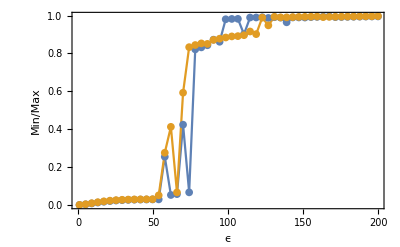

```mathematica
ListLinePlot[{Transpose@{Flatten@sweepWCU23["epsilonlist"],wig[#[[All,1]]]&/@sweepWCU23["spin"]},Transpose@{Flatten@sweepWCU35["epsilonlist"],wig[#[[All,1]]]&/@sweepWCU35["spin"]}},Mesh->All,Frame->True,FrameLabel->{"ϵ","Min/Max"}]
```

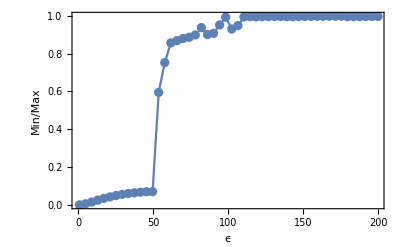

```mathematica
ListLinePlot[Transpose@{Flatten@sweepWCU35["epsilonlist"],wig[#[[All,1]]]&/@sweepWCU35["spin"]},Mesh->All,Frame->True,FrameLabel->{"ϵ","Min/Max"}]
```

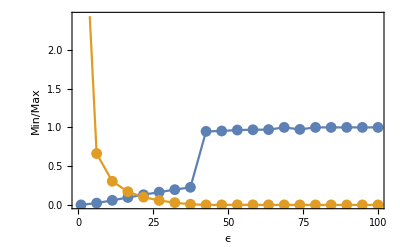

```mathematica
ListLinePlot[{Transpose@{Flatten@sweepWCU11["epsilonlist"],wig[#[[All,1]]]&/@sweepWCU11["spin"]},Transpose@{Flatten@sweepWCU11["epsilonlist"],10Flatten@sweepWCU11["gap"]}},Mesh->All,Frame->True,FrameLabel->{"ϵ","Min/Max"}]
```

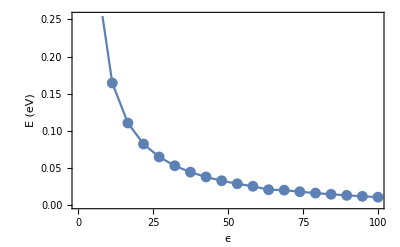

```mathematica
ListLinePlot[Transpose@{Flatten@sweepWC["epsilonlist"],Flatten@sweepWC["final"]},Mesh->All,Frame->True,FrameLabel->{"ϵ","E (eV)"}]
```

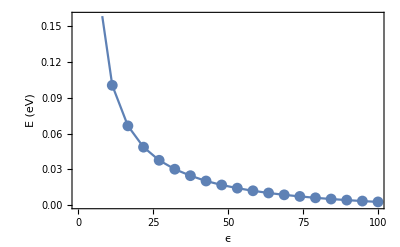

```mathematica
ListLinePlot[Transpose@{Flatten@sweepWCU11["epsilonlist"],Flatten@sweepWCU11["final"]},Mesh->All,Frame->True,FrameLabel->{"ϵ","E (eV)"}]
```

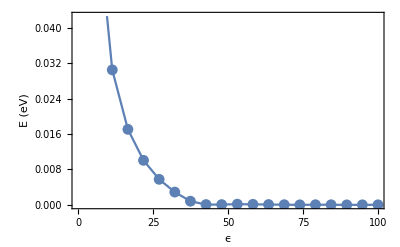

```mathematica
ListLinePlot[Transpose@{Flatten@sweepWCU11["epsilonlist"],Flatten@sweepWCU11["gap"]},Mesh->All,Frame->True,FrameLabel->{"ϵ","E (eV)"}]
```

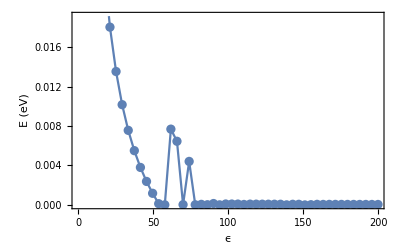

```mathematica
ListLinePlot[Transpose@{Flatten@sweepWCU23["epsilonlist"],Flatten@sweepWCU23["gap"]},Mesh->All,Frame->True,FrameLabel->{"ϵ","E (eV)"}]
```

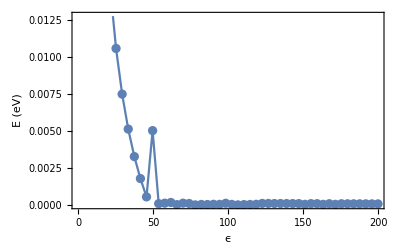

```mathematica
ListLinePlot[Transpose@{Flatten@sweepWCU35["epsilonlist"],Flatten@sweepWCU35["gap"]},Mesh->All,Frame->True,FrameLabel->{"ϵ","E (eV)"}]
```

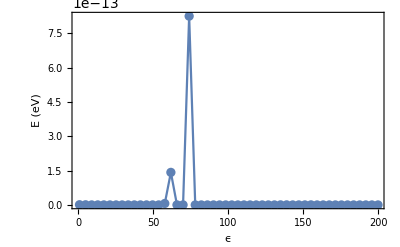

```mathematica
ListLinePlot[Transpose@{Flatten@sweepWCU23["epsilonlist"],Flatten@sweepWCU23["innergap"]},Mesh->All,Frame->True,FrameLabel->{"ϵ","E (eV)"},PlotRange->Full]
```

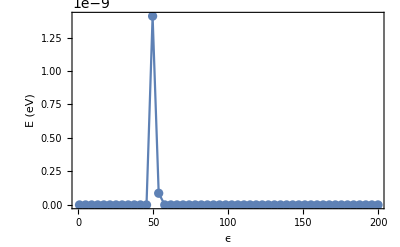

```mathematica
ListLinePlot[Transpose@{Flatten@sweepWCU35["epsilonlist"],Flatten@sweepWCU35["innergap"]},Mesh->All,Frame->True,FrameLabel->{"ϵ","E (eV)"},PlotRange->Full]
```

```mathematica
wig[data_]:=Block[{min=Min@data,max=Max@data},min/max]
```

### Sweep_nu=[1,2]

```mathematica
sweepnu12=importmat[NotebookDirectory[]<>"nu1,2_U1993_theta5.mat"];
```

```mathematica
sweepnu24=importmat[NotebookDirectory[]<>"nu2,4_U1993_theta5.mat"];
```

```mathematica
sweepnu36=importmat[NotebookDirectory[]<>"nu3,6_U1993_theta5.mat"];
```

```mathematica
sweepnu48=importmat[NotebookDirectory[]<>"nu4,8_U1993_theta5.mat"];
```

```mathematica
phase12=importmat[NotebookDirectory[]<>"phase1,2_U1993.mat"];
```

```mathematica
phase24=importmat[NotebookDirectory[]<>"phase2,4_U1993.mat"];
```

```mathematica
phase36=importmat[NotebookDirectory[]<>"phase3,6_U1993.mat"];
```

```mathematica
phase48=importmat[NotebookDirectory[]<>"phase4,8_U1993.mat"];
```

```mathematica
phase510=importmat[NotebookDirectory[]<>"phase5,10_U1993.mat"];
```

```mathematica
With[{i=1},NumberForm[{phase12["gap"][[-1,i]],phase12["final"][[-1,i]],phase12["innergap"][[-1,i]],phase12["finali"][[-1,i]]/1000}*1000,10]]
```

{496.6311998,4842.935721,0.03740501772,46.}

```mathematica
With[{i=1},NumberForm[{phase24["gap"][[-1,i]],phase24["final"][[-1,i]],phase24["innergap"][[-1,i]],phase24["finali"][[-1,i]]/1000}*1000,10]]
```

{348.8530814,4854.164279,1.951496451,21.}

```mathematica
With[{i=1},NumberForm[{phase36["gap"][[-1,i]],phase36["final"][[-1,i]],phase36["innergap"][[-1,i]],phase36["finali"][[-1,i]]/1000}*1000,10]]
```

{479.3946243,4842.944683,0.326379446,50.}

```mathematica
With[{i=1},NumberForm[{phase48["gap"][[-1,i]],phase48["final"][[-1,i]],phase48["innergap"][[-1,i]],phase48["finali"][[-1,i]]/1000}*1000,10]]
```

{479.3945785,4842.944683,0.326379114,82.}

```mathematica
phase24["spin"][[80,21]]//MatrixForm
```

(0.498555 | 0.0118371 | 0.000213707 | 0.000790882
0.49856 | 0.0122678 | -0.000481628 | 0.000604574
0.501372 | 0.00563932 | 0.0137983 | -0.0057562
0.501513 | -0.00335485 | -0.0114321 | 0.0170866)

```mathematica
phase36["spin"][[80,21]]//MatrixForm
```

(0.497172 | 0. | 0. | 0.0428206
0.497172 | 0. | 0. | 0.0428206
0.502828 | 0. | 0. | 0.0327349
0.502828 | 0. | 0. | 0.0327349)

```mathematica
phase48["gap"][[1,80]]
```

0.000183543

```mathematica
phase48["spin"][[80,1]]//MatrixForm
```

(0.5 | 0. | 0. | 0.5
0.5 | 0. | 0. | 0.5
0.5 | 0. | 0. | 0.5
0.499999 | 0. | 0. | 0.499999)

```mathematica
phase48["gap"][[21,80]]
```

0.000333874

```mathematica
phase48["spin"][[80,21]]//MatrixForm
```

(0.5 | 0. | 0. | 0.0377779
0.5 | 0. | 0. | 0.0377779
0.5 | 0. | 0. | 0.0377778
0.5 | 0. | 0. | 0.0377775)

```mathematica
sweepnu612=importmat[NotebookDirectory[]<>"nu6,12_U373.mat"];
```

```mathematica
sweepnu1224=importmat[NotebookDirectory[]<>"nu12,24_U373.mat"];
```

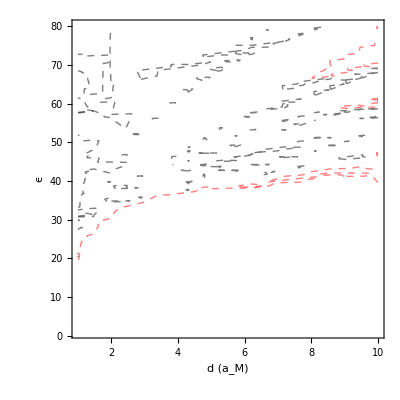

```mathematica
contour=ListContourPlot[1000Transpose@sweepnu12["gap"],DataRange->{sweepnu12["dlist"][[1,{1,-1}]],sweepnu12["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{.01,0.2},ContourShading->None,ContourStyle->{Directive[{Thick,Dashed,Black}],Directive[{Thick,Dashed,Red}]}]
```

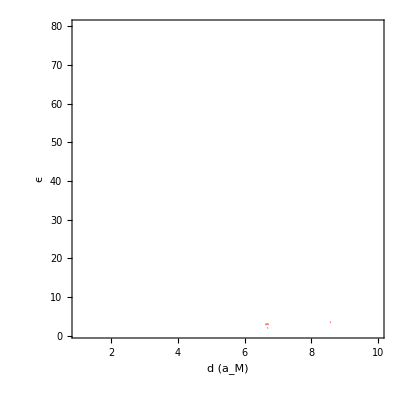

```mathematica
contourtetra=ListContourPlot[1000Transpose@sweepnu12tetra["gap"],DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{.01,0.2},ContourShading->None,ContourStyle->{Directive[{Thick,Dashed,Black}],Directive[{Thick,Dashed,Red}]}]
```

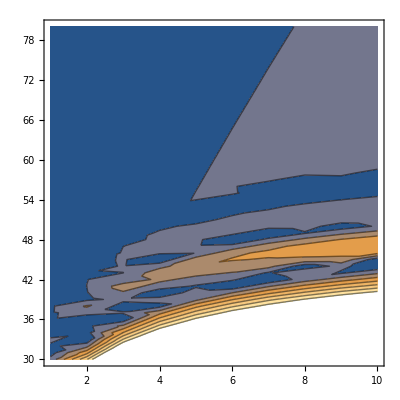

```mathematica
ListContourPlot[Transpose@sweepnu12["gap"][[1;;10,30;;80]],DataRange->{sweepnu12["dlist"][[1,{1,-1}]],sweepnu12["epsilonlist"][[1,{30,-1}]]}]
```

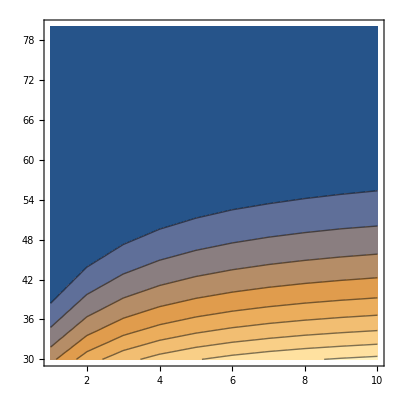

```mathematica
ListContourPlot[Transpose@sweepnu12tetra["gap"][[1;;10,30;;80]],DataRange->{sweepnu12["dlist"][[1,{1,-1}]],sweepnu12["epsilonlist"][[1,{30,-1}]]}]
```

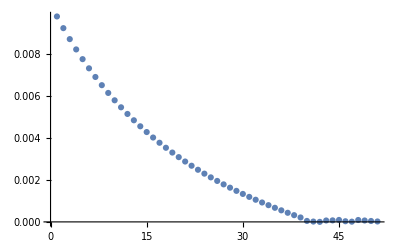

```mathematica
ListPlot[sweepnu12["gap"][[5,30;;80]],PlotRange->Full]
```

```mathematica
phase12["thetalist"]
```

$Failed[thetalist]

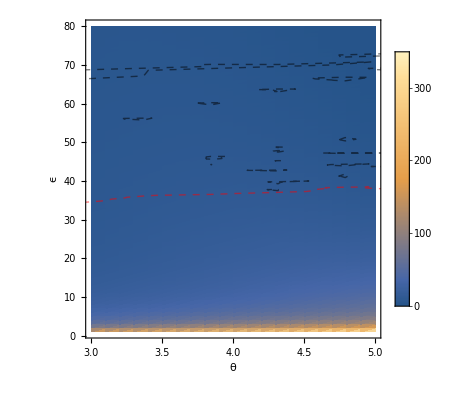

```mathematica
ListDensityPlot[1000Transpose@phase24["gap"],DataRange->{phase24["thetalist"][[1,{1,-1}]],phase24["epsilonlist"][[1,{1,-1}]]},(*ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,15},{0,1}]]&),ColorFunctionScaling->False,*)PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"θ","ϵ"},PlotRangePadding->None,BaseStyle->(FontSize->16),Epilog->{ First@contour}]
```

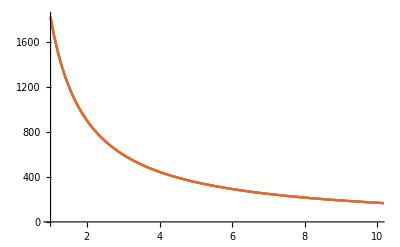

```mathematica
ListLinePlot[{Transpose@{sweepnu12["epsilonlist"][[1]],1000sweepnu12["final"][[-1]]},Transpose@{sweepnu24["epsilonlist"][[1]],1000sweepnu24["final"][[-1]]},Transpose@{sweepnu36["epsilonlist"][[1]],1000sweepnu36["final"][[-1]]},Transpose@{sweepnu48["epsilonlist"][[1]],1000sweepnu48["final"][[-1]]}},PlotRange->{{1,10},Full}]
```

```mathematica
phase12["final"]//Dimensions
```

{21,80}

```mathematica
Position[order,4]
```

{{5},{9},{11},{16},{17},{25},{76},{79},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{100},{491},{492},{493},{494},{495},{496},{497},{498},{499},{500},{501},{502},{503},{504},{505},{506},{507},{508},{509},{510},{511},{512},{513},{514},{515},{516},{517},{518},{519},{520},{521},{522},{523},{524},{525},{526},{527},{528},{529},{530},{531},{532},{533},{534},{535},{536},{537},{538},{539},{540}}

```mathematica
sweepnu12["spin"][[5,1]]//MatrixForm
```

(0.982853 | 0. | 0. | 0.982428
0.982853 | 0. | 0. | -0.982428
0.0171466 | 0. | 0. | -3.47376×10^-16
0.0171466 | 0. | 0. | 4.73695×10^-16)

```mathematica
sweepnu24["spin"][[5,1]]//MatrixForm
```

(0.5 | 0.288422 | 0.288422 | 0.288422
0.5 | 0.288422 | -0.288422 | -0.288422
0.5 | -0.288422 | 0.288422 | -0.288422
0.5 | -0.288422 | -0.288422 | 0.288422)

```mathematica
sweepnu36["spin"][[5,1]]//MatrixForm
```

(0.980016 | 0. | 0. | 0.980016
0.980016 | 0. | 0. | 0.980016
0.0199839 | 0. | 0. | 0.0199839
0.0199839 | 0. | 0. | 0.0199839)

```mathematica
sweepnu48["spin"][[5,1]]//MatrixForm
```

(0.980016 | 0. | 0. | 0.980016
0.980016 | 0. | 0. | 0.980016
0.0199841 | 0. | 0. | 0.0199841
0.0199839 | 0. | 0. | 0.0199839)

```mathematica
sweepnu48["epsilonlist"][[1,537]]
```

54.6

```mathematica
sameQ[data1_,data2_,err_:1*^-5]:=Block[{d1,d2},d1=If[Length[data1]==0,{data1},data1];d2=If[Length[data2]==0,ConstantArray[data2,Length[d1]],data2];If[Length[d1]==Length[d2],And@@Positive[(err-Abs[d1-d2])],$Failed]]
```

```mathematica
Clear[sameQ]
```

```mathematica
sameQ[{0,0},{1,2},10]
```

True

```mathematica
AFQ[spin_]:=Block[{ϕ=Arg[spin[[All,2]]+I*spin[[All,3]]],θ=Arg[I √(spin[[All,2]]^2+spin[[All,3]]^2)+spin[[All,4]]],n=spin[[All,1]]},And@@Flatten@{sameQ[ϕ,0],sameQ[θ[[1]],0],sameQ[θ[[2]],π],sameQ[n[[1]],n[[2]]],Thread[Abs[spin[[1;;2,4]]]>=0.14]}]
```

```mathematica
Clear[AFQ]
```

```mathematica
AFQ[sweepnu12["spin"][[1,1]]]
```

True

```mathematica
TetraQ[spin_]:=Block[{ϕ=Arg[spin[[All,2]]+I*spin[[All,3]]],θ=Arg[I √(spin[[All,2]]^2+spin[[All,3]]^2)+spin[[All,4]]],n=spin[[All,1]]},sameQ[n,1/2] && sameQ[ϕ*180/π,{45,-45,135,-135}]]
```

```mathematica
TetraQ[sweepnu48["spin"][[1,1]]]
```

False

```mathematica
FMWCQ[spin_]:=Block[{ϕ=Arg[spin[[All,2]]+I*spin[[All,3]]],θ=Arg[I √(spin[[All,2]]^2+spin[[All,3]]^2)+spin[[All,4]]],n=spin[[All,1]]},sameQ[ϕ,0]&&sameQ[θ[[1;;2]],0]&&sameQ[n[[1]],n[[2]]]&&!sameQ[n[[3]],n[[1]],0.05]&&!sameQ[n[[4]],n[[1]],0.05]]
```

```mathematica
FMWCQ[sweepnu48["spin"][[5,1]]]
```

True

```mathematica
FMWCQ[minspin2[[6,23]]]
```

True

```mathematica
FMNWCQ[spin_]:=Block[{ϕ=Arg[spin[[All,2]]+I*spin[[All,3]]],θ=Arg[I √(spin[[All,2]]^2+spin[[All,3]]^2)+spin[[All,4]]],n=spin[[All,1]]},And@@Flatten@{sameQ[ϕ,0],sameQ[θ[[1;;2]],0],sameQ[n,0.5],Thread[Abs[spin[[All,4]]]>=0.14]}]
```

```mathematica
SpinlessQ[minspin2[[21,79]]]
```

False

```mathematica
SpinlessQ[spin_]:=Block[{ϕ=Arg[spin[[All,2]]+I*spin[[All,3]]],θ=Arg[I √(spin[[All,2]]^2+spin[[All,3]]^2)+spin[[All,4]]],n=spin[[All,1]]},And@@Flatten@{sameQ[n,0.5,0.05],Thread[(Norm/@spin[[All,2;;4]])<0.14]}]
```

```mathematica
SpinlessQ[minspin2[[21,79]]]
```

True

```mathematica
minspin2[[21,79]]
```

{{0.502836,0.0134903,0.000148276,0.0134872},{0.497164,0.000201299,-0.00997914,-0.0000933323},{0.502836,-0.0134904,-0.000143691,-0.0134872},{0.497164,-0.000048581,-0.00998026,0.000156616}}

```mathematica
sameQ[minspin2[[21,79,All,1]],0.5,0.05]
```

True

```mathematica
(Norm/@minspin2[[21,79]][[All,2;;4]])<0.1
```

{0.0190766,0.00998161,0.0190766,0.00998161}<0.1

```mathematica
phase12["spin"][[69,19]]
```

{{0.500324,0.,0.,0.0266356},{0.500324,0.,0.,-0.0266356},{0.499676,0.,0.,-0.00033469},{0.499676,0.,0.,0.00033469}}

```mathematica
KagomeQ[spin_]:=Block[{ϕ=Arg[spin[[All,2]]+I*spin[[All,3]]],θ=Arg[I √(spin[[All,2]]^2+spin[[All,3]]^2)+spin[[All,4]]],n=spin[[All,1]]},sameQ[spin[[1,4]],spin[[2,4]],0.05]&&sameQ[spin[[2,4]],spin[[3,4]],0.05]&&(spin[[3,4]]/spin[[4,4]])>2&&sameQ[ϕ,0]&&sameQ[θ[[1;;3]],0]]
```

```mathematica
KagomeQ[{{0.5726,0,0,0.5351},{0.5726,0,0,0.5351},{0.5726,0,0,0.5351},{0.2821,0,0,0.2170}}]
```

True

```mathematica
minspin2[[21,54]]
```

{{0.501213,0.,0.,0.125559},{0.501213,0.,0.,0.125559},{0.497123,0.,0.,0.116684},{0.500452,0.,0.,0.0677543}}

```mathematica
KagomeQ[minspin2[[15,80]]]
```

True

```mathematica
order=(Ordering/@Transpose@{sweepnu12["final"][[-1]],sweepnu24["final"][[-1]],sweepnu36["final"][[-1]],sweepnu48["final"][[-1]]})[[All,1]]
```

{1,1,1,1,4,3,3,3,4,3,4,3,3,3,3,4,4,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,1,3,3,3,3,1,3,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,3,1,1,3,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,2,2,2,2,2,2,1,2,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1}

```mathematica
mingap=MapThread[#1[[#2]]&,{Transpose[{sweepnu12["gap"][[-1]],sweepnu24["gap"][[-1]],sweepnu36["gap"][[-1]],sweepnu48["gap"][[-1]]}],order}]
```

{0.496631,0.450699,0.412265,0.37953,0.331565,0.306818,0.285133,0.265973,0.248922,0.23365,0.219893,0.207436,0.196104,0.185752,0.17626,0.167525,0.15946,0.151994,0.145061,0.138608,0.132588,0.126958,0.121683,0.11673,0.112073,0.107685,0.103544,0.0996305,0.0959269,0.0924169,0.0890862,0.0859178,0.0828973,0.0800206,0.0772777,0.0746599,0.0721589,0.0697674,0.0674785,0.065286,0.0631839,0.0611672,0.0592307,0.0573699,0.0555806,0.0538589,0.0522012,0.050604,0.0490643,0.047579,0.0461454,0.044761,0.0434233,0.0421302,0.0408794,0.0396691,0.0384973,0.0373624,0.0362626,0.0351964,0.0341623,0.0331591,0.0321853,0.0312397,0.0303212,0.0294287,0.0285611,0.0277175,0.0268968,0.0260983,0.025321,0.0245642,0.023827,0.0231089,0.022409,0.0254454,0.0210614,0.0204124,0.0236099,0.0191615,0.00659955,0.00650192,0.00640732,0.00631557,0.00622657,0.00614018,0.00605625,0.00597473,0.018325,0.00581837,0.00574335,0.00567032,0.00559921,0.00552994,0.00546241,0.00539659,0.0053324,0.0439567,0.0436003,0.0136525,0.0429042,0.0425642,0.0422294,0.0418995,0.0415746,0.0412544,0.0409389,0.040628,0.0403214,0.0400192,0.0397212,0.0394273,0.0391373,0.0388514,0.0385692,0.0382908,0.038016,0.0377448,0.0374771,0.0372129,0.0369519,0.0366942,0.0364398,0.0361884,0.0359402,0.0356949,0.0354525,0.0352131,0.0349765,0.0347426,0.0345114,0.0342829,0.0340553,0.0338268,0.0336008,0.0333765,0.0331473,0.0329206,0.0326964,0.0324747,0.0322553,0.032032,0.0318089,0.0315882,0.0313698,0.0311536,0.0309397,0.030728,0.0305162,0.0303023,0.0300905,0.0298808,0.0296732,0.0294676,0.029264,0.0290625,0.0288628,0.0286646,0.0284647,0.0282668,0.0280708,0.0278765,0.0276841,0.0274935,0.0273046,0.0271175,0.0269316,0.0267472,0.0265641,0.0263818,0.0262011,0.026022,0.0258445,0.0256686,0.0254943,0.0253211,0.0251492,0.0249789,0.02481,0.0246425,0.0244765,0.0243119,0.0241487,0.0239869,0.0238264,0.0236673,0.0235095,0.023353,0.0231978,0.0230439,0.0228912,0.0227398,0.0225896,0.0224407,0.0222929,0.0221463,0.0220009,0.0218567,0.0217135,0.0215716,0.0214307,0.0212909,0.0211523,0.0210147,0.0208782,0.0207427,0.0206083,0.0204749,0.0203425,0.0202111,0.0200807,0.0199513,0.0198229,0.0196955,0.0195689,0.0194434,0.0193188,0.019195,0.0190723,0.0189504,0.0188294,0.0187092,0.01859,0.0184716,0.0183541,0.0182374,0.0181216,0.0180066,0.0178924,0.017779,0.0176664,0.0175546,0.0174436,0.0173334,0.017224,0.0171153,0.0170074,0.0169002,0.0167938,0.0166881,0.0165831,0.0164789,0.0163753,0.0162725,0.0161704,0.0160689,0.0159682,0.0158681,0.0157687,0.01567,0.0155719,0.0154744,0.0153777,0.0152815,0.015186,0.0150912,0.0149969,0.0149033,0.0148103,0.0147178,0.014626,0.0145348,0.0144442,0.0143541,0.0142647,0.0141758,0.0140874,0.0139997,0.0139125,0.0138258,0.0137397,0.0136542,0.0135692,0.0134847,0.0134007,0.0133173,0.0132344,0.013152,0.0130701,0.0129887,0.0129079,0.0128275,0.0127476,0.0126682,0.0125893,0.0125109,0.0124329,0.0123555,0.0122784,0.0122019,0.0121258,0.0120502,0.011975,0.0119003,0.0118261,0.0117522,0.0116788,0.0116059,0.0115334,0.0114613,0.0113896,0.0113183,0.0112475,0.0111771,0.0111071,0.0110375,0.0109683,0.0108995,0.0108311,0.0107631,0.0106955,0.0106283,0.0105614,0.010495,0.0104289,0.0103632,0.0102979,0.010233,0.0101684,0.0101042,0.0100403,0.0099768,0.00991366,0.00985088,0.00978844,0.00972636,0.00966462,0.00960322,0.00954216,0.00948144,0.00942106,0.00936101,0.00930129,0.0092419,0.00918283,0.00912409,0.00906566,0.00900756,0.00894977,0.0088923,0.00883513,0.00877828,0.00872173,0.00866548,0.00860954,0.0085539,0.00849856,0.00844351,0.00838875,0.00833429,0.00828012,0.00822623,0.00817263,0.00811931,0.00806627,0.00801352,0.00796103,0.00790883,0.0078569,0.00780523,0.00775384,0.00770272,0.00765186,0.00760126,0.00755093,0.00750086,0.00745104,0.00740148,0.00735218,0.00730313,0.00725433,0.00720578,0.00715747,0.00710942,0.00706161,0.00701404,0.00696671,0.00691962,0.00687277,0.00682615,0.00677977,0.00673362,0.00668771,0.00664202,0.00659657,0.00655133,0.00650633,0.00646155,0.00641699,0.00637265,0.00632853,0.00628463,0.00624094,0.00619747,0.00615422,0.00611117,0.00606834,0.00602572,0.0059833,0.00594109,0.00589909,0.00585729,0.00581569,0.0057743,0.00573311,0.00569211,0.00565131,0.00561071,0.0055703,0.00553009,0.00549007,0.00545024,0.0054106,0.00537115,0.00533189,0.00529282,0.00525393,0.00521522,0.0051767,0.00513836,0.0051002,0.00506222,0.00502442,0.00498679,0.00494934,0.00491207,0.00487497,0.00483805,0.0048013,0.00476471,0.0047283,0.00469206,0.00465598,0.00462007,0.00458433,0.00454875,0.00451334,0.00447809,0.004443,0.00440807,0.0043733,0.00433869,0.00430424,0.00426994,0.0042358,0.00420183,0.00416799,0.00413432,0.00410079,0.00406742,0.0040342,0.00400113,0.00396821,0.00393543,0.0039028,0.00387032,0.00383799,0.0038058,0.00377375,0.00374184,0.00371008,0.00367846,0.00364698,0.00361564,0.00358444,0.00355337,0.00352244,0.00349165,0.003461,0.00343048,0.00340009,0.00336983,0.00333971,0.00330972,0.00327987,0.00325014,0.00322054,0.00319107,0.00316173,0.00313252,0.00310343,0.00307447,0.00304563,0.00301692,0.00298833,0.00295987,0.00293152,0.0029033,0.0028752,0.00284722,0.000477503,0.000471011,0.00046455,0.000458117,0.000451715,0.000445342,0.000438998,0.000432683,0.000426396,0.000420137,0.000413907,0.000407705,0.00040153,0.000395383,0.000389263,0.00038317,0.000338165,0.000332047,0.000325956,0.000319892,0.000313858,0.000307844,0.00034423,0.000338355,0.000332504,0.000326678,0.000320877,0.000312086,0.000306326,0.00030059,0.000294878,0.000249147,0.000286578,0.000280944,0.000275334,0.000269747,0.000264182,0.000258641,0.000253122,0.000247625,0.000242151,0.000236699,0.000231269,0.00022586,0.000220474,0.000215109,0.000209765,0.000204443,0.000195997,0.000193861,0.000804932,0.000293728,0.000290253,0.0000712669,0.0000670208,0.000797491,0.000276476,0.000794552,0.000793091,0.000791636,0.000790185,0.00078874,0.0007873,0.000785866,0.000784436,0.000783012,0.000781593,0.000780179,0.00023631,0.000777367,0.000775968,0.000774574,0.000773185,0.000220071,0.000770423,0.000769049,0.000210463,0.000766315,0.000103963,0.000763602,0.000762252,0.000811152,0.000759566,0.000758231,0.0007569,0.00080531,0.000529879,0.000802423,0.000751622,0.000750314,0.000798133,0.000747712,0.000746418,0.000793891,0.000743842,0.000742561,0.000741284,0.000740012,0.000738744,0.00073748,0.000736221,0.000734966,0.000733715,0.000732469,0.000731226,0.000729988,0.000728754,0.000727525,0.000726299,0.000725077,0.00072386,0.000722646,0.000721437,0.000720232,0.000719031,0.000717833,0.00076288,0.000761589,0.000714265,0.000759021,0.000711906,0.000710732,0.000709562,0.000415585,0.000707234,0.000706075,0.000407227,0.000404459,0.000702623,0.000701479,0.000700339,0.000743982,0.000742757,0.000696942,0.000695817,0.000694696,0.000693578,0.000692464,0.000691353,0.000690246,0.000688581,0.000731916,0.000753787,0.000685852,0.000751542,0.000683676,0.000726032,0.000724867,0.000680438,0.000745999,0.000744902,0.000743809,0.00074272,0.000741634,0.000740552,0.000715686,0.0007384,0.000670905,0.000712303,0.000735199,0.00073414,0.000733084,0.000732031,0.000730983,0.000671692,0.000728896,0.000727858,0.000726823,0.000725792,0.000665901,0.000723741,0.000656642,0.000721703,0.000720689,0.000660187,0.000718672,0.000717669,0.000716668,0.000715672,0.000714678,0.000713688,0.000712701,0.000711718,0.000710737,0.00070976,0.000708786,0.000707816,0.000706848,0.000705884,0.000704923,0.000703965,0.000703011,0.000702059,0.000701111,0.000700165,0.000699223,0.000698284,0.000697348,0.000696415,0.000669171,0.000694558,0.000693634,0.000692713,0.000645592,0.00069088,0.000689968,0.000689059,0.000688153,0.000687249,0.000686349,0.000685451,0.000684557,0.000683665,0.000682776,0.00068189,0.000681007,0.000680127,0.000679249,0.000678374,0.000677502,0.000676633,0.000675767,0.000674903,0.000674042,0.000673184,0.000672328,0.000671475,0.000670625,0.000669778,0.000668933,0.000668091,0.000639044,0.000666414,0.00066558,0.000664748,0.000663919,0.000663093,0.000662269,0.000661448,0.000660629,0.000659813,0.000658999,0.000658188,0.00059167,0.000656573,0.00065577,0.000592608,0.00065417,0.000590958,0.00065258,0.000651789,0.000651,0.000587705,0.00064943,0.000648648,0.000613877,0.000647092,0.000581024,0.000645546,0.000644776,0.000644009,0.000643244,0.000642482,0.000641721,0.000575107,0.000640208,0.000639454,0.000638703,0.000637955,0.000637208,0.000636464,0.000569781,0.000634982,0.000634245,0.000633509,0.000632776,0.000632045,0.000631317,0.000630591,0.000629866,0.000629144,0.000628424,0.000596338,0.000626991,0.000626278,0.000625567,0.000624857,0.00062415,0.000623446,0.000622743,0.000622042,0.000621344,0.000620647,0.000619953,0.000619261,0.00061857,0.000617882,0.000617196,0.000616512,0.00061583,0.000548611}

```mathematica
mininnergap=MapThread[#1[[#2]]&,{Transpose[{sweepnu12["innergap"][[-1]],sweepnu24["innergap"][[-1]],sweepnu36["innergap"][[-1]],sweepnu48["innergap"][[-1]]}],order}]
```

{0.0000374044,0.0000179202,0.0000338486,0.0000729109,0.000283188,0.000272374,0.000261559,0.000250745,0.000239935,0.000229133,0.000218339,0.000207558,0.00019679,0.000186038,0.000175302,0.000164585,0.000153889,0.000143213,0.000132559,0.000121928,0.000111319,0.000100734,0.0000901729,0.0000796357,0.0000691218,0.0000586328,0.0000481675,0.0000377262,0.0000273079,0.0000169133,6.54177×10^-6,3.80734×10^-6,0.0000141342,0.0000244388,0.0000347223,0.0000449844,0.0000552264,0.0000654477,0.0000756498,0.0000858321,0.0000959961,0.000106141,0.000116268,0.000126378,0.000136471,0.000146546,0.000156606,0.000166649,0.000176678,0.00018669,0.000196688,0.000206671,0.000216641,0.000226596,0.000236537,0.000246466,0.000256381,0.000266283,0.000276173,0.000286051,0.000295916,0.000305769,0.00031561,0.00032544,0.000335258,0.000345065,0.00035486,0.000364644,0.000374417,0.000384179,0.000393931,0.00040367,0.000413401,0.000423119,0.000432828,0.00240337,0.000452212,0.000461888,0.00249716,0.000481208,0.00588379,0.00587683,0.00586931,0.00586132,0.00585291,0.0058441,0.00583499,0.00582555,0.00282021,0.00580599,0.00579591,0.00578568,0.00577531,0.00576481,0.00575423,0.00574357,0.00573286,1.78316×10^-9,1.786×10^-9,0.00318747,1.77622×10^-9,1.7947×10^-9,1.79765×10^-9,1.80062×10^-9,1.80361×10^-9,1.80663×10^-9,1.80967×10^-9,1.79913×10^-9,1.8158×10^-9,1.80585×10^-9,1.82201×10^-9,1.82515×10^-9,1.81603×10^-9,1.81945×10^-9,1.83463×10^-9,1.82633×10^-9,1.82979×10^-9,1.83326×10^-9,1.83674×10^-9,1.83081×10^-9,1.84372×10^-9,1.84722×10^-9,1.85073×10^-9,1.85425×10^-9,1.85778×10^-9,1.86131×10^-9,1.86484×10^-9,1.86838×10^-9,1.87193×10^-9,1.87548×10^-9,1.87903×10^-9,1.88259×10^-9,1.95139×10^-9,1.95441×10^-9,1.95744×10^-9,1.96224×10^-9,1.96493×10^-9,1.96761×10^-9,1.9703×10^-9,1.97298×10^-9,1.97567×10^-9,1.76548×10^-9,1.76817×10^-9,1.77086×10^-9,1.77355×10^-9,1.77625×10^-9,1.77894×10^-9,1.78163×10^-9,1.31176×10^-9,1.31418×10^-9,1.31661×10^-9,1.31904×10^-9,1.32148×10^-9,1.32391×10^-9,1.32635×10^-9,1.32879×10^-9,1.33123×10^-9,7.17996×10^-10,7.19541×10^-10,7.21087×10^-10,7.22636×10^-10,7.23942×10^-10,7.25739×10^-10,7.27295×10^-10,7.28853×10^-10,7.30243×10^-10,5.92409×10^-10,5.93933×10^-10,2.0604×10^-10,2.06525×10^-10,2.0701×10^-10,2.07497×10^-10,2.07985×10^-10,2.08473×10^-10,2.08962×10^-10,3.40187×10^-7,8.66211×10^-7,1.38632×10^-6,1.9006×10^-6,2.40917×10^-6,2.9121×10^-6,3.40949×10^-6,3.90144×10^-6,4.38802×10^-6,4.86933×10^-6,5.34545×10^-6,5.81646×10^-6,6.28245×10^-6,6.74348×10^-6,7.19965×10^-6,7.65102×10^-6,8.09768×10^-6,8.53969×10^-6,8.97712×10^-6,9.41005×10^-6,9.83855×10^-6,0.0000102627,0.0000106825,0.0000110981,0.0000115095,0.0000119168,0.0000123201,0.0000127193,0.0000131147,0.0000135062,0.0000138938,0.0000142777,0.0000146579,0.0000150344,0.0000154074,0.0000157767,0.0000161426,0.0000165051,0.0000168641,0.0000172198,0.0000175722,0.0000179213,0.0000182673,0.00001861,0.0000189497,0.0000192862,0.0000196198,0.0000199503,0.0000202779,0.0000206025,0.0000209243,0.0000212433,0.0000215594,0.0000218728,0.0000221835,0.0000224915,0.0000227968,0.0000230995,0.0000233997,0.0000236973,0.0000239923,0.0000242849,0.0000245751,0.0000248628,0.0000251481,0.0000254311,0.0000257118,0.0000259901,0.0000262662,0.0000265401,0.0000268117,0.0000270812,0.0000273485,0.0000276137,0.0000278768,0.0000281378,0.0000283968,0.0000286537,0.0000289086,0.0000291616,0.0000294126,0.0000296617,0.0000299088,0.0000301541,0.0000303976,0.0000306392,0.000030879,0.000031117,0.0000313532,0.0000315877,0.0000318204,0.0000320515,0.0000322808,0.0000325085,0.0000327346,0.000032959,0.0000331818,0.000033403,0.0000336226,0.0000338407,0.0000340572,0.0000342723,0.0000344858,0.0000346978,0.0000349084,0.0000351175,0.0000353252,0.0000355314,0.0000357363,0.0000359398,0.0000361419,0.0000363426,0.000036542,0.0000367401,0.0000369369,0.0000371323,0.0000373265,0.0000375194,0.0000377111,0.0000379015,0.0000380907,0.0000382787,0.0000384654,0.000038651,0.0000388354,0.0000390187,0.0000392008,0.0000393817,0.0000395616,0.0000397403,0.0000399179,0.0000400944,0.0000402698,0.0000404442,0.0000406175,0.0000407898,0.000040961,0.0000411313,0.0000413004,0.0000414686,0.0000416358,0.000041802,0.0000419673,0.0000421316,0.0000422949,0.0000424573,0.0000426187,0.0000427793,0.0000429389,0.0000430976,0.0000432554,0.0000434123,0.0000435684,0.0000437236,0.0000438779,0.0000440314,0.000044184,0.0000443358,0.0000444867,0.0000446369,0.0000447862,0.0000449348,0.0000450825,0.0000452294,0.0000453756,0.000045521,0.0000456656,0.0000458095,0.0000459527,0.000046095,0.0000462367,0.0000463776,0.0000465178,0.0000466573,0.0000467961,0.0000469342,0.0000470716,0.0000472083,0.0000473443,0.0000474796,0.0000476143,0.0000477483,0.0000478817,0.0000480144,0.0000481465,0.0000482779,0.0000484087,0.0000485389,0.0000486684,0.0000487974,0.0000489257,0.0000490534,0.0000491806,0.0000493071,0.0000494331,0.0000495584,0.0000496833,0.0000498075,0.0000499312,0.0000500543,0.0000501768,0.0000502988,0.0000504203,0.0000505412,0.0000506616,0.0000507815,0.0000509008,0.0000510197,0.000051138,0.0000512558,0.0000513731,0.0000514898,0.0000516061,0.0000517219,0.0000518372,0.0000519521,0.0000520664,0.0000521803,0.0000522937,0.0000524066,0.0000525191,0.0000526311,0.0000527427,0.0000528538,0.0000529645,0.0000530747,0.0000531845,0.0000532938,0.0000534027,0.0000535112,0.0000536193,0.0000537269,0.0000538342,0.000053941,0.0000540474,0.0000541534,0.000054259,0.0000543642,0.000054469,0.0000545735,0.0000546775,0.0000547811,0.0000548844,0.0000549873,0.0000550898,0.0000551919,0.0000552937,0.0000553951,0.0000554962,0.0000555969,0.0000556972,0.0000557972,0.0000558968,0.0000559961,0.000056095,0.0000561936,0.0000562919,0.0000563898,0.0000564874,0.0000565847,0.0000566816,0.0000567782,0.0000568746,0.0000569705,0.0000570662,0.0000571615,0.0000572566,0.0000573513,0.0000574457,0.0000575398,0.0000576337,0.0000577272,0.0000578204,0.0000579133,0.000058006,0.0000580984,0.0000581904,0.0000582822,0.0000583737,0.000058465,0.0000585559,0.0000586466,0.000058737,0.0000588272,0.0000589171,0.0000590067,0.000059096,0.0000591851,0.000059274,0.0000593626,0.0000594509,0.000059539,0.0000596268,0.0000597144,0.0000598017,0.0000598888,0.0000599757,0.0000600623,0.0000601487,0.0000602348,0.0000603207,0.0000604064,0.0000604918,0.0000605771,0.0000606621,0.0000607468,0.0000608314,0.0000609157,0.0000609998,0.0000610837,0.0000611674,0.0000612509,0.0000613342,0.0000614172,0.0000615001,0.0000631752,0.0000624955,0.000061823,0.0000611577,0.0000604994,0.0000598482,0.0000592039,0.0000585683,0.0000579376,0.0000573135,0.0000566961,0.0000560851,0.0000554807,0.0000548826,0.0000542927,0.000053707,5.7337×10^-10,5.74707×10^-10,5.75935×10^-10,5.77061×10^-10,5.66702×10^-10,5.76585×10^-10,0.0000438793,0.0000433328,0.000042792,0.000042257,0.0000417275,0.0000471418,0.0000466309,0.0000461252,0.0000456248,0.0000315323,0.000038668,0.0000381765,0.0000376903,0.0000372111,0.000036733,0.0000362638,0.0000357976,0.0000353362,0.0000348797,0.0000344279,0.0000339808,0.0000335384,0.0000331006,0.0000326673,0.0000322405,0.0000318138,0.0000374499,0.0000309799,6.39593×10^-6,3.22244×10^-9,3.22244×10^-9,0.0000565798,0.0000563971,5.99602×10^-6,3.22244×10^-9,5.84389×10^-6,5.76983×10^-6,5.69593×10^-6,5.62404×10^-6,5.55253×10^-6,5.48201×10^-6,5.41194×10^-6,5.34383×10^-6,5.27613×10^-6,5.20889×10^-6,5.14301×10^-6,3.22244×10^-9,5.01389×10^-6,4.95061×10^-6,4.88817×10^-6,4.82656×10^-6,3.22243×10^-9,4.70575×10^-6,4.64652×10^-6,3.22244×10^-9,4.53039×10^-6,3.22244×10^-9,4.41724×10^-6,4.36214×10^-6,0.000165102,4.25293×10^-6,4.19955×10^-6,4.14686×10^-6,0.000161636,0.0000114782,0.000159943,3.94268×10^-6,3.89364×10^-6,0.000157461,3.79619×10^-6,3.74857×10^-6,0.000155035,3.65546×10^-6,3.60924×10^-6,3.56394×10^-6,3.51953×10^-6,3.475×10^-6,3.43163×10^-6,3.38822×10^-6,3.34563×10^-6,3.30354×10^-6,3.26197×10^-6,3.2209×10^-6,3.18033×10^-6,3.14024×10^-6,3.10063×10^-6,3.0615×10^-6,3.02283×10^-6,2.98462×10^-6,2.94687×10^-6,2.90956×10^-6,2.87269×10^-6,2.83625×10^-6,2.80025×10^-6,0.000138221,0.000137555,2.69474×10^-6,0.000136236,2.62642×10^-6,2.59286×10^-6,2.55968×10^-6,2.43241×10^-6,2.49469×10^-6,2.46243×10^-6,2.42075×10^-6,2.41689×10^-6,2.36847×10^-6,2.33786×10^-6,2.3076×10^-6,0.000128724,0.000128127,2.21884×10^-6,2.18992×10^-6,2.16133×10^-6,2.13305×10^-6,2.10508×10^-6,2.07743×10^-6,2.05009×10^-6,0.000194767,0.000122939,0.0000994219,1.9437×10^-6,0.0000982052,1.89225×10^-6,0.000120196,0.000119658,1.81715×10^-6,0.0000952291,0.0000946448,0.000094064,0.0000934868,0.0000929131,0.0000923428,0.000115488,0.0000912125,1.60607×10^-6,0.000113982,0.0000895422,0.000088992,0.000088445,0.0000879012,0.0000873607,2.53554×10^-9,0.0000862889,0.0000857577,0.0000852295,0.0000847044,2.77837×10^-9,0.0000836631,0.000131663,0.0000826336,0.0000821232,1.55129×10^-9,0.0000811111,0.0000806092,0.0000801102,0.0000796138,0.0000791203,0.0000786294,0.0000781413,0.0000776558,0.000077173,0.0000766928,0.0000762152,0.0000757401,0.0000752677,0.0000747977,0.0000743303,0.0000738653,0.0000734028,0.0000729427,0.0000724851,0.0000720299,0.000071577,0.0000711265,0.0000706783,0.0000702325,0.0000960718,0.0000693476,0.0000689086,0.0000684718,2.09312×10^-9,0.0000676049,0.0000671747,0.0000667467,0.0000663208,0.0000658971,0.0000654754,0.0000650558,0.0000646383,0.0000642229,0.0000638095,0.000063398,0.0000629886,0.0000625812,0.0000621758,0.0000617723,0.0000613707,0.0000609711,0.0000605734,0.0000601775,0.0000597835,0.0000593914,0.0000590011,0.0000586126,0.000058226,0.0000578411,0.000057458,0.0000570767,0.0000848998,0.0000563193,0.0000559432,0.0000555688,0.0000551961,0.0000548251,0.0000544557,0.000054088,0.0000537218,0.0000533574,0.0000529946,0.0000526333,3.2859×10^-7,0.0000519155,0.0000515589,2.55451×10^-9,0.0000508505,7.63632×10^-9,0.0000501482,0.0000497992,0.0000494518,8.79924×10^-9,0.0000487612,0.0000484181,0.0000792694,0.0000477363,1.94347×10^-6,0.0000470602,0.0000467241,0.0000463895,0.0000460562,0.0000457243,0.0000453938,0.000098172,0.0000447367,0.0000444101,0.0000440848,0.0000437609,0.0000434382,0.0000431167,0.000096268,0.0000424777,0.00004216,0.0000418436,0.0000415284,0.0000412145,0.0000409016,0.00004059,0.0000402796,0.0000399704,0.0000396623,0.0000707534,0.0000390497,0.000038745,0.0000384415,0.0000381392,0.0000378379,0.0000375377,0.0000372387,0.0000369407,0.0000366438,0.000036348,0.0000360532,0.0000357596,0.0000354669,0.0000351753,0.0000348846,0.000034595,0.0000343065,9.34792×10^-8}

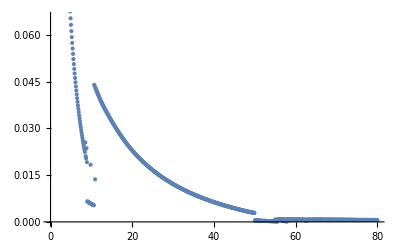

```mathematica
ListPlot[mingap,DataRange->sweepnu12["epsilonlist"][[1,{1,-1}]]]
```

```mathematica
sweepnu12["gap"][[1,493]]
```

0.000335124

```mathematica
mingap[[493]]<1*^-3
```

True

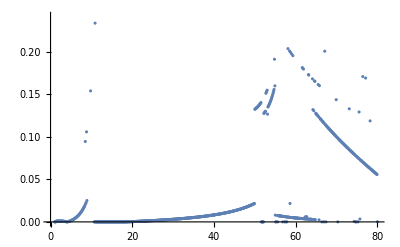

```mathematica
ListPlot[mininnergap/mingap,DataRange->sweepnu12["epsilonlist"][[1,{1,-1}]]]
```

```mathematica
minspin=MapThread[#1[[#2]]&,{Transpose[{sweepnu12["spin"][[All,1]],sweepnu24["spin"][[All,1]],sweepnu36["spin"][[All,1]],sweepnu48["spin"][[All,1]]}],order}];
```

```mathematica
phase=Table[{mingap[[i]]>1*^-3,AFQ[minspin[[i]]],FMQ[minspin[[i]]],TetraQ[minspin[[i]]]},{i,Length[minspin]}]
```

{{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,False,True},{True,False,False,True},{True,False,True,False},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,True,False,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,False,True,False},{False,True,False,False},{False,False,True,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,True,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,True,False},{False,True,False,False},{False,True,False,False},{False,False,True,False},{False,True,False,False},{False,False,True,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,True,False},{False,True,False,False},{False,True,False,False},{False,False,True,False},{False,False,True,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False}}

```mathematica
Boole[True]
```

1

```mathematica
phase
```

{{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,False,True},{True,False,True,False},{True,False,True,False},{True,False,False,True},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{True,False,True,False},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,True,False,False},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,False,False,True},{False,True,False,False},{False,False,False,True},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,True},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,True},{False,True,False,False},{False,True,False,False},{False,False,False,True},{False,True,False,False},{False,False,False,True},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,True},{False,True,False,False},{False,True,False,False},{False,False,False,True},{False,False,False,True},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,True,False,False}}

```mathematica
Total[Boole@#]&/@Select[phase,#[[1]]==True&][[All,2;;4]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
sweepnu12["epsilonlist"][[1]]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.1,30.2,30.3,30.4,30.5,30.6,30.7,30.8,30.9,31.,31.1,31.2,31.3,31.4,31.5,31.6,31.7,31.8,31.9,32.,32.1,32.2,32.3,32.4,32.5,32.6,32.7,32.8,32.9,33.,33.1,33.2,33.3,33.4,33.5,33.6,33.7,33.8,33.9,34.,34.1,34.2,34.3,34.4,34.5,34.6,34.7,34.8,34.9,35.,35.1,35.2,35.3,35.4,35.5,35.6,35.7,35.8,35.9,36.,36.1,36.2,36.3,36.4,36.5,36.6,36.7,36.8,36.9,37.,37.1,37.2,37.3,37.4,37.5,37.6,37.7,37.8,37.9,38.,38.1,38.2,38.3,38.4,38.5,38.6,38.7,38.8,38.9,39.,39.1,39.2,39.3,39.4,39.5,39.6,39.7,39.8,39.9,40.,40.1,40.2,40.3,40.4,40.5,40.6,40.7,40.8,40.9,41.,41.1,41.2,41.3,41.4,41.5,41.6,41.7,41.8,41.9,42.,42.1,42.2,42.3,42.4,42.5,42.6,42.7,42.8,42.9,43.,43.1,43.2,43.3,43.4,43.5,43.6,43.7,43.8,43.9,44.,44.1,44.2,44.3,44.4,44.5,44.6,44.7,44.8,44.9,45.,45.1,45.2,45.3,45.4,45.5,45.6,45.7,45.8,45.9,46.,46.1,46.2,46.3,46.4,46.5,46.6,46.7,46.8,46.9,47.,47.1,47.2,47.3,47.4,47.5,47.6,47.7,47.8,47.9,48.,48.1,48.2,48.3,48.4,48.5,48.6,48.7,48.8,48.9,49.,49.1,49.2,49.3,49.4,49.5,49.6,49.7,49.8,49.9,50.,50.1,50.2,50.3,50.4,50.5,50.6,50.7,50.8,50.9,51.,51.1,51.2,51.3,51.4,51.5,51.6,51.7,51.8,51.9,52.,52.1,52.2,52.3,52.4,52.5,52.6,52.7,52.8,52.9,53.,53.1,53.2,53.3,53.4,53.5,53.6,53.7,53.8,53.9,54.,54.1,54.2,54.3,54.4,54.5,54.6,54.7,54.8,54.9,55.,55.1,55.2,55.3,55.4,55.5,55.6,55.7,55.8,55.9,56.,56.1,56.2,56.3,56.4,56.5,56.6,56.7,56.8,56.9,57.,57.1,57.2,57.3,57.4,57.5,57.6,57.7,57.8,57.9,58.,58.1,58.2,58.3,58.4,58.5,58.6,58.7,58.8,58.9,59.,59.1,59.2,59.3,59.4,59.5,59.6,59.7,59.8,59.9,60.,60.1,60.2,60.3,60.4,60.5,60.6,60.7,60.8,60.9,61.,61.1,61.2,61.3,61.4,61.5,61.6,61.7,61.8,61.9,62.,62.1,62.2,62.3,62.4,62.5,62.6,62.7,62.8,62.9,63.,63.1,63.2,63.3,63.4,63.5,63.6,63.7,63.8,63.9,64.,64.1,64.2,64.3,64.4,64.5,64.6,64.7,64.8,64.9,65.,65.1,65.2,65.3,65.4,65.5,65.6,65.7,65.8,65.9,66.,66.1,66.2,66.3,66.4,66.5,66.6,66.7,66.8,66.9,67.,67.1,67.2,67.3,67.4,67.5,67.6,67.7,67.8,67.9,68.,68.1,68.2,68.3,68.4,68.5,68.6,68.7,68.8,68.9,69.,69.1,69.2,69.3,69.4,69.5,69.6,69.7,69.8,69.9,70.,70.1,70.2,70.3,70.4,70.5,70.6,70.7,70.8,70.9,71.,71.1,71.2,71.3,71.4,71.5,71.6,71.7,71.8,71.9,72.,72.1,72.2,72.3,72.4,72.5,72.6,72.7,72.8,72.9,73.,73.1,73.2,73.3,73.4,73.5,73.6,73.7,73.8,73.9,74.,74.1,74.2,74.3,74.4,74.5,74.6,74.7,74.8,74.9,75.,75.1,75.2,75.3,75.4,75.5,75.6,75.7,75.8,75.9,76.,76.1,76.2,76.3,76.4,76.5,76.6,76.7,76.8,76.9,77.,77.1,77.2,77.3,77.4,77.5,77.6,77.7,77.8,77.9,78.,78.1,78.2,78.3,78.4,78.5,78.6,78.7,78.8,78.9,79.,79.1,79.2,79.3,79.4,79.5,79.6,79.7,79.8,79.9,80.}

```mathematica
ListPlot[mingap,DataRange->sweepnu12["epsilonlist"][[1,{1,-1}]],PlotLegends->SwatchLegend[{Blue,Green,Yellow,Red},{"AF","FM","Tetrahedron","Metalic"}],Prolog->{Table[{Opacity[0.6],If[phase[[i,1]],{Blue,Green,Yellow}[[Position[phase[[i,2;;4]],True][[1,1]]]],Red],Rectangle[{sweepnu12["epsilonlist"][[1,i]]-0.05,0},{sweepnu12["epsilonlist"][[1,i]]+0.05,1}]},{i,Length[minspin]}]}]
```

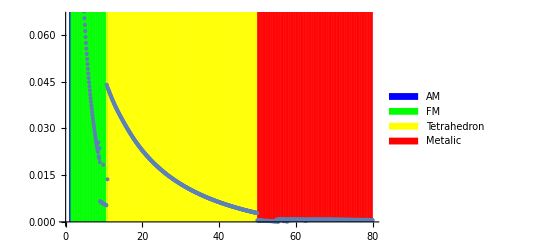

-Graphics-

#### θ-ϵ

```mathematica
order2=Table[(Ordering/@Transpose@{phase12["final"][[i]],phase24["final"][[i]],phase36["final"][[i]],phase48["final"][[i]],phase510["final"][[i]]})[[All,1]],{i,Length[phase12["thetalist"][[1]]]}];
```

```mathematica
Union@Flatten@order2
```

{1,2,3,4}

```mathematica
mingap2=Table[MapThread[#1[[#2]]&,{Transpose[{phase12["gap"][[i]],phase24["gap"][[i]],phase36["gap"][[i]],phase48["gap"][[i]],phase510["gap"][[i]]}],order2[[i]]}],{i,Length[phase12["thetalist"][[1]]]}];
```

```mathematica
minspin2=Table[MapThread[#1[[#2]]&,{Transpose[{phase12["spin"][[All,i]],phase24["spin"][[All,i]],phase36["spin"][[All,i]],phase48["spin"][[All,i]],phase510["spin"][[All,i]]}],order2[[i]]}],{i,Length[phase12["thetalist"][[1]]]}];
```

```mathematica
phase2=Table[{mingap2[[θ,i]]>2*^-3,AFQ[minspin2[[θ,i]]],FMWCQ[minspin2[[θ,i]]],FMNWCQ[minspin2[[θ,i]]],SpinlessQ[minspin2[[θ,i]]],TetraQ[minspin2[[θ,i]]],KagomeQ[minspin2[[θ,i]]]},{θ,Dimensions[mingap2][[1]]},{i,Dimensions[mingap2][[2]]}];
```

```mathematica
Union@Total[Boole[phase2[[All,All,2;;-1]]],{3}]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
Position[Total[Boole[phase2[[All,All,2;;-1]]],{3}],1]//Dimensions
```

{1680,2}

```mathematica
Position[phase2[[All,All,2;;-1]],{False,False,True,True,False,False}]
```

{{16,77},{16,78},{16,79},{16,80},{17,73},{17,74},{17,75},{17,80},{18,68},{18,80},{19,72},{20,65},{20,68},{21,55},{21,57}}

```mathematica
phase2[[17,68]]
```

{False,False,False,False,True,False,True}

```mathematica
phase2[[1,36]]
```

{False,False,False,True,True,False,False}

```mathematica
FMWCQ[minspin2[[1,32]]]
```

True

```mathematica
minspin2[[17,68]]//MatrixForm
```

(0.497151 | 0. | 0. | 0.116471
0.497151 | 0. | 0. | 0.116471
0.505444 | 0. | 0. | 0.134358
0.500255 | 0. | 0. | 0.0682545)

#### ??

```mathematica
minspin2[[15,80]]//MatrixForm
```

(0.497706 | 0. | 0. | 0.116591
0.497706 | 0. | 0. | 0.116591
0.498167 | 0. | 0. | 0.117557
0.506421 | 0. | 0. | 0.0848175)

```mathematica
minspin2[[20,58]]//MatrixForm
```

(0.502236 | 0. | 0. | 0.114565
0.502236 | 0. | 0. | 0.114565
0.497764 | 0. | 0. | 0.076546
0.497764 | 0. | 0. | 0.076546)

```mathematica
order2[[15,80]]
```

4

```mathematica
Union@Total[Boole[Select[Flatten[phase2,1],#[[1]]&][[All,2;;4]]],{2}]
```

{1}

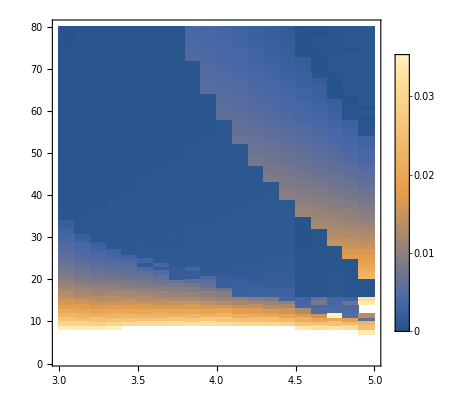

```mathematica
ListDensityPlot[Transpose@mingap2,DataRange->{phase12["thetalist"][[1,{1,-1}]],phase12["epsilonlist"][[1,{1,-1}]]},InterpolationOrder->0,PlotLegends->Automatic]
```

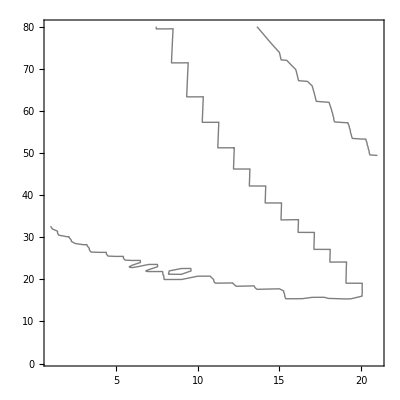

```mathematica
contour=ListContourPlot[Transpose@mingap2(*,DataRange->{phase12["thetalist"][[1,{1,-1}]],phase12["epsilonlist"][[1,{1,-1}]]}*),PlotLegends->Automatic,Contours->{2*^-3},ContourShading->None]
```

```mathematica
minspin2[[5,40]]
```

{{0.5,0.,0.,0.5},{0.5,0.,0.,0.5},{0.5,0.,0.,0.5},{0.5,0.,0.,0.5}}

```mathematica
phase12["spin"][[69,19]]//MatrixForm
```

(0.500324 | 0. | 0. | 0.0266356
0.500324 | 0. | 0. | -0.0266356
0.499676 | 0. | 0. | -0.00033469
0.499676 | 0. | 0. | 0.00033469)

```mathematica
match[bool_]:=Block[{},{True,True,False,False,False,False,False}]
```

```mathematica
match[{True,True,False,False,False,False,False}]={0,Blue,"AF-Insulator-WC"};
```

```mathematica
match[{True,False,True,False,False,False,False}]={1,Green,"FM-Insulator-WC"};
```

```mathematica
match[{False,False,False,True,False,False,False}]={2,LightBlue,"FM-Metallic-no WC"};
```

```mathematica
match[{False,False,False,False,True,False,False}]={3,Pink,"Spinless-Metallic-no WC"};
```

```mathematica
match[{True,False,False,False,False,True,False}]={4,Yellow,"Tetrahedron-Insulator-no WC"};
```

```mathematica
match[{False,False,False,False,False,True,False}]={5,LightYellow,"Tetrahedron-Metallic-no WC"};
```

```mathematica
match[{True,False,False,False,False,False,True}]={6,Orange,"Kagome-Insulator-WC"};
```

```mathematica
match[{False,False,False,False,False,False,True}]={7,LightOrange,"Kagome-Metallic-WC"};
```

```mathematica
match[x_]:={-1,Black,"Unassigned"};
```

```mathematica
phasediagram2=Table[If[phase2[[θ,i,5]],4,If[phase2[[θ,i,1]],Position[phase2[[θ,i,2;;-1]],True][[1,1]],0]],{θ,Dimensions[mingap2][[1]]},{i,Dimensions[mingap2][[2]]}];
```

```mathematica
phasediagram2=Table[match[phase2[[θ,i]]],{θ,Dimensions[mingap2][[1]]},{i,Dimensions[mingap2][[2]]}];
```

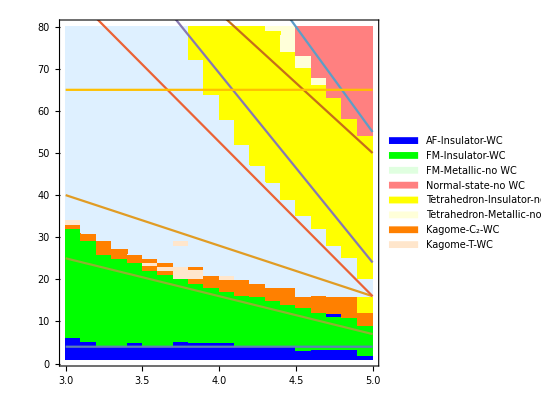

```mathematica
ListDensityPlot[Transpose[phasediagram2[[All,All,1]]],DataRange->{phase12["thetalist"][[1,{1,-1}]],phase12["epsilonlist"][[1,{1,-1}]]},InterpolationOrder->0,ColorFunction->(Piecewise[{{Blue,#==0},{Green,#==1},{LightBlue,#==2},{Pink,#==3},{Yellow,#==4},{LightYellow,#==5},{Orange,#==6},{LightOrange,#==7},{Black,#==-1}}]&),ColorFunctionScaling->False,PlotLegends->SwatchLegend[{Blue,Green,LightGreen,Pink,Yellow,LightYellow,Orange,LightOrange},{"AF-Insulator-WC","FM-Insulator-WC","FM-Metallic-no WC","Normal-state-no WC","Tetrahedron-Insulator-no WC","Tetrahedron-Metallic-no WC","Kagome-C_2-WC","Kagome-T-WC","Unassigned"}],Epilog->{(* First@contour*)First@Plot[{4,Rescale[x,{3,5},{40,16}],Rescale[x,{3,5},{25,7}],Rescale[x,{3.8,5},{60,16}],Rescale[x,{4.2,5},{60,24}],Rescale[x,{4.7,5},{60,50}],Rescale[x,{4.9,5},{60,55}],65},{x,3,5}]},PlotRangePadding->None]
```

```mathematica
Rescale[x,{1,20},{29,7}]
```

573/19-(22 x)/19

```mathematica
Rescale[x,{1,20},{35,16}]
```

36-x

```mathematica
minspin2[[1,40]]//MatrixForm
```

(0.5 | 0. | 0. | 0.5
0.5 | 0. | 0. | 0.5
0.5 | 0. | 0. | 0.5
0.5 | 0. | 0. | 0.5)

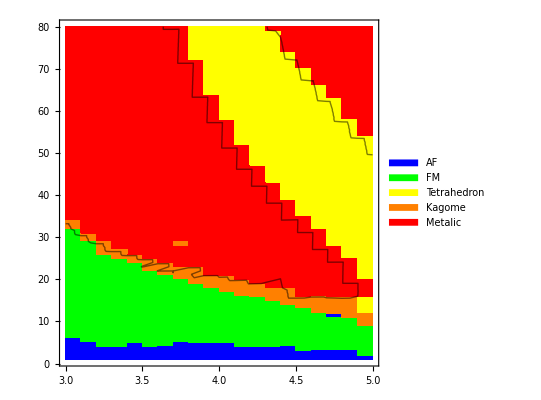

```mathematica
ListDensityPlot[Transpose@phasediagram2,DataRange->{phase12["thetalist"][[1,{1,-1}]],phase12["epsilonlist"][[1,{1,-1}]]},InterpolationOrder->0,ColorFunction->(Piecewise[{{Red,#==0},{Blue,#==1},{Green,#==2},{Yellow,#==3},{Orange,#==4}}]&),ColorFunctionScaling->False,PlotLegends->SwatchLegend[{Blue,Green,Yellow,Orange,Red},{"AF","FM","Tetrahedron","Kagome","Metalic"}],Epilog->{ First@contour},PlotRangePadding->None]
```

```mathematica
Boole[phase2]
```

{{{1,1,0,0,0,0,0},{1,1,0,0,0,0,0},{1,1,0,0,0,0,0},{1,1,0,0,0,0,0},{1,1,0,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},{1,0,1,0,0,0,0},36,{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0}},19,{1}}
 |  |  |  |

```mathematica
{phase12["epsilonlist"][[1]],phase12["thetalist"][[1]],phasediagram2}//Dimensions
```

{3}

```mathematica
phase12["epsilonlist"][[1]]//Length
```

80

```mathematica
phasediagram2//Dimensions
```

{21,80}

```mathematica
Flatten[Table[{phase12["epsilonlist"][[1,ϵ]],phase12["thetalist"][[1,θ]],phasediagram2[[θ,ϵ]]},{ϵ,Length[phase12["epsilonlist"][[1]]]},{θ,Length[phase12["thetalist"][[1]]]}],1]
```

{1680,3}

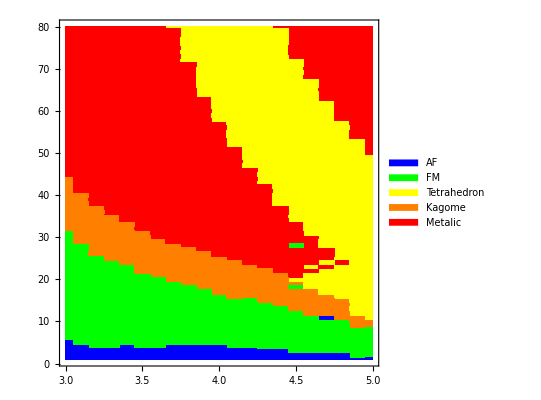

```mathematica
ListDensityPlot[Flatten[Table[{phase12["thetalist"][[1,θ]],phase12["epsilonlist"][[1,ϵ]],phasediagram2[[θ,ϵ]]},{ϵ,Length[phase12["epsilonlist"][[1]]]},{θ,Length[phase12["thetalist"][[1]]]}],1],InterpolationOrder->0,ColorFunction->(Piecewise[{{Red,#==0},{Blue,#==1},{Green,#==2},{Yellow,#==3},{Orange,#==4}}]&),ColorFunctionScaling->False,PlotLegends->SwatchLegend[{Blue,Green,Yellow,Orange,Red},{"AF","FM","Tetrahedron","Kagome","Metalic"}],PlotRangePadding->None]
```

```mathematica
|
```

```mathematica
Transpose[{phase12["epsilonlist"][[1]],phase12["thetalist"][[1]],phasediagram2}]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose[{{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.},{3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.},{{1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3},{1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3,3,3,3,3,3,3},{1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{1,1,1,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{1,1,1,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0},{1,1,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,2,4,3,0,0,0,0,0,0,0,2,0,0,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,0,0,0},{1,1,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,3,3,3,3,0,3,0,0,0,0,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,2,2,2,2,2,2,2,2,1,4,4,4,4,4,3,3,3,3,3,3,0,3,0,0,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,2,2,2,2,2,2,2,2,4,4,4,4,4,3,3,3,3,3,3,3,3,0,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,2,2,2,2,2,2,2,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,2,2,2,2,2,2,2,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}]

```mathematica
Transpose@phasediagram2//Dimensions
```

{80,21}

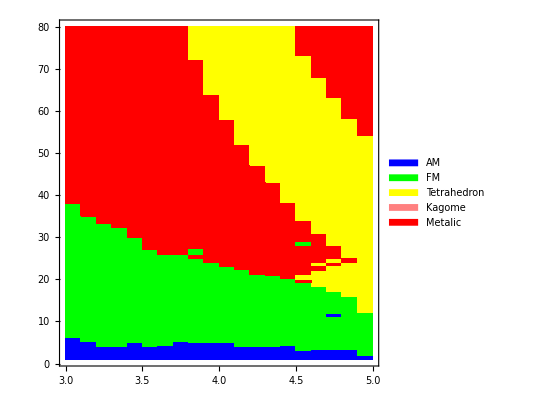

```mathematica
ListDensityPlot[Transpose@phasediagram2,DataRange->{phase12["thetalist"][[1,{1,-1}]],phase12["epsilonlist"][[1,{1,-1}]]},InterpolationOrder->0,ColorFunction->(Piecewise[{{Red,#==0},{Blue,#==1},{Green,#==2},{Yellow,#==3},{Pink,#==4}}]&),ColorFunctionScaling->False,PlotLegends->SwatchLegend[{Blue,Green,Yellow,Pink,Red},{"AM","FM","Tetrahedron","Kagome","Metalic"}]]
```

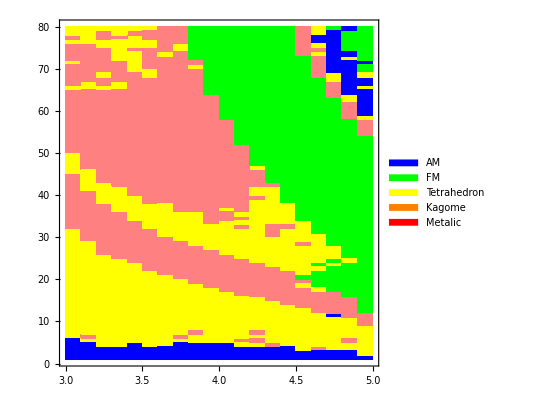

```mathematica
ListDensityPlot[Transpose@order2,DataRange->{phase12["thetalist"][[1,{1,-1}]],phase12["epsilonlist"][[1,{1,-1}]]},InterpolationOrder->0,ColorFunction->(Piecewise[{{Red,#==0},{Blue,#==1},{Green,#==2},{Yellow,#==3},{Pink,#==4}}]&),ColorFunctionScaling->False,PlotLegends->SwatchLegend[{Blue,Green,Yellow,Orange,Red},{"AM","FM","Tetrahedron","Kagome","Metalic"}]]
```

#### obsolete

```mathematica
second=(Ordering/@Transpose@{sweepnu12["final"][[-1]],sweepnu24["final"][[-1]],sweepnu36["final"][[-1]],sweepnu48["final"][[-1]]})[[All,2]]
```

{3,3,3,3,3,4,4,4,3,4,3,4,4,4,4,3,3,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,4,4,1,4,4,3,4,4,3,4,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,3,3,4,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,4,1,1,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,3,1,3,3,3,3,3,3,3,3,3,3,3,1,3,3,3,3,1,3,3,1,3,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,1,3,1,3,1,3,4,4,4,1,1,1,1,1,1,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2}

```mathematica
min=MapThread[#1[[#2]]&,{Transpose[{sweepnu12["final"][[-1]],sweepnu24["final"][[-1]],sweepnu36["final"][[-1]],sweepnu48["final"][[-1]]}],order}]*1000
```

{4842.94,4402.85,4036.1,3725.77,3459.76,3229.22,3027.48,2849.48,2691.24,2549.66,2422.23,2306.94,2202.12,2106.42,2018.68,1937.97,1863.46,1794.46,1730.4,1670.75,1615.07,1562.98,1514.15,1468.28,1425.1,1384.39,1345.94,1309.57,1275.11,1242.42,1211.36,1181.81,1153.67,1126.84,1101.23,1076.75,1053.34,1030.93,1009.45,988.84,969.058,950.051,931.775,914.188,897.251,880.931,865.192,850.006,835.343,821.177,807.482,794.236,781.418,769.006,756.981,745.326,734.025,723.06,712.417,702.083,692.044,682.288,672.802,663.576,654.599,645.861,637.353,629.066,620.992,613.121,605.447,597.963,590.661,583.535,576.578,569.78,563.15,556.667,550.306,544.138,538.074,532.144,526.342,520.666,515.11,509.671,504.345,499.129,493.998,489.012,484.106,479.296,474.581,469.958,465.423,460.975,456.61,452.326,448.12,443.984,439.938,435.957,432.047,428.207,424.434,420.726,417.082,413.501,409.98,406.518,403.114,399.766,396.472,393.233,390.045,386.909,383.822,380.784,377.793,374.848,371.949,369.094,366.282,363.513,360.784,358.096,355.448,352.838,350.266,347.731,345.232,342.768,340.339,337.944,335.582,333.253,330.956,328.69,326.454,324.248,322.072,319.925,317.805,315.714,313.649,311.611,309.599,307.613,305.652,303.715,301.803,299.914,298.049,296.207,294.387,292.588,290.812,289.057,287.323,285.609,283.915,282.241,280.587,278.951,277.334,275.736,274.156,272.594,271.049,269.522,268.011,266.517,265.04,263.578,262.133,260.703,259.288,257.888,256.504,255.134,253.778,252.437,251.109,249.795,248.495,247.208,245.934,244.673,243.425,242.189,240.965,239.754,238.555,237.367,236.191,235.027,233.874,232.732,231.6,230.48,229.37,228.271,227.182,226.104,225.035,223.977,222.928,221.888,220.859,219.838,218.827,217.825,216.832,215.848,214.873,213.906,212.948,211.998,211.057,210.124,209.199,208.281,207.372,206.471,205.577,204.691,203.812,202.941,202.077,201.22,200.37,199.528,198.692,197.863,197.041,196.226,195.417,194.615,193.819,193.029,192.246,191.469,190.699,189.934,189.175,188.423,187.676,186.935,186.199,185.47,184.745,184.027,183.314,182.606,181.904,181.207,180.515,179.828,179.147,178.47,177.799,177.132,176.47,175.814,175.162,174.514,173.872,173.234,172.6,171.971,171.347,170.727,170.111,169.5,168.893,168.29,167.691,167.097,166.507,165.92,165.338,164.76,164.186,163.616,163.049,162.486,161.928,161.372,160.821,160.273,159.729,159.189,158.652,158.118,157.589,157.062,156.539,156.02,155.503,154.99,154.481,153.974,153.471,152.971,152.475,151.981,151.491,151.003,150.519,150.038,149.559,149.084,148.612,148.142,147.676,147.212,146.751,146.293,145.838,145.385,144.935,144.488,144.044,143.602,143.163,142.726,142.292,141.861,141.432,141.006,140.582,140.161,139.742,139.325,138.911,138.5,138.091,137.684,137.279,136.877,136.477,136.079,135.684,135.29,134.899,134.511,134.124,133.74,133.357,132.977,132.599,132.223,131.849,131.477,131.107,130.739,130.373,130.01,129.648,129.288,128.93,128.574,128.22,127.867,127.517,127.168,126.822,126.477,126.134,125.793,125.453,125.115,124.78,124.445,124.113,123.782,123.453,123.126,122.8,122.476,122.154,121.833,121.514,121.197,120.881,120.567,120.254,119.943,119.634,119.326,119.019,118.715,118.411,118.109,117.809,117.51,117.212,116.916,116.622,116.329,116.037,115.747,115.458,115.17,114.884,114.6,114.316,114.034,113.754,113.474,113.196,112.92,112.644,112.37,112.097,111.826,111.556,111.287,111.019,110.752,110.487,110.223,109.96,109.699,109.438,109.179,108.921,108.664,108.408,108.154,107.901,107.648,107.397,107.147,106.898,106.651,106.404,106.159,105.914,105.671,105.429,105.187,104.947,104.708,104.47,104.233,103.997,103.762,103.528,103.296,103.064,102.833,102.603,102.374,102.146,101.919,101.693,101.468,101.244,101.021,100.799,100.578,100.358,100.138,99.9199,99.7024,99.4858,99.2701,99.0553,98.8414,98.6284,98.4163,98.2051,97.9947,97.7852,97.5766,97.3688,97.1618,96.9558,96.7505,96.5461,96.3425,96.1397,95.9378,95.7367,95.5363,95.3368,95.1381,94.9402,94.7431,94.5463,94.3497,94.1539,93.9588,93.7645,93.571,93.3782,93.1862,92.995,92.8045,92.6147,92.4257,92.2374,92.0499,91.8631,91.677,91.4916,91.3069,91.123,90.9398,90.7573,90.5755,90.3944,90.214,90.0343,89.8552,89.6769,89.4992,89.3222,89.1458,88.9701,88.795,88.6207,88.447,88.274,88.1015,87.9298,87.7586,87.5881,87.4183,87.2491,87.0804,86.9125,86.7451,86.5783,86.4122,86.2467,86.0817,85.9174,85.7537,85.5637,85.4104,85.2484,85.0967,84.9358,84.7564,84.6061,84.4376,84.279,84.121,83.9635,83.8067,83.6503,83.4946,83.3394,83.1847,83.0306,82.877,82.7338,82.5715,82.4195,82.2681,82.1172,81.9767,81.817,81.6677,81.5288,81.3706,81.2329,81.0755,80.9288,80.7824,80.6368,80.4915,80.3467,80.2024,80.0592,79.9153,79.7726,79.6303,79.4884,79.3472,79.2063,79.0658,78.926,78.7866,78.6476,78.5091,78.371,78.2334,78.0963,77.9596,77.8234,77.6876,77.5523,77.4174,77.283,77.149,77.0155,76.8824,76.7497,76.6175,76.4857,76.3543,76.2233,76.0928,75.9626,75.8329,75.7038,75.5749,75.4465,75.3185,75.1909,75.0711,74.937,74.8106,74.692,74.5665,74.4339,74.3091,74.1848,74.0607,73.9371,73.814,73.6912,73.5688,73.4467,73.3251,73.2038,73.0829,72.9624,72.8422,72.7224,72.6031,72.484,72.3654,72.2471,72.1291,72.0117,71.8944,71.7776,71.6611,71.545,71.4292,71.3138,71.1988,71.084,70.9698,70.8557,70.742,70.6287,70.5157,70.4031,70.2908,70.1789,70.0673,69.956,69.845,69.7344,69.6242,69.5142,69.4046,69.2952,69.1863,69.0777,68.9693,68.8613,68.7536,68.6462,68.5391,68.4324,68.326,68.2199,68.114,68.0086,67.9034,67.7985,67.6939,67.5896,67.4857,67.382,67.2786,67.1756,67.0728,66.9703,66.8681,66.7662,66.6646,66.5633,66.4623,66.3616,66.2611,66.161,66.0612,65.9615,65.8622,65.7632,65.6645,65.566,65.4678,65.3699,65.2723,65.1749,65.0779,64.981,64.8845,64.7882,64.6922,64.5965,64.501,64.4058,64.3109,64.2162,64.1218,64.0276,63.9337,63.8401,63.7467,63.6536,63.5607,63.4681,63.3758,63.2837,63.1918,63.1002,63.0088,62.9177,62.8269,62.7363,62.6459,62.5558,62.4659,62.3762,62.2869,62.1977,62.1088,62.0201,61.9316,61.8435,61.7555,61.6677,61.5802,61.493,61.4059,61.3191,61.2326,61.1462,61.0601,60.9742,60.8885,60.8031,60.7179,60.6329,60.5481,60.4636,60.3792,60.2951,60.2112,60.1276,60.0441,59.9609,59.8779,59.7951,59.7125,59.6301,59.5479,59.466,59.3842,59.3027,59.2214,59.1403,59.0594,58.9787,58.8982,58.8179,58.7378,58.6579,58.5783,58.4988,58.4195,58.3404,58.2616,58.1829,58.1044,58.0261,57.9481,57.8702,57.7925,57.715,57.6377,57.5607}

```mathematica
min2=MapThread[#1[[#2]]&,{Transpose[{sweepnu12["final"][[-1]],sweepnu24["final"][[-1]],sweepnu36["final"][[-1]],sweepnu48["final"][[-1]]}],second}]*1000
```

{4842.94,4402.86,4036.11,3725.77,3459.76,3229.22,3027.48,2849.48,2691.24,2549.66,2422.23,2306.94,2202.12,2106.42,2018.68,1937.97,1863.46,1794.46,1730.4,1670.75,1615.07,1562.98,1514.15,1468.28,1425.1,1384.39,1345.94,1309.57,1275.11,1242.42,1211.36,1181.81,1153.67,1126.84,1101.23,1076.75,1053.34,1030.93,1009.45,988.84,969.058,950.051,931.775,914.188,897.251,880.931,865.192,850.006,835.343,821.177,807.482,794.236,781.418,769.078,757.052,745.396,734.093,723.127,712.483,702.147,692.106,682.348,672.86,663.632,654.654,645.914,637.404,629.115,621.038,613.161,605.479,597.987,590.699,583.544,576.58,569.785,563.174,556.683,550.331,544.138,538.082,532.159,526.365,520.694,515.135,509.694,504.366,499.148,494.036,489.027,484.119,479.307,474.59,469.964,465.428,460.977,456.611,452.327,448.123,443.991,439.945,435.966,432.059,428.209,424.449,420.743,417.101,413.521,410.002,406.542,403.132,399.794,396.503,393.265,390.073,386.945,383.86,380.818,377.835,374.887,371.989,369.136,366.331,363.564,360.833,358.147,355.5,352.892,350.322,347.789,345.292,342.834,340.404,338.014,335.654,333.326,331.031,328.764,326.533,324.329,322.154,320.006,317.891,315.802,313.739,311.703,309.693,307.708,305.749,303.814,301.904,300.01,298.147,296.306,294.488,292.691,290.917,289.163,287.43,285.718,284.024,282.351,280.697,279.062,277.421,275.823,274.243,272.682,271.138,269.611,268.101,266.608,265.131,263.671,262.226,260.797,259.383,257.984,256.6,255.231,253.864,252.523,251.197,249.884,248.584,247.298,246.014,244.754,243.506,242.272,241.049,239.839,238.64,237.454,236.279,235.115,233.963,232.822,231.692,230.573,229.464,228.366,227.278,226.201,225.133,224.076,223.028,221.99,220.962,219.942,218.871,217.871,216.879,215.894,214.92,213.955,212.998,212.113,211.172,210.241,209.317,208.401,207.493,206.593,205.701,204.816,203.938,203.007,202.144,201.287,200.439,199.597,198.763,197.936,197.115,196.301,195.494,194.693,193.899,193.111,192.33,191.554,190.786,190.023,189.266,188.515,187.767,187.028,186.296,185.568,184.845,184.128,183.416,182.71,182.009,181.314,180.624,179.938,179.259,178.584,177.914,177.249,176.589,175.933,175.283,174.637,173.996,173.36,172.728,172.1,171.477,170.859,170.244,169.632,169.025,168.422,167.822,167.228,166.637,166.05,165.467,164.888,164.314,163.743,163.176,162.613,162.053,161.498,160.946,160.397,159.853,159.312,158.774,158.24,157.71,157.183,156.66,156.139,155.623,155.109,154.599,154.092,153.589,153.088,152.591,152.097,151.606,151.118,150.633,150.151,149.673,149.197,148.724,148.254,147.787,147.323,146.861,146.403,145.947,145.494,145.044,144.596,144.151,143.709,143.269,142.832,142.398,141.966,141.537,141.11,140.686,140.264,139.845,139.428,139.013,138.601,138.192,137.784,137.379,136.976,136.576,136.178,135.782,135.388,134.997,134.608,134.221,133.836,133.453,133.072,132.694,132.317,131.943,131.571,131.2,130.832,130.466,130.101,129.739,129.379,129.02,128.664,128.309,127.957,127.606,127.257,126.91,126.565,126.221,125.88,125.54,125.202,124.865,124.531,124.198,123.867,123.538,123.21,122.884,122.56,122.237,121.916,121.597,121.279,120.963,120.648,120.335,120.024,119.714,119.405,119.099,118.793,118.49,118.187,117.887,117.587,117.29,116.993,116.698,116.405,116.113,115.822,115.533,115.245,114.959,114.674,114.39,114.108,113.827,113.547,113.269,112.992,112.716,112.442,112.168,111.897,111.626,111.357,111.089,110.822,110.556,110.292,110.029,109.767,109.506,109.247,108.988,108.731,108.475,108.221,107.967,107.714,107.463,107.213,106.964,106.716,106.469,106.223,105.978,105.735,105.492,105.251,105.01,104.771,104.533,104.295,104.059,103.824,103.59,103.357,103.124,102.893,102.663,102.434,102.206,101.979,101.753,101.527,101.303,101.057,100.834,100.636,100.415,100.186,99.9669,99.7484,99.5311,99.3144,99.0802,98.8651,98.6509,98.4377,98.2252,98.0136,97.8029,97.5931,97.384,97.1761,96.9688,96.7624,96.5567,96.3519,96.148,95.9451,95.7428,95.5413,95.3408,95.141,94.942,94.7438,94.5467,94.3512,94.1564,93.9624,93.7691,93.5766,93.3849,93.1939,93.0037,92.8142,92.6255,92.4375,92.2502,92.0637,91.8778,91.6927,91.5083,91.3247,91.1417,90.9594,90.7779,90.597,90.4168,90.2373,90.0578,89.8789,89.7006,89.5231,89.3462,89.1685,88.9922,88.818,88.6423,88.4687,88.2958,88.1235,87.9518,87.7808,87.6104,87.4407,87.2716,87.1039,86.936,86.7688,86.6021,86.4361,86.2707,86.1059,85.9417,85.7781,85.573,85.4279,85.2661,85.1047,84.9439,84.7756,84.614,84.447,84.2885,84.1348,83.983,83.8262,83.6699,83.5082,83.3534,83.1984,83.0443,82.8868,82.74,82.5813,82.4294,82.278,82.1271,81.9846,81.8269,81.6776,81.5367,81.3807,81.2391,81.0857,80.9388,80.7891,80.6433,80.4981,80.3534,80.2091,80.0654,79.9221,79.7794,79.6371,79.4953,79.3539,79.2132,79.0728,78.9329,78.7934,78.6545,78.516,78.378,78.2404,78.1033,77.9685,77.8323,77.6966,77.5593,77.4244,77.29,77.1562,77.0226,76.8895,76.7605,76.6283,76.4928,76.3614,76.2305,76.1,75.9699,75.8403,75.711,75.5822,75.4538,75.3258,75.1983,75.0712,74.9443,74.818,74.6921,74.5666,74.4413,74.3166,74.1922,74.0682,73.9447,73.8215,73.6987,73.5763,73.4543,73.3327,73.2114,73.0905,72.9624,72.8499,72.7225,72.6108,72.4841,72.3731,72.2549,72.137,72.0194,71.8945,71.7777,71.6612,71.5451,71.4292,71.3138,71.1988,71.0842,70.9777,70.8637,70.742,70.6288,70.5159,70.4032,70.2909,70.179,70.0673,69.9561,69.8451,69.7345,69.6242,69.5143,69.4047,69.2953,69.1864,69.0777,68.9693,68.8614,68.7536,68.6462,68.5392,68.4325,68.326,68.22,68.1142,68.0087,67.9035,67.7986,67.694,67.5896,67.4857,67.3821,67.2787,67.1757,67.0729,66.9704,66.8681,66.7662,66.6647,66.5633,66.4624,66.3617,66.2612,66.161,66.0612,65.9616,65.8623,65.7633,65.6645,65.5661,65.4679,65.3699,65.2724,65.175,65.0779,64.9811,64.8846,64.7883,64.6923,64.5966,64.5011,64.4058,64.3109,64.2163,64.1219,64.0277,63.9338,63.8402,63.7467,63.6536,63.5607,63.4681,63.3758,63.2838,63.1919,63.1003,63.0089,62.9178,62.827,62.7364,62.6459,62.5559,62.466,62.3763,62.2872,62.1978,62.1089,62.0202,61.9317,61.8435,61.7556,61.6678,61.5803,61.4931,61.406,61.3192,61.2326,61.1463,61.0602,60.9743,60.8886,60.8032,60.718,60.633,60.5482,60.4636,60.3793,60.2951,60.2113,60.1277,60.0442,59.961,59.8779,59.7951,59.7126,59.6301,59.548,59.466,59.3843,59.3028,59.2215,59.1404,59.0595,58.9787,58.8983,58.8179,58.7379,58.658,58.5783,58.4989,58.4196,58.3405,58.2616,58.183,58.1044,58.0262,57.9482,57.8703,57.7926,57.7151,57.6378,57.5613}

```mathematica
diff=min2-min;
```

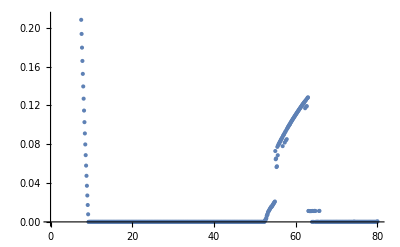

```mathematica
ListPlot[sweepnu24["final"][[-1]]*1000-min,DataRange->sweepnu12["epsilonlist"][[1,{1,-1}]]]
```

```mathematica
0.1*8.6*^-5*1000
```

0.0086

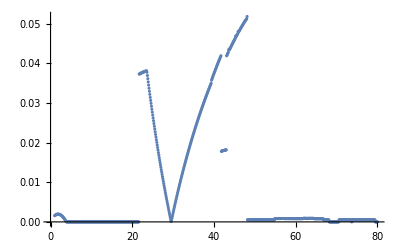

```mathematica
ListPlot[diff,DataRange->sweepnu12["epsilonlist"][[1,{1,-1}]]]
```

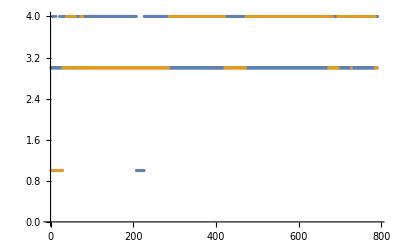

```mathematica
ListPlot[{second,order}(*,PlotRange->{{0,300},Automatic}*)]
```

```mathematica
diff[[208]]
```

0.0372781

```mathematica
Position[Differences[order],_?(#≠0&)]
```

{{29},{37},{38},{39},{40},{44},{45},{48},{49},{50},{51},{54},{57},{59},{60},{72},{74},{76},{77},{286},{421},{472},{672},{675},{676},{681},{682},{694},{695},{696},{727},{728},{785}}

```mathematica
min[[30]]
```

456.144

```mathematica
second[[209]]
```

1

```mathematica
order[[209]]
```

3

```mathematica
diff[[31]]
```

3.41061×10^-13

```mathematica
sweepnu36["spin"]//Dimensions
```

{791,20,4,4}

```mathematica
sweepnu36["spin"][[30,-1]]//MatrixForm
```

(0.989895 | 0. | 0. | 0.989895
0.989895 | 0. | 0. | 0.989895
0.0101055 | 0. | 0. | 0.0101055
0.0101055 | 0. | 0. | 0.0101055)

```mathematica
sweepnu12["spin"][[209,-1]]//MatrixForm
```

(0.904882 | 0. | 0. | 0.901633
0.904882 | 0. | 0. | -0.901633
0.0951178 | 0. | 0. | -6.99095×10^-15
0.0951178 | 0. | 0. | 6.84095×10^-15)

```mathematica
sweepnu36["final"][[-1,30]]*1000
```

456.144

```mathematica
sweepnu36["spin"][[291,-1]]//MatrixForm
```

(0.59144 | 0. | 0. | 0.52128
0.59144 | 0. | 0. | 0.52128
0.40856 | 0. | 0. | 0.23872
0.40856 | 0. | 0. | 0.23872)

```mathematica
sweepnu12["gap"][[-1,291]]*1000
```

6.07373

```mathematica
With[{i=291},NumberForm[{sweepnu12["final"][[-1,i]],sweepnu24["final"][[-1,i]],sweepnu36["final"][[-1,i]],sweepnu48["final"][[-1,i]]}*1000,10]]
```

{159.8527637,45.40349913,160.1172878,159.8932103}

```mathematica
With[{i=291},NumberForm[{sweepnu12["gap"][[-1,i]],sweepnu24["gap"][[-1,i]],sweepnu36["gap"][[-1,i]],sweepnu48["gap"][[-1,i]]}*1000,10]]
```

{6.073733688,8.679248747,0.1242154268,0.1886334649}

```mathematica
With[{i=291},NumberForm[{sweepnu12["innergap"][[-1,i]],sweepnu24["innergap"][[-1,i]],sweepnu36["innergap"][[-1,i]],sweepnu48["innergap"][[-1,i]]}*1000,10]]
```

{0.01968059573,0.04419809883,0.0813810915,0.01981825993}

```mathematica
With[{i=291},NumberForm[{sweepnu12["finali"][[-1,i]],sweepnu24["finali"][[-1,i]],sweepnu36["finali"][[-1,i]],sweepnu48["finali"][[-1,i]]},10]]
```

{22.,11.,33.,80.}

```mathematica
NumberForm[{sweepnu12["gap"][[-1,40]],sweepnu12tetra["gap"][[-1,40]],sweepnu36["gap"][[-1,40]],sweepnu48["gap"][[-1,40]]}*1000,10]
```

{13.30337928,11.46474958,7.953968225,7.953961412}

```mathematica
sweepnu12["dlist"][[1,-1]]
```

10.

```mathematica
sweepnu12["epsilonlist"][[1,291]]
```

30.

```mathematica
Transpose@{order
```

```mathematica
ColorData["TemperatureMap"][Rescale[#,{0,15},{0,1}]]&[16]
```

RGBColor[0.817319, 0.134127, 0.164218]

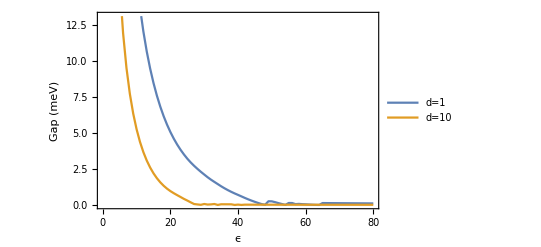

```mathematica
ListLinePlot[{1000sweepnu12["gap"][[-1]],1000sweepnu12["gap"][[1]]},DataRange->sweepnu12["epsilonlist"][[1,{1,-1}]],FrameLabel->{"ϵ","Gap (meV)"},PlotRangePadding->None,BaseStyle->(FontSize->16),Frame->True,PlotLegends->Placed[{"d=1","d=10"},Scaled[{.8,.5}]]]
```

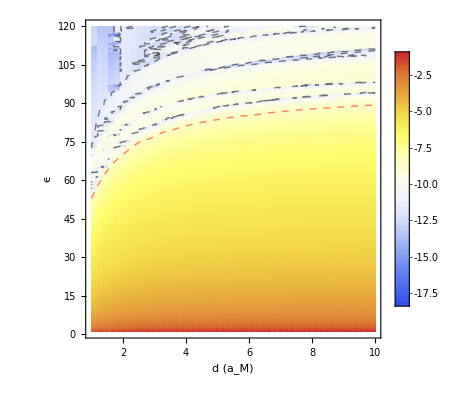

```mathematica
ListDensityPlot[Transpose@Log@sweepnu12["gap"],DataRange->{sweepnu12["dlist"][[1,{1,-1}]],sweepnu12["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

```mathematica
sweepnu12["final"][[10,10]]*1000
```

46.7335

```mathematica
sweepnu12tetra["final"][[10,10]]*1000
```

46.7851

```mathematica
sweepnu12tetra["spin"][[50,2]]//MatrixForm
```

(0.499991 | 0.00298509 | 0.00193563 | 0.00166487
0.49999 | 0.00299626 | -0.00157215 | -0.00122812
0.500009 | 0.00141963 | 0.00192478 | -0.00119953
0.500009 | 0.00141438 | -0.0015547 | 0.00164427)

```mathematica
sweepnu12tetra["spin"][[49,2]]//MatrixForm
```

(0.5 | 0.139697 | 0.139697 | 0.139697
0.5 | 0.139697 | -0.139697 | -0.139697
0.5 | -0.139697 | 0.139697 | -0.139697
0.5 | -0.139697 | -0.139697 | 0.139697)

```mathematica
sweepnu12tetra["spin"][[48,2]]//MatrixForm
```

(0.5 | 0.14241 | 0.14241 | 0.14241
0.5 | 0.14241 | -0.14241 | -0.14241
0.5 | -0.14241 | 0.14241 | -0.14241
0.5 | -0.14241 | -0.14241 | 0.14241)

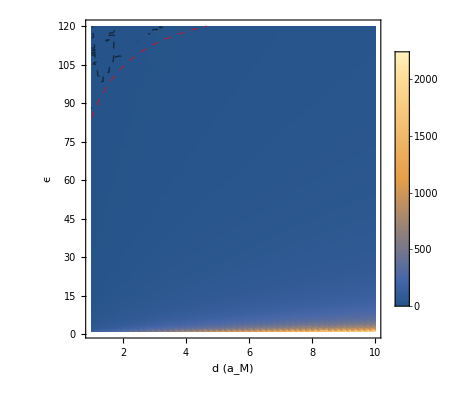

```mathematica
ListDensityPlot[1000Transpose@sweepnu12tetra["final"],DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},(*ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,15},{0,1}]]&),ColorFunctionScaling->False,*)PlotRangePadding->None,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},BaseStyle->(FontSize->16),Epilog->{ First@contourtetra}]
```

```mathematica
Transpose@sweepnu12["final"]//Dimensions
```

{240,50}

```mathematica
energy12=ListInterpolation[1000sweepnu12["final"],{sweepnu12["dlist"][[1,{1,-1}]],sweepnu12["epsilonlist"][[1,{1,-1}]]}]
```

InterpolatingFunction[…]

```mathematica
energy12tetra=ListInterpolation[1000sweepnu12tetra["final"],{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]}]
```

InterpolatingFunction[…]

```mathematica
energy612=ListInterpolation[1000sweepnu612["final"],{sweepnu612["dlist"][[1,{1,-1}]],sweepnu612["epsilonlist"][[1,{1,-1}]]}]
```

InterpolatingFunction[…]

```mathematica
energy1224=ListInterpolation[1000sweepnu1224["final"],{sweepnu1224["dlist"][[1,{1,-1}]],sweepnu1224["epsilonlist"][[1,{1,-1}]]}]
```

InterpolatingFunction[…]

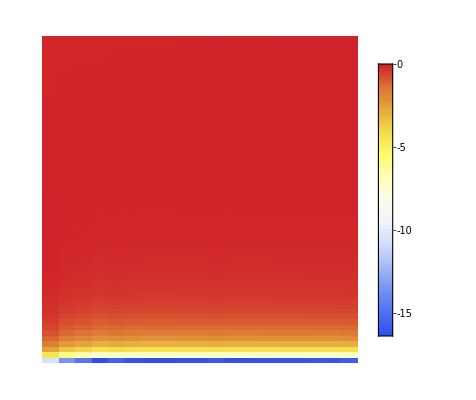

```mathematica
ArrayPlot[Reverse@Transpose@Table[energy12[i,j]-energy12tetra[i,j],{i,1,10,0.5},{j,1,60}],AspectRatio->1,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameTicks->True]
```

```mathematica
ArrayPlot[Reverse@Transpose[Table[Ordering[{energy12[i,j],energy12tetra[i,j](*,energy612[i,j],energy1224[i,j]*)}][[1]],{i,1,10,.1},{j,1,60,.1}]],AspectRatio->1,PlotLegends->{"180AF","Tetrahedron","hexagon"},FrameTicks->All]
```

-Graphics-

```mathematica
Transpose[Table[Ordering[{energy12[i,j],energy12tetra[i,j],energy612[i,j],energy1224[i,j]}][[1]],{i,1,10},{j,1,60}]]
```

{{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{4,3,3,3,3,3,3,3,3,3},{4,3,3,3,3,3,3,3,3,3},{4,3,3,3,3,3,3,3,3,3},{4,3,3,3,3,3,3,3,3,3},{4,3,3,3,3,3,3,3,3,3},{4,3,3,3,3,3,3,3,3,3},{4,3,3,3,3,3,3,3,3,3},{4,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3},{3,3,3,3,3,3,3,3,3,3}}

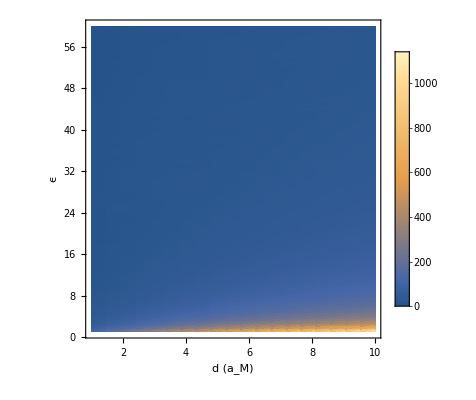

```mathematica
ListDensityPlot[1000Transpose@sweepnu612["final"],DataRange->{sweepnu612["dlist"][[1,{1,-1}]],sweepnu612["epsilonlist"][[1,{1,-1}]]},(*ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,15},{0,1}]]&),ColorFunctionScaling->False,*)PlotRangePadding->None,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},BaseStyle->(FontSize->16),Epilog->{ First@contourtetra}]
```

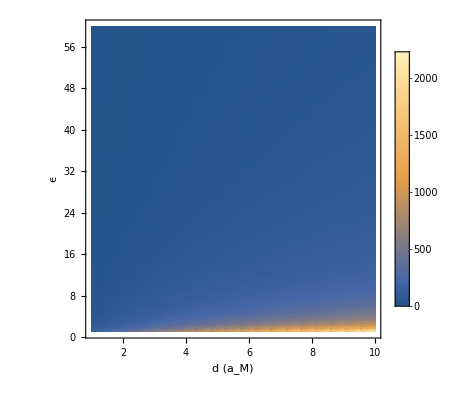

```mathematica
ListDensityPlot[1000Transpose@sweepnu1224["final"],DataRange->{sweepnu1224["dlist"][[1,{1,-1}]],sweepnu1224["epsilonlist"][[1,{1,-1}]]},(*ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,15},{0,1}]]&),ColorFunctionScaling->False,*)PlotRangePadding->None,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},BaseStyle->(FontSize->16),Epilog->{ First@contourtetra}]
```

```mathematica
Reverse[Subdivide[1,80.,159]][[100]]
```

30.8113

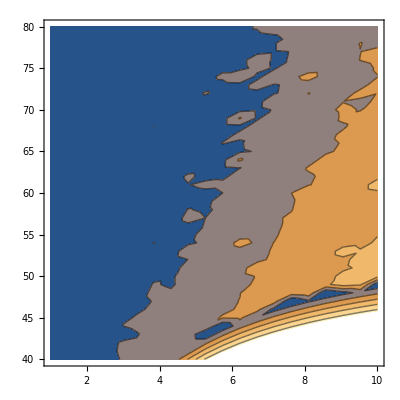

```mathematica
ListContourPlot[1000Transpose[GaussianFilter[sweepnu12tetra["gap"][[All,120;;-1]],.0]],DataRange->{{1,10},{40,80}}(*,Contours->{.01,0.2}*)(*,ContourShading->None*)]
```

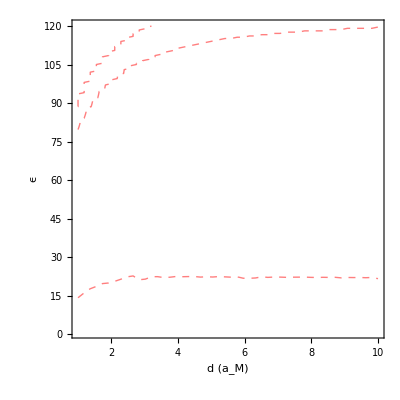

```mathematica
contourdifffinal=ListContourPlot[1000(Transpose@sweepnu12tetra["final"]-Transpose@sweepnu12["final"]),DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{0},ContourShading->None,ContourStyle->Directive[{Thick,Dashed,Red}]]
```

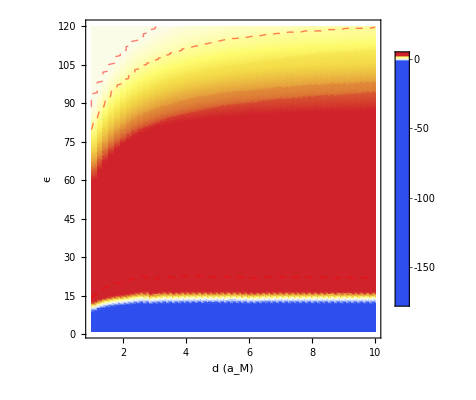

```mathematica
ListDensityPlot[1000Transpose@sweepnu12tetra["gap"]-1000Transpose@sweepnu12["gap"],DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-2,2},{0,1}]]&),PlotRange->Full,PlotRangePadding->None,ColorFunctionScaling->False,PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},BaseStyle->(FontSize->16),Epilog->{(*First@contour, First@contourtetra,*)First@contourdifffinal}]
```

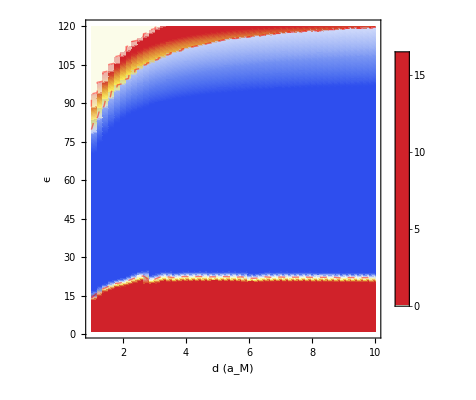

```mathematica
ListDensityPlot[1000Transpose@sweepnu12tetra["final"]-1000Transpose@sweepnu12["final"],DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-0.02,0.02},{0,1}]]&),PlotRange->Full,PlotRangePadding->None,ColorFunctionScaling->False,PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},BaseStyle->(FontSize->16),Epilog->{(*First@contour, First@contourtetra,*)First@contourdifffinal}]
```

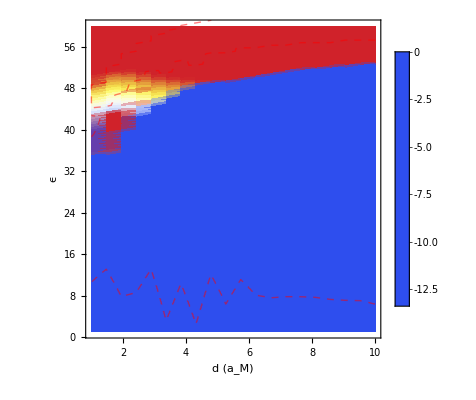

```mathematica
ListDensityPlot[1000Transpose@sweepnu1224["final"]-1000Transpose@sweepnu12tetra["final"],DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-0.02,0.02},{0,1}]]&),PlotRange->Full,PlotRangePadding->None,ColorFunctionScaling->False,PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},BaseStyle->(FontSize->16),Epilog->{(*First@contour, First@contourtetra,*)First@contourdifffinal}]
```

```mathematica
sweepnu12["epsilonlist"][[1,40]]
```

20.3774

```mathematica
sweepnu12["gap"][[20,40]]
```

0.00367376

```mathematica
sweepnu12tetra["final"][[20,40]]
```

0.0473545

```mathematica
sweepnu12["spin"][[40,20]]//MatrixForm
```

(0.703506 | 0. | 0. | 0.632884
0.703506 | 0. | 0. | -0.632884
0.296494 | 0. | 0. | -8.81104×10^-15
0.296494 | 0. | 0. | 8.97669×10^-15)

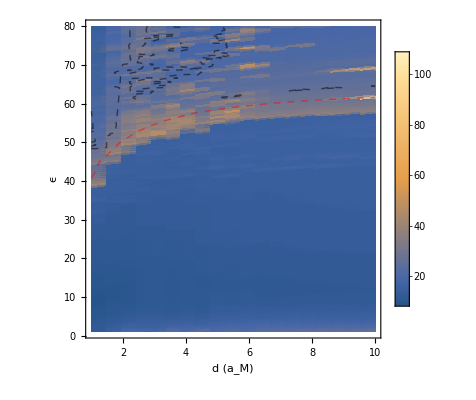

```mathematica
ListDensityPlot[Transpose@sweepnu12["finali"],DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},(*ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,15},{0,1}]]&),ColorFunctionScaling->False,*)PlotRangePadding->None,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},BaseStyle->(FontSize->16),Epilog->{ First@contourtetra}]
```

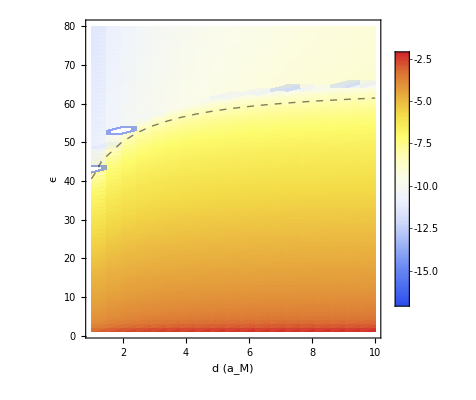

```mathematica
ListDensityPlot[Transpose@Log@sweepnu12tetra["gap"],DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contourtetra}]
```

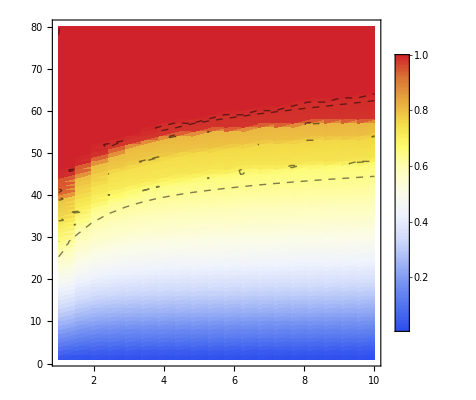

```mathematica
ListDensityPlot[Table[wig[sweepnu12["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu12["spin"]][[1]]},{j,Dimensions[sweepnu12["spin"]][[2]]}],DataRange->{sweepnu12["dlist"][[1,{1,-1}]],sweepnu12["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRangePadding->None,BaseStyle->(FontSize->16),Epilog->{ First@contour}]
```

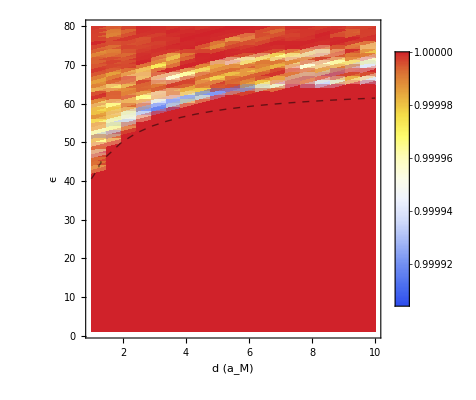

```mathematica
ListDensityPlot[Table[wig[sweepnu12tetra["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu12tetra["spin"]][[1]]},{j,Dimensions[sweepnu12tetra["spin"]][[2]]}],DataRange->{sweepnu12tetra["dlist"][[1,{1,-1}]],sweepnu12tetra["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},PlotRange->Full,Epilog->{ First@contourtetra}]
```

### Sweep_nu=[6,12] AF

```mathematica
sweepnu612=importmat[NotebookDirectory[]<>"nu6,12_U110.mat"];
```

```mathematica
sweepnu612["gap"]//Dimensions
```

{20,30}

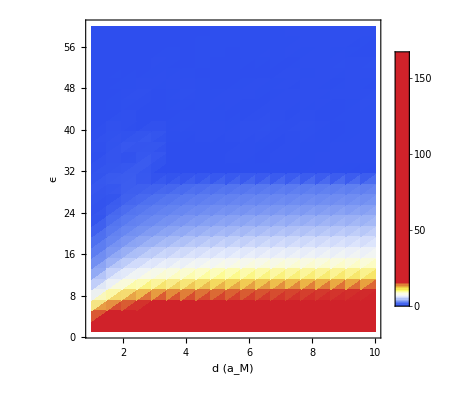

```mathematica
ListDensityPlot[1000Transpose@sweepnu612["gap"],DataRange->{sweepnu612["dlist"][[1,{1,-1}]],sweepnu612["epsilonlist"][[1,{1,-1}]]},ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,15},{0,1}]]&),ColorFunctionScaling->False,PlotRangePadding->None,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},BaseStyle->(FontSize->16)(*,Epilog->{ First@contourtetra}*)]
```

### Sweep_nu=[1,3]

```mathematica
sweepnu13=importmat[NotebookDirectory[]<>"nu1,3_U110.mat"];
```

```mathematica
contour=ListContourPlot[1000Transpose@sweepnu13["gap"],DataRange->{sweepnu13["dlist"][[1,{1,-1}]],sweepnu13["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{.25},ContourShading->None,ContourStyle->Directive[{Thick,Dashed}]];
```

```mathematica
sweepnu13gapline=Table[Block[{data=sweepnu13,thres=.2,last,slice,fint},slice=Tanh[(data["innergap"]/data["gap"])[[i]]];last=FirstPosition[slice,_?(#>thres&)][[1]];fint=Interpolation[Transpose@{slice[[1;;last]],data["epsilonlist"][[1,1;;last]]}];{data["dlist"][[1,i]],fint[thres]}],{i,20}]
```

{{1.,11.2372},{1.47368,13.814},{1.94737,15.4039},{2.42105,16.4272},{2.89474,17.1451},{3.36842,17.65},{3.84211,18.0537},{4.31579,18.3402},{4.78947,18.6068},{5.26316,18.8054},{5.73684,18.9894},{6.21053,19.1357},{6.68421,19.2601},{7.15789,19.3733},{7.63158,19.4838},{8.10526,19.5739},{8.57895,19.6506},{9.05263,19.7239},{9.52632,19.7884},{10.,19.8562}}

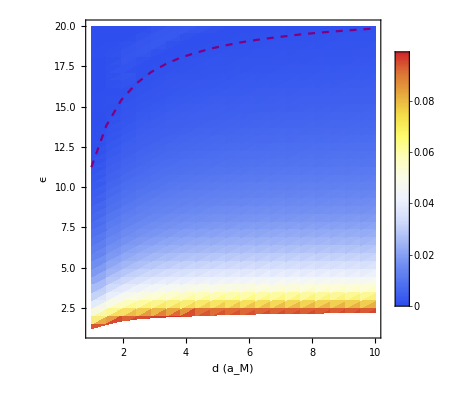

```mathematica
ListDensityPlot[Transpose@sweepnu13["gap"],DataRange->{sweepnu13["dlist"][[1,{1,-1}]],sweepnu13["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@ListLinePlot[sweepnu13gapline,PlotStyle->Directive[Dashed,Purple]]}]
```

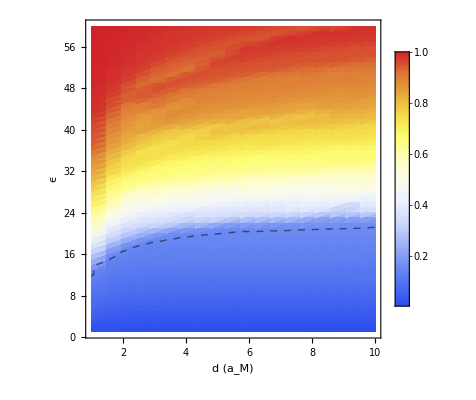

```mathematica
ListDensityPlot[Table[wig[sweepnu13["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu13["spin"]][[1]]},{j,Dimensions[sweepnu13["spin"]][[2]]}],DataRange->{sweepnu13["dlist"][[1,{1,-1}]],sweepnu13["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

### Sweep_nu=[3,9] F

```mathematica
sweepnu39=importmat[NotebookDirectory[]<>"nu3,9_U110.mat"];
```

```mathematica
sweepnu39gapline=Table[Block[{data=sweepnu39,thres=.2,last,slice,fint},slice=Tanh[(data["innergap"]/data["gap"])[[i]]];last=FirstPosition[slice,_?(#>thres&)][[1]];fint=Interpolation[Transpose@{slice[[1;;last]],data["epsilonlist"][[1,1;;last]]}];{data["dlist"][[1,i]],fint[thres]}],{i,20}]
```

{{1.,9.71214},{1.47368,12.3431},{1.94737,13.9652},{2.42105,14.9819},{2.89474,15.6887},{3.36842,16.1813},{3.84211,16.5735},{4.31579,16.8428},{4.78947,17.112},{5.26316,17.2942},{5.73684,17.4643},{6.21053,17.6197},{6.68421,17.7337},{7.15789,17.8363},{7.63158,17.9369},{8.10526,18.0387},{8.57895,18.1139},{9.05263,18.1821},{9.52632,18.2409},{10.,18.3035}}

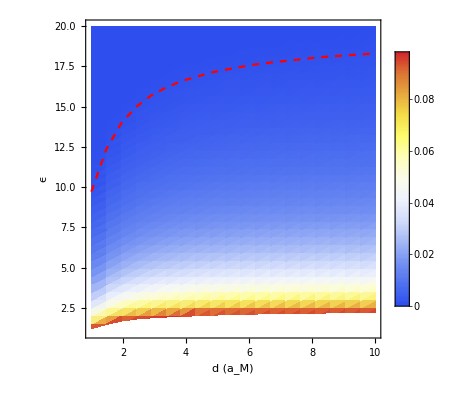

```mathematica
ListDensityPlot[Transpose@sweepnu39["gap"],DataRange->{sweepnu39["dlist"][[1,{1,-1}]],sweepnu39["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@ListLinePlot[sweepnu39gapline,PlotStyle->Directive[Dashed,Red]]}]
```

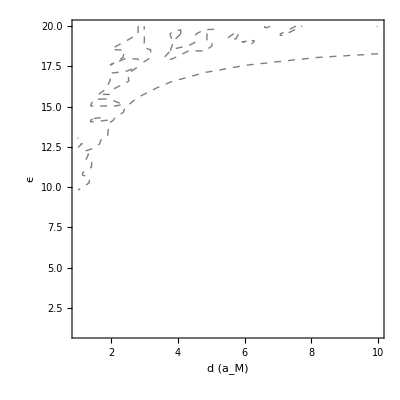

```mathematica
ListContourPlot[Transpose@Tanh@(sweepnu39["innergap"]/sweepnu39["gap"]),DataRange->{sweepnu13["dlist"][[1,{1,-1}]],sweepnu13["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{.2},ContourShading->None,ContourStyle->Directive[{Thick,Dashed}]]
```

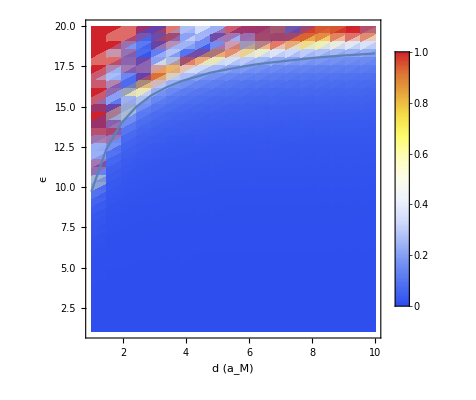

```mathematica
ListDensityPlot[Transpose@Tanh@(sweepnu39["innergap"]/sweepnu39["gap"]),DataRange->{sweepnu39["dlist"][[1,{1,-1}]],sweepnu39["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->{Full,Full,{0,1}},FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@ListLinePlot[gapline]}]
```

```mathematica
sweepnu39gapline=Table[Block[{data=sweepnu39,thres=.25,last,slice,fint},slice=Tanh[(data["innergap"]/data["gap"])[[i]]];last=FirstPosition[slice,_?(#>thres&)][[1]];fint=Interpolation[Transpose@{slice[[1;;last]],data["epsilonlist"][[1,1;;last]]}];{data["dlist"][[1,i]],fint[thres]}],{i,20}]
```

{{1.,9.44668},{1.47368,12.454},{1.94737,14.1727},{2.42105,15.1738},{2.89474,15.8154},{3.36842,16.3294},{3.84211,16.7392},{4.31579,17.0907},{4.78947,17.2915},{5.26316,17.5429},{5.73684,17.6885},{6.21053,17.8209},{6.68421,17.9703},{7.15789,18.0951},{7.63158,18.1774},{8.10526,18.2557},{8.57895,18.3346},{9.05263,18.4195},{9.52632,18.5021},{10.,18.5735}}

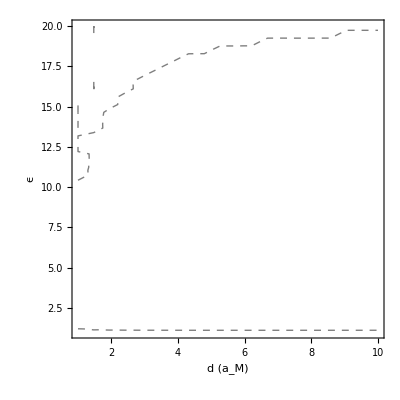

```mathematica
contourzero=ListContourPlot[Transpose@sweepnu39["final"]-Transpose@sweepnu13["final"],DataRange->{sweepnu13["dlist"][[1,{1,-1}]],sweepnu13["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{0},ContourShading->None,ContourStyle->Directive[{Thick,Dashed}]]
```

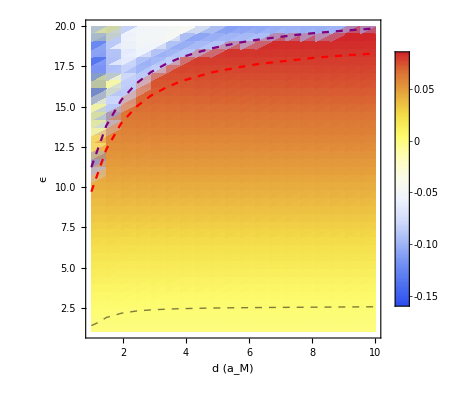

```mathematica
ListDensityPlot[1000Transpose@sweepnu39["final"]-1000Transpose@sweepnu13["final"],DataRange->{sweepnu13["dlist"][[1,{1,-1}]],sweepnu13["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contourzero,First@ListLinePlot[sweepnu39gapline,PlotStyle->Directive[Dashed,Red]],First@ListLinePlot[sweepnu13gapline,PlotStyle->Directive[Dashed,Purple]]}]
```

#### No phase transition for 1/3, AF is always energy favorable

```mathematica
sweepnu39["spin"][[20,20]]//MatrixForm
```

(0.85553 | 0. | 0. | 0.85553
0.85553 | 0. | 0. | 0.85553
0.85553 | 0. | 0. | 0.85553
0.0722351 | 0. | 0. | 0.0722351
0.0722351 | 0. | 0. | 0.0722351
0.0722351 | 0. | 0. | 0.0722351
0.0722351 | 0. | 0. | 0.0722351
0.0722351 | 0. | 0. | 0.0722351
0.0722351 | 0. | 0. | 0.0722351)

```mathematica
sweepnu13["spin"][[20,20]]//Chop//MatrixForm
```

(0.852023 | 0.847589 | 0 | 0
0.852023 | -0.423795 | 0.734034 | 0
0.852023 | -0.423795 | -0.734034 | 0
0.0739884 | -1.19999×10^-10 | 2.07849×10^-10 | 0
0.0739884 | -1.19999×10^-10 | -2.07849×10^-10 | 0
0.0739884 | -1.20004×10^-10 | -2.07847×10^-10 | 0
0.0739884 | -1.20003×10^-10 | 2.07846×10^-10 | 0
0.0739884 | 2.40002×10^-10 | 0 | 0
0.0739884 | 2.40002×10^-10 | 0 | 0)

```mathematica
sweepnu39["final"][[20,20]]
```

0.0345398

```mathematica
sweepnu13["final"][[20,20]]
```

0.0344949

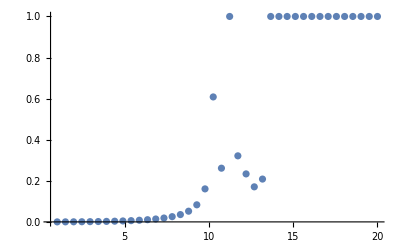

```mathematica
ListPlot[Tanh[sweepnu39["innergap"]/sweepnu39["gap"]][[1]],DataRange->{sweepnu39["epsilonlist"][[1,1]],sweepnu39["epsilonlist"][[1,-1]]},PlotRange->Full]
```

```mathematica
f=Interpolation[Transpose@{Tanh[sweepnu39["innergap"]/sweepnu39["gap"]][[1]],sweepnu39["epsilonlist"][[1]]}]
```

InterpolatingFunction[…]

```mathematica
SelectFirst[Tanh[(sweepnu39["innergap"]/sweepnu39["gap"])[[1]]],#>0.2&]
```

0.608266

```mathematica
FirstPosition[Tanh[(sweepnu39["innergap"]/sweepnu39["gap"])[[1]]],_?(#>0.2&)]
```

{20}

```mathematica
Block[{thres=.2,last,data=sweepnu39,slice,fint,i=2},slice=Tanh[(data["innergap"]/data["gap"])[[i]]];last=FirstPosition[slice,_?(#>thres&)][[1]](*;fint=Interpolation[Transpose@{slice[[1;;last]],data["epsilonlist"][[1,1;;last]]}];{data["dlist"][[1,i]],fint[thres]}*)]
```

25

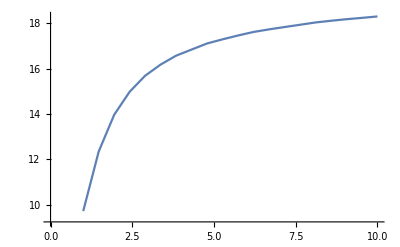

```mathematica
ListLinePlot[gapline]
```

### Sweep_nu=[2,3]

```mathematica
sweepnu23=importmat[NotebookDirectory[]<>"nu2,3_U110.mat"];
```

```mathematica
sweepnu23gapline=Table[Block[{data=sweepnu23,thres=.2,last,slice,fint},slice=Tanh[(data["innergap"]/data["gap"])[[i]]];last=FirstPosition[slice,_?(#>thres&)][[1]];fint=Interpolation[Transpose@{slice[[1;;last]],data["epsilonlist"][[1,1;;last]]}];{data["dlist"][[1,i]],fint[thres]}],{i,20}];
```

Part::span: 1;;NotFound is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Transpose::nmtx: The first two levels of {{0.0000301096,0.000018642,0.0000449508,0.000061034,0.0000786114,0.0000976383,0.000118078,0.000139895,0.000163055,0.000187527,0.000213279,0.000240281,0.000268506,0.000297928,0.000328522,0.000360251,«19»,0.00121028,0.00126263,0.00131586,0.00136997,0.00142494,0.00148078,0.00153746,0.00159501,0.00165342,0.00171267,0.00177277,0.00183371,0.00189548,0.0019581,0.00202154}⟦1;;NotFound⟧,«1»} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{0.0000301096,0.000018642,0.0000449508,0.000061034,0.0000786114,0.0000976383,0.000118078,0.000139895,0.000163055,0.000187527,0.000213279,0.000240281,0.000268506,0.000297928,0.000328522,0.000360251,«19»,0.00121028,0.00126263,0.00131586,0.00136997,0.00142494,0.00148078,0.00153746,0.00159501,0.00165342,0.00171267,0.00177277,0.00183371,0.00189548,0.0019581,0.00202154}⟦1;;…⟧,«1»}] does not contain a list of data and coordinates.

Part::span: 1;;NotFound is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{8.75864×10^-6,0.0000183263,0.0000291198,0.0000186805,0.0000394618,0.0000521597,0.0000659366,0.000080774,0.0000966455,0.00011355,0.000131462,0.000150364,0.000170241,0.000191077,0.000212856,0.000235565,«19»,0.000867379,0.000907188,0.00094771,0.000988987,0.00103099,0.00107372,0.00111717,0.00116133,0.0012062,0.00125178,0.00129807,0.00134506,0.00139276,0.00144114,0.00149023}⟦1;;NotFound⟧,«1»} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{8.75864×10^-6,0.0000183263,0.0000291198,0.0000186805,0.0000394618,0.0000521597,0.0000659366,0.000080774,0.0000966455,0.00011355,0.000131462,0.000150364,0.000170241,0.000191077,0.000212856,«20»,0.000867379,0.000907188,0.00094771,0.000988987,0.00103099,0.00107372,0.00111717,0.00116133,0.0012062,0.00125178,0.00129807,0.00134506,0.00139276,0.00144114,0.00149023}⟦1;;NotFound⟧,{{«1»}}⟦1,«1»⟧}] does not contain a list of data and coordinates.

Transpose::nmtx: The first two levels of {{3.06303×10^-6,0.0000108283,0.0000196485,0.0000295049,0.0000277462,0.0000382213,0.0000496273,0.000061964,0.0000752116,0.0000893573,0.000104388,0.000120292,0.000137057,0.00015467,0.000173121,0.000192398,«19»,0.000737582,0.000772279,0.000807646,0.000843652,0.000880345,0.000917696,0.0009557,0.000994355,0.00103366,0.0010736,0.00111419,0.00115542,0.00119729,0.00123979,0.00128292}⟦1;;NotFound⟧,«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Interpolation::innd: First argument in Transpose[{{3.06303×10^-6,0.0000108283,0.0000196485,0.0000295049,0.0000277462,0.0000382213,0.0000496273,0.000061964,0.0000752116,0.0000893573,0.000104388,0.000120292,0.000137057,0.00015467,0.000173121,«20»,0.000737582,0.000772279,0.000807646,0.000843652,0.000880345,0.000917696,0.0009557,0.000994355,0.00103366,0.0010736,0.00111419,0.00115542,0.00119729,0.00123979,0.00128292}⟦1;;NotFound⟧,{{«1»}}⟦1,«1»⟧}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

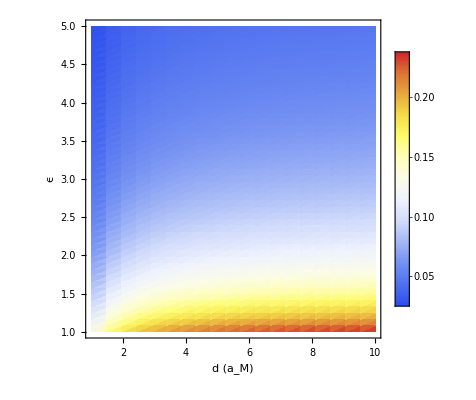

```mathematica
ListDensityPlot[Transpose@sweepnu23["gap"],DataRange->{sweepnu23["dlist"][[1,{1,-1}]],sweepnu23["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"}(*,Epilog->{ First@contour}*)]
```

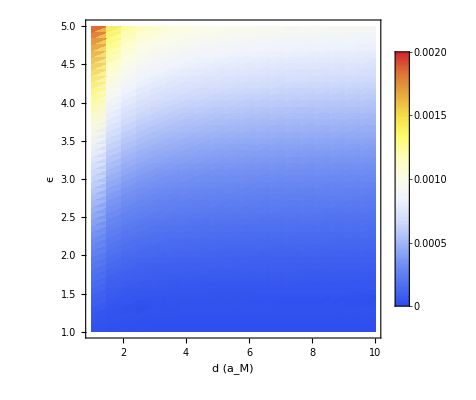

```mathematica
ListDensityPlot[Transpose@Tanh@(sweepnu23["innergap"]/sweepnu23["gap"]),DataRange->{sweepnu23["dlist"][[1,{1,-1}]],sweepnu23["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->{Full,Full,{0,1}},FrameLabel->{"d (a_M)","ϵ"}]
```

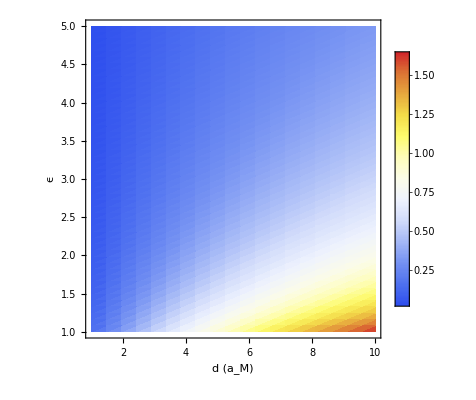

```mathematica
ListDensityPlot[Transpose@sweepnu23["final"],DataRange->{sweepnu23["dlist"][[1,{1,-1}]],sweepnu23["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

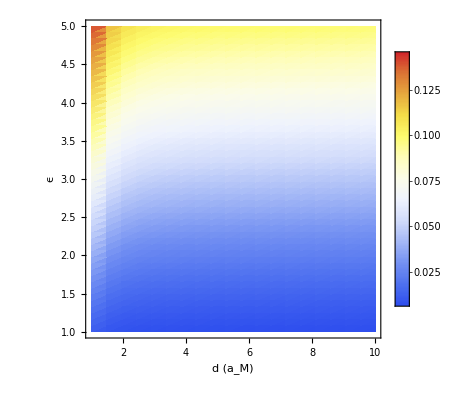

{{-3.22242×10^-17,-2.14828×10^-17,1.07414×10^-16,-6.1763×10^-17,-2.14828×10^-17,-5.37069×10^-18,8.05604×10^-17,1.61121×10^-17,6.9819×10^-17,6.44483×10^-17,3.22242×10^-17,-9.66725×10^-17,-9.13018×10^-17,4.29655×10^-17,-5.37069×10^-17,-3.75949×10^-17,-1.12785×10^-16,5.37069×10^-18,4.83362×10^-17,3.75949×10^-17},{5.63923×10^-17,5.90776×10^-17,-3.22242×10^-17,-6.9819×10^-17,6.44483×10^-17,-3.22242×10^-17,2.14828×10^-17,1.87974×10^-17,5.37069×10^-18,1.02043×10^-16,1.61121×10^-17,8.05604×10^-17,1.63806×10^-16,-2.68535×10^-17,1.07414×10^-17,5.37069×10^-18,1.07414×10^-17,1.39638×10^-16,2.68535×10^-17,5.90776×10^-17},{1.18155×10^-16,-1.87974×10^-17,-4.29655×10^-17,-2.14828×10^-17,-1.04729×10^-16,-4.83362×10^-17,8.05604×10^-17,2.41681×10^-17,2.14828×10^-17,8.59311×10^-17,8.05604×10^-17,1.34267×10^-17,-2.14828×10^-17,-1.02043×10^-16,1.61121×10^-16,-2.14828×10^-17,5.90776×10^-17,1.18155×10^-16,-2.68535×10^-17,-9.13018×10^-17},{2.41681×10^-17,-2.68535×10^-17,1.87974×10^-17,5.37069×10^-18,8.05604×10^-17,4.29655×10^-17,5.90776×10^-17,0.,4.83362×10^-17,1.5575×10^-16,-4.83362×10^-17,1.61121×10^-17,-8.59311×10^-17,-4.29655×10^-17,3.75949×10^-17,-1.34267×10^-17,2.14828×10^-17,5.37069×10^-17,1.61121×10^-17,5.37069×10^-17},{-5.63923×10^-17,-6.44483×10^-17,-1.61121×10^-17,5.37069×10^-17,7.51897×10^-17,-4.29655×10^-17,1.61121×10^-17,1.61121×10^-17,3.75949×10^-17,6.44483×10^-17,8.05604×10^-17,-3.75949×10^-17,-4.29655×10^-17,1.5575×10^-16,9.66725×10^-17,2.14828×10^-17,4.83362×10^-17,1.61121×10^-17,7.25044×10^-17,3.75949×10^-17},{7.51897×10^-17,5.37069×10^-18,5.37069×10^-17,-4.83362×10^-17,1.07414×10^-16,2.14828×10^-17,3.22242×10^-17,5.10216×10^-17,3.75949×10^-17,3.75949×10^-17,5.37069×10^-18,1.61121×10^-17,1.02043×10^-16,-1.12785×10^-16,1.1547×10^-16,-1.02043×10^-16,-1.61121×10^-17,1.07414×10^-16,1.07414×10^-16,1.61121×10^-17},{-6.9819×10^-17,3.22242×10^-17,-6.1763×10^-17,8.86164×10^-17,-1.1547×10^-16,-2.68535×10^-17,-3.75949×10^-17,-5.90776×10^-17,3.22242×10^-17,-1.07414×10^-17,6.9819×10^-17,3.75949×10^-17,1.61121×10^-17,3.75949×10^-17,-5.37069×10^-18,4.83362×10^-17,-3.22242×10^-17,-1.61121×10^-17,2.68535×10^-17,1.18155×10^-16},{-1.77233×10^-16,4.02802×10^-17,8.59311×10^-17,1.61121×10^-17,-3.75949×10^-17,4.83362×10^-17,-1.07414×10^-17,-6.1763×10^-17,-5.90776×10^-17,3.22242×10^-17,-1.20841×10^-16,-6.9819×10^-17,5.90776×10^-17,1.07414×10^-17,1.07414×10^-16,9.13018×10^-17,3.75949×10^-17,-5.37069×10^-18,3.49095×10^-17,1.50379×10^-16},{1.34267×10^-17,-9.13018×10^-17,1.61121×10^-17,-2.14828×10^-17,4.02802×10^-17,6.9819×10^-17,5.37069×10^-17,-1.87974×10^-17,-1.23526×10^-16,1.10099×10^-16,2.14828×10^-17,-5.90776×10^-17,3.75949×10^-17,2.68535×10^-17,2.41681×10^-17,6.71337×10^-17,-2.68535×10^-18,1.07414×10^-16,1.02043×10^-16,-2.41681×10^-17},{-1.07414×10^-17,-8.86164×10^-17,2.68535×10^-18,-1.61121×10^-17,5.37069×10^-18,7.25044×10^-17,-2.14828×10^-17,-5.37069×10^-17,2.95388×10^-17,0.,5.10216×10^-17,9.39871×10^-17,-3.49095×10^-17,2.68535×10^-17,6.1763×10^-17,0.,-1.02043×10^-16,4.83362×10^-17,-2.68535×10^-17,-5.37069×10^-18},{5.10216×10^-17,2.68535×10^-17,-5.90776×10^-17,0.,9.66725×10^-17,3.49095×10^-17,-1.07414×10^-17,5.37069×10^-17,-8.05604×10^-18,1.50379×10^-16,2.14828×10^-17,1.39638×10^-16,6.44483×10^-17,1.12785×10^-16,-4.83362×10^-17,2.14828×10^-17,6.44483×10^-17,-5.10216×10^-17,8.59311×10^-17,-5.37069×10^-17},{1.50379×10^-16,8.32457×10^-17,1.07414×10^-17,1.50379×10^-16,8.05604×10^-17,-2.14828×10^-17,-2.14828×10^-17,1.85289×10^-16,5.10216×10^-17,6.1763×10^-17,3.75949×10^-17,-5.37069×10^-17,8.05604×10^-17,-1.5575×10^-16,1.18155×10^-16,8.59311×10^-17,3.75949×10^-17,4.83362×10^-17,-7.51897×10^-17,-5.37069×10^-18},{7.51897×10^-17,2.95388×10^-17,-2.68535×10^-17,-2.68535×10^-17,-8.59311×10^-17,-6.9819×10^-17,9.66725×10^-17,-8.86164×10^-17,-2.14828×10^-17,3.22242×10^-17,8.05604×10^-17,7.51897×10^-17,3.75949×10^-17,1.18155×10^-16,2.68535×10^-17,8.05604×10^-17,1.5575×10^-16,2.68535×10^-17,1.04729×10^-16,-4.83362×10^-17},{8.59311×10^-17,-6.1763×10^-17,-5.37069×10^-17,1.53065×10^-16,-2.68535×10^-17,8.86164×10^-17,1.26211×10^-16,4.02802×10^-17,1.45009×10^-16,1.71862×10^-16,-3.22242×10^-17,4.29655×10^-17,3.49095×10^-17,2.14828×10^-17,1.87974×10^-17,6.71337×10^-17,8.59311×10^-17,-8.59311×10^-17,4.83362×10^-17,3.22242×10^-17},{1.39638×10^-16,2.68535×10^-17,1.61121×10^-17,1.50379×10^-16,1.18155×10^-16,0.,4.29655×10^-17,-4.02802×10^-17,1.61121×10^-17,7.51897×10^-17,5.10216×10^-17,1.45009×10^-16,1.02043×10^-16,-2.14828×10^-17,1.07414×10^-16,-6.44483×10^-17,1.66491×10^-16,-5.10216×10^-17,9.93578×10^-17,-1.61121×10^-17},{1.66491×10^-16,5.37069×10^-17,-4.29655×10^-17,-1.18155×10^-16,4.83362×10^-17,6.71337×10^-17,7.25044×10^-17,2.14828×10^-16,1.02043×10^-16,1.50379×10^-16,-4.02802×10^-17,2.14828×10^-17,8.86164×10^-17,-1.87974×10^-17,3.75949×10^-17,-1.87974×10^-17,-5.90776×10^-17,1.34267×10^-17,-1.61121×10^-17,2.41681×10^-17},{-3.49095×10^-17,1.12785×10^-16,6.44483×10^-17,5.63923×10^-17,1.66491×10^-16,6.71337×10^-17,-3.75949×10^-17,-5.63923×10^-17,0.,-5.37069×10^-18,-3.49095×10^-17,-1.23526×10^-16,4.29655×10^-17,2.68535×10^-17,-2.95388×10^-17,-8.32457×10^-17,1.18155×10^-16,4.56509×10^-17,-6.44483×10^-17,3.22242×10^-17},{1.34267×10^-17,9.13018×10^-17,1.71862×10^-16,1.87974×10^-17,8.86164×10^-17,-5.63923×10^-17,-1.87974×10^-17,-3.75949×10^-17,6.9819×10^-17,-1.07414×10^-17,3.49095×10^-17,-2.14828×10^-17,1.50379×10^-16,2.68535×10^-18,8.59311×10^-17,1.1547×10^-16,1.61121×10^-16,-4.02802×10^-17,1.12785×10^-16,1.71862×10^-16},{2.01401×10^-16,-1.10099×10^-16,3.75949×10^-17,5.90776×10^-17,-4.02802×10^-17,4.83362×10^-17,-3.75949×10^-17,4.56509×10^-17,-1.87974×10^-16,-5.63923×10^-17,6.44483×10^-17,8.86164×10^-17,9.66725×10^-17,-5.37069×10^-17,4.02802×10^-17,3.22242×10^-17,1.69177×10^-16,-8.05604×10^-17,-9.66725×10^-17,2.04086×10^-16},{1.89317×10^-16,3.75949×10^-17,-8.05604×10^-17,-5.37069×10^-18,2.68535×10^-17,1.42323×10^-16,1.87974×10^-16,-4.02802×10^-17,-8.05604×10^-18,-1.34267×10^-17,6.9819×10^-17,8.32457×10^-17,1.36953×10^-16,6.71337×10^-17,-7.78751×10^-17,8.32457×10^-17,2.41681×10^-17,-1.87974×10^-17,8.59311×10^-17,1.39638×10^-16},{1.5575×10^-16,1.28897×10^-16,8.59311×10^-17,1.04729×10^-16,-9.66725×10^-17,6.71337×10^-17,1.50379×10^-16,-4.56509×10^-17,6.71337×10^-17,1.9603×10^-16,9.66725×10^-17,4.56509×10^-17,-1.87974×10^-17,1.04729×10^-16,1.45009×10^-16,-5.37069×10^-18,1.07414×10^-17,6.44483×10^-17,5.37069×10^-18,7.25044×10^-17},{8.05604×10^-17,1.34267×10^-16,1.18155×10^-16,-7.51897×10^-17,1.53065×10^-16,5.90776×10^-17,1.36953×10^-16,2.68535×10^-17,2.14828×10^-17,1.42323×10^-16,5.37069×10^-18,1.04729×10^-16,8.05604×10^-17,-7.25044×10^-17,1.07414×10^-17,1.77233×10^-16,8.05604×10^-17,-2.14828×10^-17,1.58435×10^-16,1.34267×10^-16},{8.32457×10^-17,1.12785×10^-16,7.78751×10^-17,8.05604×10^-18,5.37069×10^-17,1.10099×10^-16,5.37069×10^-17,8.05604×10^-17,1.71862×10^-16,1.20841×10^-16,4.56509×10^-17,6.71337×10^-17,3.22242×10^-17,5.10216×10^-17,1.66491×10^-16,8.86164×10^-17,1.58435×10^-16,2.36311×10^-16,1.28897×10^-16,-2.68535×10^-17},{1.18155×10^-16,-3.75949×10^-17,5.63923×10^-17,1.85289×10^-16,4.29655×10^-17,1.12785×10^-16,1.50379×10^-16,6.1763×10^-17,5.90776×10^-17,1.87974×10^-17,7.78751×10^-17,1.02043×10^-16,-2.95388×10^-17,1.87974×10^-17,1.10099×10^-16,-1.26211×10^-16,4.83362×10^-17,2.41681×10^-17,1.28897×10^-16,6.71337×10^-17},{8.05604×10^-17,1.26211×10^-16,4.02802×10^-17,1.61121×10^-17,5.10216×10^-17,2.68535×10^-17,1.85289×10^-16,6.71337×10^-17,7.78751×10^-17,3.22242×10^-17,1.28897×10^-16,3.22242×10^-17,2.20198×10^-16,1.82604×10^-16,2.14828×10^-17,1.45009×10^-16,8.86164×10^-17,1.45009×10^-16,1.87974×10^-17,8.59311×10^-17},{4.56509×10^-17,1.45009×10^-16,7.25044×10^-17,8.86164×10^-17,2.68535×10^-17,-2.14828×10^-17,1.07414×10^-17,5.90776×10^-17,9.93578×10^-17,1.04729×10^-16,1.79918×10^-16,-6.1763×10^-17,9.13018×10^-17,4.83362×10^-17,5.37069×10^-18,-4.83362×10^-17,3.75949×10^-17,1.28897×10^-16,2.47052×10^-16,1.10099×10^-16},{-1.47694×10^-16,1.23526×10^-16,4.29655×10^-17,1.36953×10^-16,5.37069×10^-17,1.10099×10^-16,-7.25044×10^-17,1.04729×10^-16,-4.02802×10^-17,1.28897×10^-16,2.14828×10^-17,6.71337×10^-17,-3.49095×10^-17,9.66725×10^-17,1.18155×10^-16,2.14828×10^-17,8.59311×10^-17,1.34267×10^-16,8.86164×10^-17,1.77233×10^-16},{-2.14828×10^-17,1.85289×10^-16,1.31582×10^-16,1.10099×10^-16,-2.68535×10^-18,-2.68535×10^-18,-2.68535×10^-17,9.39871×10^-17,1.50379×10^-16,2.68535×10^-18,9.66725×10^-17,1.1547×10^-16,2.68535×10^-17,2.14828×10^-17,1.61121×10^-17,1.66491×10^-16,-4.56509×10^-17,1.74548×10^-16,4.83362×10^-17,4.83362×10^-17},{1.23526×10^-16,8.05604×10^-17,1.39638×10^-16,-2.14828×10^-17,8.59311×10^-17,1.26211×10^-16,2.38996×10^-16,5.37069×10^-17,1.20841×10^-16,1.61121×10^-17,-3.75949×10^-17,1.77233×10^-16,3.49095×10^-17,2.63164×10^-16,1.45009×10^-16,1.28897×10^-16,1.50379×10^-16,1.87974×10^-16,1.1547×10^-16,7.51897×10^-17},{1.28897×10^-16,4.56509×10^-17,2.20198×10^-16,1.42323×10^-16,1.34267×10^-16,2.01401×10^-16,2.14828×10^-17,8.59311×10^-17,5.37069×10^-18,2.68535×10^-18,9.39871×10^-17,8.86164×10^-17,1.04729×10^-16,4.29655×10^-17,1.58435×10^-16,1.34267×10^-17,4.29655×10^-17,3.22242×10^-17,1.02043×10^-16,4.29655×10^-17},{1.20841×10^-16,1.87974×10^-16,9.66725×10^-17,-1.07414×10^-17,5.90776×10^-17,1.02043×10^-16,1.82604×10^-16,2.01401×10^-16,8.05604×10^-17,6.44483×10^-17,6.44483×10^-17,2.17513×10^-16,1.26211×10^-16,2.63164×10^-16,5.10216×10^-17,7.51897×10^-17,1.26211×10^-16,4.02802×10^-17,2.41681×10^-17,1.1547×10^-16},{-2.14828×10^-17,5.37069×10^-17,-2.14828×10^-17,4.29655×10^-17,1.71862×10^-16,2.41681×10^-17,1.53065×10^-16,6.1763×10^-17,1.9066×10^-16,1.61121×10^-16,-1.61121×10^-17,1.39638×10^-16,1.5575×10^-16,5.37069×10^-17,-1.12785×10^-16,0.,4.56509×10^-17,-1.20841×10^-16,2.95388×10^-17,2.28254×10^-16},{1.53065×10^-16,1.63806×10^-16,5.37069×10^-18,1.1547×10^-16,1.26211×10^-16,5.10216×10^-17,1.9603×10^-16,8.32457×10^-17,-1.34267×10^-17,0.,-1.07414×10^-17,8.59311×10^-17,2.14828×10^-17,9.66725×10^-17,5.10216×10^-17,7.25044×10^-17,4.83362×10^-17,9.66725×10^-17,6.44483×10^-17,1.07414×10^-16},{-7.25044×10^-17,8.86164×10^-17,1.54407×10^-16,-5.37069×10^-18,1.53065×10^-16,8.59311×10^-17,4.02802×10^-17,2.22884×10^-16,1.02043×10^-16,5.90776×10^-17,1.5575×10^-16,6.9819×10^-17,1.47694×10^-16,9.13018×10^-17,1.87974×10^-16,4.29655×10^-17,6.9819×10^-17,7.51897×10^-17,4.29655×10^-17,-1.02043×10^-16},{1.77233×10^-16,-1.04729×10^-16,5.90776×10^-17,2.95388×10^-17,5.10216×10^-17,-2.68535×10^-18,1.07414×10^-16,4.29655×10^-17,4.29655×10^-17,2.14828×10^-17,1.12785×10^-16,-7.25044×10^-17,1.61121×10^-17,5.90776×10^-17,-2.68535×10^-17,5.10216×10^-17,8.05604×10^-17,9.13018×10^-17,5.10216×10^-17,8.86164×10^-17},{-3.49095×10^-17,5.10216×10^-17,1.23526×10^-16,-1.87974×10^-17,1.26211×10^-16,1.20841×10^-16,0.,1.9066×10^-16,6.9819×10^-17,2.41681×10^-17,8.05604×10^-17,1.10099×10^-16,6.9819×10^-17,6.44483×10^-17,1.77233×10^-16,9.13018×10^-17,-2.14828×10^-17,2.95388×10^-17,1.28897×10^-16,1.61121×10^-17},{1.12785×10^-16,4.83362×10^-17,1.26211×10^-16,2.68535×10^-17,1.61121×10^-17,3.22242×10^-17,2.68535×10^-17,1.98716×10^-16,1.61121×10^-17,1.28897×10^-16,1.07414×10^-17,1.63806×10^-16,2.68535×10^-17,5.37069×10^-17,8.59311×10^-17,9.13018×10^-17,-1.42323×10^-16,2.41681×10^-17,1.58435×10^-16,0.},{5.63923×10^-17,-1.34267×10^-17,-5.37069×10^-18,2.17513×10^-16,9.93578×10^-17,8.05604×10^-17,1.45009×10^-16,1.77233×10^-16,2.68535×10^-18,-1.07414×10^-17,1.9066×10^-16,5.90776×10^-17,7.51897×10^-17,1.98716×10^-16,1.98716×10^-16,-1.12785×10^-16,1.18155×10^-16,2.01401×10^-16,1.5575×10^-16,3.49095×10^-17},{-1.82604×10^-16,-5.37069×10^-18,7.51897×10^-17,9.13018×10^-17,8.05604×10^-18,2.12142×10^-16,1.18155×10^-16,3.75949×10^-17,1.10099×10^-16,5.37069×10^-17,1.66491×10^-16,-7.25044×10^-17,2.12142×10^-16,1.85289×10^-16,1.45009×10^-16,1.12785×10^-16,1.71862×10^-16,-2.68535×10^-17,8.05604×10^-17,6.44483×10^-17},{7.25044×10^-17,2.12142×10^-16,1.50379×10^-16,1.26211×10^-16,9.93578×10^-17,9.93578×10^-17,8.86164×10^-17,1.28897×10^-16,8.05604×10^-17,1.28897×10^-16,1.66491×10^-16,9.13018×10^-17,1.66491×10^-16,-2.09457×10^-16,8.05604×10^-18,9.13018×10^-17,-5.37069×10^-17,-2.14828×10^-17,5.90776×10^-17,-6.44483×10^-17},{1.5575×10^-16,1.31582×10^-16,7.25044×10^-17,6.71337×10^-17,-9.66725×10^-17,1.28897×10^-16,5.10216×10^-17,3.03444×10^-16,1.02043×10^-16,4.83362×10^-17,6.1763×10^-17,8.05604×10^-17,1.47694×10^-16,2.14828×10^-17,8.59311×10^-17,-7.25044×10^-17,1.61121×10^-16,3.49095×10^-17,4.83362×10^-17,7.25044×10^-17},{1.61121×10^-17,2.20198×10^-16,9.93578×10^-17,6.1763×10^-17,1.45009×10^-16,1.28897×10^-16,1.87974×10^-17,2.04086×10^-16,-1.07414×10^-17,6.1763×10^-17,8.86164×10^-17,-1.61121×10^-17,1.74548×10^-16,6.1763×10^-17,9.93578×10^-17,1.28897×10^-16,1.1547×10^-16,1.39638×10^-16,-1.07414×10^-17,1.98716×10^-16},{-4.56509×10^-17,-1.07414×10^-17,1.79918×10^-16,2.68535×10^-17,2.36311×10^-16,1.28897×10^-16,-1.34267×10^-17,7.51897×10^-17,5.37069×10^-18,1.39638×10^-16,-7.25044×10^-17,0.,-2.68535×10^-17,1.58435×10^-16,1.36953×10^-16,9.39871×10^-17,1.28897×10^-16,1.85289×10^-16,-5.37069×10^-18,9.66725×10^-17},{-8.05604×10^-17,2.95388×10^-17,6.1763×10^-17,8.32457×10^-17,-1.34267×10^-17,5.63923×10^-17,6.9819×10^-17,1.04729×10^-16,5.90776×10^-17,1.07414×10^-16,2.14828×10^-16,1.69177×10^-16,2.44367×10^-16,1.20841×10^-16,7.51897×10^-17,1.07414×10^-16,-5.90776×10^-17,1.66491×10^-16,0.,1.87974×10^-16},{9.93578×10^-17,1.47694×10^-16,1.82604×10^-16,1.12785×10^-16,-3.49095×10^-17,0.,1.07414×10^-16,-1.87974×10^-17,1.07414×10^-17,1.61121×10^-17,-2.68535×10^-18,1.53065×10^-16,7.25044×10^-17,6.71337×10^-17,1.61121×10^-17,1.10099×10^-16,1.34267×10^-17,-6.71337×10^-17,8.86164×10^-17,9.39871×10^-17},{1.61121×10^-16,2.76591×10^-16,-2.68535×10^-18,1.26211×10^-16,8.05604×10^-17,6.9819×10^-17,1.93345×10^-16,-4.83362×10^-17,1.45009×10^-16,2.95388×10^-17,-1.07414×10^-17,5.63923×10^-17,1.1547×10^-16,-1.34267×10^-17,4.56509×10^-17,7.25044×10^-17,1.18155×10^-16,1.07414×10^-16,-5.10216×10^-17,2.41681×10^-17},{2.33625×10^-16,2.76591×10^-16,1.31582×10^-16,-7.51897×10^-17,2.14828×10^-17,1.36953×10^-16,1.50379×10^-16,7.25044×10^-17,-1.07414×10^-17,1.02043×10^-16,0.,6.44483×10^-17,1.23526×10^-16,1.18155×10^-16,2.49737×10^-16,8.32457×10^-17,4.83362×10^-17,8.05604×10^-18,-2.68535×10^-17,6.71337×10^-17},{0.,1.79918×10^-16,2.68535×10^-18,1.69177×10^-16,4.83362×10^-17,9.39871×10^-17,1.53065×10^-16,1.87974×10^-17,2.68535×10^-18,2.14828×10^-16,9.13018×10^-17,1.34267×10^-17,7.25044×10^-17,1.1547×10^-16,8.05604×10^-17,1.02043×10^-16,2.87332×10^-16,1.18155×10^-16,-4.29655×10^-17,1.34267×10^-17},{1.85289×10^-16,1.79918×10^-16,1.07414×10^-17,7.25044×10^-17,1.1547×10^-16,1.50379×10^-16,7.51897×10^-17,1.28897×10^-16,-1.31582×10^-16,1.07414×10^-17,1.18155×10^-16,3.22242×10^-17,8.86164×10^-17,1.5575×10^-16,9.13018×10^-17,1.85289×10^-16,5.37069×10^-17,2.12142×10^-16,1.10099×10^-16,8.59311×10^-17},{6.44483×10^-17,8.59311×10^-17,1.12785×10^-16,4.02802×10^-17,1.53065×10^-16,1.12785×10^-16,5.63923×10^-17,2.14828×10^-17,1.18155×10^-16,4.29655×10^-17,2.14828×10^-17,6.1763×10^-17,1.12785×10^-16,1.18155×10^-16,1.07414×10^-16,-3.75949×10^-17,1.66491×10^-16,8.05604×10^-18,1.04729×10^-16,3.49095×10^-17}}

```mathematica
ListDensityPlot[Table[wig[sweepnu23["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu23["spin"]][[1]]},{j,Dimensions[sweepnu23["spin"]][[2]]}],DataRange->{sweepnu23["dlist"][[1,{1,-1}]],sweepnu23["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"}(*,Epilog->{ First@contour}*)]
```

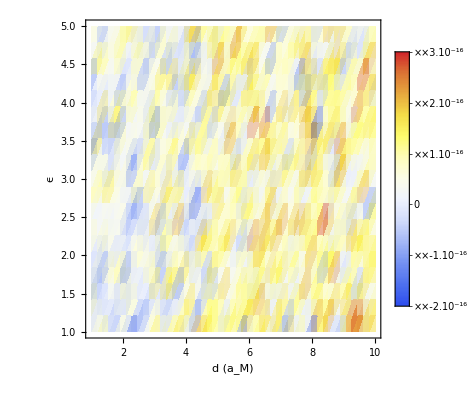

```mathematica
ListDensityPlot[Transpose@sweepnu23["spin"][[All,All,3,4]],DataRange->{sweepnu23["dlist"][[1,{1,-1}]],sweepnu23["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

### Sweep_nu=[6,9] for F

```mathematica
sweepnu69=importmat[NotebookDirectory[]<>"nu6,9_U110.mat"];
```

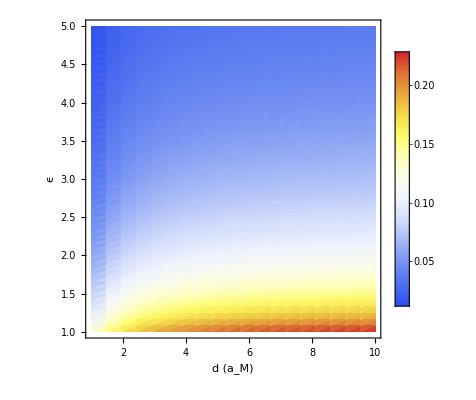

```mathematica
ListDensityPlot[Transpose@sweepnu69["gap"],DataRange->{sweepnu69["dlist"][[1,{1,-1}]],sweepnu69["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"}(*,Epilog->{ First@contour}*)]
```

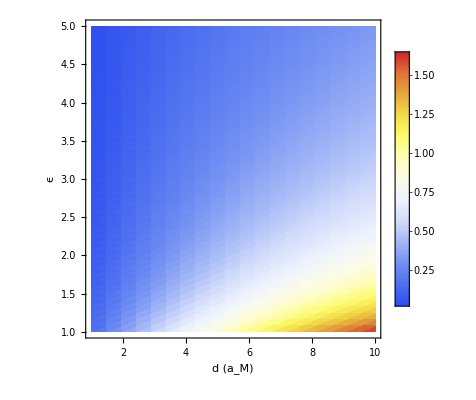

```mathematica
ListDensityPlot[Transpose@sweepnu69["final"],DataRange->{sweepnu69["dlist"][[1,{1,-1}]],sweepnu69["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"}(*,Epilog->{ First@contour}*)]
```

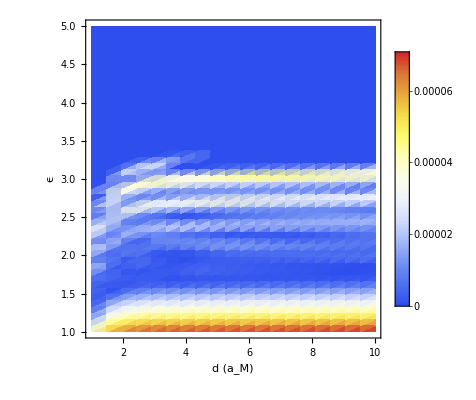

```mathematica
ListDensityPlot[Transpose@sweepnu69["innergap"],DataRange->{sweepnu69["dlist"][[1,{1,-1}]],sweepnu69["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

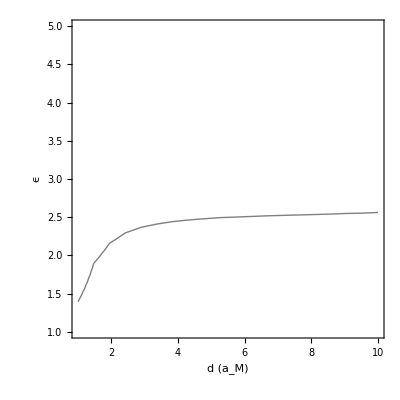

```mathematica
contourzero=ListContourPlot[Transpose@sweepnu69["final"]-Transpose@sweepnu23["final"],DataRange->{sweepnu23["dlist"][[1,{1,-1}]],sweepnu23["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{0},ContourShading->None(*,ContourStyle->Directive[{Thick,Dashed}]*)]
```

```mathematica
First@contourzero
```

GraphicsComplex[{{1.,1.},{1.47368,1.},{1.94737,1.},{2.42105,1.},{2.89474,1.},{3.36842,1.},{3.84211,1.},{4.31579,1.},{4.78947,1.},{5.26316,1.},{5.73684,1.},{6.21053,1.},{6.68421,1.},{7.15789,1.},{7.63158,1.},{8.10526,1.},{8.57895,1.},{9.05263,1.},{9.52632,1.},{10.,1.},{1.,1.08163},{1.47368,1.08163},{1.94737,1.08163},{2.42105,1.08163},{2.89474,1.08163},{3.36842,1.08163},{3.84211,1.08163},{4.31579,1.08163},{4.78947,1.08163},{5.26316,1.08163},{5.73684,1.08163},{6.21053,1.08163},{6.68421,1.08163},{7.15789,1.08163},{7.63158,1.08163},{8.10526,1.08163},{8.57895,1.08163},{9.05263,1.08163},{9.52632,1.08163},{10.,1.08163},{1.,1.16327},{1.47368,1.16327},{1.94737,1.16327},{2.42105,1.16327},{2.89474,1.16327},{3.36842,1.16327},{3.84211,1.16327},{4.31579,1.16327},{4.78947,1.16327},{5.26316,1.16327},{5.73684,1.16327},{6.21053,1.16327},{6.68421,1.16327},{7.15789,1.16327},{7.63158,1.16327},{8.10526,1.16327},{8.57895,1.16327},{9.05263,1.16327},{9.52632,1.16327},{10.,1.16327},{1.,1.2449},{1.47368,1.2449},{1.94737,1.2449},{2.42105,1.2449},{2.89474,1.2449},{3.36842,1.2449},{3.84211,1.2449},{4.31579,1.2449},{4.78947,1.2449},{5.26316,1.2449},{5.73684,1.2449},{6.21053,1.2449},{6.68421,1.2449},{7.15789,1.2449},{7.63158,1.2449},{8.10526,1.2449},{8.57895,1.2449},{9.05263,1.2449},{9.52632,1.2449},{10.,1.2449},{1.,1.32653},{1.47368,1.32653},{1.94737,1.32653},{2.42105,1.32653},{2.89474,1.32653},{3.36842,1.32653},{3.84211,1.32653},{4.31579,1.32653},{4.78947,1.32653},{5.26316,1.32653},{5.73684,1.32653},{6.21053,1.32653},{6.68421,1.32653},{7.15789,1.32653},{7.63158,1.32653},{8.10526,1.32653},{8.57895,1.32653},{9.05263,1.32653},{9.52632,1.32653},{10.,1.32653},{1.,1.40816},{1.47368,1.40816},{1.94737,1.40816},{2.42105,1.40816},{2.89474,1.40816},{3.36842,1.40816},{3.84211,1.40816},{4.31579,1.40816},{4.78947,1.40816},{5.26316,1.40816},{5.73684,1.40816},{6.21053,1.40816},{6.68421,1.40816},{7.15789,1.40816},{7.63158,1.40816},{8.10526,1.40816},{8.57895,1.40816},{9.05263,1.40816},{9.52632,1.40816},{10.,1.40816},{1.,1.4898},{1.47368,1.4898},{1.94737,1.4898},{2.42105,1.4898},{2.89474,1.4898},{3.36842,1.4898},{3.84211,1.4898},{4.31579,1.4898},{4.78947,1.4898},{5.26316,1.4898},{5.73684,1.4898},{6.21053,1.4898},{6.68421,1.4898},{7.15789,1.4898},{7.63158,1.4898},{8.10526,1.4898},{8.57895,1.4898},{9.05263,1.4898},{9.52632,1.4898},{10.,1.4898},{1.,1.57143},{1.47368,1.57143},{1.94737,1.57143},{2.42105,1.57143},{2.89474,1.57143},{3.36842,1.57143},{3.84211,1.57143},{4.31579,1.57143},{4.78947,1.57143},{5.26316,1.57143},{5.73684,1.57143},{6.21053,1.57143},{6.68421,1.57143},{7.15789,1.57143},{7.63158,1.57143},{8.10526,1.57143},{8.57895,1.57143},{9.05263,1.57143},{9.52632,1.57143},{10.,1.57143},{1.,1.65306},{1.47368,1.65306},{1.94737,1.65306},{2.42105,1.65306},{2.89474,1.65306},{3.36842,1.65306},{3.84211,1.65306},{4.31579,1.65306},{4.78947,1.65306},{5.26316,1.65306},{5.73684,1.65306},{6.21053,1.65306},{6.68421,1.65306},{7.15789,1.65306},{7.63158,1.65306},{8.10526,1.65306},{8.57895,1.65306},{9.05263,1.65306},{9.52632,1.65306},{10.,1.65306},{1.,1.73469},{1.47368,1.73469},{1.94737,1.73469},{2.42105,1.73469},{2.89474,1.73469},{3.36842,1.73469},{3.84211,1.73469},{4.31579,1.73469},{4.78947,1.73469},{5.26316,1.73469},{5.73684,1.73469},{6.21053,1.73469},{6.68421,1.73469},{7.15789,1.73469},{7.63158,1.73469},{8.10526,1.73469},{8.57895,1.73469},{9.05263,1.73469},{9.52632,1.73469},{10.,1.73469},{1.,1.81633},{1.47368,1.81633},{1.94737,1.81633},{2.42105,1.81633},{2.89474,1.81633},{3.36842,1.81633},{3.84211,1.81633},{4.31579,1.81633},{4.78947,1.81633},{5.26316,1.81633},{5.73684,1.81633},{6.21053,1.81633},{6.68421,1.81633},{7.15789,1.81633},{7.63158,1.81633},{8.10526,1.81633},{8.57895,1.81633},{9.05263,1.81633},{9.52632,1.81633},{10.,1.81633},{1.,1.89796},{1.47368,1.89796},{1.94737,1.89796},{2.42105,1.89796},{2.89474,1.89796},{3.36842,1.89796},{3.84211,1.89796},{4.31579,1.89796},{4.78947,1.89796},{5.26316,1.89796},{5.73684,1.89796},{6.21053,1.89796},{6.68421,1.89796},{7.15789,1.89796},{7.63158,1.89796},{8.10526,1.89796},{8.57895,1.89796},{9.05263,1.89796},{9.52632,1.89796},{10.,1.89796},{1.,1.97959},{1.47368,1.97959},{1.94737,1.97959},{2.42105,1.97959},{2.89474,1.97959},{3.36842,1.97959},{3.84211,1.97959},{4.31579,1.97959},{4.78947,1.97959},{5.26316,1.97959},{5.73684,1.97959},{6.21053,1.97959},{6.68421,1.97959},{7.15789,1.97959},{7.63158,1.97959},{8.10526,1.97959},{8.57895,1.97959},{9.05263,1.97959},{9.52632,1.97959},{10.,1.97959},{1.,2.06122},{1.47368,2.06122},{1.94737,2.06122},{2.42105,2.06122},{2.89474,2.06122},{3.36842,2.06122},{3.84211,2.06122},{4.31579,2.06122},{4.78947,2.06122},{5.26316,2.06122},{5.73684,2.06122},{6.21053,2.06122},{6.68421,2.06122},{7.15789,2.06122},{7.63158,2.06122},{8.10526,2.06122},{8.57895,2.06122},{9.05263,2.06122},{9.52632,2.06122},{10.,2.06122},{1.,2.14286},{1.47368,2.14286},{1.94737,2.14286},{2.42105,2.14286},{2.89474,2.14286},{3.36842,2.14286},{3.84211,2.14286},{4.31579,2.14286},{4.78947,2.14286},{5.26316,2.14286},{5.73684,2.14286},{6.21053,2.14286},{6.68421,2.14286},{7.15789,2.14286},{7.63158,2.14286},{8.10526,2.14286},{8.57895,2.14286},{9.05263,2.14286},{9.52632,2.14286},{10.,2.14286},{1.,2.22449},{1.47368,2.22449},{1.94737,2.22449},{2.42105,2.22449},{2.89474,2.22449},{3.36842,2.22449},{3.84211,2.22449},{4.31579,2.22449},{4.78947,2.22449},{5.26316,2.22449},{5.73684,2.22449},{6.21053,2.22449},{6.68421,2.22449},{7.15789,2.22449},{7.63158,2.22449},{8.10526,2.22449},{8.57895,2.22449},{9.05263,2.22449},{9.52632,2.22449},{10.,2.22449},{1.,2.30612},{1.47368,2.30612},{1.94737,2.30612},{2.42105,2.30612},{2.89474,2.30612},{3.36842,2.30612},{3.84211,2.30612},{4.31579,2.30612},{4.78947,2.30612},{5.26316,2.30612},{5.73684,2.30612},{6.21053,2.30612},{6.68421,2.30612},{7.15789,2.30612},{7.63158,2.30612},{8.10526,2.30612},{8.57895,2.30612},{9.05263,2.30612},{9.52632,2.30612},{10.,2.30612},{1.,2.38776},{1.47368,2.38776},{1.94737,2.38776},{2.42105,2.38776},{2.89474,2.38776},{3.36842,2.38776},{3.84211,2.38776},{4.31579,2.38776},{4.78947,2.38776},{5.26316,2.38776},{5.73684,2.38776},{6.21053,2.38776},{6.68421,2.38776},{7.15789,2.38776},{7.63158,2.38776},{8.10526,2.38776},{8.57895,2.38776},{9.05263,2.38776},{9.52632,2.38776},{10.,2.38776},{1.,2.46939},{1.47368,2.46939},{1.94737,2.46939},{2.42105,2.46939},{2.89474,2.46939},{3.36842,2.46939},{3.84211,2.46939},{4.31579,2.46939},{4.78947,2.46939},{5.26316,2.46939},{5.73684,2.46939},{6.21053,2.46939},{6.68421,2.46939},{7.15789,2.46939},{7.63158,2.46939},{8.10526,2.46939},{8.57895,2.46939},{9.05263,2.46939},{9.52632,2.46939},{10.,2.46939},{1.,2.55102},{1.47368,2.55102},{1.94737,2.55102},{2.42105,2.55102},{2.89474,2.55102},{3.36842,2.55102},{3.84211,2.55102},{4.31579,2.55102},{4.78947,2.55102},{5.26316,2.55102},{5.73684,2.55102},{6.21053,2.55102},{6.68421,2.55102},{7.15789,2.55102},{7.63158,2.55102},{8.10526,2.55102},{8.57895,2.55102},{9.05263,2.55102},{9.52632,2.55102},{10.,2.55102},{1.,2.63265},{1.47368,2.63265},{1.94737,2.63265},{2.42105,2.63265},{2.89474,2.63265},{3.36842,2.63265},{3.84211,2.63265},{4.31579,2.63265},{4.78947,2.63265},{5.26316,2.63265},{5.73684,2.63265},{6.21053,2.63265},{6.68421,2.63265},{7.15789,2.63265},{7.63158,2.63265},{8.10526,2.63265},{8.57895,2.63265},{9.05263,2.63265},{9.52632,2.63265},{10.,2.63265},{1.,2.71429},{1.47368,2.71429},{1.94737,2.71429},{2.42105,2.71429},{2.89474,2.71429},{3.36842,2.71429},{3.84211,2.71429},{4.31579,2.71429},{4.78947,2.71429},{5.26316,2.71429},{5.73684,2.71429},{6.21053,2.71429},{6.68421,2.71429},{7.15789,2.71429},{7.63158,2.71429},{8.10526,2.71429},{8.57895,2.71429},{9.05263,2.71429},{9.52632,2.71429},{10.,2.71429},{1.,2.79592},{1.47368,2.79592},{1.94737,2.79592},{2.42105,2.79592},{2.89474,2.79592},{3.36842,2.79592},{3.84211,2.79592},{4.31579,2.79592},{4.78947,2.79592},{5.26316,2.79592},{5.73684,2.79592},{6.21053,2.79592},{6.68421,2.79592},{7.15789,2.79592},{7.63158,2.79592},{8.10526,2.79592},{8.57895,2.79592},{9.05263,2.79592},{9.52632,2.79592},{10.,2.79592},{1.,2.87755},{1.47368,2.87755},{1.94737,2.87755},{2.42105,2.87755},{2.89474,2.87755},{3.36842,2.87755},{3.84211,2.87755},{4.31579,2.87755},{4.78947,2.87755},{5.26316,2.87755},{5.73684,2.87755},{6.21053,2.87755},{6.68421,2.87755},{7.15789,2.87755},{7.63158,2.87755},{8.10526,2.87755},{8.57895,2.87755},{9.05263,2.87755},{9.52632,2.87755},{10.,2.87755},{1.,2.95918},{1.47368,2.95918},{1.94737,2.95918},{2.42105,2.95918},{2.89474,2.95918},{3.36842,2.95918},{3.84211,2.95918},{4.31579,2.95918},{4.78947,2.95918},{5.26316,2.95918},{5.73684,2.95918},{6.21053,2.95918},{6.68421,2.95918},{7.15789,2.95918},{7.63158,2.95918},{8.10526,2.95918},{8.57895,2.95918},{9.05263,2.95918},{9.52632,2.95918},{10.,2.95918},{1.,3.04082},{1.47368,3.04082},{1.94737,3.04082},{2.42105,3.04082},{2.89474,3.04082},{3.36842,3.04082},{3.84211,3.04082},{4.31579,3.04082},{4.78947,3.04082},{5.26316,3.04082},{5.73684,3.04082},{6.21053,3.04082},{6.68421,3.04082},{7.15789,3.04082},{7.63158,3.04082},{8.10526,3.04082},{8.57895,3.04082},{9.05263,3.04082},{9.52632,3.04082},{10.,3.04082},{1.,3.12245},{1.47368,3.12245},{1.94737,3.12245},{2.42105,3.12245},{2.89474,3.12245},{3.36842,3.12245},{3.84211,3.12245},{4.31579,3.12245},{4.78947,3.12245},{5.26316,3.12245},{5.73684,3.12245},{6.21053,3.12245},{6.68421,3.12245},{7.15789,3.12245},{7.63158,3.12245},{8.10526,3.12245},{8.57895,3.12245},{9.05263,3.12245},{9.52632,3.12245},{10.,3.12245},{1.,3.20408},{1.47368,3.20408},{1.94737,3.20408},{2.42105,3.20408},{2.89474,3.20408},{3.36842,3.20408},{3.84211,3.20408},{4.31579,3.20408},{4.78947,3.20408},{5.26316,3.20408},{5.73684,3.20408},{6.21053,3.20408},{6.68421,3.20408},{7.15789,3.20408},{7.63158,3.20408},{8.10526,3.20408},{8.57895,3.20408},{9.05263,3.20408},{9.52632,3.20408},{10.,3.20408},{1.,3.28571},{1.47368,3.28571},{1.94737,3.28571},{2.42105,3.28571},{2.89474,3.28571},{3.36842,3.28571},{3.84211,3.28571},{4.31579,3.28571},{4.78947,3.28571},{5.26316,3.28571},{5.73684,3.28571},{6.21053,3.28571},{6.68421,3.28571},{7.15789,3.28571},{7.63158,3.28571},{8.10526,3.28571},{8.57895,3.28571},{9.05263,3.28571},{9.52632,3.28571},{10.,3.28571},{1.,3.36735},{1.47368,3.36735},{1.94737,3.36735},{2.42105,3.36735},{2.89474,3.36735},{3.36842,3.36735},{3.84211,3.36735},{4.31579,3.36735},{4.78947,3.36735},{5.26316,3.36735},{5.73684,3.36735},{6.21053,3.36735},{6.68421,3.36735},{7.15789,3.36735},{7.63158,3.36735},{8.10526,3.36735},{8.57895,3.36735},{9.05263,3.36735},{9.52632,3.36735},{10.,3.36735},{1.,3.44898},{1.47368,3.44898},{1.94737,3.44898},{2.42105,3.44898},{2.89474,3.44898},{3.36842,3.44898},{3.84211,3.44898},{4.31579,3.44898},{4.78947,3.44898},{5.26316,3.44898},{5.73684,3.44898},{6.21053,3.44898},{6.68421,3.44898},{7.15789,3.44898},{7.63158,3.44898},{8.10526,3.44898},{8.57895,3.44898},{9.05263,3.44898},{9.52632,3.44898},{10.,3.44898},{1.,3.53061},{1.47368,3.53061},{1.94737,3.53061},{2.42105,3.53061},{2.89474,3.53061},{3.36842,3.53061},{3.84211,3.53061},{4.31579,3.53061},{4.78947,3.53061},{5.26316,3.53061},{5.73684,3.53061},{6.21053,3.53061},{6.68421,3.53061},{7.15789,3.53061},{7.63158,3.53061},{8.10526,3.53061},{8.57895,3.53061},{9.05263,3.53061},{9.52632,3.53061},{10.,3.53061},{1.,3.61224},{1.47368,3.61224},{1.94737,3.61224},{2.42105,3.61224},{2.89474,3.61224},{3.36842,3.61224},{3.84211,3.61224},{4.31579,3.61224},{4.78947,3.61224},{5.26316,3.61224},{5.73684,3.61224},{6.21053,3.61224},{6.68421,3.61224},{7.15789,3.61224},{7.63158,3.61224},{8.10526,3.61224},{8.57895,3.61224},{9.05263,3.61224},{9.52632,3.61224},{10.,3.61224},{1.,3.69388},{1.47368,3.69388},{1.94737,3.69388},{2.42105,3.69388},{2.89474,3.69388},{3.36842,3.69388},{3.84211,3.69388},{4.31579,3.69388},{4.78947,3.69388},{5.26316,3.69388},{5.73684,3.69388},{6.21053,3.69388},{6.68421,3.69388},{7.15789,3.69388},{7.63158,3.69388},{8.10526,3.69388},{8.57895,3.69388},{9.05263,3.69388},{9.52632,3.69388},{10.,3.69388},{1.,3.77551},{1.47368,3.77551},{1.94737,3.77551},{2.42105,3.77551},{2.89474,3.77551},{3.36842,3.77551},{3.84211,3.77551},{4.31579,3.77551},{4.78947,3.77551},{5.26316,3.77551},{5.73684,3.77551},{6.21053,3.77551},{6.68421,3.77551},{7.15789,3.77551},{7.63158,3.77551},{8.10526,3.77551},{8.57895,3.77551},{9.05263,3.77551},{9.52632,3.77551},{10.,3.77551},{1.,3.85714},{1.47368,3.85714},{1.94737,3.85714},{2.42105,3.85714},{2.89474,3.85714},{3.36842,3.85714},{3.84211,3.85714},{4.31579,3.85714},{4.78947,3.85714},{5.26316,3.85714},{5.73684,3.85714},{6.21053,3.85714},{6.68421,3.85714},{7.15789,3.85714},{7.63158,3.85714},{8.10526,3.85714},{8.57895,3.85714},{9.05263,3.85714},{9.52632,3.85714},{10.,3.85714},{1.,3.93878},{1.47368,3.93878},{1.94737,3.93878},{2.42105,3.93878},{2.89474,3.93878},{3.36842,3.93878},{3.84211,3.93878},{4.31579,3.93878},{4.78947,3.93878},{5.26316,3.93878},{5.73684,3.93878},{6.21053,3.93878},{6.68421,3.93878},{7.15789,3.93878},{7.63158,3.93878},{8.10526,3.93878},{8.57895,3.93878},{9.05263,3.93878},{9.52632,3.93878},{10.,3.93878},{1.,4.02041},{1.47368,4.02041},{1.94737,4.02041},{2.42105,4.02041},{2.89474,4.02041},{3.36842,4.02041},{3.84211,4.02041},{4.31579,4.02041},{4.78947,4.02041},{5.26316,4.02041},{5.73684,4.02041},{6.21053,4.02041},{6.68421,4.02041},{7.15789,4.02041},{7.63158,4.02041},{8.10526,4.02041},{8.57895,4.02041},{9.05263,4.02041},{9.52632,4.02041},{10.,4.02041},{1.,4.10204},{1.47368,4.10204},{1.94737,4.10204},{2.42105,4.10204},{2.89474,4.10204},{3.36842,4.10204},{3.84211,4.10204},{4.31579,4.10204},{4.78947,4.10204},{5.26316,4.10204},{5.73684,4.10204},{6.21053,4.10204},{6.68421,4.10204},{7.15789,4.10204},{7.63158,4.10204},{8.10526,4.10204},{8.57895,4.10204},{9.05263,4.10204},{9.52632,4.10204},{10.,4.10204},{1.,4.18367},{1.47368,4.18367},{1.94737,4.18367},{2.42105,4.18367},{2.89474,4.18367},{3.36842,4.18367},{3.84211,4.18367},{4.31579,4.18367},{4.78947,4.18367},{5.26316,4.18367},{5.73684,4.18367},{6.21053,4.18367},{6.68421,4.18367},{7.15789,4.18367},{7.63158,4.18367},{8.10526,4.18367},{8.57895,4.18367},{9.05263,4.18367},{9.52632,4.18367},{10.,4.18367},{1.,4.26531},{1.47368,4.26531},{1.94737,4.26531},{2.42105,4.26531},{2.89474,4.26531},{3.36842,4.26531},{3.84211,4.26531},{4.31579,4.26531},{4.78947,4.26531},{5.26316,4.26531},{5.73684,4.26531},{6.21053,4.26531},{6.68421,4.26531},{7.15789,4.26531},{7.63158,4.26531},{8.10526,4.26531},{8.57895,4.26531},{9.05263,4.26531},{9.52632,4.26531},{10.,4.26531},{1.,4.34694},{1.47368,4.34694},{1.94737,4.34694},{2.42105,4.34694},{2.89474,4.34694},{3.36842,4.34694},{3.84211,4.34694},{4.31579,4.34694},{4.78947,4.34694},{5.26316,4.34694},{5.73684,4.34694},{6.21053,4.34694},{6.68421,4.34694},{7.15789,4.34694},{7.63158,4.34694},{8.10526,4.34694},{8.57895,4.34694},{9.05263,4.34694},{9.52632,4.34694},{10.,4.34694},{1.,4.42857},{1.47368,4.42857},{1.94737,4.42857},{2.42105,4.42857},{2.89474,4.42857},{3.36842,4.42857},{3.84211,4.42857},{4.31579,4.42857},{4.78947,4.42857},{5.26316,4.42857},{5.73684,4.42857},{6.21053,4.42857},{6.68421,4.42857},{7.15789,4.42857},{7.63158,4.42857},{8.10526,4.42857},{8.57895,4.42857},{9.05263,4.42857},{9.52632,4.42857},{10.,4.42857},{1.,4.5102},{1.47368,4.5102},{1.94737,4.5102},{2.42105,4.5102},{2.89474,4.5102},{3.36842,4.5102},{3.84211,4.5102},{4.31579,4.5102},{4.78947,4.5102},{5.26316,4.5102},{5.73684,4.5102},{6.21053,4.5102},{6.68421,4.5102},{7.15789,4.5102},{7.63158,4.5102},{8.10526,4.5102},{8.57895,4.5102},{9.05263,4.5102},{9.52632,4.5102},{10.,4.5102},{1.,4.59184},{1.47368,4.59184},{1.94737,4.59184},{2.42105,4.59184},{2.89474,4.59184},{3.36842,4.59184},{3.84211,4.59184},{4.31579,4.59184},{4.78947,4.59184},{5.26316,4.59184},{5.73684,4.59184},{6.21053,4.59184},{6.68421,4.59184},{7.15789,4.59184},{7.63158,4.59184},{8.10526,4.59184},{8.57895,4.59184},{9.05263,4.59184},{9.52632,4.59184},{10.,4.59184},{1.,4.67347},{1.47368,4.67347},{1.94737,4.67347},{2.42105,4.67347},{2.89474,4.67347},{3.36842,4.67347},{3.84211,4.67347},{4.31579,4.67347},{4.78947,4.67347},{5.26316,4.67347},{5.73684,4.67347},{6.21053,4.67347},{6.68421,4.67347},{7.15789,4.67347},{7.63158,4.67347},{8.10526,4.67347},{8.57895,4.67347},{9.05263,4.67347},{9.52632,4.67347},{10.,4.67347},{1.,4.7551},{1.47368,4.7551},{1.94737,4.7551},{2.42105,4.7551},{2.89474,4.7551},{3.36842,4.7551},{3.84211,4.7551},{4.31579,4.7551},{4.78947,4.7551},{5.26316,4.7551},{5.73684,4.7551},{6.21053,4.7551},{6.68421,4.7551},{7.15789,4.7551},{7.63158,4.7551},{8.10526,4.7551},{8.57895,4.7551},{9.05263,4.7551},{9.52632,4.7551},{10.,4.7551},{1.,4.83673},{1.47368,4.83673},{1.94737,4.83673},{2.42105,4.83673},{2.89474,4.83673},{3.36842,4.83673},{3.84211,4.83673},{4.31579,4.83673},{4.78947,4.83673},{5.26316,4.83673},{5.73684,4.83673},{6.21053,4.83673},{6.68421,4.83673},{7.15789,4.83673},{7.63158,4.83673},{8.10526,4.83673},{8.57895,4.83673},{9.05263,4.83673},{9.52632,4.83673},{10.,4.83673},{1.,4.91837},{1.47368,4.91837},{1.94737,4.91837},{2.42105,4.91837},{2.89474,4.91837},{3.36842,4.91837},{3.84211,4.91837},{4.31579,4.91837},{4.78947,4.91837},{5.26316,4.91837},{5.73684,4.91837},{6.21053,4.91837},{6.68421,4.91837},{7.15789,4.91837},{7.63158,4.91837},{8.10526,4.91837},{8.57895,4.91837},{9.05263,4.91837},{9.52632,4.91837},{10.,4.91837},{1.,5.},{1.47368,5.},{1.94737,5.},{2.42105,5.},{2.89474,5.},{3.36842,5.},{3.84211,5.},{4.31579,5.},{4.78947,5.},{5.26316,5.},{5.73684,5.},{6.21053,5.},{6.68421,5.},{7.15789,5.},{7.63158,5.},{8.10526,5.},{8.57895,5.},{9.05263,5.},{9.52632,5.},{10.,5.},{1.01739,1.40816},{1.,1.39446},{1.11695,1.4898},{1.20467,1.57143},{1.28274,1.65306},{1.35285,1.73469},{1.41636,1.81633},{1.47368,1.89696},{1.47569,1.89796},{1.6372,1.97959},{1.78488,2.06122},{1.92069,2.14286},{1.94737,2.15939},{2.18155,2.22449},{2.42105,2.29502},{2.49381,2.30612},{2.89474,2.36796},{3.11313,2.38776},{3.36842,2.41068},{3.84211,2.44257},{4.31579,2.4638},{4.47635,2.46939},{4.78947,2.48},{5.26316,2.49472},{5.73684,2.50197},{6.21053,2.50993},{6.68421,2.51852},{7.15789,2.52407},{7.63158,2.52958},{8.10526,2.53526},{8.57895,2.54131},{9.05263,2.54912},{9.25494,2.55102},{9.52632,2.55349},{10.,2.56198},{1.01986,1.41159},{1.13382,1.51286},{1.23422,1.61179},{1.3233,1.70878},{1.40289,1.80413},{1.47651,1.89845},{1.70311,2.01913},{1.90768,2.13602},{3.58917,2.4258},{4.27252,2.46193},{4.86518,2.48243},{5.42498,2.49728},{5.9469,2.50559},{6.47405,2.5148},{6.99045,2.52216},{7.49848,2.52808},{8.00721,2.53412},{8.51826,2.54056},{9.04047,2.54892},{9.5424,2.55379}},{{{},{}},{{},{Directive[GrayLevel[0],Opacity[0.5],CapForm[Butt],Thickness[Large],Dashing[{Small,Small}]],Line[{1002,1001,1036,1003,1037,1004,1038,1005,1039,1006,1040,1007,1008,1009,1041,1010,1042,1011,1043,1012,1013,1014,1015,1016,1017,1018,1019,1044,1020,1045,1021,1022,1023,1046,1024,1047,1025,1048,1026,1049,1027,1050,1028,1051,1029,1052,1030,1053,1031,1054,1032,1033,1034,1055,1035}]},{},{}}}]

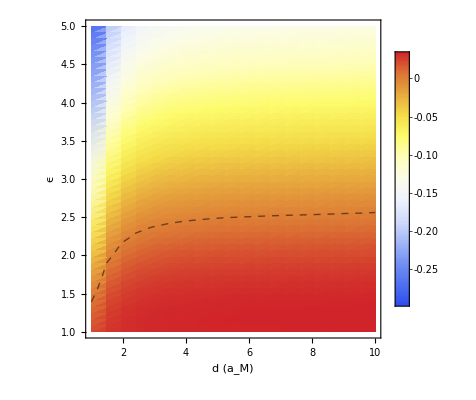

```mathematica
ListDensityPlot[1000Transpose@sweepnu69["final"]-1000Transpose@sweepnu23["final"],DataRange->{sweepnu69["dlist"][[1,{1,-1}]],sweepnu69["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contourzero}]
```

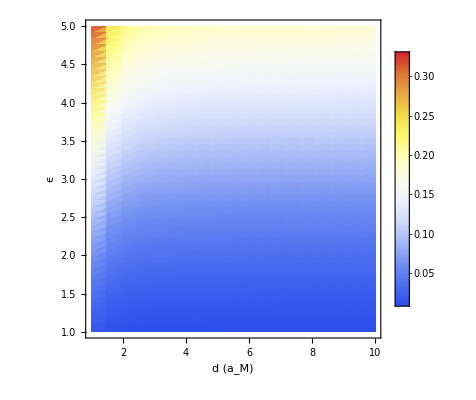

```mathematica
ListDensityPlot[Table[wig[sweepnu69["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu69["spin"]][[1]]},{j,Dimensions[sweepnu69["spin"]][[2]]}],DataRange->{sweepnu69["dlist"][[1,{1,-1}]],sweepnu69["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"}(*,Epilog->{ First@contour}*)]
```

```mathematica
sweepnu69["epsilonlist"][[1,-1]]
```

5.

```mathematica
1000sweepnu69["final"][[20,14]]//MatrixForm
```

798.831

```mathematica
1000*sweepnu69["final"][[20,-1]]//MatrixForm
```

324.862

```mathematica
{Out[565],Out[564]}
```

{-Graphics-,-Graphics-}

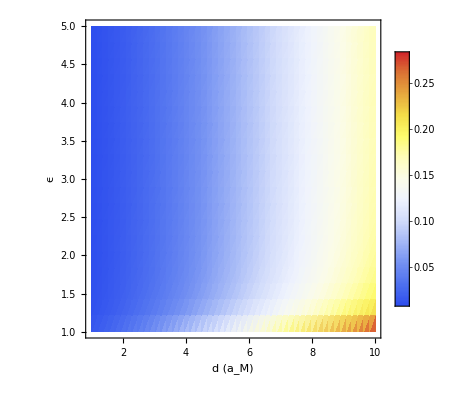

```mathematica
ListDensityPlot[Transpose@sweepnu69["spin"][[All,All,3,4]],DataRange->{sweepnu69["dlist"][[1,{1,-1}]],sweepnu69["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

```mathematica
fboundary=Interpolation[Cases[(First@Normal@contourzero),Line[x_]:>x,Infinity][[1]]]
```

InterpolatingFunction[…]

```mathematica
mask=Transpose@Table[UnitStep[fboundary[i]-j],{i,sweepnu69["dlist"][[1]]},{j,sweepnu69["epsilonlist"][[1]]}];
```

```mathematica
Table[wig[sweepnu23["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu23["spin"]][[1]]},{j,Dimensions[sweepnu23["spin"]][[2]]}]//Dimensions
```

{50,20}

```mathematica
mask//Dimensions
```

{20,50}

```mathematica
density=(1-mask)*Table[wig[sweepnu69["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu69["spin"]][[1]]},{j,Dimensions[sweepnu69["spin"]][[2]]}]+(mask)*Table[wig[sweepnu23["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu23["spin"]][[1]]},{j,Dimensions[sweepnu23["spin"]][[2]]}];
```

```mathematica
gapmask=(1-mask)*1000Transpose[sweepnu69["gap"]]+(mask)*1000Transpose[sweepnu23["gap"]];
```

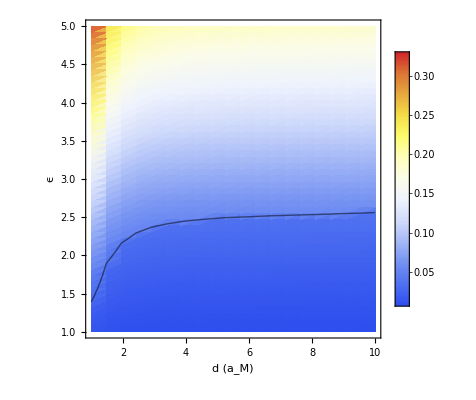

```mathematica
ListDensityPlot[density,DataRange->{sweepnu69["dlist"][[1,{1,-1}]],sweepnu69["epsilonlist"][[1,{1,-1}]]},PlotRangePadding->None,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contourzero}]
```

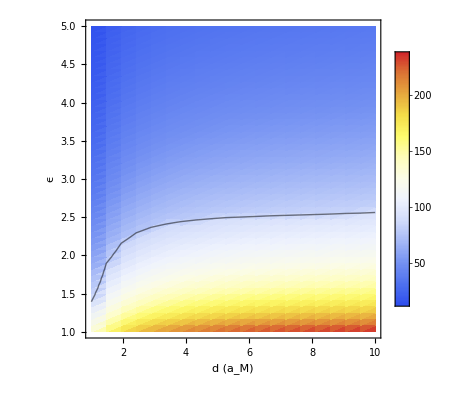

```mathematica
ListDensityPlot[gapmask,DataRange->{sweepnu69["dlist"][[1,{1,-1}]],sweepnu69["epsilonlist"][[1,{1,-1}]]},PlotRangePadding->None,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contourzero}]
```

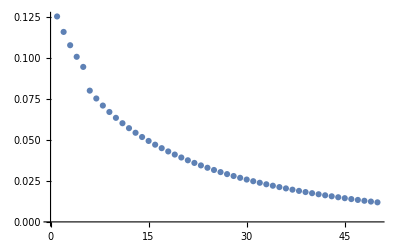

```mathematica
ListPlot[gapmask[[All,1]]]
```

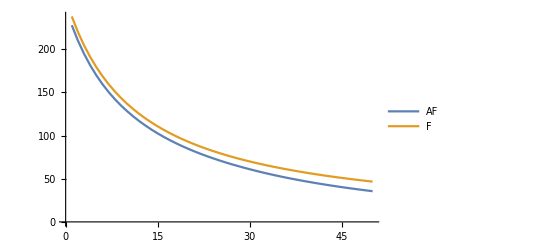

```mathematica
ListLinePlot[{1000Transpose[sweepnu69["gap"]][[All,-1]],1000Transpose[sweepnu23["gap"]][[All,-1]]},PlotLegends->{"AF","F"}]
```

### Sweep_nu=[4,6]

```mathematica
sweepnu46=importmat[NotebookDirectory[]<>"nu4,6_U110.mat"];
```

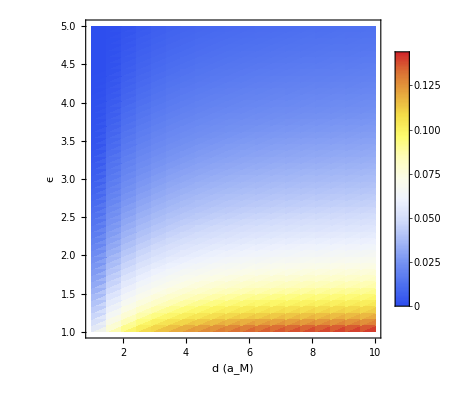

```mathematica
ListDensityPlot[Transpose@sweepnu46["gap"],DataRange->{sweepnu46["dlist"][[1,{1,-1}]],sweepnu46["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"}(*,Epilog->{ First@contour}*)]
```

```mathematica
sweepnu46["gap"]//Dimensions
```

{20,50}

```mathematica
sweepnu46["spin"][[18]][[-1]]//MatrixForm
```

(0.868539 | 0. | 0. | 0.868539
0.868539 | 0. | 0. | 0.868539
0.956591 | 0. | 0. | 0.956591
0.956591 | 0. | 0. | 0.956591
0.17487 | 0. | 0. | 0.17487
0.17487 | 0. | 0. | 0.17487)

### Sweep_nu=[1,4]

```mathematica
sweepnu14=importmat[NotebookDirectory[]<>"nu1,4_U110.mat"];
```

```mathematica
sweepnu14gapline=Table[Block[{data=sweepnu14,thres=.1,last,slice,fint},slice=Tanh[(data["innergap"]/data["gap"])[[i]]];last=FirstPosition[slice,_?(#>thres&)][[1]];fint=Interpolation[Transpose@{slice[[1;;last]],data["epsilonlist"][[1,1;;last]]}];{data["dlist"][[1,i]],fint[thres]}],{i,20}];
```

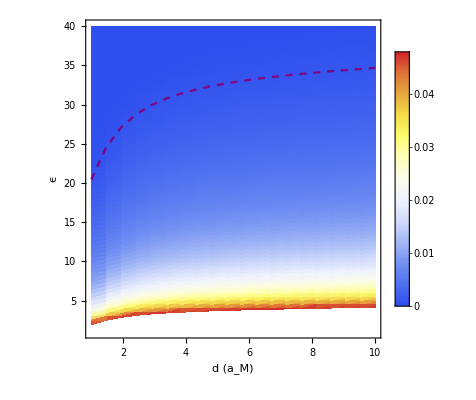

```mathematica
ListDensityPlot[Transpose@sweepnu14["gap"],DataRange->{sweepnu14["dlist"][[1,{1,-1}]],sweepnu14["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@ListLinePlot[sweepnu14gapline,PlotStyle->Directive[Dashed,Purple]]}]
```

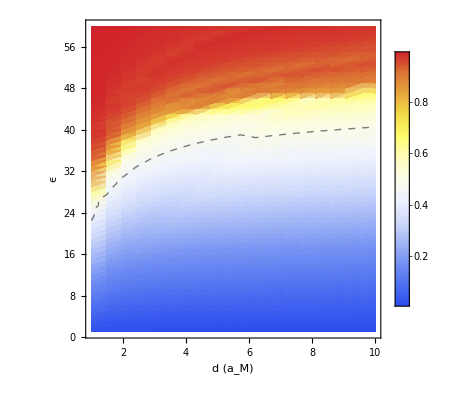

```mathematica
ListDensityPlot[Table[wig[sweepnu14["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu14["spin"]][[1]]},{j,Dimensions[sweepnu14["spin"]][[2]]}],DataRange->{sweepnu14["dlist"][[1,{1,-1}]],sweepnu14["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

### Sweep_nu=[2,8] for F

```mathematica
sweepnu28=importmat[NotebookDirectory[]<>"nu2,8_U110.mat"];
```

```mathematica
sweepnu28gapline=Table[Block[{data=sweepnu28,thres=.1,last,slice,fint},slice=Tanh[(data["innergap"]/data["gap"])[[i]]];last=FirstPosition[slice,_?(#>thres&)][[1]];fint=Interpolation[Transpose@{slice[[1;;last]],data["epsilonlist"][[1,1;;last]]}];{data["dlist"][[1,i]],fint[thres]}],{i,20}]
```

Part::span: 1;;NotFound is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Transpose::nmtx: The first two levels of {{0.000060463,0.0000207382,0.0000363654,0.0000755324,0.000108775,0.000127645,0.00012437,0.0000922327,0.0000928933,0.0003101,0.000292266,0.000210611,0.0000977974,0.0000462698,0.000221433,0.000427329,«19»,0.00163038,0.00094215,0.000181602,0.000656651,0.00115732,0.00143787,0.00174865,0.0020926,0.00247295,0.00255819,0.00239896,0.00219558,0.00163582,0.00101237,0.000318806,«30»}⟦1;;…d⟧,«1»} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{0.000060463,0.0000207382,0.0000363654,0.0000755324,0.000108775,0.000127645,0.00012437,0.0000922327,0.0000928933,0.0003101,0.000292266,0.000210611,0.0000977974,0.0000462698,0.000221433,0.000427329,«20»,0.00094215,0.000181602,0.000656651,0.00115732,0.00143787,0.00174865,0.0020926,0.00247295,0.00255819,0.00239896,0.00219558,0.00163582,0.00101237,0.000318806,«30»}⟦1;;NotFound⟧,«1»}] does not contain a list of data and coordinates.

Part::span: 1;;NotFound is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.0000617418,0.0000241478,0.0000332079,0.0000713609,0.000104134,0.000123333,0.000121377,0.0000916676,0.0000831678,0.000290811,0.000289545,0.00021203,0.000104109,0.0000343686,0.000203288,0.000402326,«19»,0.00179128,0.0011381,0.000416301,0.000378831,0.00106899,0.00133533,0.00163012,0.00195604,0.00231605,0.00262059,0.00247495,0.00231314,0.00191338,0.00133676,0.000695926,«30»}⟦1;;…d⟧,«1»} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{0.0000617418,0.0000241478,0.0000332079,0.0000713609,0.000104134,0.000123333,0.000121377,0.0000916676,0.0000831678,0.000290811,0.000289545,0.00021203,0.000104109,0.0000343686,0.000203288,0.000402326,«20»,0.0011381,0.000416301,0.000378831,0.00106899,0.00133533,0.00163012,0.00195604,0.00231605,0.00262059,0.00247495,0.00231314,0.00191338,0.00133676,0.000695926,«30»}⟦1;;NotFound⟧,«1»}] does not contain a list of data and coordinates.

Transpose::nmtx: The first two levels of {{0.0000632876,0.0000279673,0.0000297914,0.0000668863,0.000099173,0.000118715,0.000118128,0.0000909278,0.0000733869,0.000271287,0.000286442,0.00021315,0.000110189,0.000022657,0.000185327,0.000377546,«19»,0.00191601,0.00129336,0.000605243,0.000152621,0.000985819,0.00124623,0.00152704,0.00183725,0.00217961,0.00255717,0.00252139,0.00237159,0.00212041,0.0015823,0.000984728,«30»}⟦1;;N…nd⟧,«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Interpolation::innd: First argument in Transpose[{{0.0000632876,0.0000279673,0.0000297914,0.0000668863,0.000099173,0.000118715,0.000118128,0.0000909278,0.0000733869,0.000271287,0.000286442,0.00021315,0.000110189,0.000022657,0.000185327,«21»,0.00129336,0.000605243,0.000152621,0.000985819,0.00124623,0.00152704,0.00183725,0.00217961,0.00255717,0.00252139,0.00237159,0.00212041,0.0015823,0.000984728,«30»}⟦1;;NotFound⟧,{{1.,«49»,«30»}}⟦1,1;;N…d⟧}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

{{1.,-184.988},{1.47368,-6.27006×10^6},{1.94737,27.2125},{2.42105,30.1694},{2.89474,32.06},{3.36842,32.8512},{3.84211,25.7968},{4.31579,0.553308},{4.78947,1.17948×10^11},{5.26316,25.844},{5.73684,Interpolation[Transpose[{{0.000060463,0.0000207382,0.0000363654,0.0000755324,0.000108775,0.000127645,0.00012437,0.0000922327,0.0000928933,0.0003101,0.000292266,0.000210611,0.0000977974,0.0000462698,0.000221433,0.000427329,0.0000116359,0.000400021,0.000774155,0.000527382,0.000242004,0.000722238,0.00137854,0.00064309,0.000167092,0.000790669,0.0000740943,0.00102924,0.00178039,0.0019065,0.00128954,0.000609659,0.000135802,0.000950585,0.0018385,0.00163038,0.00094215,0.000181602,0.000656651,0.00115732,0.00143787,0.00174865,0.0020926,0.00247295,0.00255819,0.00239896,0.00219558,0.00163582,0.00101237,0.000318806,0.000452351,0.00131062,0.00226618,0.00333076,0.0042647,0.00403102,0.00375673,0.00343578,0.00306092,0.00262332,0.00211216,0.00151401,0.000812001,0.0000153018,0.000996793,0.0020586,0.00189477,0.00168399,0.00141095,0.00105308,0.000575521,0.0000783371,0.00100855,0.00240698,0.00469439,0.00900929,0.0198756,0.0940723,0.0429596,0.0429619}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{6.21053,Interpolation[Transpose[{{0.0000617418,0.0000241478,0.0000332079,0.0000713609,0.000104134,0.000123333,0.000121377,0.0000916676,0.0000831678,0.000290811,0.000289545,0.00021203,0.000104109,0.0000343686,0.000203288,0.000402326,0.0000812506,0.000444289,0.000672025,0.000596978,0.000155066,0.000591452,0.00144803,0.000739349,0.000042074,0.000896815,0.0000738115,0.000844946,0.00170118,0.00200014,0.00141018,0.000759773,0.0000464736,0.000732898,0.00158212,0.00179128,0.0011381,0.000416301,0.000378831,0.00106899,0.00133533,0.00163012,0.00195604,0.00231605,0.00262059,0.00247495,0.00231314,0.00191338,0.00133676,0.000695926,0.0000154089,0.000805372,0.0016832,0.00265902,0.0037446,0.00420294,0.00396471,0.00368582,0.00336027,0.00298084,0.00253877,0.00202334,0.00142123,0.000715783,0.000114169,0.00109728,0.0020715,0.00190974,0.001702,0.00143349,0.00108245,0.000615504,0.0000212059,0.000921953,0.00226546,0.00443648,0.00844561,0.0180731,0.0699472,0.0387763}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{6.68421,Interpolation[Transpose[{{0.0000632876,0.0000279673,0.0000297914,0.0000668863,0.000099173,0.000118715,0.000118128,0.0000909278,0.0000733869,0.000271287,0.000286442,0.00021315,0.000110189,0.000022657,0.000185327,0.000377546,0.000147442,0.000484945,0.000575325,0.000659529,0.0000684504,0.000471697,0.00146983,0.000822178,0.0000673795,0.000758768,0.000201438,0.000684139,0.00162673,0.0019615,0.00150614,0.000881995,0.000197248,0.000550859,0.00136598,0.00191601,0.00129336,0.000605243,0.000152621,0.000985819,0.00124623,0.00152704,0.00183725,0.00217961,0.00255717,0.00252139,0.00237159,0.00212041,0.0015823,0.000984728,0.000321947,0.000412711,0.00122772,0.00213206,0.00313604,0.00425161,0.00409837,0.00385131,0.00356211,0.00322643,0.00283606,0.00238215,0.00185381,0.00123759,0.000516617,0.000330612,0.00133334,0.00204714,0.0018816,0.00166952,0.00139596,0.00103897,0.000564919,0.0000811283,0.00099362,0.00235229,0.00454298,0.00857478,0.0181906,0.0685008}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{7.15789,Interpolation[Transpose[{{0.0000646646,0.0000313649,0.0000267557,0.0000628973,0.0000947259,0.000114535,0.000115115,0.0000900896,0.0000651221,0.000254458,0.00028334,0.000213742,0.00011513,0.0000127722,0.000169953,0.000356182,0.000202804,0.00051829,0.000494041,0.000710384,3.28041×10^-6,0.000372193,0.00134127,0.000888419,0.000156469,0.000645222,0.000304652,0.000552641,0.00149561,0.00188737,0.00157972,0.00097763,0.00031685,0.000405092,0.00119166,0.00201026,0.00141291,0.00075269,0.0000255798,0.000773367,0.00117308,0.00144231,0.00173953,0.00206731,0.0024285,0.00255001,0.00240971,0.00225434,0.00176664,0.00120364,0.00057971,0.000111042,0.000876091,0.00172374,0.00266318,0.00370501,0.00418295,0.00395985,0.00369943,0.00339641,0.00304449,0.00263609,0.00216201,0.00161096,0.000968957,0.000218432,0.000663339,0.00170695,0.00199576,0.00182071,0.00159688,0.00130844,0.000932088,0.000431934,0.000250229,0.00121715,0.00266447,0.0050189,0.0094233,0.0203239}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{7.63158,Interpolation[Transpose[{{0.0000662003,0.0000350125,0.0000235582,0.0000587121,0.0000900626,0.000110138,0.000111908,0.0000891046,0.0000568733,0.00023748,0.000279955,0.000214124,0.000119935,2.95765×10^-6,0.000154596,0.000334803,0.000256675,0.000502272,0.000377499,0.00075771,0.0000709999,0.000277997,0.00121895,0.000947801,0.00023766,0.000540823,0.000397604,0.00043298,0.00134699,0.00181615,0.00164035,0.00105862,0.000419901,0.000278063,0.00103852,0.00186446,0.00151109,0.000876088,0.000176717,0.000591473,0.00110677,0.00136545,0.00165088,0.00196546,0.00231186,0.00256313,0.00243075,0.00228411,0.00190972,0.00137635,0.000785672,0.000132278,0.000590253,0.00138978,0.00227459,0.0032542,0.00423052,0.00402665,0.00378862,0.00351179,0.00319062,0.00281853,0.00238756,0.00188807,0.00130818,0.000633163,0.000155479,0.00108259,0.00206466,0.001916,0.00172711,0.001486,0.00117551,0.000770169,0.000230474,0.000508415,0.0015622,0.00315465,0.00578665,0.0108567}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{8.10526,Interpolation[Transpose[{{0.0000677023,0.0000385571,0.00002048,0.0000546781,0.0000855522,0.000105855,0.000108729,0.0000880148,0.0000493133,0.000221661,0.000276465,0.000214206,0.000124213,6.06989×10^-6,0.000140305,0.000314803,0.000305864,0.000431929,0.000262773,0.000799726,0.000131994,0.00019291,0.00110775,0.000999252,0.000309192,0.000447997,0.000478806,0.000327385,0.001215,0.00175023,0.00168966,0.00112619,0.000507276,0.000169228,0.000906341,0.001707,0.00159099,0.00097832,0.000303483,0.000437604,0.00104812,0.00129742,0.00157238,0.00187526,0.00220859,0.00256618,0.00244038,0.00230098,0.00202061,0.00151243,0.000949977,0.000328261,0.000358437,0.00111738,0.00195622,0.00288363,0.00390959,0.00406446,0.00384434,0.00358842,0.00329178,0.00294857,0.00255181,0.00209305,0.00156202,0.00094605,0.000229393,0.000608138,0.00159351,0.0019758,0.00181213,0.00160471,0.00134023,0.000999509,0.000553839,0.0000416879,0.000862759,0.0020452,0.00385977,0.00693669}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{8.57895,Interpolation[Transpose[{{0.0000692542,0.0000421371,0.0000173818,0.0000506161,0.000080998,0.000101504,0.000105451,0.0000867885,0.0000420763,0.000206263,0.000272762,0.000214042,0.000128206,0.0000147757,0.000126394,0.000295246,0.00035289,0.000364114,0.000153085,0.000838712,0.000189324,0.000112561,0.00100217,0.00104574,0.000374912,0.000361973,0.000552749,0.000230275,0.00109288,0.00168683,0.0017308,0.00118444,0.000583927,0.0000726186,0.000788104,0.00156538,0.00165776,0.00106561,0.000413276,0.000303045,0.000994148,0.00123478,0.00150008,0.0017922,0.00211353,0.0024667,0.00244052,0.00230731,0.00210735,0.00162131,0.00108363,0.000489668,0.000165777,0.000889337,0.00168819,0.00257029,0.00354474,0.00407981,0.00387449,0.00363585,0.00335946,0.00304006,0.00267142,0.00224606,0.00175494,0.001187,0.000528594,0.000237317,0.00113353,0.00201019,0.00186553,0.00168324,0.00145264,0.00115868,0.000779463,0.00028182,0.000386982,0.00131754,0.00267571,0.00480429}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{9.05263,Interpolation[Transpose[{{0.0000707849,0.0000456666,0.000014339,0.0000466192,0.0000764995,0.0000971747,0.000102135,0.0000854421,2.66201×10^-6,0.000191616,0.000268896,0.000213615,0.000131826,0.0000229877,0.000113107,0.000276458,0.000397224,0.000299543,0.0000493437,0.000874637,0.000243049,0.0000373907,0.000902619,0.00108778,0.000435297,0.00028228,0.000620167,0.000140917,0.000979881,0.00162643,0.00176557,0.00123519,0.00065189,0.0000137612,0.000681546,0.00143717,0.00171432,0.00114107,0.00050943,0.000184182,0.000944427,0.00117707,0.00143346,0.00171568,0.00202599,0.00236687,0.00243431,0.00230645,0.00216534,0.00170965,0.00119389,0.000624465,3.46904×10^-6,0.0006959,0.00145965,0.00230205,0.00323151,0.00407979,0.0038869,0.00366275,0.00340332,0.00310384,0.00275869,0.00236115,0.00190317,0.00137494,0.000764472,0.0000569169,0.000766881,0.00173194,0.00189783,0.00173489,0.00153009,0.00127124,0.000940988,0.0005138,0.0000494123,0.000812845,0.00188757,0.00348432}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{9.52632,Interpolation[Transpose[{{0.0000722747,0.0000490957,0.0000113876,0.0000427317,0.0000721046,0.0000929133,0.0000988178,0.0000839909,0.0000434013,0.00017784,0.0002649,0.000212928,0.000135045,0.0000306459,0.000100538,0.000258562,0.000438671,0.000238482,0.000048166,0.00090756,0.000293109,0.000032923,0.000809087,0.00112573,0.00049074,0.000208481,0.000681636,0.0000586745,0.000875289,0.0015691,0.00179499,0.00127958,0.000712378,0.000091534,0.000585246,0.0013206,0.00176246,0.0012067,0.000594164,0.0000785381,0.000815759,0.00112376,0.00137191,0.00164498,0.00194512,0.0022747,0.00242347,0.00230026,0.00216428,0.00178173,0.00128553,0.000737944,0.000134426,0.000530392,0.00126306,0.00207041,0.00296021,0.00394137,0.00388637,0.00367453,0.00342949,0.00314688,0.0028216,0.00244754,0.00201744,0.00152252,0.000952102,0.000293061,0.000471095,0.00136223,0.00191573,0.00176807,0.00158349,0.00135184,0.00105895,0.000684466,0.000198028,0.000447838,0.00133274,0.0025977}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]},{10.,Interpolation[Transpose[{{0.0000737429,0.0000524698,8.48667×10^-6,0.0000388998,0.0000677529,0.0000886615,0.0000954542,0.0000824183,0.0000445714,0.000164694,0.000260729,0.000211984,0.00013792,0.000037871,0.0000884944,0.000241287,0.000420414,0.000180029,0.000141002,0.000833575,0.000340352,0.000099517,0.000720132,0.00116043,0.000542359,0.000139151,0.000738526,0.0000181789,0.000776974,0.0015138,0.0018147,0.00131888,0.000766948,0.000162479,0.000496654,0.00121324,0.00180379,0.00126445,0.00066983,0.0000166722,0.000699025,0.00107371,0.00131412,0.0015786,0.00186922,0.00218823,0.00240856,0.00228948,0.00215803,0.00184056,0.00136209,0.000834275,0.000252844,0.000387134,0.00109184,0.0018677,0.00272195,0.00366287,0.00387518,0.00367398,0.00344136,0.00317332,0.00286515,0.00251128,0.00210511,0.0016387,0.00110243,0.000484587,0.000229311,0.00105842,0.00192225,0.00178694,0.00161859,0.00140857,0.00114506,0.000811396,0.000383296,0.000175954,0.000925818,0.0019667}⟦1;;NotFound⟧,{{1.,1.49367,1.98734,2.48101,2.97468,3.46835,3.96203,4.4557,4.94937,5.44304,5.93671,6.43038,6.92405,7.41772,7.91139,8.40506,8.89873,9.39241,9.88608,10.3797,10.8734,11.3671,11.8608,12.3544,12.8481,13.3418,13.8354,14.3291,14.8228,15.3165,15.8101,16.3038,16.7975,17.2911,17.7848,18.2785,18.7722,19.2658,19.7595,20.2532,20.7468,21.2405,21.7342,22.2278,22.7215,23.2152,23.7089,24.2025,24.6962,25.1899,25.6835,26.1772,26.6709,27.1646,27.6582,28.1519,28.6456,29.1392,29.6329,30.1266,30.6203,31.1139,31.6076,32.1013,32.5949,33.0886,33.5823,34.0759,34.5696,35.0633,35.557,36.0506,36.5443,37.038,37.5316,38.0253,38.519,39.0127,39.5063,40.}}⟦1,1;;NotFound⟧}]][0.1]}}

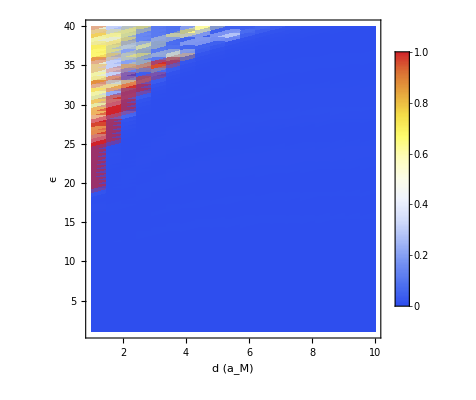

```mathematica
ListDensityPlot[Transpose@Tanh@(sweepnu28["innergap"]/sweepnu28["gap"]),DataRange->{sweepnu28["dlist"][[1,{1,-1}]],sweepnu28["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->{Full,Full,{0,1}},FrameLabel->{"d (a_M)","ϵ"}]
```

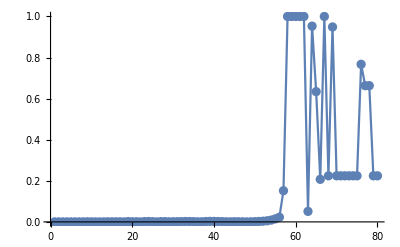

```mathematica
ListLinePlot[Tanh@(sweepnu28["innergap"]/sweepnu28["gap"])[[3]],Mesh->All,PlotRange->All]
```

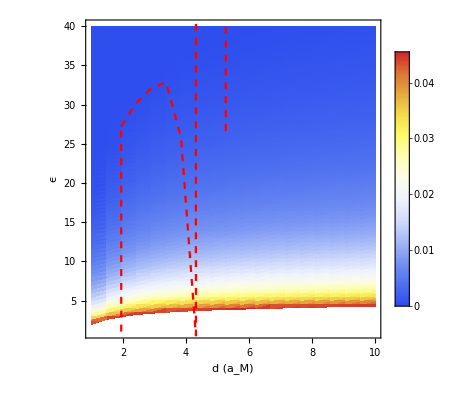

```mathematica
ListDensityPlot[Transpose@sweepnu28["gap"],DataRange->{sweepnu28["dlist"][[1,{1,-1}]],sweepnu28["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@ListLinePlot[sweepnu28gapline,PlotStyle->Directive[Dashed,Red]]}]
```

```mathematica
contourzero=ListContourPlot[Transpose@sweepnu28["final"]-Transpose@sweepnu14["final"],DataRange->{sweepnu14["dlist"][[1,{1,-1}]],sweepnu14["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{0},ContourShading->None(*,ContourStyle->Directive[{Thick,Dashed}]*)]
```

Thread::tdlen: Objects of unequal length in {{0.00973036,0.020532,0.0324565,0.0448338,0.057298,0.0696775,0.0818588,0.0937906,0.105446,0.116799,0.127845,0.13858,0.149001,0.159111,0.168918,0.178423,0.18763,0.196548,0.205182,0.213542},«49»,«30»}+{{-0.00973274,-0.0205333,-0.0324575,-0.0448347,-0.0572988,-0.0696783,«8»,-0.168918,-0.178423,-0.18763,-0.196548,-0.205182,-0.213543},«49»,«10»} cannot be combined.

ListContourPlot::arrayerr: {{-0.00973274,-0.0205333,-0.0324575,-0.0448347,-0.0572988,-0.0696783,-0.0818595,-0.0937913,-0.105447,-0.116799,-0.127846,-0.138581,-0.149002,-0.159112,-0.168918,-0.178423,-0.18763,-0.196548,-0.205182,-0.213543},«49»,«10»}+{{0.00973036,0.020532,0.0324565,0.0448338,0.057298,0.0696775,0.0818588,«7»,0.168918,0.178423,0.18763,0.196548,0.205182,0.213542},«49»,«30»} must be a valid array.

ListContourPlot[{{-0.00973274,-0.0205333,-0.0324575,-0.0448347,-0.0572988,-0.0696783,-0.0818595,-0.0937913,-0.105447,-0.116799,-0.127846,-0.138581,-0.149002,-0.159112,-0.168918,-0.178423,-0.18763,-0.196548,-0.205182,-0.213543},{-0.00559439,-0.0128645,-0.020871,-0.029175,-0.037535,-0.0458371,-0.0540058,-0.0620071,-0.0698232,-0.0774358,-0.0848435,-0.0920421,-0.0990306,-0.10581,-0.112387,-0.118761,-0.124935,-0.130916,-0.136706,-0.142313},{-0.00346886,-0.00896116,-0.0149934,-0.0212442,-0.027535,-0.0337813,-0.0399268,-0.0459463,-0.0518263,-0.0575534,-0.0631261,-0.0685418,-0.0737995,-0.0789,-0.0838477,-0.0886435,-0.0932887,-0.0977884,-0.102145,-0.106364},{-0.00216295,-0.0065846,-0.0114274,-0.0164411,-0.0214848,-0.0264921,-0.0314182,-0.0362433,-0.0409565,-0.0455471,-0.050014,-0.0543551,-0.0585697,-0.0626582,-0.0666244,-0.0704688,-0.0741925,-0.0777997,-0.0812923,-0.0846741},{-0.00127298,-0.00497903,-0.00902688,-0.0132135,-0.0174237,-0.0216026,-0.0257136,-0.0297401,-0.0336733,-0.0375041,-0.0412317,-0.0448543,-0.0483716,-0.0517836,-0.0550935,-0.0583019,-0.0614096,-0.0644202,-0.067335,-0.0701576},{-0.000623948,-0.0038178,-0.00729677,-0.0108915,-0.0145051,-0.0180913,-0.0216188,-0.0250739,-0.0284488,-0.0317359,-0.0349344,-0.0380429,-0.041061,-0.0439888,-0.0468291,-0.0495823,-0.0522492,-0.0548328,-0.0573342,-0.0597565},{-0.00012748,-0.00293649,-0.00598817,-0.0091384,-0.012304,-0.0154449,-0.0185343,-0.0215601,-0.0245157,-0.0273944,-0.0301955,-0.0329178,-0.0355611,-0.0381252,-0.0406128,-0.0430242,-0.04536,-0.0476227,-0.0498137,-0.0519353},{0.000265999,-0.00224318,-0.00496213,-0.00776625,-0.0105829,-0.0133772,-0.0161254,-0.018817,-0.0214461,-0.0240068,-0.0264984,-0.0289201,-0.0312715,-0.0335525,-0.0357654,-0.0379105,-0.0399885,-0.0420016,-0.0439508,-0.0458383},{0.00058651,-0.00168242,-0.00413492,-0.00666189,-0.00919923,-0.0117159,-0.0141909,-0.0166149,-0.0189826,-0.0212886,-0.0235325,-0.0257134,-0.0278311,-0.0298853,-0.0318783,-0.0338103,-0.0356818,-0.0374949,-0.0392505,-0.0409505},{0.00085333,-0.00121874,-0.00345302,-0.00575306,-0.00806168,-0.0103511,-0.0126024,-0.0148073,-0.0169609,-0.0190584,-0.0210994,-0.0230831,-0.0250095,-0.026878,-0.028691,-0.0304484,-0.0321509,-0.0338002,-0.0353973,-0.0369439},{0.00107943,-0.000828341,-0.00288063,-0.00499144,-0.00710933,-0.00920922,-0.011274,-0.0132962,-0.0152713,-0.017195,-0.0190668,-0.0208861,-0.0226529,-0.0243666,-0.0260294,-0.0276412,-0.0292027,-0.0307155,-0.0321804,-0.033599},{0.00127385,-0.000494693,-0.00239288,-0.00434347,-0.00629989,-0.00823934,-0.0101463,-0.0120137,-0.0138377,-0.0156142,-0.0173428,-0.0190229,-0.0206545,-0.0222371,-0.0237728,-0.0252614,-0.0267036,-0.0281008,-0.0294537,-0.030764},{0.00144313,-0.000205916,-0.00197191,-0.00378511,-0.00560306,-0.00740492,-0.00917642,-0.0109112,-0.0126056,-0.0142559,-0.0158616,-0.0174223,-0.0189381,-0.0204083,-0.0218349,-0.0232179,-0.0245577,-0.0258557,-0.0271127,-0.02833},{0.00159208,0.0000467439,-0.00160462,-0.00329868,-0.00499657,-0.00667914,-0.00833324,-0.00995301,-0.011535,-0.0130758,-0.0145751,-0.0160323,-0.0174476,-0.0188204,-0.0201524,-0.0214437,-0.0226948,-0.0239069,-0.0250806,-0.0262173},{0.00172435,0.00026988,-0.00128111,-0.00287089,-0.00446369,-0.00604184,-0.00759317,-0.00911226,-0.0105959,-0.0120409,-0.0134469,-0.0148136,-0.0161409,-0.0174283,-0.0186776,-0.0198887,-0.0210621,-0.0221989,-0.0232998,-0.0243659},{0.00184275,0.000468561,-0.000993822,-0.00249154,-0.00399158,-0.00547758,-0.00693819,-0.00836842,-0.00976522,-0.0111257,-0.0124494,-0.0137361,-0.0149858,-0.0161979,-0.0173741,-0.0185144,-0.0196192,-0.0206896,-0.0217261,-0.02273},{0.00194947,0.000646743,-0.000736831,-0.00215269,-0.00357026,-0.00497431,-0.00635427,-0.00770548,-0.00902508,-0.0103104,-0.0115609,-0.0127765,-0.0139571,-0.0151023,-0.0162135,-0.0172908,-0.0183346,-0.0193459,-0.0203253,-0.0212738},{0.00204629,0.000807566,-0.000505456,-0.00184805,-0.0031918,-0.00452251,-0.00583029,-0.00711078,-0.00836129,-0.00957927,-0.0107643,-0.0119162,-0.0130351,-0.0141203,-0.0151734,-0.0161944,-0.0171835,-0.018142,-0.0190701,-0.019969},{0.00213459,0.000953552,-0.000295941,-0.00157258,-0.00284988,-0.00411456,-0.00535736,-0.00657418,-0.00776249,-0.00891989,-0.010046,-0.0111406,-0.0122038,-0.013235,-0.0142358,-0.015206,-0.016146,-0.0170569,-0.0179389,-0.0187932},{0.00221553,0.00108675,-0.000105235,-0.00132218,-0.00253934,-0.00374428,-0.00492827,-0.00608747,-0.00721949,-0.00832205,-0.0093948,-0.0104375,-0.0114504,-0.0124328,-0.0133862,-0.0143105,-0.015206,-0.0160737,-0.0169141,-0.017728},{0.00229006,0.00120885,0.0000691668,-0.0010935,-0.00225597,-0.00340658,-0.0045371,-0.00564391,-0.00672475,-0.00777745,-0.00880167,-0.00979727,-0.0107644,-0.0117023,-0.0126126,-0.0134951,-0.0143502,-0.0151788,-0.0159811,-0.0167583},{0.00235897,0.00132124,0.000229337,-0.000883751,-0.00199629,-0.00309729,-0.00417897,-0.00523794,-0.00627203,-0.0072792,-0.00825911,-0.00921163,-0.0101369,-0.0110343,-0.0119053,-0.0127496,-0.0135678,-0.0143605,-0.0151282,-0.0158718},{0.00242291,0.00142509,0.000377009,-0.000690623,-0.00175737,-0.00281289,-0.0038498,-0.0048649,-0.00585613,-0.00682155,-0.00776083,-0.00867387,-0.00956082,-0.010421,-0.0112559,-0.0120653,-0.0128495,-0.0136095,-0.0143454,-0.0150582},{0.00248245,0.00152139,0.000513643,-0.000512159,-0.00153678,-0.00255044,-0.00354615,-0.00452089,-0.00547268,-0.00639968,-0.00730157,-0.00817828,-0.00902994,-0.0098559,-0.0106576,-0.0114348,-0.0121878,-0.0129176,-0.0136243,-0.0143088},{0.00253805,0.00161098,0.000640477,-0.000346703,-0.00133242,-0.00230744,-0.00326512,-0.0042026,-0.00511798,-0.0060095,-0.00687688,-0.00772003,-0.00853912,-0.00933348,-0.0101045,-0.010852,-0.0115763,-0.0122781,-0.0129578,-0.0136162},{0.00259014,0.00169456,0.000758569,-0.000192841,-0.00114254,-0.00208177,-0.00300424,-0.00390719,-0.00478886,-0.00564753,-0.00648294,-0.00729503,-0.00808394,-0.00884903,-0.00959165,-0.0103116,-0.0110092,-0.0116852,-0.0123399,-0.0129741},{0.00263904,0.00177277,0.000868829,-0.0000493601,-0.000965606,-0.00187161,-0.00276136,-0.00363226,-0.00448261,-0.00531078,-0.0061165,-0.00689972,-0.00766061,-0.00839852,-0.00911477,-0.00980914,-0.010482,-0.011134,-0.0117655,-0.0123772},{0.00268508,0.00184612,0.00097204,0.0000847897,-0.000800304,-0.00167536,-0.00253465,-0.00337571,-0.00419689,-0.00499665,-0.00577473,-0.00653108,-0.00726588,-0.00797847,-0.00867015,-0.00934072,-0.00999053,-0.0106202,-0.01123,-0.0118208},{0.00272851,0.00191508,0.00106889,0.000210519,-0.000645495,-0.00149167,-0.00232252,-0.00313573,-0.00392969,-0.00470293,-0.00545519,-0.00618646,-0.00689689,-0.00758585,-0.00825461,-0.00890295,-0.00953123,-0.01014,-0.0107297,-0.0113008},{0.00276957,0.00198006,0.00115996,0.000328621,-0.000500185,-0.00131933,-0.00212359,-0.00291072,-0.00367921,-0.00442764,-0.00515576,-0.00586355,-0.00655119,-0.00721804,-0.00786534,-0.00849289,-0.00910102,-0.00969032,-0.0102611,-0.0108139},{0.00280846,0.00204141,0.0012458,0.000439795,-0.000363501,-0.00115731,-0.00193662,-0.00269932,-0.00344393,-0.00416909,-0.00487456,-0.00556035,-0.00622662,-0.00687273,-0.00749992,-0.00810796,-0.0086972,-0.0092682,-0.00982121,-0.0103569},{0.00284537,0.00209945,0.00132684,0.000544651,-0.000234676,-0.00100467,-0.00176056,-0.00250029,-0.00322246,-0.00392577,-0.00460997,-0.00527508,-0.00592126,-0.0065479,-0.00715618,-0.0077459,-0.00831739,-0.00887119,-0.00940755,-0.00992713},{0.00288045,0.00215445,0.00140351,0.000643734,-0.000113031,-0.000860622,-0.00159445,-0.00231257,-0.00301362,-0.00369635,-0.00436053,-0.00500617,-0.00563345,-0.00624175,-0.00683223,-0.0074047,-0.00795948,-0.00849709,-0.00901778,-0.00952217},{0.00291384,0.00220666,0.00147616,0.000737524,2.0337×10^-6,-0.000724426,-0.00143746,-0.00213519,-0.00281633,-0.00347965,-0.00412495,-0.00475224,-0.00536169,-0.00595269,-0.0065264,-0.0070826,-0.00762162,-0.00814397,-0.00864987,-0.00913995},{0.00294567,0.0022563,0.00154511,0.000826449,0.000111055,-0.000595447,-0.00128883,-0.00196731,-0.00262964,-0.00327464,-0.0039021,-0.00451205,-0.00510466,-0.00567933,-0.00623718,-0.00677802,-0.00730215,-0.00781008,-0.00830201,-0.00877856},{0.00297607,0.00230356,0.00161066,0.000910891,0.00021451,-0.000473109,-0.00114791,-0.00180818,-0.00245271,-0.00308037,-0.00369095,-0.0042845,-0.00486118,-0.00542039,-0.00596325,-0.00648955,-0.0069996,-0.00749387,-0.00797259,-0.00843635},{0.00300512,0.00234863,0.00167305,0.000991195,0.000312829,-0.000356901,-0.00101409,-0.00165711,-0.00228478,-0.00289601,-0.0034906,-0.00406861,-0.00463019,-0.00517476,-0.00570341,-0.00621593,-0.00671263,-0.00719397,-0.00766017,-0.0081118},{0.00303292,0.00239165,0.00173253,0.00106767,0.000406395,-0.000246361,-0.000886845,-0.00151349,-0.00212516,-0.0027208,-0.00330023,-0.00386348,-0.00441074,-0.00494141,-0.00545658,-0.00595603,-0.00644006,-0.00690914,-0.00736346,-0.00780358},{0.00305956,0.00243278,0.0017893,0.00114059,0.000495556,-0.000141073,-0.000765683,-0.00137677,-0.00197324,-0.00255407,-0.00311909,-0.00366833,-0.00420197,-0.00471945,-0.0052218,-0.00570883,-0.00618083,-0.00663825,-0.00708127,-0.00751046},{0.00308511,0.00247215,0.00184356,0.0012102,0.000580625,-0.0000406617,-0.000650172,-0.00124646,-0.00182847,-0.00239521,-0.00294651,-0.00348242,-0.00400312,-0.00450804,-0.0049982,-0.00547341,-0.00593396,-0.00638029,-0.00681257,-0.00723135},{0.00310965,0.00250986,0.00189546,0.00127675,0.000661887,0.0000552132,-0.000539914,-0.00112211,-0.00169034,-0.00224367,-0.00278191,-0.00330512,-0.00381349,-0.00430643,-0.00478499,-0.00524894,-0.00569859,-0.00613434,-0.0065564,-0.00696527},{0.00313322,0.00254604,0.00194518,0.00134042,0.000739599,0.00014686,-0.000434552,-0.0010033,-0.00155841,-0.00209893,-0.00262472,-0.00313582,-0.00363243,-0.00411397,-0.00458145,-0.00503467,-0.00547391,-0.00589959,-0.00631189,-0.00671131},{0.0031559,0.00258077,0.00199285,0.00140142,0.000813997,0.000234561,-0.000333759,-0.000889679,-0.00143224,-0.00196055,-0.00247445,-0.00297399,-0.00345937,-0.00393002,-0.00438692,-0.0048299,-0.00525921,-0.00567527,-0.00607825,-0.00646865},{0.00317774,0.00261414,0.00203859,0.00145991,0.000885294,0.000318571,-0.000237236,-0.000780895,-0.00131148,-0.00182811,-0.00233064,-0.00281914,-0.00329379,-0.00375402,-0.00420083,-0.00463401,-0.00505383,-0.0054607,-0.00585477,-0.00623654},{0.00319877,0.00264625,0.00208254,0.00151605,0.000953686,0.000399126,-0.000144713,-0.000676641,-0.00119576,-0.00170123,-0.00219289,-0.00267082,-0.0031352,-0.00358548,-0.00402262,-0.00444643,-0.00485717,-0.00525524,-0.00564079,-0.00601432},{0.00321906,0.00267716,0.0021248,0.00156999,0.00101935,0.000476439,-0.0000559389,-0.000576635,-0.00108478,-0.00157955,-0.00206081,-0.00252862,-0.00298316,-0.00342391,-0.00385179,-0.00426663,-0.00466868,-0.00505832,-0.00543572,-0.00580134},{0.00324724,0.00270693,0.00216546,0.00162185,0.00108246,0.000550707,0.0000293141,-0.000480618,-0.000978243,-0.00146276,-0.00193404,-0.00239216,-0.00283728,-0.00326888,-0.0036879,-0.00409413,-0.00448785,-0.00486942,-0.005239,-0.00559704},{0.00326886,0.00273565,0.00220463,0.00167176,0.00114316,0.000622113,0.000111256,-0.000388349,-0.000875884,-0.00135057,-0.00181228,-0.00226109,-0.00269717,-0.00312001,-0.00353052,-0.0039285,-0.00431423,-0.00468805,-0.00505012,-0.0054009},{0.00329015,0.00276335,0.00224238,0.00171983,0.00120159,0.000690821,0.000190082,-0.000299609,-0.000777456,-0.0012427,-0.00169523,-0.0021351,-0.00256251,-0.00297693,-0.00337926,-0.00376932,-0.00414737,-0.00451376,-0.00486863,-0.00521243},{0.00331157,0.00279011,0.00227879,0.00176616,0.00125788,0.000756987,0.000265968,-0.000214196,-0.000682734,-0.00113891,-0.00158261,-0.0020139,-0.00243296,-0.00283929,-0.00323378,-0.00361623,-0.0039869,-0.00434614,-0.00469409,-0.00503118},{0.0033316,0.00281596,0.00231394,0.00181085,0.00131214,0.000820753,0.000339081,-0.000131922,-0.000591509,-0.00103896,-0.00147417,-0.00189721,-0.00230825,-0.0027068,-0.00309374,-0.00346887,-0.00383245,-0.00418481,-0.0045261,-0.00485675},{0.00335084,0.00284096,0.0023479,0.00185399,0.00136449,0.000882249,0.000409574,-0.0000526144,-0.000503586,-0.000942647,-0.00136968,-0.00178478,-0.0021881,-0.00257917,-0.00295884,-0.00332692,-0.00368367,-0.00402942,-0.0043643,-0.00468875},{0.00336936,0.00286514,0.00238071,0.00189565,0.00141504,0.000941598,0.000477586,0.0000238884,-0.000418787,-0.000849764,-0.00126893,-0.00167638,-0.00207227,-0.00245613,-0.00282879,-0.00319009,-0.00354027,-0.00387965,-0.00420836,-0.00452683},{0.00338721,0.00288855,0.00241245,0.00193592,0.00146387,0.000998913,0.00054325,0.000097735,-0.000336945,-0.000760131,-0.00117171,-0.00157179,-0.00196052,-0.00233743,-0.00270335,-0.00305811,-0.00340195,-0.00373518,-0.00405795,-0.00437066},{0.00340443,0.00291123,0.00244317,0.00197487,0.00151107,0.0010543,0.000606689,0.000169064,-0.000257906,-0.000673578,-0.00107785,-0.00147081,-0.00185263,-0.00222284,-0.00258226,-0.00293071,-0.00326844,-0.00359575,-0.00391278,-0.00421994},{0.00342104,0.00294474,0.00247292,0.00201256,0.00155672,0.00110785,0.000668014,0.000238004,-0.000181525,-0.000589947,-0.000987162,-0.00137326,-0.00174842,-0.00211216,-0.0024653,-0.00280767,-0.0031395,-0.00346109,-0.00377259,-0.00407438},{0.00343708,0.0029687,0.00250174,0.00204906,0.00160091,0.00115967,0.000727333,0.000304675,-0.000107669,-0.00050909,-0.000899491,-0.00127897,-0.00164769,-0.00200518,-0.00235226,-0.00268875,-0.00301489,-0.00333096,-0.00363711,-0.00393372},{0.00345257,0.00299211,0.00252967,0.00208442,0.0016437,0.00120983,0.000784743,0.00036919,-0.0000362125,-0.000430869,-0.000814687,-0.00118776,-0.00155026,-0.00190172,-0.00224294,-0.00257376,-0.00289439,-0.00320513,-0.00350612,-0.00379772},{0.00346755,0.00301482,0.00255676,0.00211869,0.00168516,0.00125841,0.000840338,0.000431653,0.0000329612,-0.000355156,-0.000732609,-0.00109949,-0.00145598,-0.00180161,-0.00213717,-0.00246249,-0.0027778,-0.00308339,-0.00337938,-0.00366615},{0.00348204,0.00303673,0.00258305,0.00215192,0.00172535,0.0013055,0.000894203,0.000492162,0.0000999613,-0.000281831,-0.000653127,-0.00101403,-0.00136469,-0.00170468,-0.00203476,-0.00235478,-0.00266494,-0.00296554,-0.0032567,-0.00353879}}+{{0.00973036,0.020532,0.0324565,0.0448338,0.057298,0.0696775,0.0818588,0.0937906,0.105446,0.116799,0.127845,0.13858,0.149001,0.159111,0.168918,0.178423,0.18763,0.196548,0.205182,0.213542},{0.00557684,0.0128389,0.0208347,0.0291271,0.0374753,0.0457655,0.0539226,0.0619125,0.0697174,0.0773192,0.0847162,0.0919046,0.0988831,0.105653,0.11222,0.118585,0.124751,0.130723,0.136505,0.142104},{0.00344569,0.00893019,0.0149506,0.0211886,0.027466,0.033699,0.0398314,0.045838,0.0517055,0.0574202,0.0629811,0.0683852,0.0736316,0.0787212,0.0836583,0.0884439,0.0930791,0.0975692,0.101917,0.106126},{0.00213576,0.00655166,0.0113838,0.0163852,0.0214163,0.0264108,0.0313244,0.0361371,0.0408383,0.0454171,0.0498726,0.0542026,0.0584064,0.0624844,0.0664404,0.070275,0.0739893,0.0775872,0.0810709,0.0844441},{0.00124194,0.00494468,0.00898327,0.0131588,0.0173575,0.0215247,0.0256241,0.0296392,0.0335613,0.0373813,0.0410983,0.0447107,0.048218,0.0516203,0.0549209,0.0581202,0.0612192,0.0642213,0.0671279,0.0699425},{0.000589037,0.00378193,0.00725314,0.0108381,0.0144413,0.0180168,0.0215338,0.0249784,0.0283432,0.0316203,0.0348092,0.0379083,0.0409174,0.0438364,0.0466682,0.0494131,0.052072,0.0546478,0.0571417,0.0595567},{0.0000886979,0.00289888,0.00594421,0.0090858,0.0122419,0.0153732,0.018453,0.0214693,0.0244156,0.0272853,0.0300776,0.0327914,0.0354264,0.0379825,0.0404623,0.0428661,0.0451946,0.0474503,0.0496344,0.0517494},{-0.000308552,0.00220366,0.00491752,0.00771402,0.0105222,0.0133077,0.0160471,0.0187301,0.0213507,0.0239031,0.0263867,0.0288005,0.0311444,0.033418,0.0356238,0.037762,0.0398334,0.04184,0.0437829,0.0456644},{-0.000632639,0.00164088,0.0040894,0.00660967,0.00913935,0.011648,0.014115,0.0165311,0.0188909,0.0211894,0.0234258,0.0255995,0.0277103,0.0297578,0.0317443,0.0336699,0.0355353,0.0373425,0.0390924,0.0407869},{-0.00090276,0.00117516,0.00340643,0.00570057,0.00800225,0.0102843,0.0125283,0.0147258,0.0168722,0.0189628,0.020997,0.022974,0.024894,0.0267563,0.0285633,0.0303149,0.0320117,0.0336557,0.0352475,0.036789},{-0.00113182,0.00078277,0.00283287,0.00493849,0.00705008,0.00914323,0.0112012,0.0132166,0.015185,0.0171023,0.0189678,0.0207809,0.0225418,0.0242498,0.025907,0.0275135,0.0290698,0.0305776,0.0320376,0.0334516},{-0.00132885,0.000447234,0.00234392,0.00428993,0.00624061,0.00817384,0.0100744,0.0119356,0.0137534,0.0155239,0.0172466,0.018921,0.0205472,0.0221244,0.0236549,0.0251386,0.0265759,0.0279685,0.029317,0.0306229},{-0.00150033,0.000156719,0.0019218,0.00373093,0.00554362,0.00733974,0.00910536,0.0108343,0.0125229,0.0141676,0.0157678,0.0173232,0.0188339,0.0202991,0.021721,0.0230992,0.0244346,0.0257283,0.0269811,0.0281944},{-0.0016511,-0.000097495,0.00155341,0.00324386,0.00493692,0.00661415,0.00826275,0.00987706,0.0114537,0.0129892,0.0144833,0.0159356,0.0173461,0.0187142,0.0200418,0.0213287,0.0225756,0.0237836,0.0249535,0.0260864},{-0.00178479,-0.00032198,0.00122892,0.00281547,0.00440381,0.00597698,0.00752316,0.00903712,0.0105157,0.0119558,0.0133569,0.0147189,0.0160417,0.0173248,0.0185699,0.0197769,0.0209463,0.0220793,0.0231765,0.0242392},{-0.00190423,-0.000521789,0.000940775,0.00243559,0.0039315,0.00541282,0.0068686,0.00829399,0.00968601,0.0110418,0.012361,0.0136432,0.0148887,0.0160966,0.0172689,0.0184053,0.0195064,0.0205732,0.0216063,0.0226069},{-0.00201165,-0.000700874,0.000683077,0.00209631,0.00351001,0.00490967,0.00628506,0.0076317,0.00894678,0.0102276,0.0114739,0.0126852,0.0138619,0.0150031,0.0161106,0.0171843,0.0182246,0.0192325,0.0202086,0.021154},{-0.0021088,-0.000862371,0.000451155,0.00179134,0.00313148,0.00445804,0.00576149,0.00703764,0.00828386,0.00949764,0.0106786,0.0118265,0.0129416,0.014023,0.0150726,0.0160901,0.0170759,0.0180312,0.0189563,0.0198522},{-0.00219713,-0.00100881,0.000241257,0.00151567,0.00278956,0.00405032,0.005289,0.0065017,0.00768592,0.00883931,0.00996149,0.0110523,0.0121119,0.0131396,0.014137,0.0151039,0.0160407,0.0169485,0.0178276,0.0186791},{-0.00227781,-0.00114224,0.0000503352,0.0012652,0.00247913,0.00368033,0.0048604,0.00601567,0.00714378,0.00824252,0.00931151,0.0103506,0.0113601,0.012339,0.0132892,0.0142103,0.0151028,0.0159677,0.0168052,0.0176164},{-0.00235181,-0.00126435,-0.000124116,0.00103657,0.00219598,0.00334303,0.00446979,0.00557284,0.00664993,0.00769897,0.0087196,0.00971172,0.0106755,0.0116102,0.0125174,0.0133969,0.0142491,0.0150749,0.0158746,0.0166492},{-0.00241994,-0.00137656,-0.000284173,0.000827024,0.00193662,0.00303421,0.0041123,0.00516765,0.00619815,0.00720179,0.00817825,0.00912744,0.0100495,0.0109438,0.0118118,0.0126532,0.0134686,0.0142587,0.0150238,0.015765},{-0.00248288,-0.00148005,-0.000431574,0.000634226,0.00169815,0.00275038,0.00378384,0.00479546,0.00578323,0.00674526,0.00768122,0.00859104,0.00947491,0.0103321,0.0111641,0.0119707,0.0127523,0.0135096,0.0142431,0.0149536},{-0.00254121,-0.0015758,-0.000567785,0.000456222,0.00147811,0.0024886,0.00348099,0.00445237,0.00540083,0.00632455,0.00722324,0.00809684,0.00894554,0.00976859,0.0105675,0.011342,0.0120925,0.0128197,0.0135241,0.0142063},{-0.00259543,-0.00166467,-0.000694053,0.000291353,0.00127443,0.00224638,0.00320084,0.00413507,0.00504723,0.00593559,0.00679987,0.00764002,0.00845623,0.00924778,0.0100161,0.010761,0.0114828,0.0121822,0.0128596,0.0135158},{-0.00264595,-0.00174739,-0.000811441,0.000138198,0.00108532,0.00202158,0.00294092,0.00384074,0.00471928,0.00557489,0.0064073,0.00721647,0.0080026,0.00876496,0.00950497,0.0102224,0.0109176,0.0115913,0.0122437,0.0128757},{-0.00269315,-0.00182458,-0.000920867,-4.46062×10^-6,0.000909256,0.00181237,0.00269909,0.00356695,0.00441426,0.00523946,0.00604227,0.00682267,0.00758085,0.00831611,0.00902982,0.00972174,0.0103923,0.011042,0.0116713,0.0122809},{-0.00273735,-0.00189678,-0.00102312,-0.000137679,0.000744929,0.00161717,0.00247351,0.00331161,0.00412985,0.00492672,0.00570196,0.00645557,0.00718773,0.00789775,0.00858697,0.00925515,0.00990267,0.0105301,0.0111379,0.0117265},{-0.00277883,-0.00196447,-0.0011189,-0.000262373,0.000591189,0.0014346,0.00226259,0.00307291,0.003864,0.00463443,0.00538394,0.00611254,0.00682041,0.00750686,0.00817321,0.00881922,0.00944527,0.0100519,0.0106395,0.0112087},{-0.00281782,-0.00202807,-0.00120881,-0.000379344,0.000447036,0.00126348,0.00206494,0.00284926,0.00361495,0.00436064,0.00508608,0.00579127,0.00647641,0.00714081,0.00778576,0.00841104,0.00901699,0.00960419,0.0101729,0.0107238},{-0.00285456,-0.00208794,-0.00129337,-0.000489295,0.000311592,0.00110275,0.00187932,0.00263927,0.00338115,0.00410364,0.0048065,0.00548974,0.00615357,0.0067973,0.00742219,0.00802801,0.00861512,0.00918407,0.0097351,0.0102689},{-0.00288923,-0.00214439,-0.00137305,-0.000592846,0.000184086,0.000951476,0.00170468,0.00244172,0.00316123,0.00386192,0.00454357,0.00520619,0.00584999,0.00647429,0.00708033,0.00766788,0.00823728,0.00878907,0.0093235,0.00984121},{-0.00292199,-0.00219773,-0.00144828,-0.000690544,0.0000638335,0.000808853,0.00154005,0.00225553,0.00295398,0.00363415,0.00429583,0.00493905,0.00556399,0.00617,0.00675829,0.00732864,0.00788137,0.00841702,0.0089358,0.00943836},{-0.00295301,-0.00224819,-0.0015194,-0.000782876,-0.0000497719,0.00067415,0.00138459,0.00207975,0.00275833,0.00341916,0.00406201,0.00468692,0.00529408,0.00588285,0.0064544,0.00700852,0.00754554,0.00806595,0.00856998,0.00905826},{-0.00298242,-0.00229602,-0.00158676,-0.000870276,-0.00015727,0.000546721,0.00123756,0.00191351,0.00257334,0.00321588,0.00384095,0.00444857,0.00503893,0.00561141,0.00616716,0.00670595,0.00722811,0.00773414,0.00822424,0.00869903},{-0.00301034,-0.0023414,-0.00165065,-0.000953132,-0.000259145,0.00042599,0.00109828,0.00175606,0.00239814,0.00302339,0.00363163,0.00422289,0.00479737,0.00535444,0.00589522,0.00641951,0.00692763,0.00742004,0.00789696,0.00835898},{-0.00303689,-0.00238453,-0.00171134,-0.00103179,-0.000355829,0.000311437,0.000966155,0.00160672,0.00223198,0.00284085,0.00343314,0.00400891,0.00456832,0.00511079,0.0056374,0.00614795,0.00664275,0.00712226,0.00758669,0.00803661},{-0.00307781,-0.00242557,-0.00176905,-0.00110657,-0.000447712,0.000202598,0.000840642,0.00146487,0.00207417,0.0026675,0.00324466,0.00380572,0.00435085,0.00487946,0.00539262,0.00589013,0.0063723,0.00683957,0.00729214,0.00773058},{-0.00310333,-0.00246467,-0.001824,-0.00117775,-0.000535145,0.000099054,0.000721253,0.00132996,0.0019241,0.00250266,0.00306545,0.00361253,0.00414409,0.00465953,0.00515991,0.00564503,0.0061152,0.00657083,0.00701214,0.00743967},{-0.00312761,-0.00250197,-0.00187639,-0.00124558,-0.000618445,4.24654×10^-7,0.00060755,0.0012015,0.00178121,0.00234571,0.00289483,0.00342862,0.00394726,0.00445017,0.0049384,0.00541174,0.00587048,0.00631505,0.00674564,0.00716279},{-0.00315074,-0.00253758,-0.0019264,-0.0013103,-0.000697901,-0.0000936333,0.000499134,0.00107902,0.00164499,0.00219611,0.0027322,0.00325332,0.00375966,0.00425065,0.00472729,0.0051894,0.00563727,0.0060713,0.00649168,0.00689894},{-0.00317279,-0.00257162,-0.00197418,-0.00137212,-0.000773774,-0.000183432,0.000395643,0.000962112,0.00151499,0.00205334,0.00257701,0.00308606,0.00358067,0.00406027,0.00452588,0.00497728,0.00541477,0.00583875,0.0062494,0.00664723},{-0.00319384,-0.00260419,-0.00201988,-0.00143123,-0.000846302,-0.000269256,0.000296747,0.000850412,0.00139078,0.00191695,0.00242876,0.00292628,0.00340969,0.00387843,0.00433349,0.00477468,0.00520226,0.00561664,0.006018,0.00640683},{-0.00321395,-0.00263538,-0.00206364,-0.0014878,-0.000915704,-0.000351365,0.000202145,0.000743574,0.00127199,0.00178651,0.00228699,0.0027735,0.0032462,0.00370457,0.00414955,0.00458096,0.00499908,0.00540429,0.00579676,0.00617699},{-0.00323319,-0.00266529,-0.00210557,-0.001542,-0.000982177,-0.000429996,0.000111563,0.000641285,0.00115826,0.00166165,0.00215129,0.00262725,0.00308972,0.00353815,0.0039735,0.00439557,0.00480463,0.00520106,0.00558504,0.00595703},{-0.00325161,-0.00269398,-0.00214579,-0.00159397,-0.0010459,-0.000505366,0.0000247481,0.000543261,0.00104929,0.00154201,0.00202127,0.00248714,0.00293981,0.00337873,0.00380484,0.00421796,0.00461835,0.00500639,0.00538222,0.00574633},{-0.00326927,-0.00272153,-0.0021844,-0.00164385,-0.00110705,-0.000577674,-0.0000585301,0.000449239,0.000944773,0.00142727,0.00189658,0.00235278,0.00279605,0.00322586,0.00364313,0.00404767,0.00443975,0.00481973,0.00518776,0.00554432},{-0.0032862,-0.00274802,-0.0022215,-0.00169176,-0.00116578,-0.000647105,-0.000138485,0.000358978,0.000844445,0.00131713,0.0017769,0.00222383,0.00265808,0.00307914,0.00348792,0.00388424,0.00426835,0.0046406,0.00500115,0.00535046},{-0.00330246,-0.00277349,-0.00225717,-0.00173782,-0.00122222,-0.000713828,-0.000215311,0.000272257,0.000748058,0.00121133,0.00166193,0.00209995,0.00252555,0.00293822,0.00333885,0.00372727,0.00410372,0.00446855,0.00482192,0.00516427},{-0.00331808,-0.00281454,-0.0022915,-0.00178213,-0.00127651,-0.000777998,-0.00028919,0.000188869,0.000655383,0.00110961,0.00155141,0.00198087,0.00239815,0.00280275,0.00319556,0.00357638,0.00394548,0.00430318,0.00464965,0.0049853},{-0.00333269,-0.00283923,-0.00232456,-0.0018248,-0.00132877,-0.00083976,-0.000360289,0.000108627,0.000566209,0.00101173,0.00144507,0.00186629,0.00227558,0.00267243,0.0030577,0.00343123,0.00379325,0.0041441,0.00448392,0.00481315},{-0.00334985,-0.002863,-0.00235642,-0.0018659,-0.00137912,-0.000899247,-0.000428762,0.0000313539,0.000480342,0.000917491,0.00134268,0.00175598,0.00215757,0.00254696,0.00292499,0.00329149,0.0036467,0.00399095,0.00432439,0.00464743},{-0.00336663,-0.00288589,-0.00238714,-0.00190553,-0.00142765,-0.000956583,-0.000494752,-0.0000431112,0.000397599,0.000826685,0.00124403,0.0016497,0.00204388,0.00242608,0.00279713,0.00315686,0.00350552,0.00384342,0.0041707,0.00448778},{-0.00338743,-0.00290794,-0.00241678,-0.00194377,-0.00147446,-0.00101188,-0.000558393,-0.00011492,0.000317814,0.000739129,0.00114891,0.00154723,0.00193427,0.00230954,0.00267386,0.00302707,0.00336941,0.00370119,0.00402254,0.00433387},{-0.00340718,-0.00292921,-0.0024454,-0.00198068,-0.00151964,-0.00106525,-0.000619808,-0.000184211,0.000240829,0.00065465,0.00105714,0.00144837,0.00182852,0.0021971,0.00255494,0.00290187,0.00323812,0.00356399,0.00387962,0.00418541},{-0.00342443,-0.00294973,-0.00247306,-0.00201633,-0.00156328,-0.0011168,-0.000679112,-0.000251116,0.0001665,0.000573089,0.00096854,0.00135293,0.00172643,0.00208857,0.00244015,0.00278101,0.00311137,0.00343155,0.00374166,0.00404211},{-0.00344091,-0.00296955,-0.00249979,-0.00205079,-0.00160546,-0.0011666,-0.000736412,-0.000315757,0.0000946913,0.000494297,0.000882953,0.00126074,0.00162782,0.00198373,0.00232927,0.00266427,0.00298896,0.00330363,0.00360841,0.00390369},{-0.00345634,-0.00298869,-0.00254312,-0.00208412,-0.00164624,-0.00121475,-0.000791809,-0.000378246,0.0000252765,0.000418135,0.000800227,0.00117163,0.00153251,0.00188241,0.00222211,0.00255145,0.00287064,0.00318,0.00347963,0.00376993},{-0.00347126,-0.0030072,-0.00256905,-0.00211637,-0.0016857,-0.00126134,-0.000845396,-0.000438689,-0.0000418625,0.000344474,0.000720219,0.00108545,0.00144033,0.00178442,0.00211847,0.00244234,0.00275623,0.00306045,0.0033551,0.00364058},{-0.00348568,-0.00304109,-0.00259413,-0.00214759,-0.00172389,-0.00130643,-0.000897261,-0.000497185,-0.000106836,0.000273191,0.000642797,0.00100206,0.00135114,0.0016896,0.0020182,0.00233677,0.00264554,0.00294478,0.00323462,0.00351543},{-0.00349965,-0.00306205,-0.0026184,-0.00217784,-0.00176089,-0.0013501,-0.000947485,-0.000553828,-0.000169747,0.000204174,0.000567838,0.000921328,0.0012648,0.00159781,0.00192112,0.00223457,0.00253837,0.0028328,0.00311798,0.00339427},{-0.00351317,-0.00308274,-0.0026419,-0.00220715,-0.00179673,-0.00139241,-0.000996145,-0.000608704,-0.000230693,0.000137316,0.000495227,0.000843123,0.00118116,0.0015089,0.0018271,0.00213558,0.00243457,0.00272434,0.00300501,0.00327693},{-0.00352627,-0.0031036,-0.00267698,-0.00225334,-0.00183149,-0.00143343,-0.00104331,-0.000661894,-0.000289764,0.000072516,0.000424853,0.00076733,0.0011001,0.00142274,0.00173597,0.00203965,0.00233399,0.00261924,0.00289554,0.00316322},{-0.00353896,-0.00312281,-0.00270584,-0.00228173,-0.0018652,-0.00147321,-0.00108906,-0.000713476,-0.000347046,9.68159×10^-6,0.000356616,0.000693841,0.0010215,0.00133919,0.00164762,0.00194664,0.00223646,0.00251734,0.0027894,0.00305298},{-0.00355127,-0.00314141,-0.00273051,-0.00230927,-0.00189791,-0.00151181,-0.00113344,-0.00076352,-0.000402618,-0.0000512759,0.000290419,0.00062255,0.000945264,0.00125815,0.00156192,0.00185643,0.00214186,0.0024185,0.00268645,0.00294604},{-0.00356322,-0.00315948,-0.00275498,-0.00235559,-0.00192967,-0.00154928,-0.00117653,-0.000812096,-0.000456558,-0.00011044,0.000226173,0.000553361,0.000871273,0.00117951,0.00147875,0.00176887,0.00205006,0.00232258,0.00258654,0.00284227},{-0.00357481,-0.003177,-0.00277902,-0.00238466,-0.0019789,-0.00158568,-0.00121836,-0.000859267,-0.000508934,-0.000167887,0.000163791,0.000486182,0.000799433,0.00110314,0.001398,0.00168387,0.00196093,0.00222946,0.00248954,0.00274153},{-0.00358606,-0.00319402,-0.0028024,-0.00241346,-0.00203181,-0.00162104,-0.00125901,-0.000905092,-0.000559816,-0.000223693,0.000103194,0.000420927,0.000729651,0.00102897,0.00131957,0.0016013,0.00187436,0.002139,0.00239533,0.00264368},{-0.003597,-0.00321055,-0.00282453,-0.00244236,-0.00206524,-0.0016554,-0.00129852,-0.00094963,-0.000609265,-0.000277926,0.0000443059,0.000357514,0.00066184,0.000956897,0.00124336,0.00152107,0.00179024,0.00205111,0.00230379,0.0025486},{-0.00360763,-0.00322662,-0.00284603,-0.00246925,-0.00209806,-0.00173409,-0.00133693,-0.000992933,-0.000657341,-0.000330652,-0.0000129441,0.000295865,0.000595918,0.000886831,0.00116926,0.00144308,0.00170847,0.00196568,0.0022148,0.00245617},{-0.00361796,-0.00324224,-0.00286694,-0.00249538,-0.00212996,-0.00177111,-0.0013743,-0.00103505,-0.000704101,-0.000381933,-0.0000686236,0.000235909,0.000531807,0.000818689,0.00109721,0.00136723,0.00162895,0.00188259,0.00212827,0.00236629},{-0.00362801,-0.00325744,-0.00288727,-0.00252081,-0.00216039,-0.00180705,-0.00146121,-0.00107603,-0.000749599,-0.000431828,-0.000122797,0.000177577,0.000469433,0.000752395,0.00102711,0.00129345,0.00155158,0.00180176,0.00204408,0.00227885},{-0.00363778,-0.00327222,-0.00290705,-0.00254555,-0.00218999,-0.00184144,-0.00150088,-0.00111593,-0.000793884,-0.000480392,-0.000175523,0.000120803,0.000408726,0.000687875,0.000958888,0.00122163,0.00147629,0.0017231,0.00196215,0.00219376},{-0.0036473,-0.00328661,-0.00292631,-0.00256961,-0.0022188,-0.00187489,-0.00153887,-0.00121101,-0.000837005,-0.000527677,-0.000226861,0.0000655255,0.00034962,0.000625057,0.000892466,0.00115172,0.00140299,0.00164651,0.00188238,0.00211091},{-0.00365657,-0.00330062,-0.00294506,-0.00259306,-0.00224687,-0.00190747,-0.00157587,-0.00125231,-0.000879007,-0.000573735,-0.000276864,0.0000116864,0.000292053,0.000563875,0.000827775,0.00108362,0.0013316,0.00157192,0.0018047,0.00203023},{-0.00366559,-0.00331426,-0.00296333,-0.00261589,-0.00227419,-0.0019392,-0.00161191,-0.00129256,-0.000981414,-0.000618611,-0.000325584,-0.00004077,0.000235966,0.000504266,0.000764748,0.00101728,0.00126204,0.00149925,0.00172902,0.00195162},{-0.00367439,-0.00332756,-0.00298112,-0.00263814,-0.00230081,-0.00197013,-0.00164703,-0.00133176,-0.00102461,-0.000662351,-0.000373069,-0.0000918962,0.000181302,0.000446171,0.000703321,0.000952624,0.00119425,0.00142843,0.00165526,0.00187502},{-0.00368296,-0.00334052,-0.00299847,-0.00265982,-0.00232677,-0.00200026,-0.00168126,-0.00136999,-0.00106671,-0.000771766,-0.000419366,-0.000141742,0.000128007,0.000389532,0.000643435,0.000889589,0.00112817,0.00135939,0.00158335,0.00180034},{-0.00369132,-0.00335316,-0.00301537,-0.00268097,-0.00235207,-0.00202965,-0.00171463,-0.00140725,-0.00110776,-0.000816493,-0.000533426,-0.000190356,0.0000760309,0.000334295,0.000585032,0.000828117,0.00106372,0.00129206,0.00151323,0.00172751},{-0.00369947,-0.00336548,-0.00303187,-0.00270159,-0.00237675,-0.00205831,-0.00174717,-0.00144359,-0.00114781,-0.000860125,-0.000580552,-0.000308936,0.0000253251,0.000280408,0.000528057,0.000768148,0.00100085,0.00122638,0.00144482,0.00165646}},DataRange→{{1.,10.},{1.,30.}},ColorFunction→TemperatureMap,PlotLegends→Automatic,FrameLabel→{d (a_M),ϵ},Contours→{0},ContourShading→None]

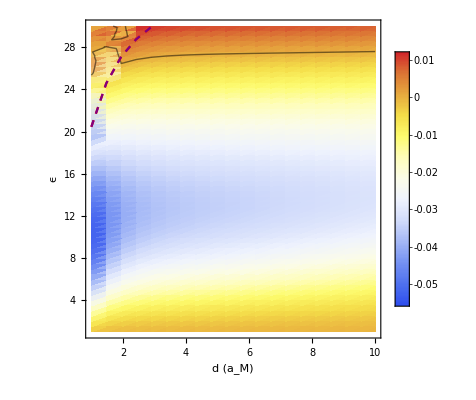

```mathematica
ListDensityPlot[1000Transpose@sweepnu28["final"]-1000Transpose@sweepnu14["final"],DataRange->{sweepnu14["dlist"][[1,{1,-1}]],sweepnu14["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contourzero,First@ListLinePlot[sweepnu14gapline,PlotStyle->Directive[Dashed,Red]],First@ListLinePlot[sweepnu14gapline,PlotStyle->Directive[Dashed,Purple]]}]
```

### Sweep_nu=[3,4]

```mathematica
sweepnu34=importmat[NotebookDirectory[]<>"nu3,4_U110.mat"];
```

```mathematica
contour=ListContourPlot[1000Transpose@sweepnu34["gap"],DataRange->{sweepnu34["dlist"][[1,{1,-1}]],sweepnu34["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Contours->{.25},ContourShading->None,ContourStyle->Directive[{Thick,Dashed}]];
```

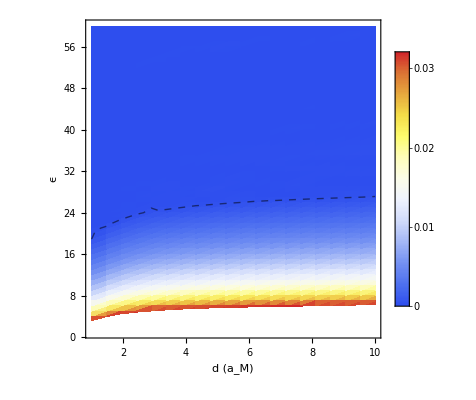

```mathematica
ListDensityPlot[Transpose@sweepnu34["gap"],DataRange->{sweepnu34["dlist"][[1,{1,-1}]],sweepnu34["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

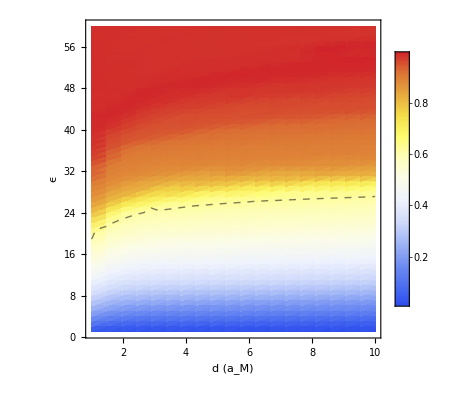

```mathematica
ListDensityPlot[Table[wig[sweepnu34["spin"][[i,j,All,1]]],{i,Dimensions[sweepnu34["spin"]][[1]]},{j,Dimensions[sweepnu34["spin"]][[2]]}],DataRange->{sweepnu34["dlist"][[1,{1,-1}]],sweepnu34["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},Epilog->{ First@contour}]
```

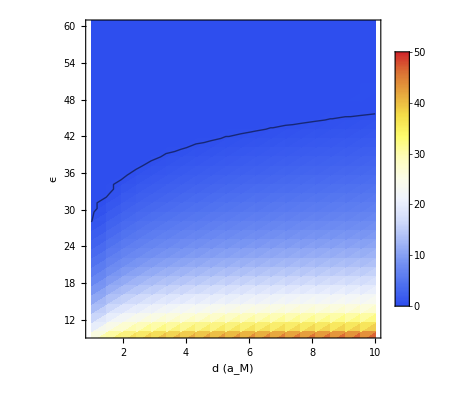

```mathematica
ListDensityPlot[1000Transpose@sweepWCepd1["gap"],DataRange->{sweepWCepd1["dlist"][[1,{1,-1}]],sweepWCepd1["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},PlotRange->{{1,10},{10,60},1000{0,0.05}},Epilog->{ First@contour1}]
```

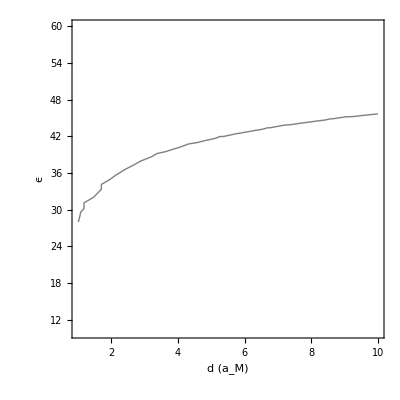

```mathematica
contour1=ListContourPlot[1000Transpose@sweepWCepd1["gap"],DataRange->{sweepWCepd1["dlist"][[1,{1,-1}]],sweepWCepd1["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},PlotRange->{{1,10},{10,60},1000{0,0.05}},Contours->{.2},ContourShading->None]
```

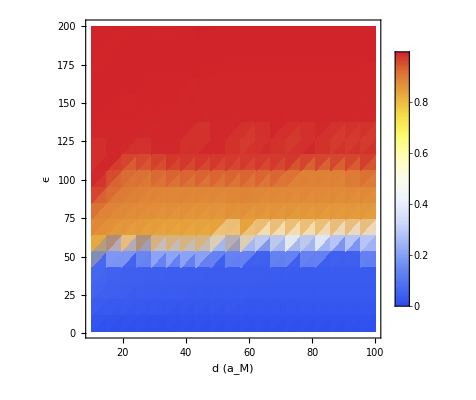

```mathematica
ListDensityPlot[Table[wig[sweepWCepd["spin"][[i,j,All,1]]],{i,20},{j,20}],DataRange->{{10,100},sweepWCepd["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"}]
```

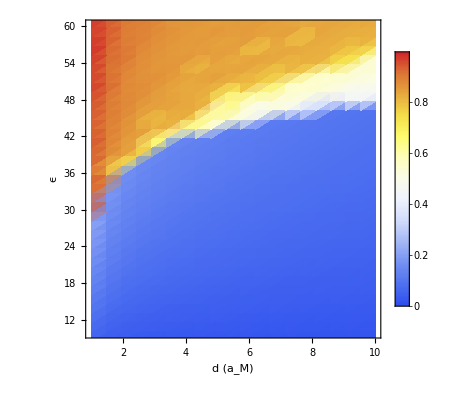

```mathematica
ListDensityPlot[Table[wig[sweepWCepd1["spin"][[i,j,All,1]]],{i,Dimensions[sweepWCepd1["spin"]][[1]]},{j,Dimensions[sweepWCepd1["spin"]][[2]]}],DataRange->{sweepWCepd1["dlist"][[1,{1,-1}]],sweepWCepd1["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},PlotRange->{{1,10},{10,60}}]
```

```mathematica
ListDensityPlot[Table[wig[sweepWCepd1["spin"][[i,j,All,1]]],{i,Dimensions[sweepWCepd1["spin"]][[1]]},{j,Dimensions[sweepWCepd1["spin"]][[2]]}],DataRange->{sweepWCepd1["dlist"][[1,{1,-1}]],sweepWCepd1["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},PlotRange->{{1,10},{10,60}}]
```

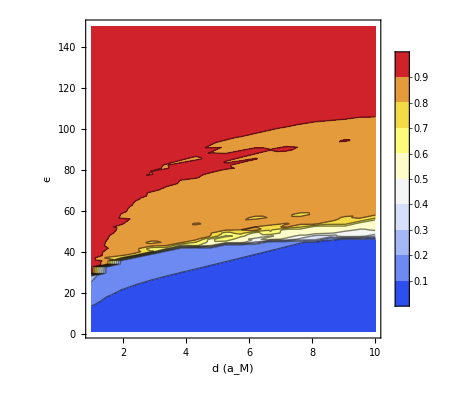

```mathematica
ListContourPlot[Table[wig[sweepWCepd1["spin"][[i,j,All,1]]],{i,Dimensions[sweepWCepd1["spin"]][[1]]},{j,Dimensions[sweepWCepd1["spin"]][[2]]}],DataRange->{sweepWCepd1["dlist"][[1,{1,-1}]],sweepWCepd1["epsilonlist"][[1,{1,-1}]]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"d (a_M)","ϵ"},PlotRange->Full]
```

```mathematica
Table[wig[sweepWCepd1["spin"][[i,1,All,1]]],{i,20}]
```

{0.00125726,0.00586508,0.0129962,0.0218786,0.0319179,0.0426813,0.0538655,0.0652626,0.0767332,0.0881852,0.0995592,0.110818,0.121939,0.13291,0.143724,0.154378,0.164873,0.175208,0.185386,0.195407}

```mathematica
sweepWCepd1["spin"]//Dimensions
```

{80,20,3,4}

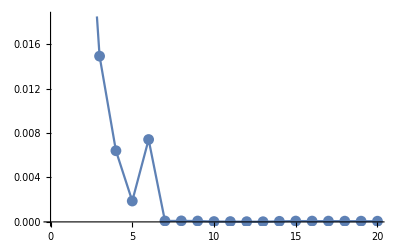

```mathematica
ListLinePlot[sweepWCepd["gap"][[10]],Mesh->All]
```

```mathematica
sweepWCepd["gap"][[10,6]]
```

0.00742018

```mathematica
ListPlot[sweepWCepd["gap"]]
```

```mathematica
Table[wig[sweepWCepd["spin"][[1,j,All,1]]],{j,20}]
```

```mathematica
Integrate[Exp[I*q*r*Cos[θ]],{θ,0,2π},{r,L,∞},Assumptions->{q>0,r>0,L>0}]
```

Integrate::idiv: Integral of ⅇ^(ⅈ q r Cos[θ]) does not converge on {L,∞}.

Integrate[ⅇ^(ⅈ q r Cos[θ]),{θ,0,2 π},{r,L,∞},Assumptions→{q>0,r>0,L>0}]

```mathematica
Integrate[Exp[I*q*r*Cos[θ]]/r^3,{θ,0,2π},{r,L,∞},Assumptions->{q>0,r>0,L>0}]
```

$Aborted

```mathematica
Integrate[BesselJ[0, r],{r,1,∞}]
```

1/2 (2-π BesselJ[1,1] StruveH[0,1]+BesselJ[0,1] (-2+π StruveH[1,1]))

```mathematica
Simplify[Series[1/r-1/(√(r^2+d^2))/.r->1/x,{x,0,3}]/.x->1/r,r>0]
```

SeriesData::sdatv: First argument 1/r is not a valid variable.

1/2 d^2 (1/r)^3+O[1/r]^4

```mathematica
Integrate[Exp[I*r*Cos[θ]]/r^3,{θ,0,2π},Assumptions->{r>0}]
```

(2 π BesselJ[0,r])/r^3

```mathematica
Integrate[Out[140],{r,1,∞}]//N
```

1.34028

```mathematica
Integrate[Exp[I*ρ*q*Cos[θ]]/1,{θ,0,2π},Assumptions->{ρ>0,q>0}]
```

2 π BesselJ[0,q ρ]

```mathematica
Integrate[x/(√(x^2+d^2))BesselJ[0,x],{x,0,∞},Assumptions->{d>0}]
```

ⅇ^-d

```mathematica
r3=Integrate[Integrate[Exp[I*q*r*Cos[θ]]/r^2,{θ,0,2π},Assumptions->{q>0,r>0}],{r,L,∞},Assumptions->{q>0,L>0}]
```

π (-2 q+q BesselJ[1,L q] (-2+L π q StruveH[0,L q])+(BesselJ[0,L q] (2+2 L^2 q^2-L^2 π q^2 StruveH[1,L q]))/L)

```mathematica
r1=Integrate[Integrate[Exp[I*q*r*Cos[θ]]/1,{θ,0,2π},Assumptions->{q>0,r>0}],{r,L,∞},Assumptions->{q>0,L>0}]
```

π (2/q-L π BesselJ[1,L q] StruveH[0,L q]+L BesselJ[0,L q] (-2+π StruveH[1,L q]))

```mathematica
r3/.q->0/.L->10.
```

0.628319

```mathematica
Integrate[Exp[I*q*r*Cos[θ]]/1,{θ,0,2π},Assumptions->{q>0,r>0}]
```

2 π BesselJ[0,q r]

```mathematica
r1/.q->0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
r3/.q->qnormrect
```

{π (1/π-L π BesselJ[1,2 L π] StruveH[0,2 L π]+L BesselJ[0,2 L π] (-2+π StruveH[1,2 L π]))}

```mathematica
Dot[r3/.q->qnormhex,nhex]-Dot[r3/.q->qnormrect,nrect]/.L->Range[1000.,10000.,1000.]
```

{-0.00351263-2.44051×10^-19 ⅈ,-0.0019447+5.38326×10^-19 ⅈ,0.00097557-8.89099×10^-18 ⅈ,-0.00183707-1.05281×10^-17 ⅈ,-0.00115753-1.41675×10^-18 ⅈ,0.000496279+7.71578×10^-18 ⅈ,-0.00134178+3.50383×10^-19 ⅈ,-0.000823489+1.29516×10^-18 ⅈ,0.000270023-3.73306×10^-18 ⅈ,-0.00105412-5.24844×10^-18 ⅈ}

```mathematica
Limit[Dot[r1/.q->qnormhex,nhex]-Dot[r1/.q->qnormrect,nrect],L->∞]
```

$Aborted

```mathematica
Series[BesselJ[0,1/x],{x,0,3}]
```

(-1)^Floor[(π+Arg[x])/(2 π)] (Cos[-1/x+π/4+O[x]^4]+(-1)^Floor[Arg[x]/π] Cos[-1/x+π/4+O[x]^4]+ⅈ Cos[1/x+π/4+O[x]^4]-ⅈ (-1)^Floor[Arg[x]/π] Cos[1/x+π/4+O[x]^4]) ((√x)/(√(2 π))-(9 x^(5/2))/(128 √(2 π))+O[x]^(7/2))+(-1)^Floor[(π+Arg[x])/(2 π)] (-x^(3/2)/(8 √(2 π))+O[x]^(7/2)) (Sin[-1/x+π/4+O[x]^4]+(-1)^Floor[Arg[x]/π] Sin[-1/x+π/4+O[x]^4]-ⅈ Sin[1/x+π/4+O[x]^4]+ⅈ (-1)^Floor[Arg[x]/π] Sin[1/x+π/4+O[x]^4])

```mathematica
FullSimplify[Integrate[Cos[r-π/4]/(√r),r],r>0]
```

1/2 (-Gamma[1/2,-ⅈ r]-Gamma[1/2,ⅈ r])

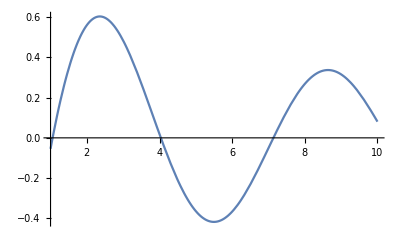

```mathematica
Plot[Out[252],{r,1,10}]
```

```mathematica
FullSimplify[Integrate[Cos[r-π/4]/(r^2 √r),r],r>0]
```

-(√2 (Cos[r]+2 r Cos[r]+Sin[r]-(1-ⅈ) r (r ExpIntegralE[1/2,-ⅈ r]+ⅈ r ExpIntegralE[1/2,ⅈ r]+(1+ⅈ) Sin[r])))/(3 r^(3/2))

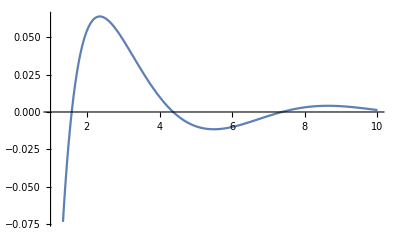

```mathematica
Plot[Out[253],{r,1,10}]
```

### Gap bar plot-U35

```mathematica
nu11=importmat[NotebookDirectory[]<>"nu1,1_d10_ep10.mat"];
```

```mathematica
nu12=importmat[NotebookDirectory[]<>"nu1,2_d10_ep10.mat"];
```

```mathematica
nu13=importmat[NotebookDirectory[]<>"nu1,3_d10_ep10.mat"];
```

```mathematica
nu23=importmat[NotebookDirectory[]<>"nu2,3_d10_ep10.mat"];
```

```mathematica
nu14=importmat[NotebookDirectory[]<>"nu1,4_d10_ep10.mat"];
```

```mathematica
nu34=importmat[NotebookDirectory[]<>"nu3,4_d10_ep10.mat"];
```

```mathematica
nugap=1000#[["gap"]]&/@{nu11,nu12,nu13,nu23,nu14,nu34}//Flatten
```

{19.2988,17.2324,12.0477,21.9933,18.2094,18.6078}

```mathematica
nuenergy=#[["final"]]&/@{nu11,nu12,nu13,nu23,nu14,nu34}//Flatten
```

{0.0579792,0.0631341,0.0253989,0.117888,0.012666,0.151524}

```mathematica
nu={1,1/2,1/3,2/3,1/4,3/4}
```

{1,1/2,1/3,2/3,1/4,3/4}

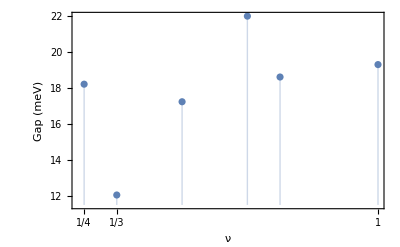

```mathematica
gapU35=ListPlot[Transpose@{nu,nugap},Filling->Axis,FrameTicks->{nu,Automatic},Frame->True,FrameLabel->{"ν","Gap (meV)"},PlotRange->Full]
```

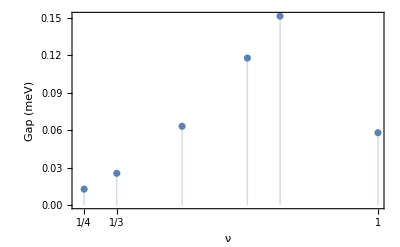

```mathematica
eU35=ListPlot[Transpose@{nu,nuenergy},Filling->Axis,FrameTicks->{nu,Automatic},Frame->True,FrameLabel->{"ν","Gap (meV)"},PlotRange->Full]
```

### Gap bar plot-U110

```mathematica
nu11U110=importmat[NotebookDirectory[]<>"nu1,1_d10_ep10_U110.mat"];
```

```mathematica
nu12U110=importmat[NotebookDirectory[]<>"nu1,2_d10_ep10_U110.mat"];
```

```mathematica
nu13U110=importmat[NotebookDirectory[]<>"nu1,3_d10_ep10_U110.mat"];
```

```mathematica
nu23U110=importmat[NotebookDirectory[]<>"nu2,3_d10_ep10_U110.mat"];
```

```mathematica
nu14U110=importmat[NotebookDirectory[]<>"nu1,4_d10_ep10_U110.mat"];
```

```mathematica
nu34U110=importmat[NotebookDirectory[]<>"nu3,4_d10_ep10_U110.mat"];
```

```mathematica
nu25U110=importmat[NotebookDirectory[]<>"nu2,5_d10_ep10_U110.mat"];
```

```mathematica
nu35U110=importmat[NotebookDirectory[]<>"nu3,5_d10_ep10_U110.mat"]
```

```mathematica
nu17U110=importmat[NotebookDirectory[]<>"nu1,7_d10_ep10_U110.mat"];
```

```mathematica
nugapU110=1000#[["gap"]]&/@{nu11U110,nu12U110,nu13U110,nu23U110,nu14U110,nu34U110,nu25U110,nu17U110}//Flatten
```

{35.651,15.6806,12.6745,22.5587,16.8082,17.4109,12.8348,11.8657}

```mathematica
nugap
```

{19.2988,17.2324,12.0477,21.9933,18.2094,18.6078}

```mathematica
nuenergyU110=#[["final"]]&/@{nu11U110,nu12U110,nu13U110,nu23U110,nu14U110,nu34U110,nu25U110,nu17U110}//Flatten//Flatten
```

{0.36932,0.0860719,0.035495,0.158449,0.0184515,0.202976,0.0532693,0.00470445}

```mathematica
nu={1,1/2,1/3,2/3,1/4,3/4,2/5,1/7}
```

{1,1/2,1/3,2/3,1/4,3/4,2/5,1/7}

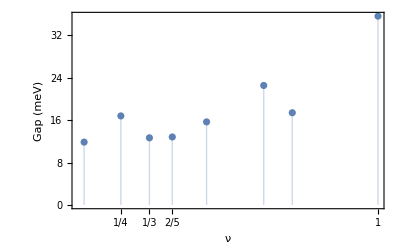

```mathematica
gapU110=ListPlot[Transpose@{nu,nugapU110},Filling->Axis,FrameTicks->{nu,Automatic},Frame->True,FrameLabel->{"ν","Gap (meV)"},PlotRange->Full,BaseStyle->(FontSize->16)]
```

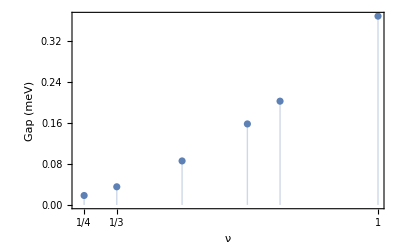

```mathematica
eU110=ListPlot[Transpose@{nu,nuenergyU110},Filling->Axis,FrameTicks->{nu,Automatic},Frame->True,FrameLabel->{"ν","Gap (meV)"},PlotRange->Full]
```

### Gap bar plot-U223

```mathematica
nu11U223=importmat[NotebookDirectory[]<>"nu1,1_d10_ep10_U223.mat"];
```

```mathematica
nu12U223=importmat[NotebookDirectory[]<>"nu1,2_d10_ep10_U223.mat"];
```

```mathematica
nu13U223=importmat[NotebookDirectory[]<>"nu1,3_d10_ep10_U223.mat"];
```

```mathematica
nu23U223=importmat[NotebookDirectory[]<>"nu2,3_d10_ep10_U223.mat"];
```

```mathematica
nu14U223=importmat[NotebookDirectory[]<>"nu1,4_d10_ep10_U223.mat"];
```

```mathematica
nu34U223=importmat[NotebookDirectory[]<>"nu3,4_d10_ep10_U223.mat"];
```

```mathematica
nugapU223=1000#[["gap"]]&/@{nu11U223,nu12U223,nu13U223,nu23U223,nu14U223,nu34U223}//Flatten
```

{35.6925,13.0263,11.7204,21.6697,14.7325,15.4241}

```mathematica
nugapU110
```

{35.8142,15.8818,12.7938,22.6127,17.0777,17.5408}

```mathematica
nuenergyU223=#[["final"]]&/@{nu11U223,nu12U223,nu13U223,nu23U223,nu14U223,nu34U223}//Flatten//Flatten
```

{0.409832,0.0963884,0.0400704,0.176508,0.021138,0.225862}

```mathematica
nuenergyU110
```

{0.369321,0.0860738,0.0354958,0.15845,0.0184542,0.202977}

```mathematica
nu={1,1/2,1/3,2/3,1/4,3/4}
```

{1,1/2,1/3,2/3,1/4,3/4}

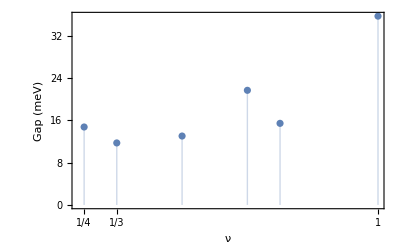

```mathematica
gapU223=ListPlot[Transpose@{nu,nugapU223},Filling->Axis,FrameTicks->{nu,Automatic},Frame->True,FrameLabel->{"ν","Gap (meV)"},PlotRange->Full]
```

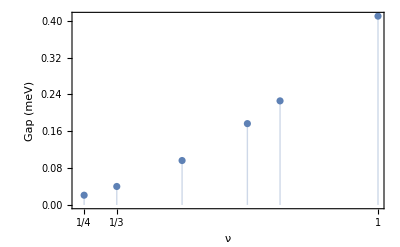

```mathematica
eU223=ListPlot[Transpose@{nu,nuenergyU223},Filling->Axis,FrameTicks->{nu,Automatic},Frame->True,FrameLabel->{"ν","Gap (meV)"},PlotRange->Full]
```

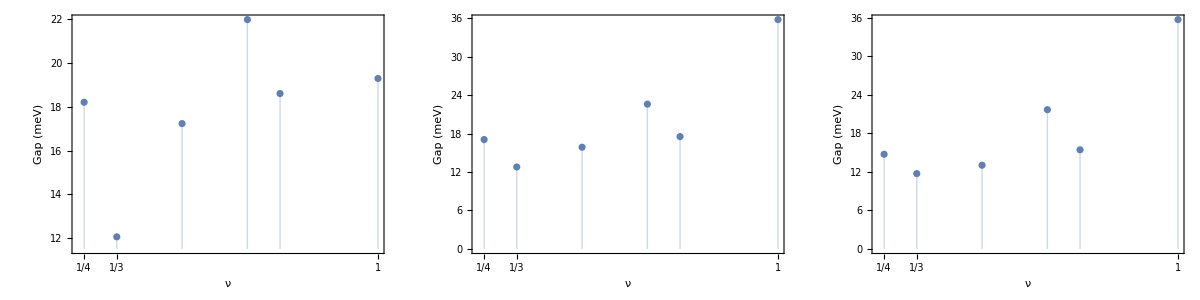

```mathematica
Grid@{{Out[122],Out[127],Out[227]}}
```

```mathematica
Grid@{{Out[12],Out[127],Out[227]}}
```

## lattice energy

```mathematica
f[ξ_,ϕ_,s_]:=Sin[ϕ]^s Sum[(ξ k^2+1/ξ l^2+2 k l Cos[ϕ])^-s+(ξ k^2+1/ξ l^2-2 k l Cos[ϕ])^-s,{k,1,400},{l,1,400}]+Zeta[3]*(ξ^s+ξ^-s)
```

```mathematica
f[1/(√3),ArcCos[(√3)/2],1.5]
```

6.54881

```mathematica
f[1,ArcCos[1/2],1.5]
```

4.90562

```mathematica
ArcCos[1/2]
```

π/3

```mathematica
Zeta[3]//N
```

1.20206

```mathematica
1/(√3)//N
```

0.57735

```mathematica
(√3)/2//N
```

0.866025

## DOS

```mathematica
dos12=importmat[NotebookDirectory[]<>"dos_nu1,2.mat"];
```

```mathematica
dos13=importmat[NotebookDirectory[]<>"dos_nu1,3.mat"];
```

```mathematica
dos23=importmat[NotebookDirectory[]<>"dos_nu2,3.mat"];
```

```mathematica
dos14=importmat[NotebookDirectory[]<>"dos_nu1,4.mat"];
```

```mathematica
dos34=importmat[NotebookDirectory[]<>"dos_nu3,4.mat"];
```

```mathematica
dos15=importmat[NotebookDirectory[]<>"dos_nu1,5.mat"];
```

```mathematica
dos17=importmat[NotebookDirectory[]<>"dos_nu1,7.mat"];
```

```mathematica
dos11=importmat[NotebookDirectory[]<>"dos_nu1,1.mat"];
```

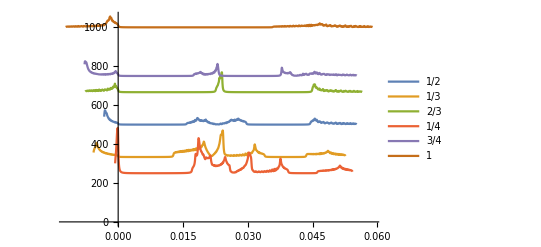

```mathematica
With[{shift=1000},ListLinePlot[{Transpose@{dos12["Elist"][[1]],shift*1/2+dos12["dos"][[1]]},Transpose@{dos13["Elist"][[1]],shift*1/3+dos13["dos"][[1]]},Transpose@{dos23["Elist"][[1]],shift*2/3+dos23["dos"][[1]]},Transpose@{dos14["Elist"][[1]],shift/4+dos14["dos"][[1]]},Transpose@{dos34["Elist"][[1]],shift*3/4+dos34["dos"][[1]]},Transpose@{dos11["Elist"][[1]],shift+dos11["dos"][[1]]}},PlotLegends->{"1/2","1/3","2/3","1/4","3/4","1"}]]
```

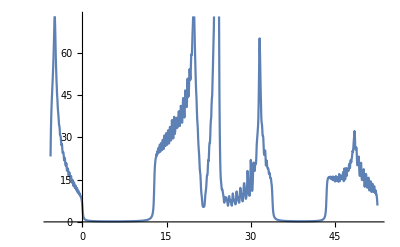

```mathematica
ListLinePlot[Transpose@{1*^3dos13["Elist"][[1]],dos13["dos"][[1]]}]
```

```mathematica
Transpose@{dos12["Elist"][[1]],dos12["dos"][[1]],ConstantArray[1/2,Length[dos12["Elist"][[1]]]]}
```

{{-0.00324167,40.8744,1/2},{-0.00318317,56.3791,1/2},{-0.00312466,67.9987,1/2},{-0.00306616,73.9005,1/2},{-0.00300766,73.2293,1/2},{-0.00294916,68.6946,1/2},{-0.00289066,64.8369,1/2},{-0.00283215,63.3745,1/2},{-0.00277365,60.8998,1/2},{-0.00271515,59.6076,1/2},{-0.00265665,58.4254,1/2},{-0.00259814,53.8185,1/2},{-0.00253964,47.6765,1/2},{-0.00248114,44.5338,1/2},{-0.00242264,41.7288,1/2},{-0.00236414,38.7514,1/2},{-0.00230563,36.1098,1/2},{-0.00224713,33.3634,1/2},{-0.00218863,30.6915,1/2},{-0.00213013,30.5819,1/2},{-0.00207163,30.1559,1/2},{-0.00201312,27.2861,1/2},{-0.00195462,24.3837,1/2},{-0.00189612,23.6607,1/2},{-0.00183762,24.6222,1/2},{-0.00177912,24.4872,1/2},{-0.00172061,21.4649,1/2},{-0.00166211,19.6763,1/2},{-0.00160361,19.5003,1/2},{-0.00154511,19.862,1/2},{-0.0014866,19.5452,1/2},{-0.0014281,18.2663,1/2},{-0.0013696,16.7268,1/2},{-0.0013111,16.7814,1/2},{-0.0012526,16.5889,1/2},{-0.00119409,15.4494,1/2},{-0.00113559,15.0806,1/2},{-0.00107709,15.0876,1/2},{-0.00101859,14.6899,1/2},{-0.000960085,14.2926,1/2},{-0.000901583,12.9339,1/2},{-0.000843081,12.1826,1/2},{-0.000784579,13.008,1/2},{-0.000726077,13.4028,1/2},{-0.000667575,12.2367,1/2},{-0.000609073,10.8128,1/2},{-0.000550571,10.6275,1/2},{-0.000492068,11.3407,1/2},{-0.000433566,11.4831,1/2},{-0.000375064,9.85054,1/2},{-0.000316562,9.32295,1/2},{-0.00025806,9.70541,1/2},{-0.000199558,9.25454,1/2},{-0.000141056,8.17126,1/2},{-0.0000825535,7.54967,1/2},{-0.0000240514,6.20124,1/2},{0.0000344507,4.4359,1/2},{0.0000929529,3.0407,1/2},{0.000151455,2.21587,1/2},{0.000209957,1.73095,1/2},{0.000268459,1.42195,1/2},{0.000326961,1.20945,1/2},{0.000385463,1.05436,1/2},{0.000443966,0.935931,1/2},{0.000502468,0.84229,1/2},{0.00056097,0.766196,1/2},{0.000619472,0.702995,1/2},{0.000677974,0.649561,1/2},{0.000736476,0.603716,1/2},{0.000794978,0.563896,1/2},{0.00085348,0.528947,1/2},{0.000911983,0.497999,1/2},{0.000970485,0.470381,1/2},{0.00102899,0.445568,1/2},{0.00108749,0.423143,1/2},{0.00114599,0.40277,1/2},{0.00120449,0.384175,1/2},{0.001263,0.367132,1/2},{0.0013215,0.351451,1/2},{0.00138,0.336975,1/2},{0.0014385,0.323571,1/2},{0.001497,0.311123,1/2},{0.00155551,0.299533,1/2},{0.00161401,0.288717,1/2},{0.00167251,0.278601,1/2},{0.00173101,0.26912,1/2},{0.00178951,0.260217,1/2},{0.00184802,0.251843,1/2},{0.00190652,0.243954,1/2},{0.00196502,0.23651,1/2},{0.00202352,0.229475,1/2},{0.00208203,0.222819,1/2},{0.00214053,0.216514,1/2},{0.00219903,0.210532,1/2},{0.00225753,0.204853,1/2},{0.00231603,0.199454,1/2},{0.00237454,0.194317,1/2},{0.00243304,0.189424,1/2},{0.00249154,0.18476,1/2},{0.00255004,0.180311,1/2},{0.00260854,0.176062,1/2},{0.00266705,0.172002,1/2},{0.00272555,0.168119,1/2},{0.00278405,0.164404,1/2},{0.00284255,0.160846,1/2},{0.00290105,0.157437,1/2},{0.00295956,0.154169,1/2},{0.00301806,0.151034,1/2},{0.00307656,0.148026,1/2},{0.00313506,0.145136,1/2},{0.00319357,0.14236,1/2},{0.00325207,0.139692,1/2},{0.00331057,0.137126,1/2},{0.00336907,0.134658,1/2},{0.00342757,0.132283,1/2},{0.00348608,0.129995,1/2},{0.00354458,0.127793,1/2},{0.00360308,0.12567,1/2},{0.00366158,0.123625,1/2},{0.00372008,0.121653,1/2},{0.00377859,0.119751,1/2},{0.00383709,0.117917,1/2},{0.00389559,0.116147,1/2},{0.00395409,0.114438,1/2},{0.0040126,0.11279,1/2},{0.0040711,0.111198,1/2},{0.0041296,0.10966,1/2},{0.0041881,0.108175,1/2},{0.0042466,0.106741,1/2},{0.00430511,0.105355,1/2},{0.00436361,0.104016,1/2},{0.00442211,0.102721,1/2},{0.00448061,0.101471,1/2},{0.00453911,0.100262,1/2},{0.00459762,0.099093,1/2},{0.00465612,0.0979634,1/2},{0.00471462,0.0968714,1/2},{0.00477312,0.0958157,1/2},{0.00483162,0.0947953,1/2},{0.00489013,0.0938088,1/2},{0.00494863,0.0928553,1/2},{0.00500713,0.0919337,1/2},{0.00506563,0.0910429,1/2},{0.00512414,0.0901821,1/2},{0.00518264,0.0893504,1/2},{0.00524114,0.0885469,1/2},{0.00529964,0.0877707,1/2},{0.00535814,0.0870212,1/2},{0.00541665,0.0862974,1/2},{0.00547515,0.0855989,1/2},{0.00553365,0.0849248,1/2},{0.00559215,0.0842745,1/2},{0.00565065,0.0836474,1/2},{0.00570916,0.0830429,1/2},{0.00576766,0.0824604,1/2},{0.00582616,0.0818994,1/2},{0.00588466,0.0813595,1/2},{0.00594317,0.08084,1/2},{0.00600167,0.0803405,1/2},{0.00606017,0.0798606,1/2},{0.00611867,0.0793999,1/2},{0.00617717,0.0789579,1/2},{0.00623568,0.0785342,1/2},{0.00629418,0.0781286,1/2},{0.00635268,0.0777406,1/2},{0.00641118,0.0773698,1/2},{0.00646968,0.0770161,1/2},{0.00652819,0.076679,1/2},{0.00658669,0.0763583,1/2},{0.00664519,0.0760537,1/2},{0.00670369,0.075765,1/2},{0.0067622,0.0754919,1/2},{0.0068207,0.0752341,1/2},{0.0068792,0.0749915,1/2},{0.0069377,0.0747638,1/2},{0.0069962,0.0745508,1/2},{0.00705471,0.0743524,1/2},{0.00711321,0.0741684,1/2},{0.00717171,0.0739987,1/2},{0.00723021,0.0738429,1/2},{0.00728871,0.0737011,1/2},{0.00734722,0.0735732,1/2},{0.00740572,0.0734589,1/2},{0.00746422,0.0733581,1/2},{0.00752272,0.0732708,1/2},{0.00758122,0.0731969,1/2},{0.00763973,0.0731363,1/2},{0.00769823,0.073089,1/2},{0.00775673,0.0730548,1/2},{0.00781523,0.0730337,1/2},{0.00787374,0.0730256,1/2},{0.00793224,0.0730306,1/2},{0.00799074,0.0730486,1/2},{0.00804924,0.0730796,1/2},{0.00810774,0.0731236,1/2},{0.00816625,0.0731805,1/2},{0.00822475,0.0732504,1/2},{0.00828325,0.0733334,1/2},{0.00834175,0.0734294,1/2},{0.00840025,0.0735384,1/2},{0.00845876,0.0736606,1/2},{0.00851726,0.0737959,1/2},{0.00857576,0.0739445,1/2},{0.00863426,0.0741064,1/2},{0.00869277,0.0742817,1/2},{0.00875127,0.0744705,1/2},{0.00880977,0.0746728,1/2},{0.00886827,0.0748889,1/2},{0.00892677,0.0751188,1/2},{0.00898528,0.0753626,1/2},{0.00904378,0.0756206,1/2},{0.00910228,0.0758927,1/2},{0.00916078,0.0761794,1/2},{0.00921928,0.0764806,1/2},{0.00927779,0.0767965,1/2},{0.00933629,0.0771275,1/2},{0.00939479,0.0774737,1/2},{0.00945329,0.0778352,1/2},{0.00951179,0.0782125,1/2},{0.0095703,0.0786056,1/2},{0.0096288,0.0790149,1/2},{0.0096873,0.0794407,1/2},{0.0097458,0.0798832,1/2},{0.00980431,0.0803427,1/2},{0.00986281,0.0808197,1/2},{0.00992131,0.0813144,1/2},{0.00997981,0.0818271,1/2},{0.0100383,0.0823583,1/2},{0.0100968,0.0829084,1/2},{0.0101553,0.0834778,1/2},{0.0102138,0.0840668,1/2},{0.0102723,0.0846761,1/2},{0.0103308,0.0853059,1/2},{0.0103893,0.085957,1/2},{0.0104478,0.0866297,1/2},{0.0105063,0.0873247,1/2},{0.0105648,0.0880425,1/2},{0.0106233,0.0887837,1/2},{0.0106818,0.089549,1/2},{0.0107403,0.0903391,1/2},{0.0107988,0.0911545,1/2},{0.0108573,0.0919962,1/2},{0.0109158,0.0928648,1/2},{0.0109743,0.0937612,1/2},{0.0110329,0.0946863,1/2},{0.0110914,0.0956408,1/2},{0.0111499,0.0966258,1/2},{0.0112084,0.0976423,1/2},{0.0112669,0.0986913,1/2},{0.0113254,0.0997738,1/2},{0.0113839,0.100891,1/2},{0.0114424,0.102044,1/2},{0.0115009,0.103235,1/2},{0.0115594,0.104464,1/2},{0.0116179,0.105733,1/2},{0.0116764,0.107043,1/2},{0.0117349,0.108397,1/2},{0.0117934,0.109795,1/2},{0.0118519,0.11124,1/2},{0.0119104,0.112734,1/2},{0.0119689,0.114277,1/2},{0.0120274,0.115873,1/2},{0.0120859,0.117524,1/2},{0.0121444,0.119231,1/2},{0.0122029,0.120998,1/2},{0.0122614,0.122827,1/2},{0.0123199,0.124722,1/2},{0.0123784,0.126684,1/2},{0.0124369,0.128717,1/2},{0.0124954,0.130824,1/2},{0.0125539,0.13301,1/2},{0.0126124,0.135278,1/2},{0.0126709,0.137632,1/2},{0.0127294,0.140076,1/2},{0.0127879,0.142616,1/2},{0.0128464,0.145256,1/2},{0.0129049,0.148002,1/2},{0.0129634,0.15086,1/2},{0.0130219,0.153836,1/2},{0.0130804,0.156937,1/2},{0.0131389,0.160171,1/2},{0.0131974,0.163545,1/2},{0.0132559,0.167068,1/2},{0.0133144,0.17075,1/2},{0.0133729,0.174601,1/2},{0.0134314,0.178632,1/2},{0.0134899,0.182855,1/2},{0.0135484,0.187285,1/2},{0.0136069,0.191935,1/2},{0.0136654,0.196822,1/2},{0.0137239,0.201964,1/2},{0.0137825,0.207381,1/2},{0.013841,0.213095,1/2},{0.0138995,0.21913,1/2},{0.013958,0.225513,1/2},{0.0140165,0.232275,1/2},{0.014075,0.239452,1/2},{0.0141335,0.24708,1/2},{0.014192,0.255205,1/2},{0.0142505,0.263876,1/2},{0.014309,0.273151,1/2},{0.0143675,0.283096,1/2},{0.014426,0.293786,1/2},{0.0144845,0.305311,1/2},{0.014543,0.317773,1/2},{0.0146015,0.331294,1/2},{0.01466,0.346021,1/2},{0.0147185,0.362125,1/2},{0.014777,0.379818,1/2},{0.0148355,0.399355,1/2},{0.014894,0.421053,1/2},{0.0149525,0.445309,1/2},{0.015011,0.472626,1/2},{0.0150695,0.503652,1/2},{0.015128,0.53924,1/2},{0.0151865,0.580532,1/2},{0.015245,0.629099,1/2},{0.0153035,0.68716,1/2},{0.015362,0.757957,1/2},{0.0154205,0.846417,1/2},{0.015479,0.96039,1/2},{0.0155375,1.11312,1/2},{0.015596,1.32856,1/2},{0.0156545,1.65345,1/2},{0.015713,2.18468,1/2},{0.0157715,3.10326,1/2},{0.01583,4.50424,1/2},{0.0158885,6.07141,1/2},{0.015947,7.11513,1/2},{0.0160055,7.41827,1/2},{0.016064,7.58343,1/2},{0.0161225,7.91533,1/2},{0.016181,9.41494,1/2},{0.0162395,9.83048,1/2},{0.016298,8.97268,1/2},{0.0163565,8.87106,1/2},{0.016415,9.05817,1/2},{0.0164735,9.31184,1/2},{0.016532,9.65647,1/2},{0.0165906,10.9496,1/2},{0.0166491,12.5425,1/2},{0.0167076,12.4058,1/2},{0.0167661,11.0894,1/2},{0.0168246,10.1669,1/2},{0.0168831,10.9042,1/2},{0.0169416,11.4214,1/2},{0.0170001,11.1485,1/2},{0.0170586,11.9674,1/2},{0.0171171,13.8852,1/2},{0.0171756,16.6468,1/2},{0.0172341,16.8748,1/2},{0.0172926,15.0798,1/2},{0.0173511,13.6879,1/2},{0.0174096,13.7471,1/2},{0.0174681,14.7811,1/2},{0.0175266,14.2094,1/2},{0.0175851,14.2881,1/2},{0.0176436,16.1486,1/2},{0.0177021,19.8393,1/2},{0.0177606,23.7341,1/2},{0.0178191,23.8464,1/2},{0.0178776,21.797,1/2},{0.0179361,21.2527,1/2},{0.0179946,20.7739,1/2},{0.0180531,20.4241,1/2},{0.0181116,22.8011,1/2},{0.0181701,25.9657,1/2},{0.0182286,29.5919,1/2},{0.0182871,33.0987,1/2},{0.0183456,34.086,1/2},{0.0184041,33.477,1/2},{0.0184626,31.3478,1/2},{0.0185211,29.7918,1/2},{0.0185796,28.7147,1/2},{0.0186381,27.7578,1/2},{0.0186966,25.5802,1/2},{0.0187551,23.0341,1/2},{0.0188136,21.6892,1/2},{0.0188721,20.687,1/2},{0.0189306,21.143,1/2},{0.0189891,22.8302,1/2},{0.0190476,21.9952,1/2},{0.0191061,20.0239,1/2},{0.0191646,19.4595,1/2},{0.0192231,20.6144,1/2},{0.0192816,22.3519,1/2},{0.0193402,21.8631,1/2},{0.0193987,19.8883,1/2},{0.0194572,18.6846,1/2},{0.0195157,18.803,1/2},{0.0195742,19.5699,1/2},{0.0196327,19.5611,1/2},{0.0196912,18.325,1/2},{0.0197497,17.7367,1/2},{0.0198082,18.7993,1/2},{0.0198667,21.1214,1/2},{0.0199252,21.9487,1/2},{0.0199837,20.2178,1/2},{0.0200422,20.2913,1/2},{0.0201007,21.563,1/2},{0.0201592,23.8483,1/2},{0.0202177,25.3259,1/2},{0.0202762,26.1903,1/2},{0.0203347,23.2813,1/2},{0.0203932,18.9219,1/2},{0.0204517,17.3844,1/2},{0.0205102,16.3832,1/2},{0.0205687,16.5559,1/2},{0.0206272,17.2482,1/2},{0.0206857,16.0276,1/2},{0.0207442,13.7431,1/2},{0.0208027,11.3977,1/2},{0.0208612,10.6165,1/2},{0.0209197,11.7129,1/2},{0.0209782,12.8556,1/2},{0.0210367,12.7586,1/2},{0.0210952,11.8651,1/2},{0.0211537,9.83178,1/2},{0.0212122,7.99432,1/2},{0.0212707,7.36444,1/2},{0.0213292,7.10941,1/2},{0.0213877,7.68949,1/2},{0.0214462,7.75807,1/2},{0.0215047,7.00849,1/2},{0.0215632,6.27274,1/2},{0.0216217,6.25248,1/2},{0.0216802,6.32891,1/2},{0.0217387,5.8506,1/2},{0.0217972,5.52371,1/2},{0.0218557,5.98757,1/2},{0.0219142,6.16907,1/2},{0.0219727,4.78462,1/2},{0.0220312,3.43471,1/2},{0.0220898,2.84621,1/2},{0.0221483,2.86812,1/2},{0.0222068,3.46587,1/2},{0.0222653,4.1537,1/2},{0.0223238,4.12822,1/2},{0.0223823,3.34782,1/2},{0.0224408,2.3505,1/2},{0.0224993,1.76133,1/2},{0.0225578,1.46948,1/2},{0.0226163,1.34676,1/2},{0.0226748,1.35371,1/2},{0.0227333,1.51637,1/2},{0.0227918,1.83442,1/2},{0.0228503,1.919,1/2},{0.0229088,1.72538,1/2},{0.0229673,1.75743,1/2},{0.0230258,1.91794,1/2},{0.0230843,1.69579,1/2},{0.0231428,1.37694,1/2},{0.0232013,1.22198,1/2},{0.0232598,1.18669,1/2},{0.0233183,1.23475,1/2},{0.0233768,1.36817,1/2},{0.0234353,1.62845,1/2},{0.0234938,2.1227,1/2},{0.0235523,3.04132,1/2},{0.0236108,4.26404,1/2},{0.0236693,5.11578,1/2},{0.0237278,5.49048,1/2},{0.0237863,4.32137,1/2},{0.0238448,3.11969,1/2},{0.0239033,2.60452,1/2},{0.0239618,2.58236,1/2},{0.0240203,3.00193,1/2},{0.0240788,4.04567,1/2},{0.0241373,5.78315,1/2},{0.0241958,6.75808,1/2},{0.0242543,6.77252,1/2},{0.0243128,6.43689,1/2},{0.0243713,6.14083,1/2},{0.0244298,6.48815,1/2},{0.0244883,6.43397,1/2},{0.0245468,6.24912,1/2},{0.0246053,6.04813,1/2},{0.0246638,6.82857,1/2},{0.0247223,8.21967,1/2},{0.0247808,8.92459,1/2},{0.0248394,9.92021,1/2},{0.0248979,9.97488,1/2},{0.0249564,8.61475,1/2},{0.0250149,7.54213,1/2},{0.0250734,8.15021,1/2},{0.0251319,10.1811,1/2},{0.0251904,11.8849,1/2},{0.0252489,13.2278,1/2},{0.0253074,13.2347,1/2},{0.0253659,11.9017,1/2},{0.0254244,11.8977,1/2},{0.0254829,13.0398,1/2},{0.0255414,13.6357,1/2},{0.0255999,13.7783,1/2},{0.0256584,13.7977,1/2},{0.0257169,14.9584,1/2},{0.0257754,18.2894,1/2},{0.0258339,20.2417,1/2},{0.0258924,20.4336,1/2},{0.0259509,20.2729,1/2},{0.0260094,20.1921,1/2},{0.0260679,21.7268,1/2},{0.0261264,23.8453,1/2},{0.0261849,25.2983,1/2},{0.0262434,24.7117,1/2},{0.0263019,23.0169,1/2},{0.0263604,22.2581,1/2},{0.0264189,22.4659,1/2},{0.0264774,22.7982,1/2},{0.0265359,23.3514,1/2},{0.0265944,22.4284,1/2},{0.0266529,20.2621,1/2},{0.0267114,19.4972,1/2},{0.0267699,18.8394,1/2},{0.0268284,19.5337,1/2},{0.0268869,23.0498,1/2},{0.0269454,25.6117,1/2},{0.0270039,23.7187,1/2},{0.0270624,20.9374,1/2},{0.0271209,19.6607,1/2},{0.0271794,20.2731,1/2},{0.0272379,21.138,1/2},{0.0272964,23.5883,1/2},{0.0273549,26.1464,1/2},{0.0274134,26.331,1/2},{0.0274719,24.8459,1/2},{0.0275304,24.2898,1/2},{0.027589,25.3692,1/2},{0.0276475,26.6624,1/2},{0.027706,29.0271,1/2},{0.0277645,30.7886,1/2},{0.027823,30.6873,1/2},{0.0278815,29.0756,1/2},{0.02794,26.0018,1/2},{0.0279985,24.6056,1/2},{0.028057,24.1337,1/2},{0.0281155,23.7216,1/2},{0.028174,24.2215,1/2},{0.0282325,24.2265,1/2},{0.028291,21.8997,1/2},{0.0283495,20.4375,1/2},{0.028408,21.0481,1/2},{0.0284665,20.8568,1/2},{0.028525,19.9056,1/2},{0.0285835,20.4189,1/2},{0.028642,20.3313,1/2},{0.0287005,18.572,1/2},{0.028759,17.6805,1/2},{0.0288175,18.2372,1/2},{0.028876,19.1112,1/2},{0.0289345,17.9963,1/2},{0.028993,16.3318,1/2},{0.0290515,16.757,1/2},{0.02911,17.2036,1/2},{0.0291685,16.2727,1/2},{0.029227,15.5908,1/2},{0.0292855,15.5099,1/2},{0.029344,15.0211,1/2},{0.0294025,14.4923,1/2},{0.029461,13.7223,1/2},{0.0295195,12.8122,1/2},{0.029578,11.2735,1/2},{0.0296365,8.8396,1/2},{0.029695,6.04115,1/2},{0.0297535,4.08555,1/2},{0.029812,2.96728,1/2},{0.0298705,2.30249,1/2},{0.029929,1.87366,1/2},{0.0299875,1.57688,1/2},{0.030046,1.36,1/2},{0.0301045,1.19478,1/2},{0.030163,1.06474,1/2},{0.0302215,0.959715,1/2},{0.03028,0.873106,1/2},{0.0303386,0.800443,1/2},{0.0303971,0.738595,1/2},{0.0304556,0.685307,1/2},{0.0305141,0.638914,1/2},{0.0305726,0.598157,1/2},{0.0306311,0.562066,1/2},{0.0306896,0.529886,1/2},{0.0307481,0.501015,1/2},{0.0308066,0.474969,1/2},{0.0308651,0.451357,1/2},{0.0309236,0.429855,1/2},{0.0309821,0.410195,1/2},{0.0310406,0.392154,1/2},{0.0310991,0.375542,1/2},{0.0311576,0.360198,1/2},{0.0312161,0.345986,1/2},{0.0312746,0.332787,1/2},{0.0313331,0.320499,1/2},{0.0313916,0.309034,1/2},{0.0314501,0.298313,1/2},{0.0315086,0.288269,1/2},{0.0315671,0.278841,1/2},{0.0316256,0.269977,1/2},{0.0316841,0.261629,1/2},{0.0317426,0.253755,1/2},{0.0318011,0.246318,1/2},{0.0318596,0.239284,1/2},{0.0319181,0.232622,1/2},{0.0319766,0.226305,1/2},{0.0320351,0.220309,1/2},{0.0320936,0.214611,1/2},{0.0321521,0.20919,1/2},{0.0322106,0.204028,1/2},{0.0322691,0.199108,1/2},{0.0323276,0.194414,1/2},{0.0323861,0.189933,1/2},{0.0324446,0.185651,1/2},{0.0325031,0.181556,1/2},{0.0325616,0.177638,1/2},{0.0326201,0.173885,1/2},{0.0326786,0.170289,1/2},{0.0327371,0.166841,1/2},{0.0327956,0.163533,1/2},{0.0328541,0.160357,1/2},{0.0329126,0.157306,1/2},{0.0329711,0.154374,1/2},{0.0330296,0.151555,1/2},{0.0330882,0.148843,1/2},{0.0331467,0.146233,1/2},{0.0332052,0.14372,1/2},{0.0332637,0.141299,1/2},{0.0333222,0.138966,1/2},{0.0333807,0.136717,1/2},{0.0334392,0.134549,1/2},{0.0334977,0.132457,1/2},{0.0335562,0.130439,1/2},{0.0336147,0.128491,1/2},{0.0336732,0.12661,1/2},{0.0337317,0.124793,1/2},{0.0337902,0.123039,1/2},{0.0338487,0.121343,1/2},{0.0339072,0.119705,1/2},{0.0339657,0.118122,1/2},{0.0340242,0.116591,1/2},{0.0340827,0.115111,1/2},{0.0341412,0.11368,1/2},{0.0341997,0.112296,1/2},{0.0342582,0.110957,1/2},{0.0343167,0.109662,1/2},{0.0343752,0.108409,1/2},{0.0344337,0.107198,1/2},{0.0344922,0.106025,1/2},{0.0345507,0.104891,1/2},{0.0346092,0.103794,1/2},{0.0346677,0.102733,1/2},{0.0347262,0.101707,1/2},{0.0347847,0.100714,1/2},{0.0348432,0.0997542,1/2},{0.0349017,0.0988259,1/2},{0.0349602,0.0979285,1/2},{0.0350187,0.0970611,1/2},{0.0350772,0.0962228,1/2},{0.0351357,0.095413,1/2},{0.0351942,0.0946308,1/2},{0.0352527,0.0938756,1/2},{0.0353112,0.0931466,1/2},{0.0353697,0.0924434,1/2},{0.0354282,0.0917652,1/2},{0.0354867,0.0911115,1/2},{0.0355452,0.0904817,1/2},{0.0356037,0.0898754,1/2},{0.0356622,0.0892921,1/2},{0.0357207,0.0887312,1/2},{0.0357792,0.0881924,1/2},{0.0358378,0.0876752,1/2},{0.0358963,0.0871793,1/2},{0.0359548,0.0867043,1/2},{0.0360133,0.0862498,1/2},{0.0360718,0.0858155,1/2},{0.0361303,0.0854011,1/2},{0.0361888,0.0850063,1/2},{0.0362473,0.0846309,1/2},{0.0363058,0.0842746,1/2},{0.0363643,0.0839371,1/2},{0.0364228,0.0836182,1/2},{0.0364813,0.0833178,1/2},{0.0365398,0.0830357,1/2},{0.0365983,0.0827717,1/2},{0.0366568,0.0825256,1/2},{0.0367153,0.0822973,1/2},{0.0367738,0.0820867,1/2},{0.0368323,0.0818937,1/2},{0.0368908,0.0817182,1/2},{0.0369493,0.0815601,1/2},{0.0370078,0.0814194,1/2},{0.0370663,0.0812961,1/2},{0.0371248,0.08119,1/2},{0.0371833,0.0811012,1/2},{0.0372418,0.0810296,1/2},{0.0373003,0.0809754,1/2},{0.0373588,0.0809385,1/2},{0.0374173,0.080919,1/2},{0.0374758,0.0809168,1/2},{0.0375343,0.0809322,1/2},{0.0375928,0.0809652,1/2},{0.0376513,0.0810159,1/2},{0.0377098,0.0810844,1/2},{0.0377683,0.0811709,1/2},{0.0378268,0.0812755,1/2},{0.0378853,0.0813984,1/2},{0.0379438,0.0815397,1/2},{0.0380023,0.0816997,1/2},{0.0380608,0.0818787,1/2},{0.0381193,0.0820767,1/2},{0.0381778,0.0822942,1/2},{0.0382363,0.0825314,1/2},{0.0382948,0.0827886,1/2},{0.0383533,0.083066,1/2},{0.0384118,0.0833642,1/2},{0.0384703,0.0836834,1/2},{0.0385288,0.084024,1/2},{0.0385874,0.0843864,1/2},{0.0386459,0.0847711,1/2},{0.0387044,0.0851786,1/2},{0.0387629,0.0856093,1/2},{0.0388214,0.0860637,1/2},{0.0388799,0.0865425,1/2},{0.0389384,0.0870462,1/2},{0.0389969,0.0875755,1/2},{0.0390554,0.0881309,1/2},{0.0391139,0.0887132,1/2},{0.0391724,0.0893231,1/2},{0.0392309,0.0899613,1/2},{0.0392894,0.0906288,1/2},{0.0393479,0.0913263,1/2},{0.0394064,0.0920548,1/2},{0.0394649,0.0928151,1/2},{0.0395234,0.0936084,1/2},{0.0395819,0.0944357,1/2},{0.0396404,0.0952981,1/2},{0.0396989,0.0961968,1/2},{0.0397574,0.097133,1/2},{0.0398159,0.0981081,1/2},{0.0398744,0.0991235,1/2},{0.0399329,0.100181,1/2},{0.0399914,0.101281,1/2},{0.0400499,0.102426,1/2},{0.0401084,0.103619,1/2},{0.0401669,0.104859,1/2},{0.0402254,0.106151,1/2},{0.0402839,0.107495,1/2},{0.0403424,0.108893,1/2},{0.0404009,0.110349,1/2},{0.0404594,0.111865,1/2},{0.0405179,0.113443,1/2},{0.0405764,0.115087,1/2},{0.0406349,0.116798,1/2},{0.0406934,0.118581,1/2},{0.0407519,0.120438,1/2},{0.0408104,0.122374,1/2},{0.0408689,0.124393,1/2},{0.0409274,0.126497,1/2},{0.0409859,0.128693,1/2},{0.0410444,0.130984,1/2},{0.0411029,0.133376,1/2},{0.0411614,0.135874,1/2},{0.0412199,0.138484,1/2},{0.0412784,0.141213,1/2},{0.041337,0.144066,1/2},{0.0413955,0.147052,1/2},{0.041454,0.150179,1/2},{0.0415125,0.153454,1/2},{0.041571,0.156887,1/2},{0.0416295,0.160489,1/2},{0.041688,0.164269,1/2},{0.0417465,0.16824,1/2},{0.041805,0.172415,1/2},{0.0418635,0.176807,1/2},{0.041922,0.181432,1/2},{0.0419805,0.186306,1/2},{0.042039,0.191449,1/2},{0.0420975,0.196879,1/2},{0.042156,0.202619,1/2},{0.0422145,0.208694,1/2},{0.042273,0.21513,1/2},{0.0423315,0.221958,1/2},{0.04239,0.229211,1/2},{0.0424485,0.236926,1/2},{0.042507,0.245144,1/2},{0.0425655,0.253912,1/2},{0.042624,0.263281,1/2},{0.0426825,0.273312,1/2},{0.042741,0.28407,1/2},{0.0427995,0.295631,1/2},{0.042858,0.308082,1/2},{0.0429165,0.321523,1/2},{0.042975,0.336066,1/2},{0.0430335,0.351844,1/2},{0.043092,0.369011,1/2},{0.0431505,0.387746,1/2},{0.043209,0.408262,1/2},{0.0432675,0.43081,1/2},{0.043326,0.455689,1/2},{0.0433845,0.483262,1/2},{0.043443,0.513968,1/2},{0.0435015,0.548346,1/2},{0.04356,0.587068,1/2},{0.0436185,0.630975,1/2},{0.043677,0.681143,1/2},{0.0437355,0.738964,1/2},{0.043794,0.806272,1/2},{0.0438525,0.885539,1/2},{0.043911,0.980175,1/2},{0.0439695,1.09501,1/2},{0.044028,1.23715,1/2},{0.0440866,1.41739,1/2},{0.0441451,1.65305,1/2},{0.0442036,1.97349,1/2},{0.0442621,2.43207,1/2},{0.0443206,3.13365,1/2},{0.0443791,4.29685,1/2},{0.0444376,6.33238,1/2},{0.0444961,9.43721,1/2},{0.0445546,12.3387,1/2},{0.0446131,13.9958,1/2},{0.0446716,15.904,1/2},{0.0447301,16.9897,1/2},{0.0447886,16.8207,1/2},{0.0448471,17.0563,1/2},{0.0449056,18.2735,1/2},{0.0449641,20.3851,1/2},{0.0450226,21.7962,1/2},{0.0450811,21.779,1/2},{0.0451396,20.8799,1/2},{0.0451981,20.563,1/2},{0.0452566,22.4676,1/2},{0.0453151,25.5763,1/2},{0.0453736,27.6716,1/2},{0.0454321,29.0886,1/2},{0.0454906,30.9713,1/2},{0.0455491,29.9135,1/2},{0.0456076,25.3627,1/2},{0.0456661,22.5287,1/2},{0.0457246,21.9553,1/2},{0.0457831,21.9168,1/2},{0.0458416,22.9443,1/2},{0.0459001,24.7864,1/2},{0.0459586,24.9009,1/2},{0.0460171,21.5661,1/2},{0.0460756,18.9157,1/2},{0.0461341,17.5519,1/2},{0.0461926,14.8823,1/2},{0.0462511,12.9727,1/2},{0.0463096,13.2411,1/2},{0.0463681,13.6372,1/2},{0.0464266,13.55,1/2},{0.0464851,15.0421,1/2},{0.0465436,16.2407,1/2},{0.0466021,17.0577,1/2},{0.0466606,16.929,1/2},{0.0467191,15.4747,1/2},{0.0467776,14.3471,1/2},{0.0468362,13.0906,1/2},{0.0468947,10.8106,1/2},{0.0469532,9.22124,1/2},{0.0470117,8.84481,1/2},{0.0470702,9.83499,1/2},{0.0471287,10.4348,1/2},{0.0471872,10.4181,1/2},{0.0472457,10.7726,1/2},{0.0473042,11.5847,1/2},{0.0473627,12.409,1/2},{0.0474212,13.1257,1/2},{0.0474797,13.868,1/2},{0.0475382,13.0255,1/2},{0.0475967,11.4976,1/2},{0.0476552,10.7541,1/2},{0.0477137,8.93302,1/2},{0.0477722,7.11719,1/2},{0.0478307,6.71633,1/2},{0.0478892,6.85421,1/2},{0.0479477,7.29474,1/2},{0.0480062,8.4036,1/2},{0.0480647,8.78893,1/2},{0.0481232,8.9021,1/2},{0.0481817,9.68622,1/2},{0.0482402,10.3023,1/2},{0.0482987,10.7544,1/2},{0.0483572,11.2257,1/2},{0.0484157,10.8159,1/2},{0.0484742,10.1489,1/2},{0.0485327,9.41073,1/2},{0.0485912,8.15878,1/2},{0.0486497,7.6923,1/2},{0.0487082,6.84816,1/2},{0.0487667,5.42476,1/2},{0.0488252,4.92077,1/2},{0.0488837,5.45983,1/2},{0.0489422,6.26083,1/2},{0.0490007,7.03714,1/2},{0.0490592,7.79931,1/2},{0.0491177,8.07868,1/2},{0.0491762,8.68071,1/2},{0.0492347,9.88608,1/2},{0.0492932,10.5752,1/2},{0.0493517,10.5165,1/2},{0.0494102,9.00225,1/2},{0.0494687,7.36334,1/2},{0.0495272,6.22284,1/2},{0.0495858,5.76766,1/2},{0.0496443,6.01723,1/2},{0.0497028,6.27567,1/2},{0.0497613,6.43473,1/2},{0.0498198,5.34043,1/2},{0.0498783,4.38541,1/2},{0.0499368,4.43942,1/2},{0.0499953,5.43198,1/2},{0.0500538,6.59552,1/2},{0.0501123,7.38927,1/2},{0.0501708,7.70292,1/2},{0.0502293,8.38865,1/2},{0.0502878,9.79875,1/2},{0.0503463,10.4564,1/2},{0.0504048,9.3352,1/2},{0.0504633,6.82652,1/2},{0.0505218,4.86996,1/2},{0.0505803,3.80751,1/2},{0.0506388,3.58451,1/2},{0.0506973,4.1346,1/2},{0.0507558,5.27328,1/2},{0.0508143,6.15282,1/2},{0.0508728,6.20645,1/2},{0.0509313,5.04021,1/2},{0.0509898,4.36282,1/2},{0.0510483,4.82761,1/2},{0.0511068,6.2651,1/2},{0.0511653,7.54012,1/2},{0.0512238,8.00575,1/2},{0.0512823,8.38736,1/2},{0.0513408,8.74394,1/2},{0.0513993,8.07916,1/2},{0.0514578,6.64425,1/2},{0.0515163,4.86568,1/2},{0.0515748,3.51395,1/2},{0.0516333,2.90846,1/2},{0.0516918,2.86153,1/2},{0.0517503,3.36735,1/2},{0.0518088,4.59672,1/2},{0.0518673,6.12093,1/2},{0.0519258,6.59803,1/2},{0.0519843,5.60398,1/2},{0.0520428,5.04994,1/2},{0.0521013,5.93312,1/2},{0.0521598,7.5969,1/2},{0.0522183,8.14926,1/2},{0.0522768,7.21566,1/2},{0.0523354,5.75528,1/2},{0.0523939,4.90345,1/2},{0.0524524,4.79426,1/2},{0.0525109,4.40974,1/2},{0.0525694,3.44555,1/2},{0.0526279,2.86281,1/2},{0.0526864,2.87908,1/2},{0.0527449,3.53306,1/2},{0.0528034,5.0412,1/2},{0.0528619,6.82934,1/2},{0.0529204,6.9674,1/2},{0.0529789,6.29458,1/2},{0.0530374,6.87554,1/2},{0.0530959,7.10349,1/2},{0.0531544,5.45691,1/2},{0.0532129,3.91626,1/2},{0.0532714,3.38574,1/2},{0.0533299,3.71946,1/2},{0.0533884,4.33283,1/2},{0.0534469,4.01453,1/2},{0.0535054,3.36825,1/2},{0.0535639,3.43454,1/2},{0.0536224,4.4682,1/2},{0.0536809,6.49572,1/2},{0.0537394,7.66316,1/2},{0.0537979,6.88424,1/2},{0.0538564,5.49826,1/2},{0.0539149,3.89941,1/2},{0.0539734,3.02775,1/2},{0.0540319,2.92344,1/2},{0.0540904,3.52285,1/2},{0.0541489,4.44429,1/2},{0.0542074,4.42284,1/2},{0.0542659,4.33793,1/2},{0.0543244,5.44658,1/2},{0.0543829,6.70433,1/2},{0.0544414,5.45783,1/2},{0.0544999,3.71812,1/2},{0.0545584,2.95556,1/2},{0.0546169,3.03012,1/2},{0.0546754,3.88651,1/2},{0.0547339,4.89185,1/2},{0.0547924,5.01584,1/2},{0.0548509,4.8395,1/2},{0.0549094,3.81822,1/2},{0.0549679,3.17414,1/2},{0.0550264,3.46624,1/2},{0.055085,3.85836,1/2},{0.0551435,3.06519,1/2},{0.055202,2.172,1/2}}

```mathematica
ListPointPlot3D[{Transpose@{1000dos12["Elist"][[1]],ConstantArray[1/2,Length[dos12["Elist"][[1]]]],dos12["dos"][[1]]}}]/.Point->Line
```

-Graphics3D-

```mathematica
Transpose@{1000dos12["Elist"][[1]],ConstantArray[1/2,Length[dos12["Elist"][[1]]]],dos12["dos"][[1]]}
```

{{-3.24167,1/2,40.8744},{-3.18317,1/2,56.3791},{-3.12466,1/2,67.9987},{-3.06616,1/2,73.9005},{-3.00766,1/2,73.2293},{-2.94916,1/2,68.6946},{-2.89066,1/2,64.8369},{-2.83215,1/2,63.3745},{-2.77365,1/2,60.8998},{-2.71515,1/2,59.6076},{-2.65665,1/2,58.4254},{-2.59814,1/2,53.8185},{-2.53964,1/2,47.6765},{-2.48114,1/2,44.5338},{-2.42264,1/2,41.7288},{-2.36414,1/2,38.7514},{-2.30563,1/2,36.1098},{-2.24713,1/2,33.3634},{-2.18863,1/2,30.6915},{-2.13013,1/2,30.5819},{-2.07163,1/2,30.1559},{-2.01312,1/2,27.2861},{-1.95462,1/2,24.3837},{-1.89612,1/2,23.6607},{-1.83762,1/2,24.6222},{-1.77912,1/2,24.4872},{-1.72061,1/2,21.4649},{-1.66211,1/2,19.6763},{-1.60361,1/2,19.5003},{-1.54511,1/2,19.862},{-1.4866,1/2,19.5452},{-1.4281,1/2,18.2663},{-1.3696,1/2,16.7268},{-1.3111,1/2,16.7814},{-1.2526,1/2,16.5889},{-1.19409,1/2,15.4494},{-1.13559,1/2,15.0806},{-1.07709,1/2,15.0876},{-1.01859,1/2,14.6899},{-0.960085,1/2,14.2926},{-0.901583,1/2,12.9339},{-0.843081,1/2,12.1826},{-0.784579,1/2,13.008},{-0.726077,1/2,13.4028},{-0.667575,1/2,12.2367},{-0.609073,1/2,10.8128},{-0.550571,1/2,10.6275},{-0.492068,1/2,11.3407},{-0.433566,1/2,11.4831},{-0.375064,1/2,9.85054},{-0.316562,1/2,9.32295},{-0.25806,1/2,9.70541},{-0.199558,1/2,9.25454},{-0.141056,1/2,8.17126},{-0.0825535,1/2,7.54967},{-0.0240514,1/2,6.20124},{0.0344507,1/2,4.4359},{0.0929529,1/2,3.0407},{0.151455,1/2,2.21587},{0.209957,1/2,1.73095},{0.268459,1/2,1.42195},{0.326961,1/2,1.20945},{0.385463,1/2,1.05436},{0.443966,1/2,0.935931},{0.502468,1/2,0.84229},{0.56097,1/2,0.766196},{0.619472,1/2,0.702995},{0.677974,1/2,0.649561},{0.736476,1/2,0.603716},{0.794978,1/2,0.563896},{0.85348,1/2,0.528947},{0.911983,1/2,0.497999},{0.970485,1/2,0.470381},{1.02899,1/2,0.445568},{1.08749,1/2,0.423143},{1.14599,1/2,0.40277},{1.20449,1/2,0.384175},{1.263,1/2,0.367132},{1.3215,1/2,0.351451},{1.38,1/2,0.336975},{1.4385,1/2,0.323571},{1.497,1/2,0.311123},{1.55551,1/2,0.299533},{1.61401,1/2,0.288717},{1.67251,1/2,0.278601},{1.73101,1/2,0.26912},{1.78951,1/2,0.260217},{1.84802,1/2,0.251843},{1.90652,1/2,0.243954},{1.96502,1/2,0.23651},{2.02352,1/2,0.229475},{2.08203,1/2,0.222819},{2.14053,1/2,0.216514},{2.19903,1/2,0.210532},{2.25753,1/2,0.204853},{2.31603,1/2,0.199454},{2.37454,1/2,0.194317},{2.43304,1/2,0.189424},{2.49154,1/2,0.18476},{2.55004,1/2,0.180311},{2.60854,1/2,0.176062},{2.66705,1/2,0.172002},{2.72555,1/2,0.168119},{2.78405,1/2,0.164404},{2.84255,1/2,0.160846},{2.90105,1/2,0.157437},{2.95956,1/2,0.154169},{3.01806,1/2,0.151034},{3.07656,1/2,0.148026},{3.13506,1/2,0.145136},{3.19357,1/2,0.14236},{3.25207,1/2,0.139692},{3.31057,1/2,0.137126},{3.36907,1/2,0.134658},{3.42757,1/2,0.132283},{3.48608,1/2,0.129995},{3.54458,1/2,0.127793},{3.60308,1/2,0.12567},{3.66158,1/2,0.123625},{3.72008,1/2,0.121653},{3.77859,1/2,0.119751},{3.83709,1/2,0.117917},{3.89559,1/2,0.116147},{3.95409,1/2,0.114438},{4.0126,1/2,0.11279},{4.0711,1/2,0.111198},{4.1296,1/2,0.10966},{4.1881,1/2,0.108175},{4.2466,1/2,0.106741},{4.30511,1/2,0.105355},{4.36361,1/2,0.104016},{4.42211,1/2,0.102721},{4.48061,1/2,0.101471},{4.53911,1/2,0.100262},{4.59762,1/2,0.099093},{4.65612,1/2,0.0979634},{4.71462,1/2,0.0968714},{4.77312,1/2,0.0958157},{4.83162,1/2,0.0947953},{4.89013,1/2,0.0938088},{4.94863,1/2,0.0928553},{5.00713,1/2,0.0919337},{5.06563,1/2,0.0910429},{5.12414,1/2,0.0901821},{5.18264,1/2,0.0893504},{5.24114,1/2,0.0885469},{5.29964,1/2,0.0877707},{5.35814,1/2,0.0870212},{5.41665,1/2,0.0862974},{5.47515,1/2,0.0855989},{5.53365,1/2,0.0849248},{5.59215,1/2,0.0842745},{5.65065,1/2,0.0836474},{5.70916,1/2,0.0830429},{5.76766,1/2,0.0824604},{5.82616,1/2,0.0818994},{5.88466,1/2,0.0813595},{5.94317,1/2,0.08084},{6.00167,1/2,0.0803405},{6.06017,1/2,0.0798606},{6.11867,1/2,0.0793999},{6.17717,1/2,0.0789579},{6.23568,1/2,0.0785342},{6.29418,1/2,0.0781286},{6.35268,1/2,0.0777406},{6.41118,1/2,0.0773698},{6.46968,1/2,0.0770161},{6.52819,1/2,0.076679},{6.58669,1/2,0.0763583},{6.64519,1/2,0.0760537},{6.70369,1/2,0.075765},{6.7622,1/2,0.0754919},{6.8207,1/2,0.0752341},{6.8792,1/2,0.0749915},{6.9377,1/2,0.0747638},{6.9962,1/2,0.0745508},{7.05471,1/2,0.0743524},{7.11321,1/2,0.0741684},{7.17171,1/2,0.0739987},{7.23021,1/2,0.0738429},{7.28871,1/2,0.0737011},{7.34722,1/2,0.0735732},{7.40572,1/2,0.0734589},{7.46422,1/2,0.0733581},{7.52272,1/2,0.0732708},{7.58122,1/2,0.0731969},{7.63973,1/2,0.0731363},{7.69823,1/2,0.073089},{7.75673,1/2,0.0730548},{7.81523,1/2,0.0730337},{7.87374,1/2,0.0730256},{7.93224,1/2,0.0730306},{7.99074,1/2,0.0730486},{8.04924,1/2,0.0730796},{8.10774,1/2,0.0731236},{8.16625,1/2,0.0731805},{8.22475,1/2,0.0732504},{8.28325,1/2,0.0733334},{8.34175,1/2,0.0734294},{8.40025,1/2,0.0735384},{8.45876,1/2,0.0736606},{8.51726,1/2,0.0737959},{8.57576,1/2,0.0739445},{8.63426,1/2,0.0741064},{8.69277,1/2,0.0742817},{8.75127,1/2,0.0744705},{8.80977,1/2,0.0746728},{8.86827,1/2,0.0748889},{8.92677,1/2,0.0751188},{8.98528,1/2,0.0753626},{9.04378,1/2,0.0756206},{9.10228,1/2,0.0758927},{9.16078,1/2,0.0761794},{9.21928,1/2,0.0764806},{9.27779,1/2,0.0767965},{9.33629,1/2,0.0771275},{9.39479,1/2,0.0774737},{9.45329,1/2,0.0778352},{9.51179,1/2,0.0782125},{9.5703,1/2,0.0786056},{9.6288,1/2,0.0790149},{9.6873,1/2,0.0794407},{9.7458,1/2,0.0798832},{9.80431,1/2,0.0803427},{9.86281,1/2,0.0808197},{9.92131,1/2,0.0813144},{9.97981,1/2,0.0818271},{10.0383,1/2,0.0823583},{10.0968,1/2,0.0829084},{10.1553,1/2,0.0834778},{10.2138,1/2,0.0840668},{10.2723,1/2,0.0846761},{10.3308,1/2,0.0853059},{10.3893,1/2,0.085957},{10.4478,1/2,0.0866297},{10.5063,1/2,0.0873247},{10.5648,1/2,0.0880425},{10.6233,1/2,0.0887837},{10.6818,1/2,0.089549},{10.7403,1/2,0.0903391},{10.7988,1/2,0.0911545},{10.8573,1/2,0.0919962},{10.9158,1/2,0.0928648},{10.9743,1/2,0.0937612},{11.0329,1/2,0.0946863},{11.0914,1/2,0.0956408},{11.1499,1/2,0.0966258},{11.2084,1/2,0.0976423},{11.2669,1/2,0.0986913},{11.3254,1/2,0.0997738},{11.3839,1/2,0.100891},{11.4424,1/2,0.102044},{11.5009,1/2,0.103235},{11.5594,1/2,0.104464},{11.6179,1/2,0.105733},{11.6764,1/2,0.107043},{11.7349,1/2,0.108397},{11.7934,1/2,0.109795},{11.8519,1/2,0.11124},{11.9104,1/2,0.112734},{11.9689,1/2,0.114277},{12.0274,1/2,0.115873},{12.0859,1/2,0.117524},{12.1444,1/2,0.119231},{12.2029,1/2,0.120998},{12.2614,1/2,0.122827},{12.3199,1/2,0.124722},{12.3784,1/2,0.126684},{12.4369,1/2,0.128717},{12.4954,1/2,0.130824},{12.5539,1/2,0.13301},{12.6124,1/2,0.135278},{12.6709,1/2,0.137632},{12.7294,1/2,0.140076},{12.7879,1/2,0.142616},{12.8464,1/2,0.145256},{12.9049,1/2,0.148002},{12.9634,1/2,0.15086},{13.0219,1/2,0.153836},{13.0804,1/2,0.156937},{13.1389,1/2,0.160171},{13.1974,1/2,0.163545},{13.2559,1/2,0.167068},{13.3144,1/2,0.17075},{13.3729,1/2,0.174601},{13.4314,1/2,0.178632},{13.4899,1/2,0.182855},{13.5484,1/2,0.187285},{13.6069,1/2,0.191935},{13.6654,1/2,0.196822},{13.7239,1/2,0.201964},{13.7825,1/2,0.207381},{13.841,1/2,0.213095},{13.8995,1/2,0.21913},{13.958,1/2,0.225513},{14.0165,1/2,0.232275},{14.075,1/2,0.239452},{14.1335,1/2,0.24708},{14.192,1/2,0.255205},{14.2505,1/2,0.263876},{14.309,1/2,0.273151},{14.3675,1/2,0.283096},{14.426,1/2,0.293786},{14.4845,1/2,0.305311},{14.543,1/2,0.317773},{14.6015,1/2,0.331294},{14.66,1/2,0.346021},{14.7185,1/2,0.362125},{14.777,1/2,0.379818},{14.8355,1/2,0.399355},{14.894,1/2,0.421053},{14.9525,1/2,0.445309},{15.011,1/2,0.472626},{15.0695,1/2,0.503652},{15.128,1/2,0.53924},{15.1865,1/2,0.580532},{15.245,1/2,0.629099},{15.3035,1/2,0.68716},{15.362,1/2,0.757957},{15.4205,1/2,0.846417},{15.479,1/2,0.96039},{15.5375,1/2,1.11312},{15.596,1/2,1.32856},{15.6545,1/2,1.65345},{15.713,1/2,2.18468},{15.7715,1/2,3.10326},{15.83,1/2,4.50424},{15.8885,1/2,6.07141},{15.947,1/2,7.11513},{16.0055,1/2,7.41827},{16.064,1/2,7.58343},{16.1225,1/2,7.91533},{16.181,1/2,9.41494},{16.2395,1/2,9.83048},{16.298,1/2,8.97268},{16.3565,1/2,8.87106},{16.415,1/2,9.05817},{16.4735,1/2,9.31184},{16.532,1/2,9.65647},{16.5906,1/2,10.9496},{16.6491,1/2,12.5425},{16.7076,1/2,12.4058},{16.7661,1/2,11.0894},{16.8246,1/2,10.1669},{16.8831,1/2,10.9042},{16.9416,1/2,11.4214},{17.0001,1/2,11.1485},{17.0586,1/2,11.9674},{17.1171,1/2,13.8852},{17.1756,1/2,16.6468},{17.2341,1/2,16.8748},{17.2926,1/2,15.0798},{17.3511,1/2,13.6879},{17.4096,1/2,13.7471},{17.4681,1/2,14.7811},{17.5266,1/2,14.2094},{17.5851,1/2,14.2881},{17.6436,1/2,16.1486},{17.7021,1/2,19.8393},{17.7606,1/2,23.7341},{17.8191,1/2,23.8464},{17.8776,1/2,21.797},{17.9361,1/2,21.2527},{17.9946,1/2,20.7739},{18.0531,1/2,20.4241},{18.1116,1/2,22.8011},{18.1701,1/2,25.9657},{18.2286,1/2,29.5919},{18.2871,1/2,33.0987},{18.3456,1/2,34.086},{18.4041,1/2,33.477},{18.4626,1/2,31.3478},{18.5211,1/2,29.7918},{18.5796,1/2,28.7147},{18.6381,1/2,27.7578},{18.6966,1/2,25.5802},{18.7551,1/2,23.0341},{18.8136,1/2,21.6892},{18.8721,1/2,20.687},{18.9306,1/2,21.143},{18.9891,1/2,22.8302},{19.0476,1/2,21.9952},{19.1061,1/2,20.0239},{19.1646,1/2,19.4595},{19.2231,1/2,20.6144},{19.2816,1/2,22.3519},{19.3402,1/2,21.8631},{19.3987,1/2,19.8883},{19.4572,1/2,18.6846},{19.5157,1/2,18.803},{19.5742,1/2,19.5699},{19.6327,1/2,19.5611},{19.6912,1/2,18.325},{19.7497,1/2,17.7367},{19.8082,1/2,18.7993},{19.8667,1/2,21.1214},{19.9252,1/2,21.9487},{19.9837,1/2,20.2178},{20.0422,1/2,20.2913},{20.1007,1/2,21.563},{20.1592,1/2,23.8483},{20.2177,1/2,25.3259},{20.2762,1/2,26.1903},{20.3347,1/2,23.2813},{20.3932,1/2,18.9219},{20.4517,1/2,17.3844},{20.5102,1/2,16.3832},{20.5687,1/2,16.5559},{20.6272,1/2,17.2482},{20.6857,1/2,16.0276},{20.7442,1/2,13.7431},{20.8027,1/2,11.3977},{20.8612,1/2,10.6165},{20.9197,1/2,11.7129},{20.9782,1/2,12.8556},{21.0367,1/2,12.7586},{21.0952,1/2,11.8651},{21.1537,1/2,9.83178},{21.2122,1/2,7.99432},{21.2707,1/2,7.36444},{21.3292,1/2,7.10941},{21.3877,1/2,7.68949},{21.4462,1/2,7.75807},{21.5047,1/2,7.00849},{21.5632,1/2,6.27274},{21.6217,1/2,6.25248},{21.6802,1/2,6.32891},{21.7387,1/2,5.8506},{21.7972,1/2,5.52371},{21.8557,1/2,5.98757},{21.9142,1/2,6.16907},{21.9727,1/2,4.78462},{22.0312,1/2,3.43471},{22.0898,1/2,2.84621},{22.1483,1/2,2.86812},{22.2068,1/2,3.46587},{22.2653,1/2,4.1537},{22.3238,1/2,4.12822},{22.3823,1/2,3.34782},{22.4408,1/2,2.3505},{22.4993,1/2,1.76133},{22.5578,1/2,1.46948},{22.6163,1/2,1.34676},{22.6748,1/2,1.35371},{22.7333,1/2,1.51637},{22.7918,1/2,1.83442},{22.8503,1/2,1.919},{22.9088,1/2,1.72538},{22.9673,1/2,1.75743},{23.0258,1/2,1.91794},{23.0843,1/2,1.69579},{23.1428,1/2,1.37694},{23.2013,1/2,1.22198},{23.2598,1/2,1.18669},{23.3183,1/2,1.23475},{23.3768,1/2,1.36817},{23.4353,1/2,1.62845},{23.4938,1/2,2.1227},{23.5523,1/2,3.04132},{23.6108,1/2,4.26404},{23.6693,1/2,5.11578},{23.7278,1/2,5.49048},{23.7863,1/2,4.32137},{23.8448,1/2,3.11969},{23.9033,1/2,2.60452},{23.9618,1/2,2.58236},{24.0203,1/2,3.00193},{24.0788,1/2,4.04567},{24.1373,1/2,5.78315},{24.1958,1/2,6.75808},{24.2543,1/2,6.77252},{24.3128,1/2,6.43689},{24.3713,1/2,6.14083},{24.4298,1/2,6.48815},{24.4883,1/2,6.43397},{24.5468,1/2,6.24912},{24.6053,1/2,6.04813},{24.6638,1/2,6.82857},{24.7223,1/2,8.21967},{24.7808,1/2,8.92459},{24.8394,1/2,9.92021},{24.8979,1/2,9.97488},{24.9564,1/2,8.61475},{25.0149,1/2,7.54213},{25.0734,1/2,8.15021},{25.1319,1/2,10.1811},{25.1904,1/2,11.8849},{25.2489,1/2,13.2278},{25.3074,1/2,13.2347},{25.3659,1/2,11.9017},{25.4244,1/2,11.8977},{25.4829,1/2,13.0398},{25.5414,1/2,13.6357},{25.5999,1/2,13.7783},{25.6584,1/2,13.7977},{25.7169,1/2,14.9584},{25.7754,1/2,18.2894},{25.8339,1/2,20.2417},{25.8924,1/2,20.4336},{25.9509,1/2,20.2729},{26.0094,1/2,20.1921},{26.0679,1/2,21.7268},{26.1264,1/2,23.8453},{26.1849,1/2,25.2983},{26.2434,1/2,24.7117},{26.3019,1/2,23.0169},{26.3604,1/2,22.2581},{26.4189,1/2,22.4659},{26.4774,1/2,22.7982},{26.5359,1/2,23.3514},{26.5944,1/2,22.4284},{26.6529,1/2,20.2621},{26.7114,1/2,19.4972},{26.7699,1/2,18.8394},{26.8284,1/2,19.5337},{26.8869,1/2,23.0498},{26.9454,1/2,25.6117},{27.0039,1/2,23.7187},{27.0624,1/2,20.9374},{27.1209,1/2,19.6607},{27.1794,1/2,20.2731},{27.2379,1/2,21.138},{27.2964,1/2,23.5883},{27.3549,1/2,26.1464},{27.4134,1/2,26.331},{27.4719,1/2,24.8459},{27.5304,1/2,24.2898},{27.589,1/2,25.3692},{27.6475,1/2,26.6624},{27.706,1/2,29.0271},{27.7645,1/2,30.7886},{27.823,1/2,30.6873},{27.8815,1/2,29.0756},{27.94,1/2,26.0018},{27.9985,1/2,24.6056},{28.057,1/2,24.1337},{28.1155,1/2,23.7216},{28.174,1/2,24.2215},{28.2325,1/2,24.2265},{28.291,1/2,21.8997},{28.3495,1/2,20.4375},{28.408,1/2,21.0481},{28.4665,1/2,20.8568},{28.525,1/2,19.9056},{28.5835,1/2,20.4189},{28.642,1/2,20.3313},{28.7005,1/2,18.572},{28.759,1/2,17.6805},{28.8175,1/2,18.2372},{28.876,1/2,19.1112},{28.9345,1/2,17.9963},{28.993,1/2,16.3318},{29.0515,1/2,16.757},{29.11,1/2,17.2036},{29.1685,1/2,16.2727},{29.227,1/2,15.5908},{29.2855,1/2,15.5099},{29.344,1/2,15.0211},{29.4025,1/2,14.4923},{29.461,1/2,13.7223},{29.5195,1/2,12.8122},{29.578,1/2,11.2735},{29.6365,1/2,8.8396},{29.695,1/2,6.04115},{29.7535,1/2,4.08555},{29.812,1/2,2.96728},{29.8705,1/2,2.30249},{29.929,1/2,1.87366},{29.9875,1/2,1.57688},{30.046,1/2,1.36},{30.1045,1/2,1.19478},{30.163,1/2,1.06474},{30.2215,1/2,0.959715},{30.28,1/2,0.873106},{30.3386,1/2,0.800443},{30.3971,1/2,0.738595},{30.4556,1/2,0.685307},{30.5141,1/2,0.638914},{30.5726,1/2,0.598157},{30.6311,1/2,0.562066},{30.6896,1/2,0.529886},{30.7481,1/2,0.501015},{30.8066,1/2,0.474969},{30.8651,1/2,0.451357},{30.9236,1/2,0.429855},{30.9821,1/2,0.410195},{31.0406,1/2,0.392154},{31.0991,1/2,0.375542},{31.1576,1/2,0.360198},{31.2161,1/2,0.345986},{31.2746,1/2,0.332787},{31.3331,1/2,0.320499},{31.3916,1/2,0.309034},{31.4501,1/2,0.298313},{31.5086,1/2,0.288269},{31.5671,1/2,0.278841},{31.6256,1/2,0.269977},{31.6841,1/2,0.261629},{31.7426,1/2,0.253755},{31.8011,1/2,0.246318},{31.8596,1/2,0.239284},{31.9181,1/2,0.232622},{31.9766,1/2,0.226305},{32.0351,1/2,0.220309},{32.0936,1/2,0.214611},{32.1521,1/2,0.20919},{32.2106,1/2,0.204028},{32.2691,1/2,0.199108},{32.3276,1/2,0.194414},{32.3861,1/2,0.189933},{32.4446,1/2,0.185651},{32.5031,1/2,0.181556},{32.5616,1/2,0.177638},{32.6201,1/2,0.173885},{32.6786,1/2,0.170289},{32.7371,1/2,0.166841},{32.7956,1/2,0.163533},{32.8541,1/2,0.160357},{32.9126,1/2,0.157306},{32.9711,1/2,0.154374},{33.0296,1/2,0.151555},{33.0882,1/2,0.148843},{33.1467,1/2,0.146233},{33.2052,1/2,0.14372},{33.2637,1/2,0.141299},{33.3222,1/2,0.138966},{33.3807,1/2,0.136717},{33.4392,1/2,0.134549},{33.4977,1/2,0.132457},{33.5562,1/2,0.130439},{33.6147,1/2,0.128491},{33.6732,1/2,0.12661},{33.7317,1/2,0.124793},{33.7902,1/2,0.123039},{33.8487,1/2,0.121343},{33.9072,1/2,0.119705},{33.9657,1/2,0.118122},{34.0242,1/2,0.116591},{34.0827,1/2,0.115111},{34.1412,1/2,0.11368},{34.1997,1/2,0.112296},{34.2582,1/2,0.110957},{34.3167,1/2,0.109662},{34.3752,1/2,0.108409},{34.4337,1/2,0.107198},{34.4922,1/2,0.106025},{34.5507,1/2,0.104891},{34.6092,1/2,0.103794},{34.6677,1/2,0.102733},{34.7262,1/2,0.101707},{34.7847,1/2,0.100714},{34.8432,1/2,0.0997542},{34.9017,1/2,0.0988259},{34.9602,1/2,0.0979285},{35.0187,1/2,0.0970611},{35.0772,1/2,0.0962228},{35.1357,1/2,0.095413},{35.1942,1/2,0.0946308},{35.2527,1/2,0.0938756},{35.3112,1/2,0.0931466},{35.3697,1/2,0.0924434},{35.4282,1/2,0.0917652},{35.4867,1/2,0.0911115},{35.5452,1/2,0.0904817},{35.6037,1/2,0.0898754},{35.6622,1/2,0.0892921},{35.7207,1/2,0.0887312},{35.7792,1/2,0.0881924},{35.8378,1/2,0.0876752},{35.8963,1/2,0.0871793},{35.9548,1/2,0.0867043},{36.0133,1/2,0.0862498},{36.0718,1/2,0.0858155},{36.1303,1/2,0.0854011},{36.1888,1/2,0.0850063},{36.2473,1/2,0.0846309},{36.3058,1/2,0.0842746},{36.3643,1/2,0.0839371},{36.4228,1/2,0.0836182},{36.4813,1/2,0.0833178},{36.5398,1/2,0.0830357},{36.5983,1/2,0.0827717},{36.6568,1/2,0.0825256},{36.7153,1/2,0.0822973},{36.7738,1/2,0.0820867},{36.8323,1/2,0.0818937},{36.8908,1/2,0.0817182},{36.9493,1/2,0.0815601},{37.0078,1/2,0.0814194},{37.0663,1/2,0.0812961},{37.1248,1/2,0.08119},{37.1833,1/2,0.0811012},{37.2418,1/2,0.0810296},{37.3003,1/2,0.0809754},{37.3588,1/2,0.0809385},{37.4173,1/2,0.080919},{37.4758,1/2,0.0809168},{37.5343,1/2,0.0809322},{37.5928,1/2,0.0809652},{37.6513,1/2,0.0810159},{37.7098,1/2,0.0810844},{37.7683,1/2,0.0811709},{37.8268,1/2,0.0812755},{37.8853,1/2,0.0813984},{37.9438,1/2,0.0815397},{38.0023,1/2,0.0816997},{38.0608,1/2,0.0818787},{38.1193,1/2,0.0820767},{38.1778,1/2,0.0822942},{38.2363,1/2,0.0825314},{38.2948,1/2,0.0827886},{38.3533,1/2,0.083066},{38.4118,1/2,0.0833642},{38.4703,1/2,0.0836834},{38.5288,1/2,0.084024},{38.5874,1/2,0.0843864},{38.6459,1/2,0.0847711},{38.7044,1/2,0.0851786},{38.7629,1/2,0.0856093},{38.8214,1/2,0.0860637},{38.8799,1/2,0.0865425},{38.9384,1/2,0.0870462},{38.9969,1/2,0.0875755},{39.0554,1/2,0.0881309},{39.1139,1/2,0.0887132},{39.1724,1/2,0.0893231},{39.2309,1/2,0.0899613},{39.2894,1/2,0.0906288},{39.3479,1/2,0.0913263},{39.4064,1/2,0.0920548},{39.4649,1/2,0.0928151},{39.5234,1/2,0.0936084},{39.5819,1/2,0.0944357},{39.6404,1/2,0.0952981},{39.6989,1/2,0.0961968},{39.7574,1/2,0.097133},{39.8159,1/2,0.0981081},{39.8744,1/2,0.0991235},{39.9329,1/2,0.100181},{39.9914,1/2,0.101281},{40.0499,1/2,0.102426},{40.1084,1/2,0.103619},{40.1669,1/2,0.104859},{40.2254,1/2,0.106151},{40.2839,1/2,0.107495},{40.3424,1/2,0.108893},{40.4009,1/2,0.110349},{40.4594,1/2,0.111865},{40.5179,1/2,0.113443},{40.5764,1/2,0.115087},{40.6349,1/2,0.116798},{40.6934,1/2,0.118581},{40.7519,1/2,0.120438},{40.8104,1/2,0.122374},{40.8689,1/2,0.124393},{40.9274,1/2,0.126497},{40.9859,1/2,0.128693},{41.0444,1/2,0.130984},{41.1029,1/2,0.133376},{41.1614,1/2,0.135874},{41.2199,1/2,0.138484},{41.2784,1/2,0.141213},{41.337,1/2,0.144066},{41.3955,1/2,0.147052},{41.454,1/2,0.150179},{41.5125,1/2,0.153454},{41.571,1/2,0.156887},{41.6295,1/2,0.160489},{41.688,1/2,0.164269},{41.7465,1/2,0.16824},{41.805,1/2,0.172415},{41.8635,1/2,0.176807},{41.922,1/2,0.181432},{41.9805,1/2,0.186306},{42.039,1/2,0.191449},{42.0975,1/2,0.196879},{42.156,1/2,0.202619},{42.2145,1/2,0.208694},{42.273,1/2,0.21513},{42.3315,1/2,0.221958},{42.39,1/2,0.229211},{42.4485,1/2,0.236926},{42.507,1/2,0.245144},{42.5655,1/2,0.253912},{42.624,1/2,0.263281},{42.6825,1/2,0.273312},{42.741,1/2,0.28407},{42.7995,1/2,0.295631},{42.858,1/2,0.308082},{42.9165,1/2,0.321523},{42.975,1/2,0.336066},{43.0335,1/2,0.351844},{43.092,1/2,0.369011},{43.1505,1/2,0.387746},{43.209,1/2,0.408262},{43.2675,1/2,0.43081},{43.326,1/2,0.455689},{43.3845,1/2,0.483262},{43.443,1/2,0.513968},{43.5015,1/2,0.548346},{43.56,1/2,0.587068},{43.6185,1/2,0.630975},{43.677,1/2,0.681143},{43.7355,1/2,0.738964},{43.794,1/2,0.806272},{43.8525,1/2,0.885539},{43.911,1/2,0.980175},{43.9695,1/2,1.09501},{44.028,1/2,1.23715},{44.0866,1/2,1.41739},{44.1451,1/2,1.65305},{44.2036,1/2,1.97349},{44.2621,1/2,2.43207},{44.3206,1/2,3.13365},{44.3791,1/2,4.29685},{44.4376,1/2,6.33238},{44.4961,1/2,9.43721},{44.5546,1/2,12.3387},{44.6131,1/2,13.9958},{44.6716,1/2,15.904},{44.7301,1/2,16.9897},{44.7886,1/2,16.8207},{44.8471,1/2,17.0563},{44.9056,1/2,18.2735},{44.9641,1/2,20.3851},{45.0226,1/2,21.7962},{45.0811,1/2,21.779},{45.1396,1/2,20.8799},{45.1981,1/2,20.563},{45.2566,1/2,22.4676},{45.3151,1/2,25.5763},{45.3736,1/2,27.6716},{45.4321,1/2,29.0886},{45.4906,1/2,30.9713},{45.5491,1/2,29.9135},{45.6076,1/2,25.3627},{45.6661,1/2,22.5287},{45.7246,1/2,21.9553},{45.7831,1/2,21.9168},{45.8416,1/2,22.9443},{45.9001,1/2,24.7864},{45.9586,1/2,24.9009},{46.0171,1/2,21.5661},{46.0756,1/2,18.9157},{46.1341,1/2,17.5519},{46.1926,1/2,14.8823},{46.2511,1/2,12.9727},{46.3096,1/2,13.2411},{46.3681,1/2,13.6372},{46.4266,1/2,13.55},{46.4851,1/2,15.0421},{46.5436,1/2,16.2407},{46.6021,1/2,17.0577},{46.6606,1/2,16.929},{46.7191,1/2,15.4747},{46.7776,1/2,14.3471},{46.8362,1/2,13.0906},{46.8947,1/2,10.8106},{46.9532,1/2,9.22124},{47.0117,1/2,8.84481},{47.0702,1/2,9.83499},{47.1287,1/2,10.4348},{47.1872,1/2,10.4181},{47.2457,1/2,10.7726},{47.3042,1/2,11.5847},{47.3627,1/2,12.409},{47.4212,1/2,13.1257},{47.4797,1/2,13.868},{47.5382,1/2,13.0255},{47.5967,1/2,11.4976},{47.6552,1/2,10.7541},{47.7137,1/2,8.93302},{47.7722,1/2,7.11719},{47.8307,1/2,6.71633},{47.8892,1/2,6.85421},{47.9477,1/2,7.29474},{48.0062,1/2,8.4036},{48.0647,1/2,8.78893},{48.1232,1/2,8.9021},{48.1817,1/2,9.68622},{48.2402,1/2,10.3023},{48.2987,1/2,10.7544},{48.3572,1/2,11.2257},{48.4157,1/2,10.8159},{48.4742,1/2,10.1489},{48.5327,1/2,9.41073},{48.5912,1/2,8.15878},{48.6497,1/2,7.6923},{48.7082,1/2,6.84816},{48.7667,1/2,5.42476},{48.8252,1/2,4.92077},{48.8837,1/2,5.45983},{48.9422,1/2,6.26083},{49.0007,1/2,7.03714},{49.0592,1/2,7.79931},{49.1177,1/2,8.07868},{49.1762,1/2,8.68071},{49.2347,1/2,9.88608},{49.2932,1/2,10.5752},{49.3517,1/2,10.5165},{49.4102,1/2,9.00225},{49.4687,1/2,7.36334},{49.5272,1/2,6.22284},{49.5858,1/2,5.76766},{49.6443,1/2,6.01723},{49.7028,1/2,6.27567},{49.7613,1/2,6.43473},{49.8198,1/2,5.34043},{49.8783,1/2,4.38541},{49.9368,1/2,4.43942},{49.9953,1/2,5.43198},{50.0538,1/2,6.59552},{50.1123,1/2,7.38927},{50.1708,1/2,7.70292},{50.2293,1/2,8.38865},{50.2878,1/2,9.79875},{50.3463,1/2,10.4564},{50.4048,1/2,9.3352},{50.4633,1/2,6.82652},{50.5218,1/2,4.86996},{50.5803,1/2,3.80751},{50.6388,1/2,3.58451},{50.6973,1/2,4.1346},{50.7558,1/2,5.27328},{50.8143,1/2,6.15282},{50.8728,1/2,6.20645},{50.9313,1/2,5.04021},{50.9898,1/2,4.36282},{51.0483,1/2,4.82761},{51.1068,1/2,6.2651},{51.1653,1/2,7.54012},{51.2238,1/2,8.00575},{51.2823,1/2,8.38736},{51.3408,1/2,8.74394},{51.3993,1/2,8.07916},{51.4578,1/2,6.64425},{51.5163,1/2,4.86568},{51.5748,1/2,3.51395},{51.6333,1/2,2.90846},{51.6918,1/2,2.86153},{51.7503,1/2,3.36735},{51.8088,1/2,4.59672},{51.8673,1/2,6.12093},{51.9258,1/2,6.59803},{51.9843,1/2,5.60398},{52.0428,1/2,5.04994},{52.1013,1/2,5.93312},{52.1598,1/2,7.5969},{52.2183,1/2,8.14926},{52.2768,1/2,7.21566},{52.3354,1/2,5.75528},{52.3939,1/2,4.90345},{52.4524,1/2,4.79426},{52.5109,1/2,4.40974},{52.5694,1/2,3.44555},{52.6279,1/2,2.86281},{52.6864,1/2,2.87908},{52.7449,1/2,3.53306},{52.8034,1/2,5.0412},{52.8619,1/2,6.82934},{52.9204,1/2,6.9674},{52.9789,1/2,6.29458},{53.0374,1/2,6.87554},{53.0959,1/2,7.10349},{53.1544,1/2,5.45691},{53.2129,1/2,3.91626},{53.2714,1/2,3.38574},{53.3299,1/2,3.71946},{53.3884,1/2,4.33283},{53.4469,1/2,4.01453},{53.5054,1/2,3.36825},{53.5639,1/2,3.43454},{53.6224,1/2,4.4682},{53.6809,1/2,6.49572},{53.7394,1/2,7.66316},{53.7979,1/2,6.88424},{53.8564,1/2,5.49826},{53.9149,1/2,3.89941},{53.9734,1/2,3.02775},{54.0319,1/2,2.92344},{54.0904,1/2,3.52285},{54.1489,1/2,4.44429},{54.2074,1/2,4.42284},{54.2659,1/2,4.33793},{54.3244,1/2,5.44658},{54.3829,1/2,6.70433},{54.4414,1/2,5.45783},{54.4999,1/2,3.71812},{54.5584,1/2,2.95556},{54.6169,1/2,3.03012},{54.6754,1/2,3.88651},{54.7339,1/2,4.89185},{54.7924,1/2,5.01584},{54.8509,1/2,4.8395},{54.9094,1/2,3.81822},{54.9679,1/2,3.17414},{55.0264,1/2,3.46624},{55.085,1/2,3.85836},{55.1435,1/2,3.06519},{55.202,1/2,2.172}}

```mathematica
ListPointPlot3D[{Transpose@{1000dos12["Elist"][[1]],ConstantArray[1/2,Length[dos12["Elist"][[1]]]],dos12["dos"][[1]]},Transpose@{1000dos13["Elist"][[1]],ConstantArray[1/3,Length[dos13["Elist"][[1]]]],dos13["dos"][[1]]},Transpose@{1000dos23["Elist"][[1]],ConstantArray[2/3,Length[dos23["Elist"][[1]]]],dos23["dos"][[1]]},Transpose@{1000dos14["Elist"][[1]],ConstantArray[1/4,Length[dos14["Elist"][[1]]]],dos14["dos"][[1]]},Transpose@{1000dos34["Elist"][[1]],ConstantArray[3/4,Length[dos13["Elist"][[1]]]],dos34["dos"][[1]]},Transpose@{1000dos15["Elist"][[1]],ConstantArray[1/5,Length[dos13["Elist"][[1]]]],dos15["dos"][[1]]},Transpose@{1000dos17["Elist"][[1]],ConstantArray[1/7,Length[dos13["Elist"][[1]]]],dos17["dos"][[1]]},Transpose@{1000dos11["Elist"][[1]],ConstantArray[1/1,Length[dos13["Elist"][[1]]]],dos11["dos"][[1]]}},AxesLabel->{"E (meV)","nu","DOS (eV^-1nm^-2)"},Ticks->{Automatic,{1/4,1/3,1/2,2/3,3/4,1/5,1/7,1,Automatic}}]/.Point->Line
```

-Graphics3D-

## Tight-binding Kagome

```mathematica
H[kx_,ky_,μ_,t2_,t3_]:=Block[{a1={0,1},a2={(√3)/2,-1/2},a3={-(√3)/2,-1/2},b1={-√3,0},b2={(√3)/2,3/2},b3={(√3)/2,-3/2},k={kx,ky},ham},ham={{2t3*(Cos[2k.a1]+Cos[2k.a2]+Cos[2k.a3]),2Cos[k.a1]+2t2 Cos[k.b1],2Cos[k.a3]+2t2 Cos[k.b3],2Cos[k.a2]+2t2 Cos[k.b2]},{2Cos[k.a1]+2t2 Cos[k.b1],2t3*(Cos[2k.a1]+Cos[2k.a2]+Cos[2k.a3]),2Cos[k.a2]+2t2 Cos[k.b2],2Cos[k.a3]+2t2 Cos[k.b3]},{2Cos[k.a3]+2t2 Cos[k.b3],2Cos[k.a2]+2t2 Cos[k.b2],2t3*(Cos[2k.a1]+Cos[2k.a2]+Cos[2k.a3]), 2Cos[k.a1]+2t2 Cos[k.b1]},{2Cos[k.a2]+2t2 Cos[k.b2],2Cos[k.a3]+2t2 Cos[k.b3],2Cos[k.a1]+2t2 Cos[k.b1],μ+2t3*(Cos[2k.a1]+Cos[2k.a2]+Cos[2k.a3])}};Sort[Eigenvalues[ham]]]
```

```mathematica
H[kx,ky,μ,t2,t3]//MatrixForm
```

(2 t3 (Cos[2 (-(√3 kx)/2-ky/2)]+Cos[2 ((√3 kx)/2-ky/2)]+Cos[2 ky]) | 2 t2 Cos[√3 kx]+2 Cos[ky] | 2 t2 Cos[(√3 kx)/2-ky/2]+2 Cos[(√3 kx)/2+ky/2] | 2 Cos[(√3 kx)/2-ky/2]+2 t2 Cos[(√3 kx)/2+ky/2]
2 t2 Cos[√3 kx]+2 Cos[ky] | 2 t3 (Cos[2 (-(√3 kx)/2-ky/2)]+Cos[2 ((√3 kx)/2-ky/2)]+Cos[2 ky]) | 2 Cos[(√3 kx)/2-ky/2]+2 t2 Cos[(√3 kx)/2+ky/2] | 2 t2 Cos[(√3 kx)/2-ky/2]+2 Cos[(√3 kx)/2+ky/2]
2 t2 Cos[(√3 kx)/2-ky/2]+2 Cos[(√3 kx)/2+ky/2] | 2 Cos[(√3 kx)/2-ky/2]+2 t2 Cos[(√3 kx)/2+ky/2] | 2 t3 (Cos[2 (-(√3 kx)/2-ky/2)]+Cos[2 ((√3 kx)/2-ky/2)]+Cos[2 ky]) | 2 t2 Cos[√3 kx]+2 Cos[ky]
2 Cos[(√3 kx)/2-ky/2]+2 t2 Cos[(√3 kx)/2+ky/2] | 2 t2 Cos[(√3 kx)/2-ky/2]+2 Cos[(√3 kx)/2+ky/2] | 2 t2 Cos[√3 kx]+2 Cos[ky] | μ+2 t3 (Cos[2 (-(√3 kx)/2-ky/2)]+Cos[2 ((√3 kx)/2-ky/2)]+Cos[2 ky]))

```mathematica
Clear[H]
```

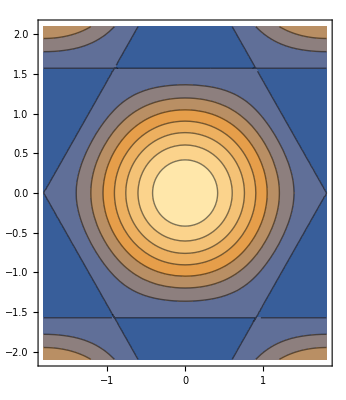

```mathematica
ContourPlot[Cos[2 (-(√3 kx)/2-ky/2)]+Cos[2 ((√3 kx)/2-ky/2)]+Cos[2 ky],{kx,-π/√3,π/√3},{ky,-π/√3/Cos[30Degree],π/√3/Cos[30Degree]},AspectRatio->Automatic]
```

```mathematica
klist=Block[{b1=-π/(√3){1,√3},b2=π/(√3){-2,0}},Flatten[Table[i*b1+j*b2,{i,0,1,0.05},{j,0,1,0.05}],1]];
```

```mathematica
klist=Block[{},Flatten[Table[{i π/(√3),j π/3},{i,-1,1,0.05},{j,-1,1,0.05}],1]];
```

```mathematica
klist2=Block[{b1={0.,π/(√3)}/Cos[30Degree],b2={0.,π/(√3)}.RotationMatrix[π/3]/Cos[30Degree],nshell=10},Flatten[Table[i/(nshell)*b1+j/(nshell)*b2,{i,-nshell,nshell},{j,Max[-nshell,-nshell-i],Min[nshell-i,nshell]}],1]];
```

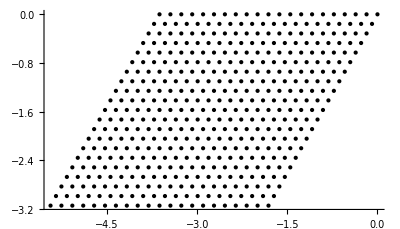

```mathematica
Graphics[Point[klist],AspectRatio->Automatic,Axes->True]
```

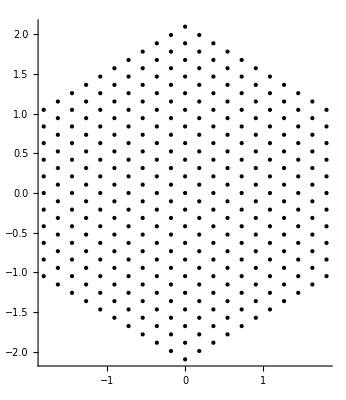

```mathematica
Graphics[Point[klist2],AspectRatio->Automatic,Axes->True]
```

```mathematica
π/√3//N
```

1.8138

```mathematica
π/√3/Cos[30Degree]//N
```

2.0944

```mathematica
(2π)/(√3)//N
```

3.6276

```mathematica
klist//Dimensions
```

{41,41,2}

```mathematica
klist2//Dimensions
```

{331,2}

```mathematica
en=H[#1,#2,0]&@@@klist;
```

```mathematica
ListPlot3D[Table[MapThread[Append[#1,#2]&,{klist,en[[All,i]]}],{i,4}],AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
en2=H[#1,#2,10,4,1]&@@@klist2;
```

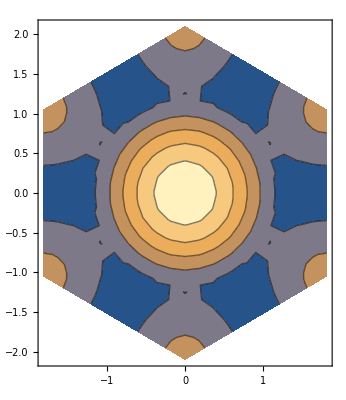

```mathematica
ListContourPlot[MapThread[Append[#1,#2]&,{klist2,en2[[All,4]]}],AspectRatio->Automatic]
```

```mathematica
ListPlot3D[Table[MapThread[Append[#1,#2]&,{klist2,en2[[All,i]]}],{i,4}],AxesLabel->{"x","y","z"},PlotRange->Full,ImageSize->Large]
```

-Graphics3D-

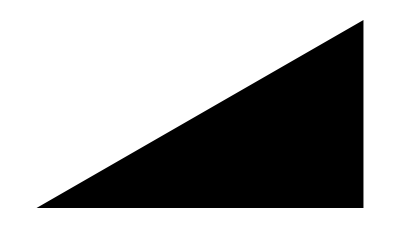

```mathematica
Graphics[Polygon[{{0,0},{π/(√3),0},{π/(√3),π/(√3)Tan[30Degree]},{0,0}}]]
```

```mathematica
klist3=Block[{b1={0.,π/(√3)}/Cos[30Degree],b2={0.,π/(√3)}.RotationMatrix[π/3]/Cos[30Degree],nshell=100,ΓM,MK,KΓ},ΓM=Transpose@{Subdivide[0,π/(√3),nshell],Subdivide[0,0,nshell]};MK=Transpose@{Subdivide[π/(√3),π/(√3),nshell],Subdivide[0,π/(√3)Tan[30Degree],nshell]};KΓ=Transpose@{Subdivide[π/(√3),0,nshell],Subdivide[π/(√3)Tan[30Degree],0,nshell]};Join[ΓM,MK,KΓ]//N];
```

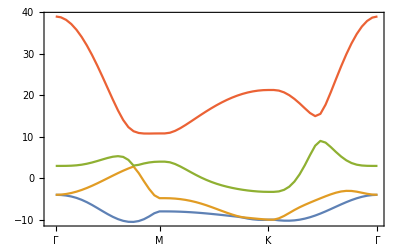

```mathematica
en3=H[#1,#2,10,4,1]&@@@klist3;ListLinePlot[Transpose@en3,Frame->True,FrameTicks->{{{1,"Γ"},{21,"M"},{42,"K"},{63,"Γ"}},Automatic}]
```

```mathematica
H[kx_,ky_,μ_,t1_,s1_,t2_,s2_]:=Block[{a1={0,1},a2={(√3)/2,-1/2},a3={-(√3)/2,-1/2},b1={-√3,0},b2={(√3)/2,3/2},b3={(√3)/2,-3/2},k={kx,ky},ham},(*ham={{0,2t1 Cos[k.a1]+2t2 Cos[k.b1],2t1 Cos[k.a3]+2t2 Cos[k.b3],2s1 Cos[k.a2]+2s2 Cos[k.b2]},
{2t1 Cos[k.a1]+2t2 Cos[k.b1],0,2t1 Cos[k.a2]+2t2 Cos[k.b2],2s1 Cos[k.a3]+2s2 Cos[k.b3]},
{2t1 Cos[k.a3]+2t2 Cos[k.b3],2t1 Cos[k.a2]+2t2 Cos[k.b2],0, 2s1 Cos[k.a1]+2s2 Cos[k.b1]},
{2s1 Cos[k.a2]+2s2 Cos[k.b2],2s1 Cos[k.a3]+2s2 Cos[k.b3],2s1 Cos[k.a1]+2s2 Cos[k.b1],μ}};*)ham={{0,t1 Exp[I k.a1]+Conjugate[t1 Exp[I k.a1]]+t2 Exp[I*k.b1]+Conjugate[t2 Exp[I*k.b1]],t1 Exp[I k.a3]+Conjugate[t1 Exp[I k.a3]]+t2 Exp[I*k.b3]+Conjugate[t2 Exp[I*k.b3]],s1 Exp[I k.a2]+Conjugate[s1 Exp[I k.a2]]+t2 Exp[I*k.b2]+Conjugate[t2 Exp[I*k.b2]]},
{t1 Exp[I k.a1]+Conjugate[t1 Exp[I k.a1]]+t2 Exp[I*k.b1]+Conjugate[t2 Exp[I*k.b1]],0,t1 Exp[I k.a2]+Conjugate[t1 Exp[I k.a2]]+t2 Exp[I*k.b2]+Conjugate[t2 Exp[I*k.b2]],s1 Exp[I k.a3]+Conjugate[s1 Exp[I k.a3]]+t2 Exp[I*k.b3]+Conjugate[t2 Exp[I*k.b3]]},
{t1 Exp[I k.a3]+Conjugate[t1 Exp[I k.a3]]+t2 Exp[I*k.b3]+Conjugate[t2 Exp[I*k.b3]],t1 Exp[I k.a2]+Conjugate[t1 Exp[I k.a2]]+t2 Exp[I*k.b2]+Conjugate[t2 Exp[I*k.b2]],0, s1 Exp[I k.a1]+Conjugate[s1 Exp[I k.a1]]+t2 Exp[I*k.b1]+Conjugate[t2 Exp[I*k.b1]]},
{s1 Exp[I k.a2]+Conjugate[s1 Exp[I k.a2]]+t2 Exp[I*k.b2]+Conjugate[t2 Exp[I*k.b2]],s1 Exp[I k.a3]+Conjugate[s1 Exp[I k.a3]]+t2 Exp[I*k.b3]+Conjugate[t2 Exp[I*k.b3]],s1 Exp[I k.a1]+Conjugate[s1 Exp[I k.a1]]+t2 Exp[I*k.b1]+Conjugate[t2 Exp[I*k.b1]],μ}};Sort[Eigenvalues[ham]]]
```

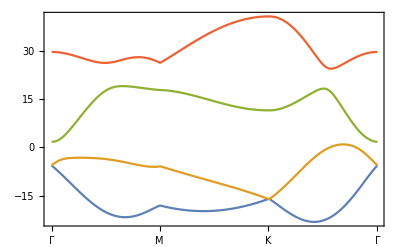

```mathematica
en3=H[#1,#2,20,6Exp[I*π/2],2Exp[I*π/3],4Exp[-I*π/4],0]&@@@klist3;ListLinePlot[Transpose@en3,Frame->True,FrameTicks->{{{1,"Γ"},{101,"M"},{202,"K"},{303,"Γ"}},Automatic}]
```

```mathematica
H[kx_,ky_,t1_,p1_]:=Block[{a1={0,1},a2={(√3)/2,-1/2},a3={-(√3)/2,-1/2},b1={-√3,0},b2={(√3)/2,3/2},b3={(√3)/2,-3/2},k={kx,ky},ham},ham={{0,t1*Exp[I*k.a1]+p1*Exp[-I*k.a1],t1*Exp[-I*k.a3]+p1*Exp[I*k.a3]},{p1 Exp[I k.a1]+t1 Exp[-I*k.a1],0,p1 Exp[-I k.a2]+t1 Exp[I k.a2]},{t1*Exp[I*k.a3]+p1*Exp[-I*k.a3],t1*Exp[-I*k.a2]+p1*Exp[I*k.a2],0}};Sort[Eigenvalues[ham]]]
```

```mathematica
en3=H[#1,#2,1,0.5]&@@@klist3;ListLinePlot[Transpose@en3,Frame->True,FrameTicks->{{{1,"Γ"},{101,"M"},{202,"K"},{303,"Γ"}},Automatic}]
```

-Graphics-

```mathematica
Block[{t2=0},{{0,t1 Exp[I k.a1]+Conjugate[t1 Exp[I k.a1]]+t2 Exp[I*k.b1]+Conjugate[t2 Exp[I*k.b1]],t1 Exp[I k.a3]+Conjugate[t1 Exp[I k.a3]]+t2 Exp[I*k.b3]+Conjugate[t2 Exp[I*k.b3]],s1 Exp[I k.a2]+Conjugate[s1 Exp[I k.a2]]+t2 Exp[I*k.b2]+Conjugate[t2 Exp[I*k.b2]]},
{t1 Exp[I k.a1]+Conjugate[t1 Exp[I k.a1]]+t2 Exp[I*k.b1]+Conjugate[t2 Exp[I*k.b1]],0,t1 Exp[I k.a2]+Conjugate[t1 Exp[I k.a2]]+t2 Exp[I*k.b2]+Conjugate[t2 Exp[I*k.b2]],s1 Exp[I k.a3]+Conjugate[s1 Exp[I k.a3]]+t2 Exp[I*k.b3]+Conjugate[t2 Exp[I*k.b3]]},
{t1 Exp[I k.a3]+Conjugate[t1 Exp[I k.a3]]+t2 Exp[I*k.b3]+Conjugate[t2 Exp[I*k.b3]],t1 Exp[I k.a2]+Conjugate[t1 Exp[I k.a2]]+t2 Exp[I*k.b2]+Conjugate[t2 Exp[I*k.b2]],0, s1 Exp[I k.a1]+Conjugate[s1 Exp[I k.a1]]+t2 Exp[I*k.b1]+Conjugate[t2 Exp[I*k.b1]]},
{s1 Exp[I k.a2]+Conjugate[s1 Exp[I k.a2]]+t2 Exp[I*k.b2]+Conjugate[t2 Exp[I*k.b2]],s1 Exp[I k.a3]+Conjugate[s1 Exp[I k.a3]]+t2 Exp[I*k.b3]+Conjugate[t2 Exp[I*k.b3]],s1 Exp[I k.a1]+Conjugate[s1 Exp[I k.a1]]+t2 Exp[I*k.b1]+Conjugate[t2 Exp[I*k.b1]],μ}}]//MatrixForm
```

(0 | ⅇ^(ⅈ k.a1) t1+ⅇ^(-ⅈ Conjugate[k.a1]) Conjugate[t1] | ⅇ^(ⅈ k.a3) t1+ⅇ^(-ⅈ Conjugate[k.a3]) Conjugate[t1] | ⅇ^(ⅈ k.a2) s1+ⅇ^(-ⅈ Conjugate[k.a2]) Conjugate[s1]
ⅇ^(ⅈ k.a1) t1+ⅇ^(-ⅈ Conjugate[k.a1]) Conjugate[t1] | 0 | ⅇ^(ⅈ k.a2) t1+ⅇ^(-ⅈ Conjugate[k.a2]) Conjugate[t1] | ⅇ^(ⅈ k.a3) s1+ⅇ^(-ⅈ Conjugate[k.a3]) Conjugate[s1]
ⅇ^(ⅈ k.a3) t1+ⅇ^(-ⅈ Conjugate[k.a3]) Conjugate[t1] | ⅇ^(ⅈ k.a2) t1+ⅇ^(-ⅈ Conjugate[k.a2]) Conjugate[t1] | 0 | ⅇ^(ⅈ k.a1) s1+ⅇ^(-ⅈ Conjugate[k.a1]) Conjugate[s1]
ⅇ^(ⅈ k.a2) s1+ⅇ^(-ⅈ Conjugate[k.a2]) Conjugate[s1] | ⅇ^(ⅈ k.a3) s1+ⅇ^(-ⅈ Conjugate[k.a3]) Conjugate[s1] | ⅇ^(ⅈ k.a1) s1+ⅇ^(-ⅈ Conjugate[k.a1]) Conjugate[s1] | μ)

```mathematica
H[π/√3,π/√3 Tan[30Degree],μ,t1,t1,t2,t2]//Simplify
```

{-(-1)^(1/3) Root[-3 t1^4-12 (-1)^(2/3) t1^3 t2+18 (-1)^(1/3) t1^2 t2^2-12 t1 t2^3-3 (-1)^(2/3) t2^4+2 (-1)^(2/3) t1^3 μ-6 (-1)^(1/3) t1^2 t2 μ+6 t1 t2^2 μ+2 (-1)^(2/3) t2^3 μ+12 (-1)^(1/3) t1^3 Conjugate[t1]-36 t1^2 t2 Conjugate[t1]-36 (-1)^(2/3) t1 t2^2 Conjugate[t1]+12 (-1)^(1/3) t2^3 Conjugate[t1]+6 t1^2 μ Conjugate[t1]+12 (-1)^(2/3) t1 t2 μ Conjugate[t1]-6 (-1)^(1/3) t2^2 μ Conjugate[t1]-18 (-1)^(2/3) t1^2 Conjugate[t1]^2+36 (-1)^(1/3) t1 t2 Conjugate[t1]^2-18 t2^2 Conjugate[t1]^2-6 (-1)^(1/3) t1 μ Conjugate[t1]^2+6 t2 μ Conjugate[t1]^2-12 t1 Conjugate[t1]^3-12 (-1)^(2/3) t2 Conjugate[t1]^3+2 (-1)^(2/3) μ Conjugate[t1]^3+3 (-1)^(1/3) Conjugate[t1]^4-12 (-1)^(2/3) t1^3 Conjugate[t2]+36 (-1)^(1/3) t1^2 t2 Conjugate[t2]-36 t1 t2^2 Conjugate[t2]-12 (-1)^(2/3) t2^3 Conjugate[t2]-6 (-1)^(1/3) t1^2 μ Conjugate[t2]+12 t1 t2 μ Conjugate[t2]+6 (-1)^(2/3) t2^2 μ Conjugate[t2]-36 t1^2 Conjugate[t1] Conjugate[t2]-72 (-1)^(2/3) t1 t2 Conjugate[t1] Conjugate[t2]+36 (-1)^(1/3) t2^2 Conjugate[t1] Conjugate[t2]+12 (-1)^(2/3) t1 μ Conjugate[t1] Conjugate[t2]-12 (-1)^(1/3) t2 μ Conjugate[t1] Conjugate[t2]+36 (-1)^(1/3) t1 Conjugate[t1]^2 Conjugate[t2]-36 t2 Conjugate[t1]^2 Conjugate[t2]+6 μ Conjugate[t1]^2 Conjugate[t2]-12 (-1)^(2/3) Conjugate[t1]^3 Conjugate[t2]+18 (-1)^(1/3) t1^2 Conjugate[t2]^2-36 t1 t2 Conjugate[t2]^2-18 (-1)^(2/3) t2^2 Conjugate[t2]^2+6 t1 μ Conjugate[t2]^2+6 (-1)^(2/3) t2 μ Conjugate[t2]^2-36 (-1)^(2/3) t1 Conjugate[t1] Conjugate[t2]^2+36 (-1)^(1/3) t2 Conjugate[t1] Conjugate[t2]^2-6 (-1)^(1/3) μ Conjugate[t1] Conjugate[t2]^2-18 Conjugate[t1]^2 Conjugate[t2]^2-12 t1 Conjugate[t2]^3-12 (-1)^(2/3) t2 Conjugate[t2]^3+2 (-1)^(2/3) μ Conjugate[t2]^3+12 (-1)^(1/3) Conjugate[t1] Conjugate[t2]^3-3 (-1)^(2/3) Conjugate[t2]^4+(-8 t1^3-24 (-1)^(2/3) t1^2 t2+24 (-1)^(1/3) t1 t2^2-8 t2^3+3 (-1)^(2/3) t1^2 μ-6 (-1)^(1/3) t1 t2 μ+3 t2^2 μ+24 (-1)^(1/3) t1^2 Conjugate[t1]-48 t1 t2 Conjugate[t1]-24 (-1)^(2/3) t2^2 Conjugate[t1]+6 t1 μ Conjugate[t1]+6 (-1)^(2/3) t2 μ Conjugate[t1]-24 (-1)^(2/3) t1 Conjugate[t1]^2+24 (-1)^(1/3) t2 Conjugate[t1]^2-3 (-1)^(1/3) μ Conjugate[t1]^2-8 Conjugate[t1]^3-24 (-1)^(2/3) t1^2 Conjugate[t2]+48 (-1)^(1/3) t1 t2 Conjugate[t2]-24 t2^2 Conjugate[t2]-6 (-1)^(1/3) t1 μ Conjugate[t2]+6 t2 μ Conjugate[t2]-48 t1 Conjugate[t1] Conjugate[t2]-48 (-1)^(2/3) t2 Conjugate[t1] Conjugate[t2]+6 (-1)^(2/3) μ Conjugate[t1] Conjugate[t2]+24 (-1)^(1/3) Conjugate[t1]^2 Conjugate[t2]+24 (-1)^(1/3) t1 Conjugate[t2]^2-24 t2 Conjugate[t2]^2+3 μ Conjugate[t2]^2-24 (-1)^(2/3) Conjugate[t1] Conjugate[t2]^2-8 Conjugate[t2]^3) #1+(-6 t1^2-12 (-1)^(2/3) t1 t2+6 (-1)^(1/3) t2^2+12 (-1)^(1/3) t1 Conjugate[t1]-12 t2 Conjugate[t1]-6 (-1)^(2/3) Conjugate[t1]^2-12 (-1)^(2/3) t1 Conjugate[t2]+12 (-1)^(1/3) t2 Conjugate[t2]-12 Conjugate[t1] Conjugate[t2]+6 (-1)^(1/3) Conjugate[t2]^2) #1^2-(-1)^(2/3) μ #1^3+#1^4&,1],-(-1)^(1/3) Root[-3 t1^4-12 (-1)^(2/3) t1^3 t2+18 (-1)^(1/3) t1^2 t2^2-12 t1 t2^3-3 (-1)^(2/3) t2^4+2 (-1)^(2/3) t1^3 μ-6 (-1)^(1/3) t1^2 t2 μ+6 t1 t2^2 μ+2 (-1)^(2/3) t2^3 μ+12 (-1)^(1/3) t1^3 Conjugate[t1]-36 t1^2 t2 Conjugate[t1]-36 (-1)^(2/3) t1 t2^2 Conjugate[t1]+12 (-1)^(1/3) t2^3 Conjugate[t1]+6 t1^2 μ Conjugate[t1]+12 (-1)^(2/3) t1 t2 μ Conjugate[t1]-6 (-1)^(1/3) t2^2 μ Conjugate[t1]-18 (-1)^(2/3) t1^2 Conjugate[t1]^2+36 (-1)^(1/3) t1 t2 Conjugate[t1]^2-18 t2^2 Conjugate[t1]^2-6 (-1)^(1/3) t1 μ Conjugate[t1]^2+6 t2 μ Conjugate[t1]^2-12 t1 Conjugate[t1]^3-12 (-1)^(2/3) t2 Conjugate[t1]^3+2 (-1)^(2/3) μ Conjugate[t1]^3+3 (-1)^(1/3) Conjugate[t1]^4-12 (-1)^(2/3) t1^3 Conjugate[t2]+36 (-1)^(1/3) t1^2 t2 Conjugate[t2]-36 t1 t2^2 Conjugate[t2]-12 (-1)^(2/3) t2^3 Conjugate[t2]-6 (-1)^(1/3) t1^2 μ Conjugate[t2]+12 t1 t2 μ Conjugate[t2]+6 (-1)^(2/3) t2^2 μ Conjugate[t2]-36 t1^2 Conjugate[t1] Conjugate[t2]-72 (-1)^(2/3) t1 t2 Conjugate[t1] Conjugate[t2]+36 (-1)^(1/3) t2^2 Conjugate[t1] Conjugate[t2]+12 (-1)^(2/3) t1 μ Conjugate[t1] Conjugate[t2]-12 (-1)^(1/3) t2 μ Conjugate[t1] Conjugate[t2]+36 (-1)^(1/3) t1 Conjugate[t1]^2 Conjugate[t2]-36 t2 Conjugate[t1]^2 Conjugate[t2]+6 μ Conjugate[t1]^2 Conjugate[t2]-12 (-1)^(2/3) Conjugate[t1]^3 Conjugate[t2]+18 (-1)^(1/3) t1^2 Conjugate[t2]^2-36 t1 t2 Conjugate[t2]^2-18 (-1)^(2/3) t2^2 Conjugate[t2]^2+6 t1 μ Conjugate[t2]^2+6 (-1)^(2/3) t2 μ Conjugate[t2]^2-36 (-1)^(2/3) t1 Conjugate[t1] Conjugate[t2]^2+36 (-1)^(1/3) t2 Conjugate[t1] Conjugate[t2]^2-6 (-1)^(1/3) μ Conjugate[t1] Conjugate[t2]^2-18 Conjugate[t1]^2 Conjugate[t2]^2-12 t1 Conjugate[t2]^3-12 (-1)^(2/3) t2 Conjugate[t2]^3+2 (-1)^(2/3) μ Conjugate[t2]^3+12 (-1)^(1/3) Conjugate[t1] Conjugate[t2]^3-3 (-1)^(2/3) Conjugate[t2]^4+(-8 t1^3-24 (-1)^(2/3) t1^2 t2+24 (-1)^(1/3) t1 t2^2-8 t2^3+3 (-1)^(2/3) t1^2 μ-6 (-1)^(1/3) t1 t2 μ+3 t2^2 μ+24 (-1)^(1/3) t1^2 Conjugate[t1]-48 t1 t2 Conjugate[t1]-24 (-1)^(2/3) t2^2 Conjugate[t1]+6 t1 μ Conjugate[t1]+6 (-1)^(2/3) t2 μ Conjugate[t1]-24 (-1)^(2/3) t1 Conjugate[t1]^2+24 (-1)^(1/3) t2 Conjugate[t1]^2-3 (-1)^(1/3) μ Conjugate[t1]^2-8 Conjugate[t1]^3-24 (-1)^(2/3) t1^2 Conjugate[t2]+48 (-1)^(1/3) t1 t2 Conjugate[t2]-24 t2^2 Conjugate[t2]-6 (-1)^(1/3) t1 μ Conjugate[t2]+6 t2 μ Conjugate[t2]-48 t1 Conjugate[t1] Conjugate[t2]-48 (-1)^(2/3) t2 Conjugate[t1] Conjugate[t2]+6 (-1)^(2/3) μ Conjugate[t1] Conjugate[t2]+24 (-1)^(1/3) Conjugate[t1]^2 Conjugate[t2]+24 (-1)^(1/3) t1 Conjugate[t2]^2-24 t2 Conjugate[t2]^2+3 μ Conjugate[t2]^2-24 (-1)^(2/3) Conjugate[t1] Conjugate[t2]^2-8 Conjugate[t2]^3) #1+(-6 t1^2-12 (-1)^(2/3) t1 t2+6 (-1)^(1/3) t2^2+12 (-1)^(1/3) t1 Conjugate[t1]-12 t2 Conjugate[t1]-6 (-1)^(2/3) Conjugate[t1]^2-12 (-1)^(2/3) t1 Conjugate[t2]+12 (-1)^(1/3) t2 Conjugate[t2]-12 Conjugate[t1] Conjugate[t2]+6 (-1)^(1/3) Conjugate[t2]^2) #1^2-(-1)^(2/3) μ #1^3+#1^4&,2],-(-1)^(1/3) Root[-3 t1^4-12 (-1)^(2/3) t1^3 t2+18 (-1)^(1/3) t1^2 t2^2-12 t1 t2^3-3 (-1)^(2/3) t2^4+2 (-1)^(2/3) t1^3 μ-6 (-1)^(1/3) t1^2 t2 μ+6 t1 t2^2 μ+2 (-1)^(2/3) t2^3 μ+12 (-1)^(1/3) t1^3 Conjugate[t1]-36 t1^2 t2 Conjugate[t1]-36 (-1)^(2/3) t1 t2^2 Conjugate[t1]+12 (-1)^(1/3) t2^3 Conjugate[t1]+6 t1^2 μ Conjugate[t1]+12 (-1)^(2/3) t1 t2 μ Conjugate[t1]-6 (-1)^(1/3) t2^2 μ Conjugate[t1]-18 (-1)^(2/3) t1^2 Conjugate[t1]^2+36 (-1)^(1/3) t1 t2 Conjugate[t1]^2-18 t2^2 Conjugate[t1]^2-6 (-1)^(1/3) t1 μ Conjugate[t1]^2+6 t2 μ Conjugate[t1]^2-12 t1 Conjugate[t1]^3-12 (-1)^(2/3) t2 Conjugate[t1]^3+2 (-1)^(2/3) μ Conjugate[t1]^3+3 (-1)^(1/3) Conjugate[t1]^4-12 (-1)^(2/3) t1^3 Conjugate[t2]+36 (-1)^(1/3) t1^2 t2 Conjugate[t2]-36 t1 t2^2 Conjugate[t2]-12 (-1)^(2/3) t2^3 Conjugate[t2]-6 (-1)^(1/3) t1^2 μ Conjugate[t2]+12 t1 t2 μ Conjugate[t2]+6 (-1)^(2/3) t2^2 μ Conjugate[t2]-36 t1^2 Conjugate[t1] Conjugate[t2]-72 (-1)^(2/3) t1 t2 Conjugate[t1] Conjugate[t2]+36 (-1)^(1/3) t2^2 Conjugate[t1] Conjugate[t2]+12 (-1)^(2/3) t1 μ Conjugate[t1] Conjugate[t2]-12 (-1)^(1/3) t2 μ Conjugate[t1] Conjugate[t2]+36 (-1)^(1/3) t1 Conjugate[t1]^2 Conjugate[t2]-36 t2 Conjugate[t1]^2 Conjugate[t2]+6 μ Conjugate[t1]^2 Conjugate[t2]-12 (-1)^(2/3) Conjugate[t1]^3 Conjugate[t2]+18 (-1)^(1/3) t1^2 Conjugate[t2]^2-36 t1 t2 Conjugate[t2]^2-18 (-1)^(2/3) t2^2 Conjugate[t2]^2+6 t1 μ Conjugate[t2]^2+6 (-1)^(2/3) t2 μ Conjugate[t2]^2-36 (-1)^(2/3) t1 Conjugate[t1] Conjugate[t2]^2+36 (-1)^(1/3) t2 Conjugate[t1] Conjugate[t2]^2-6 (-1)^(1/3) μ Conjugate[t1] Conjugate[t2]^2-18 Conjugate[t1]^2 Conjugate[t2]^2-12 t1 Conjugate[t2]^3-12 (-1)^(2/3) t2 Conjugate[t2]^3+2 (-1)^(2/3) μ Conjugate[t2]^3+12 (-1)^(1/3) Conjugate[t1] Conjugate[t2]^3-3 (-1)^(2/3) Conjugate[t2]^4+(-8 t1^3-24 (-1)^(2/3) t1^2 t2+24 (-1)^(1/3) t1 t2^2-8 t2^3+3 (-1)^(2/3) t1^2 μ-6 (-1)^(1/3) t1 t2 μ+3 t2^2 μ+24 (-1)^(1/3) t1^2 Conjugate[t1]-48 t1 t2 Conjugate[t1]-24 (-1)^(2/3) t2^2 Conjugate[t1]+6 t1 μ Conjugate[t1]+6 (-1)^(2/3) t2 μ Conjugate[t1]-24 (-1)^(2/3) t1 Conjugate[t1]^2+24 (-1)^(1/3) t2 Conjugate[t1]^2-3 (-1)^(1/3) μ Conjugate[t1]^2-8 Conjugate[t1]^3-24 (-1)^(2/3) t1^2 Conjugate[t2]+48 (-1)^(1/3) t1 t2 Conjugate[t2]-24 t2^2 Conjugate[t2]-6 (-1)^(1/3) t1 μ Conjugate[t2]+6 t2 μ Conjugate[t2]-48 t1 Conjugate[t1] Conjugate[t2]-48 (-1)^(2/3) t2 Conjugate[t1] Conjugate[t2]+6 (-1)^(2/3) μ Conjugate[t1] Conjugate[t2]+24 (-1)^(1/3) Conjugate[t1]^2 Conjugate[t2]+24 (-1)^(1/3) t1 Conjugate[t2]^2-24 t2 Conjugate[t2]^2+3 μ Conjugate[t2]^2-24 (-1)^(2/3) Conjugate[t1] Conjugate[t2]^2-8 Conjugate[t2]^3) #1+(-6 t1^2-12 (-1)^(2/3) t1 t2+6 (-1)^(1/3) t2^2+12 (-1)^(1/3) t1 Conjugate[t1]-12 t2 Conjugate[t1]-6 (-1)^(2/3) Conjugate[t1]^2-12 (-1)^(2/3) t1 Conjugate[t2]+12 (-1)^(1/3) t2 Conjugate[t2]-12 Conjugate[t1] Conjugate[t2]+6 (-1)^(1/3) Conjugate[t2]^2) #1^2-(-1)^(2/3) μ #1^3+#1^4&,3],-(-1)^(1/3) Root[-3 t1^4-12 (-1)^(2/3) t1^3 t2+18 (-1)^(1/3) t1^2 t2^2-12 t1 t2^3-3 (-1)^(2/3) t2^4+2 (-1)^(2/3) t1^3 μ-6 (-1)^(1/3) t1^2 t2 μ+6 t1 t2^2 μ+2 (-1)^(2/3) t2^3 μ+12 (-1)^(1/3) t1^3 Conjugate[t1]-36 t1^2 t2 Conjugate[t1]-36 (-1)^(2/3) t1 t2^2 Conjugate[t1]+12 (-1)^(1/3) t2^3 Conjugate[t1]+6 t1^2 μ Conjugate[t1]+12 (-1)^(2/3) t1 t2 μ Conjugate[t1]-6 (-1)^(1/3) t2^2 μ Conjugate[t1]-18 (-1)^(2/3) t1^2 Conjugate[t1]^2+36 (-1)^(1/3) t1 t2 Conjugate[t1]^2-18 t2^2 Conjugate[t1]^2-6 (-1)^(1/3) t1 μ Conjugate[t1]^2+6 t2 μ Conjugate[t1]^2-12 t1 Conjugate[t1]^3-12 (-1)^(2/3) t2 Conjugate[t1]^3+2 (-1)^(2/3) μ Conjugate[t1]^3+3 (-1)^(1/3) Conjugate[t1]^4-12 (-1)^(2/3) t1^3 Conjugate[t2]+36 (-1)^(1/3) t1^2 t2 Conjugate[t2]-36 t1 t2^2 Conjugate[t2]-12 (-1)^(2/3) t2^3 Conjugate[t2]-6 (-1)^(1/3) t1^2 μ Conjugate[t2]+12 t1 t2 μ Conjugate[t2]+6 (-1)^(2/3) t2^2 μ Conjugate[t2]-36 t1^2 Conjugate[t1] Conjugate[t2]-72 (-1)^(2/3) t1 t2 Conjugate[t1] Conjugate[t2]+36 (-1)^(1/3) t2^2 Conjugate[t1] Conjugate[t2]+12 (-1)^(2/3) t1 μ Conjugate[t1] Conjugate[t2]-12 (-1)^(1/3) t2 μ Conjugate[t1] Conjugate[t2]+36 (-1)^(1/3) t1 Conjugate[t1]^2 Conjugate[t2]-36 t2 Conjugate[t1]^2 Conjugate[t2]+6 μ Conjugate[t1]^2 Conjugate[t2]-12 (-1)^(2/3) Conjugate[t1]^3 Conjugate[t2]+18 (-1)^(1/3) t1^2 Conjugate[t2]^2-36 t1 t2 Conjugate[t2]^2-18 (-1)^(2/3) t2^2 Conjugate[t2]^2+6 t1 μ Conjugate[t2]^2+6 (-1)^(2/3) t2 μ Conjugate[t2]^2-36 (-1)^(2/3) t1 Conjugate[t1] Conjugate[t2]^2+36 (-1)^(1/3) t2 Conjugate[t1] Conjugate[t2]^2-6 (-1)^(1/3) μ Conjugate[t1] Conjugate[t2]^2-18 Conjugate[t1]^2 Conjugate[t2]^2-12 t1 Conjugate[t2]^3-12 (-1)^(2/3) t2 Conjugate[t2]^3+2 (-1)^(2/3) μ Conjugate[t2]^3+12 (-1)^(1/3) Conjugate[t1] Conjugate[t2]^3-3 (-1)^(2/3) Conjugate[t2]^4+(-8 t1^3-24 (-1)^(2/3) t1^2 t2+24 (-1)^(1/3) t1 t2^2-8 t2^3+3 (-1)^(2/3) t1^2 μ-6 (-1)^(1/3) t1 t2 μ+3 t2^2 μ+24 (-1)^(1/3) t1^2 Conjugate[t1]-48 t1 t2 Conjugate[t1]-24 (-1)^(2/3) t2^2 Conjugate[t1]+6 t1 μ Conjugate[t1]+6 (-1)^(2/3) t2 μ Conjugate[t1]-24 (-1)^(2/3) t1 Conjugate[t1]^2+24 (-1)^(1/3) t2 Conjugate[t1]^2-3 (-1)^(1/3) μ Conjugate[t1]^2-8 Conjugate[t1]^3-24 (-1)^(2/3) t1^2 Conjugate[t2]+48 (-1)^(1/3) t1 t2 Conjugate[t2]-24 t2^2 Conjugate[t2]-6 (-1)^(1/3) t1 μ Conjugate[t2]+6 t2 μ Conjugate[t2]-48 t1 Conjugate[t1] Conjugate[t2]-48 (-1)^(2/3) t2 Conjugate[t1] Conjugate[t2]+6 (-1)^(2/3) μ Conjugate[t1] Conjugate[t2]+24 (-1)^(1/3) Conjugate[t1]^2 Conjugate[t2]+24 (-1)^(1/3) t1 Conjugate[t2]^2-24 t2 Conjugate[t2]^2+3 μ Conjugate[t2]^2-24 (-1)^(2/3) Conjugate[t1] Conjugate[t2]^2-8 Conjugate[t2]^3) #1+(-6 t1^2-12 (-1)^(2/3) t1 t2+6 (-1)^(1/3) t2^2+12 (-1)^(1/3) t1 Conjugate[t1]-12 t2 Conjugate[t1]-6 (-1)^(2/3) Conjugate[t1]^2-12 (-1)^(2/3) t1 Conjugate[t2]+12 (-1)^(1/3) t2 Conjugate[t2]-12 Conjugate[t1] Conjugate[t2]+6 (-1)^(1/3) Conjugate[t2]^2) #1^2-(-1)^(2/3) μ #1^3+#1^4&,4]}

```mathematica
h=Block[{},{{0,t1*Exp[I*k.a1]+p1*Exp[-I*k.a1],t1*Exp[-I*k.a3]+p1*Exp[I*k.a3]},{p1 Exp[I k.a1]+t1 Exp[-I*k.a1],0,p1 Exp[-I k.a2]+t1 Exp[I k.a2]},{t1*Exp[I*k.a3]+p1*Exp[-I*k.a3],t1*Exp[-I*k.a2]+p1*Exp[I*k.a2],0}}]
```

{{0,ⅇ^(-ⅈ k.a1) p1+ⅇ^(ⅈ k.a1) t1,ⅇ^(ⅈ k.a3) p1+ⅇ^(-ⅈ k.a3) t1},{ⅇ^(ⅈ k.a1) p1+ⅇ^(-ⅈ k.a1) t1,0,ⅇ^(-ⅈ k.a2) p1+ⅇ^(ⅈ k.a2) t1},{ⅇ^(-ⅈ k.a3) p1+ⅇ^(ⅈ k.a3) t1,ⅇ^(ⅈ k.a2) p1+ⅇ^(-ⅈ k.a2) t1,0}}

```mathematica
ComplexExpand[h-ConjugateTranspose@h]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
h=Block[{a1={0,1},a2={(√3)/2,-1/2},a3={-(√3)/2,-1/2},k={kx,ky}},{{0,Exp[I ϕ]2Cos[k.a1],Exp[-I ϕ]2Cos[k.a2]},{Exp[-I ϕ]2Cos[k.a1],0,Exp[I ϕ]2Cos[k.a3]},{Exp[I ϕ]2Cos[k.a2],Exp[-I ϕ]2Cos[k.a3],0}}]
```

{{0,2 ⅇ^(ⅈ ϕ) Cos[ky],2 ⅇ^(-ⅈ ϕ) Cos[(√3 kx)/2-ky/2]},{2 ⅇ^(-ⅈ ϕ) Cos[ky],0,2 ⅇ^(ⅈ ϕ) Cos[(√3 kx)/2+ky/2]},{2 ⅇ^(ⅈ ϕ) Cos[(√3 kx)/2-ky/2],2 ⅇ^(-ⅈ ϕ) Cos[(√3 kx)/2+ky/2],0}}

```mathematica
h//MatrixForm
```

(0 | 2 ⅇ^(ⅈ ϕ) Cos[ky] | 2 ⅇ^(-ⅈ ϕ) Cos[(√3 kx)/2-ky/2]
2 ⅇ^(-ⅈ ϕ) Cos[ky] | 0 | 2 ⅇ^(ⅈ ϕ) Cos[(√3 kx)/2+ky/2]
2 ⅇ^(ⅈ ϕ) Cos[(√3 kx)/2-ky/2] | 2 ⅇ^(-ⅈ ϕ) Cos[(√3 kx)/2+ky/2] | 0)

```mathematica
hk=h/.Thread[{kx,ky}->{π/√3,π/√3 Tan[30Degree]}]
```

{{0,ⅇ^(ⅈ ϕ),ⅇ^(-ⅈ ϕ)},{ⅇ^(-ⅈ ϕ),0,-ⅇ^(ⅈ ϕ)},{ⅇ^(ⅈ ϕ),-ⅇ^(-ⅈ ϕ),0}}

```mathematica
Thread[{kx,ky}->{π/√3,π/√3 Tan[30Degree]}]
```

{kx→π/(√3),ky→π/3}

```mathematica
hk//Dimensions
```

{3,3}

```mathematica
eiv=Eigenvectors[hk/.ϕ->1.]
```

{{0.288675-0.5 ⅈ,-0.288675-0.5 ⅈ,0.57735+0. ⅈ},{-0.57735+8.6901×10^-17 ⅈ,0.57735+3.66118×10^-16 ⅈ,0.57735+0. ⅈ},{0.288675+0.5 ⅈ,-0.288675+0.5 ⅈ,0.57735+0. ⅈ}}

```mathematica
Outer[Times,Conjugate[eiv[[1]]],eiv[[1]]]
```

{{0.333333+0. ⅈ,0.166667-0.288675 ⅈ,0.166667+0.288675 ⅈ},{0.166667+0.288675 ⅈ,0.333333+0. ⅈ,-0.166667+0.288675 ⅈ},{0.166667-0.288675 ⅈ,-0.166667-0.288675 ⅈ,0.333333+0. ⅈ}}

```mathematica
hke=Eigenvalues[hk];
```

```mathematica
ListLinePlot[Transpose[hke/.ϕ->Range[0,2π,0.01]],DataRange->{0,2π}]
```

$Aborted[]

```mathematica
hke/.ϕ->2.
```

{0.832294-5.55112×10^-17 ⅈ,1.1588-2.22045×10^-16 ⅈ,-1.9911+3.33067×10^-16 ⅈ}

```mathematica
ListPlot[Re@(hke/.ϕ->Range[0,2π,0.01]),DataRange->{0,2π},Ticks->{Range[0,2π,π/3],Automatic}]
```

-Graphics-

```mathematica
Table[]
```

```mathematica
π/3.
```

1.0472

```mathematica
[ⅇ^(-ⅈ ϕ) √(ⅇ^(2 ⅈ ϕ)),ϕ>0]
```

ⅇ^(-ⅈ ϕ) √(ⅇ^(2 ⅈ ϕ))

```mathematica
Eigenvalues[h]
```

{2 ⅇ^(-ⅈ ϕ) Root[-1-ⅇ^(6 ⅈ ϕ)-Cos[√3 kx-ky]-ⅇ^(6 ⅈ ϕ) Cos[√3 kx-ky]-Cos[2 ky]-ⅇ^(6 ⅈ ϕ) Cos[2 ky]-Cos[√3 kx+ky]-ⅇ^(6 ⅈ ϕ) Cos[√3 kx+ky]+(-6 ⅇ^(2 ⅈ ϕ)-2 ⅇ^(2 ⅈ ϕ) Cos[√3 kx-ky]-2 ⅇ^(2 ⅈ ϕ) Cos[2 ky]-2 ⅇ^(2 ⅈ ϕ) Cos[√3 kx+ky]) #1+4 #1^3&,1],2 ⅇ^(-ⅈ ϕ) Root[-1-ⅇ^(6 ⅈ ϕ)-Cos[√3 kx-ky]-ⅇ^(6 ⅈ ϕ) Cos[√3 kx-ky]-Cos[2 ky]-ⅇ^(6 ⅈ ϕ) Cos[2 ky]-Cos[√3 kx+ky]-ⅇ^(6 ⅈ ϕ) Cos[√3 kx+ky]+(-6 ⅇ^(2 ⅈ ϕ)-2 ⅇ^(2 ⅈ ϕ) Cos[√3 kx-ky]-2 ⅇ^(2 ⅈ ϕ) Cos[2 ky]-2 ⅇ^(2 ⅈ ϕ) Cos[√3 kx+ky]) #1+4 #1^3&,2],2 ⅇ^(-ⅈ ϕ) Root[-1-ⅇ^(6 ⅈ ϕ)-Cos[√3 kx-ky]-ⅇ^(6 ⅈ ϕ) Cos[√3 kx-ky]-Cos[2 ky]-ⅇ^(6 ⅈ ϕ) Cos[2 ky]-Cos[√3 kx+ky]-ⅇ^(6 ⅈ ϕ) Cos[√3 kx+ky]+(-6 ⅇ^(2 ⅈ ϕ)-2 ⅇ^(2 ⅈ ϕ) Cos[√3 kx-ky]-2 ⅇ^(2 ⅈ ϕ) Cos[2 ky]-2 ⅇ^(2 ⅈ ϕ) Cos[√3 kx+ky]) #1+4 #1^3&,3]}

```mathematica
Simplify[Eigensystem[h/.{Thread[{kx,ky}->{π/√3,π/√3 Tan[30Degree]}]}],ϕ>0]
```

{{-ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)),1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)-√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2)),1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2))},{{-1,1,1},{(1+ⅇ^(4 ⅈ ϕ)+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2)+ⅇ^(2 ⅈ ϕ) (-2+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2)))/(2-ⅇ^(4 ⅈ ϕ)+ⅇ^(2 ⅈ ϕ) (-1+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2))),(1+ⅇ^(2 ⅈ ϕ)-2 ⅇ^(4 ⅈ ϕ)-√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2))/(-2+ⅇ^(4 ⅈ ϕ)+ⅇ^(2 ⅈ ϕ) (1-√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2))),1},{(-1-ⅇ^(4 ⅈ ϕ)+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2)+ⅇ^(2 ⅈ ϕ) (2+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2)))/(-2+ⅇ^(4 ⅈ ϕ)+ⅇ^(2 ⅈ ϕ) (1+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2))),(1+ⅇ^(2 ⅈ ϕ)-2 ⅇ^(4 ⅈ ϕ)+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2))/(-2+ⅇ^(4 ⅈ ϕ)+ⅇ^(2 ⅈ ϕ) (1+√3 √(-(-1+ⅇ^(2 ⅈ ϕ))^2))),1}}}

```mathematica
IdentityMatrix[3]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
```

```mathematica
SparseArray[{,}->1]
```